```mathematica
Quit[]
```

# Substitutions

```mathematica
masseschanging={m1->Mh,m2->MH2,m3->MH3,m4->0};
(*subsvevs={ v2->n[[1,1]] vxi,v1->n[[2,1]]vxi,v3->n[[3,1]]vxi,v4->n[[4,1]]vxi};*)
(*subsfields={EtaN->(v1+Oall[[2,1]] h+Oall[[2,2]] H2+Oall[[2,3]] H3+Oall[[2,4]]H4)/Sqrt[2],CurlyPhi->(v4+Oall[[4,1]] h+Oall[[4,2]] H2+Oall[[4,3]] H3+Oall[[4,4]] H4)/Sqrt[2],Sigma->(v3+Oall[[3,1]] h+Oall[[3,2]] H2+Oall[[3,3]] H3+Oall[[3,4]] H4)/Sqrt[2],Chi->(v2+Oall[[1,1]] h+Oall[[1,2]] H2+Oall[[1,3]] H3+Oall[[1,4]] H4)/Sqrt[2]};*)
subsfeynruleslambdas= {λχη->Lchieta,λχσ->Lchisig,λχφ->Lchiphi,λησ->Letasig,ληφ->Letaphi,λφσ->Lphisig,λpχη->Lpchieta};
subsfeynrulesvevs={vχ->v2,vσ->v3,vφ->v4,vη->v1,vξ->vxi};
(*subsfieldxi= {Xi ->(n1(vχ + Sχ3)+n2(vη+Sη1)+n3 (vσ+ Sσ)+n4(vφ + Sφ) )};
subsfieldxi2={Xi->√(2(ηdg.η+χdg.χ+σdg σ+φ φ))};*)

zeroGoldstonsfields={GZ->0,GZP->0,GZPP->0,GW->0,GWbar->0,GY->0,GYbar->0,GV->0,GVbar->0,GSDM->0,GSDMbar->0};
zeroScalarfields={h->0,H2->0,H3->0,H4->0};
zeroSDM={SDM->0};
lambdasdiagonalfeynrules={Lchi->(-1/2 Lchieta v1^2 v2-1/2 Lchisig v2 v3^2-1/2 Lchiphi v2 v4^2)/v2^3,Leta->-(1/2 Lchieta v1 v2^2+1/2 Letasig v1 v3^2+1/2 Letaphi v1 v4^2)/v1^3,Lsig->-(1/2 Letasig v1^2 v3+1/2 Lchisig v2^2 v3+1/2 Lphisig v3 v4^2)/v3^3,Lphi->-(1/2 Letaphi v1^2 v4+1/2 Lchiphi v2^2 v4+1/2 Lphisig v3^2 v4)/v4^3};
lambdasoffdiagonalfeynrules={Lchieta->8 x21,Lchisig->8 x31,Letasig->8 x32,Lchiphi->8 x41,Letaphi->8 x42,Lphisig->8 x43,Lpchieta->(2 MSDM^2)/(v1^2+v2^2)};
(*physicalfields={Aη1->(Uh21 GZ+Uh22 GZP+Uh23 GZPP),Sη1->UH21 h+UH22 H2+UH23 H3+UH24 H4,Aσ->Uh31 GZ+Uh32 GZP+Uh33 GZPP,Sσ->UH31 h+UH32 H2+UH33 H3+UH34 H4,Sφ->UH41 h+UH42 H2+UH43 H3+UH44 H4,Aχ3->Uh11 GZ+Uh12 GZP+Uh13 GZPP,Sχ3->UH11 h+UH12 H2+UH13 H3+UH14 H4,η2m->GWbar,η2p->GW,η3->normal (v2 SDM-v1 GSDM),χ1->normal (v1 SDMbar+v2 GSDMbar),χ2m->GVbar,χ2p->GV};*)
```

```mathematica
substest={(*g->Sqrt[4Pi/127.9]/Sqrt[0.23129]*)g->0.6517652952191443,tx->Sqrt[0.23129]/Sqrt[(1-4/3 0.23129)],tn->(.8)/0.6517652952191443};(*gn^2/4π < 1*)
subsye={ye3->1.0161729777009432,ye2->0.060433735962867274,ye1->0.0002922775916526531};
alphas=({vxi->√(v1^2+v2^2+v3^2+v4^2),α14->ArcTan[v2/(√(v1^2+v3^2+v4^2))],α24->ArcTan[v1/(√(v3^2+v4^2))],α34->ArcTan[v3/v4]})
vevs={v1->246,v2->10^4,v3-> 10^6,v4->10^6}
```

{vxi→√(v1^2+v2^2+v3^2+v4^2),α14→ArcTan[v2/(√(v1^2+v3^2+v4^2))],α24→ArcTan[v1/(√(v3^2+v4^2))],α34→ArcTan[v3/v4]}

{v1→246,v2→10000,v3→1000000,v4→1000000}

```mathematica
Cot[α14]/.alphas
```

(√(v1^2+v3^2+v4^2))/v2

```mathematica
Csc[α24]/.alphas
```

(√(v3^2+v4^2) √(1+v1^2/(v3^2+v4^2)))/v1

```mathematica
qyukawas3={Subscript[YD, 1,1]->.6,Subscript[YD, 2,2]->.5,YU3->.8,y^KK3->.9,h^KK3->.3,Subscript[yKK, 1,1]->.8,Subscript[yKK, 2,2]->.8,Subscript[hKK, 1,1]->.8,Subscript[hKK, 2,2]->.4}
```

{YD_(1,1)→0.6,YD_(2,2)→0.5,YU3→0.8,y^KK3→0.9,h^KK3→0.3,yKK_(1,1)→0.8,yKK_(2,2)→0.8,hKK_(1,1)→0.8,hKK_(2,2)→0.4}

```mathematica
qyukawas2={hKK3->0.3,yKK3->0.9};
```

```mathematica
qyukawas={Subscript[Yd, 1,1]->0.000027019527411193288,Subscript[Yd, 2,2]->0.0005375161304141643,Subscript[Yu, 3]->0.9920765628403456,Subscript[yd, 3]->(2.4047379395962025 hKK3)/yKK3,Subscript[yu, 1,1]->-(0.0012417484937910107 Subscript[hKK, 1,1])/Subscript[yKK, 1,1],Subscript[yu, 2,2]->-(0.730102123664159 Subscript[hKK, 2,2])/Subscript[yKK, 2,2]}/.qyukawas2/.qyukawas3
```

{Yd_(1,1)→0.0000270195,Yd_(2,2)→0.000537516,Yu_3→0.992077,yd_3→0.801579,yu_(1,1)→-0.00124175,yu_(2,2)→-0.365051}

```mathematica
alphas123=(*N@{α12->10 Pi/180,α13->10 Pi/180,α23->10 Pi/180}*)(*N@{α12->0,α13->0,α23->0}*)N@{α12-> 0 Pi/180,α13->0 Pi/180,α23->0 Pi/180}
```

{α12→0.,α13→0.,α23→0.}

```mathematica
g->Sqrt[4Pi /127.9]/Sqrt[0.23129]
```

g→0.651765

```mathematica
Sqrt[4Pi-0.0000001]
```

3.54491

# Scalar Sector

## The fields

```mathematica
η= {η1,η2m,η3};
χ={χ1,χ2m,χ3};
σ= (vσ+ Sσ + I Aσ)/√2;
φ=(vφ + Sφ)/√2;
 η1=(vη+Sη1+I Aη1)/√2;
χ3=(vχ + Sχ3 + I Aχ3)/√2;
```

Here I used the index “m” to denote the minus electric charge and “p” for the prime and plus symbol.

```mathematica
(*Element[vη|Sη1|Aη1|Sη3|Aη3|Sχ1|Aχ1|vχ|Sχ3|Aχ3|vσ|Sσ|Aσ|vφ|Sφ,Reals]*)
```

## The scalar potential

```mathematica
MatrixForm[Λ={{λ11,λχη/2,λχσ/2,λχφ/2},{λχη/2,λ22,λησ/2,ληφ/2},{λχσ/2,λησ/2,λ33,λφσ/2},{λχφ/2,ληφ/2,λφσ/2,λ44}}]//Simplify
```

(λ11 | λχη/2 | λχσ/2 | λχφ/2
λχη/2 | λ22 | λησ/2 | ληφ/2
λχσ/2 | λησ/2 | λ33 | λφσ/2
λχφ/2 | ληφ/2 | λφσ/2 | λ44)

```mathematica
Unset[λpχη]
```

```mathematica
VS =ComplexExpand[(λχ ( χ†.χ)^2 + λη (η†. η)^2 + λχη(χ†.χ)(η†.η) + λpχη (χ† . η)(η†.χ) + λχφ (χ†. χ)φ^2 + λχσ (χ†.χ)(σ*σ) + ληφ (η†.η)φ^2  + λησ(η†.η)(σ*σ) +λφ φ^4 + λσ(σ*σ)^2 + λφσ(σ*σ)φ^2 ),{η2m,χ2m,η3,χ1,σ,η1},TargetFunctions->Conjugate]/.{Conjugate[χ2m]->χ2p,Conjugate[η2m]->η2p,Conjugate[η3]->η3bar,Conjugate[χ1]->χ1bar};
Φ={Sχ3,Sη1,Sσ,Sφ,Aχ3,Aη1,Aσ,χ1,η3,η3bar,χ1bar}
Φvev={Sχ3,Sη1,Sσ,Sφ}
```

{Sχ3,Sη1,Sσ,Sφ,Aχ3,Aη1,Aσ,χ1,η3,η3bar,χ1bar}

{Sχ3,Sη1,Sσ,Sφ}

```mathematica
(*Φnovo={e1,H2,e3,e4}*)
```

```mathematica
(*Massnovo=D[VS,{Φnovo,2}]/.valoresteste/.zeroFields/.{e1->0,H2->0,e3->0,e4->0}//Simplify//Chop*)
```

```mathematica
VS
```

1/2 Aχ3^2 η3 η3bar λpχη+1/2 Sχ3^2 η3 η3bar λpχη+Sχ3 vχ η3 η3bar λpχη+1/2 vχ^2 η3 η3bar λpχη+(Aη1^4 λη)/4+1/2 Aη1^2 Sη1^2 λη+(Sη1^4 λη)/4+Aη1^2 Sη1 vη λη+Sη1^3 vη λη+1/2 Aη1^2 vη^2 λη+3/2 Sη1^2 vη^2 λη+Sη1 vη^3 λη+(vη^4 λη)/4+Aη1^2 η2m η2p λη+Sη1^2 η2m η2p λη+2 Sη1 vη η2m η2p λη+vη^2 η2m η2p λη+η2m^2 η2p^2 λη+Aη1^2 η3 η3bar λη+Sη1^2 η3 η3bar λη+2 Sη1 vη η3 η3bar λη+vη^2 η3 η3bar λη+2 η2m η2p η3 η3bar λη+η3^2 η3bar^2 λη+1/4 Aη1^2 Aσ^2 λησ+1/4 Aσ^2 Sη1^2 λησ+1/4 Aη1^2 Sσ^2 λησ+1/4 Sη1^2 Sσ^2 λησ+1/2 Aσ^2 Sη1 vη λησ+1/2 Sη1 Sσ^2 vη λησ+1/4 Aσ^2 vη^2 λησ+1/4 Sσ^2 vη^2 λησ+1/2 Aη1^2 Sσ vσ λησ+1/2 Sη1^2 Sσ vσ λησ+Sη1 Sσ vη vσ λησ+1/2 Sσ vη^2 vσ λησ+1/4 Aη1^2 vσ^2 λησ+1/4 Sη1^2 vσ^2 λησ+1/2 Sη1 vη vσ^2 λησ+1/4 vη^2 vσ^2 λησ+1/2 Aσ^2 η2m η2p λησ+1/2 Sσ^2 η2m η2p λησ+Sσ vσ η2m η2p λησ+1/2 vσ^2 η2m η2p λησ+1/2 Aσ^2 η3 η3bar λησ+1/2 Sσ^2 η3 η3bar λησ+Sσ vσ η3 η3bar λησ+1/2 vσ^2 η3 η3bar λησ+1/4 Aη1^2 Sφ^2 ληφ+1/4 Sη1^2 Sφ^2 ληφ+1/2 Sη1 Sφ^2 vη ληφ+1/4 Sφ^2 vη^2 ληφ+1/2 Aη1^2 Sφ vφ ληφ+1/2 Sη1^2 Sφ vφ ληφ+Sη1 Sφ vη vφ ληφ+1/2 Sφ vη^2 vφ ληφ+1/4 Aη1^2 vφ^2 ληφ+1/4 Sη1^2 vφ^2 ληφ+1/2 Sη1 vη vφ^2 ληφ+1/4 vη^2 vφ^2 ληφ+1/2 Sφ^2 η2m η2p ληφ+Sφ vφ η2m η2p ληφ+1/2 vφ^2 η2m η2p ληφ+1/2 Sφ^2 η3 η3bar ληφ+Sφ vφ η3 η3bar ληφ+1/2 vφ^2 η3 η3bar ληφ+(Aσ^4 λσ)/4+1/2 Aσ^2 Sσ^2 λσ+(Sσ^4 λσ)/4+Aσ^2 Sσ vσ λσ+Sσ^3 vσ λσ+1/2 Aσ^2 vσ^2 λσ+3/2 Sσ^2 vσ^2 λσ+Sσ vσ^3 λσ+(vσ^4 λσ)/4+(Sφ^4 λφ)/4+Sφ^3 vφ λφ+3/2 Sφ^2 vφ^2 λφ+Sφ vφ^3 λφ+(vφ^4 λφ)/4+1/4 Aσ^2 Sφ^2 λφσ+1/4 Sσ^2 Sφ^2 λφσ+1/2 Sσ Sφ^2 vσ λφσ+1/4 Sφ^2 vσ^2 λφσ+1/2 Aσ^2 Sφ vφ λφσ+1/2 Sσ^2 Sφ vφ λφσ+Sσ Sφ vσ vφ λφσ+1/2 Sφ vσ^2 vφ λφσ+1/4 Aσ^2 vφ^2 λφσ+1/4 Sσ^2 vφ^2 λφσ+1/2 Sσ vσ vφ^2 λφσ+1/4 vσ^2 vφ^2 λφσ+(Aχ3^4 λχ)/4+1/2 Aχ3^2 Sχ3^2 λχ+(Sχ3^4 λχ)/4+Aχ3^2 Sχ3 vχ λχ+Sχ3^3 vχ λχ+1/2 Aχ3^2 vχ^2 λχ+3/2 Sχ3^2 vχ^2 λχ+Sχ3 vχ^3 λχ+(vχ^4 λχ)/4+1/4 Aη1^2 Aχ3^2 λχη+1/4 Aχ3^2 Sη1^2 λχη+1/4 Aη1^2 Sχ3^2 λχη+1/4 Sη1^2 Sχ3^2 λχη+1/2 Aχ3^2 Sη1 vη λχη+1/2 Sη1 Sχ3^2 vη λχη+1/4 Aχ3^2 vη^2 λχη+1/4 Sχ3^2 vη^2 λχη+1/2 Aη1^2 Sχ3 vχ λχη+1/2 Sη1^2 Sχ3 vχ λχη+Sη1 Sχ3 vη vχ λχη+1/2 Sχ3 vη^2 vχ λχη+1/4 Aη1^2 vχ^2 λχη+1/4 Sη1^2 vχ^2 λχη+1/2 Sη1 vη vχ^2 λχη+1/4 vη^2 vχ^2 λχη+1/2 Aχ3^2 η2m η2p λχη+1/2 Sχ3^2 η2m η2p λχη+Sχ3 vχ η2m η2p λχη+1/2 vχ^2 η2m η2p λχη+1/2 Aχ3^2 η3 η3bar λχη+1/2 Sχ3^2 η3 η3bar λχη+Sχ3 vχ η3 η3bar λχη+1/2 vχ^2 η3 η3bar λχη+1/4 Aσ^2 Aχ3^2 λχσ+1/4 Aχ3^2 Sσ^2 λχσ+1/4 Aσ^2 Sχ3^2 λχσ+1/4 Sσ^2 Sχ3^2 λχσ+1/2 Aχ3^2 Sσ vσ λχσ+1/2 Sσ Sχ3^2 vσ λχσ+1/4 Aχ3^2 vσ^2 λχσ+1/4 Sχ3^2 vσ^2 λχσ+1/2 Aσ^2 Sχ3 vχ λχσ+1/2 Sσ^2 Sχ3 vχ λχσ+Sσ Sχ3 vσ vχ λχσ+1/2 Sχ3 vσ^2 vχ λχσ+1/4 Aσ^2 vχ^2 λχσ+1/4 Sσ^2 vχ^2 λχσ+1/2 Sσ vσ vχ^2 λχσ+1/4 vσ^2 vχ^2 λχσ+1/4 Aχ3^2 Sφ^2 λχφ+1/4 Sφ^2 Sχ3^2 λχφ+1/2 Aχ3^2 Sφ vφ λχφ+1/2 Sφ Sχ3^2 vφ λχφ+1/4 Aχ3^2 vφ^2 λχφ+1/4 Sχ3^2 vφ^2 λχφ+1/2 Sφ^2 Sχ3 vχ λχφ+Sφ Sχ3 vφ vχ λχφ+1/2 Sχ3 vφ^2 vχ λχφ+1/4 Sφ^2 vχ^2 λχφ+1/2 Sφ vφ vχ^2 λχφ+1/4 vφ^2 vχ^2 λχφ-1/2 Aη1 Aχ3 η3 λpχη χ1-1/2 ⅈ Aχ3 Sη1 η3 λpχη χ1-1/2 ⅈ Aη1 Sχ3 η3 λpχη χ1+1/2 Sη1 Sχ3 η3 λpχη χ1-1/2 ⅈ Aχ3 vη η3 λpχη χ1+1/2 Sχ3 vη η3 λpχη χ1-1/2 ⅈ Aη1 vχ η3 λpχη χ1+1/2 Sη1 vχ η3 λpχη χ1+1/2 vη vχ η3 λpχη χ1-1/2 Aη1 Aχ3 η3bar λpχη χ1bar+1/2 ⅈ Aχ3 Sη1 η3bar λpχη χ1bar+1/2 ⅈ Aη1 Sχ3 η3bar λpχη χ1bar+1/2 Sη1 Sχ3 η3bar λpχη χ1bar+1/2 ⅈ Aχ3 vη η3bar λpχη χ1bar+1/2 Sχ3 vη η3bar λpχη χ1bar+1/2 ⅈ Aη1 vχ η3bar λpχη χ1bar+1/2 Sη1 vχ η3bar λpχη χ1bar+1/2 vη vχ η3bar λpχη χ1bar+1/2 Aη1^2 λpχη χ1 χ1bar+1/2 Sη1^2 λpχη χ1 χ1bar+Sη1 vη λpχη χ1 χ1bar+1/2 vη^2 λpχη χ1 χ1bar+Aχ3^2 λχ χ1 χ1bar+Sχ3^2 λχ χ1 χ1bar+2 Sχ3 vχ λχ χ1 χ1bar+vχ^2 λχ χ1 χ1bar+1/2 Aη1^2 λχη χ1 χ1bar+1/2 Sη1^2 λχη χ1 χ1bar+Sη1 vη λχη χ1 χ1bar+1/2 vη^2 λχη χ1 χ1bar+η2m η2p λχη χ1 χ1bar+η3 η3bar λχη χ1 χ1bar+1/2 Aσ^2 λχσ χ1 χ1bar+1/2 Sσ^2 λχσ χ1 χ1bar+Sσ vσ λχσ χ1 χ1bar+1/2 vσ^2 λχσ χ1 χ1bar+1/2 Sφ^2 λχφ χ1 χ1bar+Sφ vφ λχφ χ1 χ1bar+1/2 vφ^2 λχφ χ1 χ1bar+λχ χ1^2 χ1bar^2-(ⅈ Aχ3 η2p η3 λpχη χ2m)/(√2)+(Sχ3 η2p η3 λpχη χ2m)/(√2)+(vχ η2p η3 λpχη χ2m)/(√2)+(ⅈ Aη1 η2p λpχη χ1bar χ2m)/(√2)+(Sη1 η2p λpχη χ1bar χ2m)/(√2)+(vη η2p λpχη χ1bar χ2m)/(√2)+(ⅈ Aχ3 η2m η3bar λpχη χ2p)/(√2)+(Sχ3 η2m η3bar λpχη χ2p)/(√2)+(vχ η2m η3bar λpχη χ2p)/(√2)-(ⅈ Aη1 η2m λpχη χ1 χ2p)/(√2)+(Sη1 η2m λpχη χ1 χ2p)/(√2)+(vη η2m λpχη χ1 χ2p)/(√2)+η2m η2p λpχη χ2m χ2p+Aχ3^2 λχ χ2m χ2p+Sχ3^2 λχ χ2m χ2p+2 Sχ3 vχ λχ χ2m χ2p+vχ^2 λχ χ2m χ2p+1/2 Aη1^2 λχη χ2m χ2p+1/2 Sη1^2 λχη χ2m χ2p+Sη1 vη λχη χ2m χ2p+1/2 vη^2 λχη χ2m χ2p+η2m η2p λχη χ2m χ2p+η3 η3bar λχη χ2m χ2p+1/2 Aσ^2 λχσ χ2m χ2p+1/2 Sσ^2 λχσ χ2m χ2p+Sσ vσ λχσ χ2m χ2p+1/2 vσ^2 λχσ χ2m χ2p+1/2 Sφ^2 λχφ χ2m χ2p+Sφ vφ λχφ χ2m χ2p+1/2 vφ^2 λχφ χ2m χ2p+2 λχ χ1 χ1bar χ2m χ2p+λχ χ2m^2 χ2p^2

## Lambda matrices

```mathematica
zeroFields=Map[#->0&,Join[Φ,{η2m,χ2m,η2p,χ2p}]]
```

{Sχ3→0,Sη1→0,Sσ→0,Sφ→0,Aχ3→0,Aη1→0,Aσ→0,χ1→0,η3→0,η3bar→0,χ1bar→0,η2m→0,χ2m→0,η2p→0,χ2p→0}

We want to find the conditions over the first derivative of the potential with respect to the fields that acquire VEV to be zero.

```mathematica
MatrixForm[D[VS,{Φvev,1}]/.zeroFields]
```

(vχ^3 λχ+1/2 vη^2 vχ λχη+1/2 vσ^2 vχ λχσ+1/2 vφ^2 vχ λχφ
vη^3 λη+1/2 vη vσ^2 λησ+1/2 vη vφ^2 ληφ+1/2 vη vχ^2 λχη
1/2 vη^2 vσ λησ+vσ^3 λσ+1/2 vσ vφ^2 λφσ+1/2 vσ vχ^2 λχσ
1/2 vη^2 vφ ληφ+vφ^3 λφ+1/2 vσ^2 vφ λφσ+1/2 vφ vχ^2 λχφ)

```mathematica
λχ=1/vχ^3(-1/2 vη^2 vχ λχη-1/2 vσ^2 vχ λχσ-1/2 vφ^2 vχ λχφ);
λη=-1/vη^3 (+1/2 vη vσ^2 λησ+1/2 vη vφ^2 ληφ+1/2 vη vχ^2 λχη);
λσ=-1/vσ^3 (1/2 vη^2 vσ λησ+1/2 vσ vφ^2 λφσ+1/2 vσ vχ^2 λχσ) ;
 λφ=-1/vφ^3(1/2 vη^2 vφ ληφ+1/2 vσ^2 vφ λφσ+1/2 vφ vχ^2 λχφ) ;
```

```mathematica
x11/.alphas/.vevs/.alphas123/.m1->125.4
```

x11

```mathematica
x22/.subsfeynrulesvevs/.alphas/.vevs/.alphas123/.m1->125.4/.m2->1000
```

x22

```mathematica
λη/.subsfeynrulesvevs/.alphas/.vevs/.alphas123/.m1->125.4
```

(-123000000000000 λησ-123000000000000 ληφ-12300000000 λχη)/14886936

```mathematica
(*MatrixForm[Λcoef =1/2 (ConstantArray[1,{4,4}]+IdentityMatrix[4])Coefficient[VS,Outer[Times,Φvev^2,Φvev^2]]]*)
```

```mathematica
(*ClearAll[λχ,λχη,λη,λχσ,λησ,λχφ,ληφ,λφσ,λφ,λσ]*)
```

Since we know the masses  m_1, ..., m_4, we have the relation M_s= O M_D O^-1, where O is a unitary matrix that we are going to compute now.

```mathematica
MD = DiagonalMatrix[{Subscript[m, 1],Subscript[m, 2],Subscript[m, 3],Subscript[m, 4]}]
```

{{m_1,0,0,0},{0,m_2,0,0},{0,0,m_3,0},{0,0,0,m_4}}

```mathematica
O12 = RotationMatrix[-α12,{{1,0,0,0},{0,1,0,0}}];
O13 =RotationMatrix[α13,{{0,0,1,0},{1,0,0,0}}];
O23=RotationMatrix[-α23,{{0,1,0,0},{0,0,1,0}}];
O14=RotationMatrix[-α14,{{1,0,0,0},{0,0,0,1}}];
O24=RotationMatrix[-α24,{{0,1,0,0},{0,0,0,1}}];
O34=RotationMatrix[-α34,{{0,0,1,0},{0,0,0,1}}];
```

It was chosen the minus sign in front of each angle in such a way that each rotation matrix corresponds to those commumly used in the literature.

```mathematica
Oall = O34.O24.O14.O23.O13.O12//Simplify
```

{{Cos[α12] Cos[α13] Cos[α14],Cos[α13] Cos[α14] Sin[α12],Cos[α14] Sin[α13],Sin[α14]},{-Cos[α23] Cos[α24] Sin[α12]-Cos[α12] (Cos[α24] Sin[α13] Sin[α23]+Cos[α13] Sin[α14] Sin[α24]),Cos[α12] Cos[α23] Cos[α24]-Sin[α12] (Cos[α24] Sin[α13] Sin[α23]+Cos[α13] Sin[α14] Sin[α24]),Cos[α13] Cos[α24] Sin[α23]-Sin[α13] Sin[α14] Sin[α24],Cos[α14] Sin[α24]},{Sin[α12] (Cos[α34] Sin[α23]+Cos[α23] Sin[α24] Sin[α34])-Cos[α12] (Cos[α23] Cos[α34] Sin[α13]+(Cos[α13] Cos[α24] Sin[α14]-Sin[α13] Sin[α23] Sin[α24]) Sin[α34]),-Cos[α12] Cos[α34] Sin[α23]+Sin[α12] (-Cos[α13] Cos[α24] Sin[α14]+Sin[α13] Sin[α23] Sin[α24]) Sin[α34]-Cos[α23] (Cos[α34] Sin[α12] Sin[α13]+Cos[α12] Sin[α24] Sin[α34]),-Cos[α24] Sin[α13] Sin[α14] Sin[α34]+Cos[α13] (Cos[α23] Cos[α34]-Sin[α23] Sin[α24] Sin[α34]),Cos[α14] Cos[α24] Sin[α34]},{Sin[α12] (Cos[α23] Cos[α34] Sin[α24]-Sin[α23] Sin[α34])+Cos[α12] (-Cos[α13] Cos[α24] Cos[α34] Sin[α14]+Sin[α13] (Cos[α34] Sin[α23] Sin[α24]+Cos[α23] Sin[α34])),-Cos[α13] Cos[α24] Cos[α34] Sin[α12] Sin[α14]+Sin[α12] Sin[α13] (Cos[α34] Sin[α23] Sin[α24]+Cos[α23] Sin[α34])+Cos[α12] (-Cos[α23] Cos[α34] Sin[α24]+Sin[α23] Sin[α34]),-Cos[α24] Cos[α34] Sin[α13] Sin[α14]-Cos[α13] (Cos[α34] Sin[α23] Sin[α24]+Cos[α23] Sin[α34]),Cos[α14] Cos[α24] Cos[α34]}}

```mathematica
Inverse[Oall][[1]]/.N@{α12->90 Pi/180,α13->0 Pi/180,α23->0 Pi/180}/.alphas/.vevs//Chop//N//MatrixForm
```

(0.
-1.
0.000123
0.000123)

The flat direction is the last column because it is simpler.

```mathematica
vevs
```

{v1→246,v2→10000,v3→1000000,v4→1000000}

```mathematica
N@{α12->90 Pi/180,α13->0 Pi/180,α23->0 Pi/180}
```

{α12→1.5708,α13→0.,α23→0.}

```mathematica
(*MatrixForm[X={{x1},{x2},{x3},{x4}}]*)
```

```mathematica
(*Solve[Oallᵀ.X==UnitVector[4,4],{x1,x2,x3,x4}]//FullSimplify*)
```

```mathematica
MatrixForm[n={{Sin[α14]},{Cos[α14] Sin[α24]},{Cos[α14] Cos[α24] Sin[α34]},{Cos[α14] Cos[α24] Cos[α34]}}]/.alphas
```

(v2/(√(v1^2+v3^2+v4^2) √(1+v2^2/(v1^2+v3^2+v4^2)))
v1/(√(v3^2+v4^2) √(1+v1^2/(v3^2+v4^2)) √(1+v2^2/(v1^2+v3^2+v4^2)))
v3/(√(1+v3^2/v4^2) v4 √(1+v1^2/(v3^2+v4^2)) √(1+v2^2/(v1^2+v3^2+v4^2)))
1/(√(1+v3^2/v4^2) √(1+v1^2/(v3^2+v4^2)) √(1+v2^2/(v1^2+v3^2+v4^2))))

```mathematica
MatrixForm[nᵀ.(MD^2). n//FullSimplify]
```

(Sin[α14]^2 m_1^2+Cos[α14]^2 (Sin[α24]^2 m_2^2+Cos[α24]^2 (Sin[α34]^2 m_3^2+Cos[α34]^2 m_4^2)))

```mathematica
(Oall[[1]])/.alphas/.alphas123/.vevs/.m1->125.4/.m2->1000/.m3->1000000//MatrixForm//N
```

(0.999975
0.
0.
0.00707089)

```mathematica
nnTinv=(n.nᵀ)^(-1)
```

{{Csc[α14]^2,Csc[α14] Csc[α24] Sec[α14],Csc[α14] Csc[α34] Sec[α14] Sec[α24],Csc[α14] Sec[α14] Sec[α24] Sec[α34]},{Csc[α14] Csc[α24] Sec[α14],Csc[α24]^2 Sec[α14]^2,Csc[α24] Csc[α34] Sec[α14]^2 Sec[α24],Csc[α24] Sec[α14]^2 Sec[α24] Sec[α34]},{Csc[α14] Csc[α34] Sec[α14] Sec[α24],Csc[α24] Csc[α34] Sec[α14]^2 Sec[α24],Csc[α34]^2 Sec[α14]^2 Sec[α24]^2,Csc[α34] Sec[α14]^2 Sec[α24]^2 Sec[α34]},{Csc[α14] Sec[α14] Sec[α24] Sec[α34],Csc[α24] Sec[α14]^2 Sec[α24] Sec[α34],Csc[α34] Sec[α14]^2 Sec[α24]^2 Sec[α34],Sec[α14]^2 Sec[α24]^2 Sec[α34]^2}}

To find the physical states, we need to find the basis of MD, so

```mathematica
(*Sχ3=Oall[[1,1]]e1+Oall[[1,2]]e2+Oall[[1,3]]e3+Oall[[1,4]] e4
Sη1=Oall[[2,1]]e1+Oall[[2,2]]e2+Oall[[2,3]]e3+Oall[[2,4]] e4
Sσ=Oall[[3,1]]e1+Oall[[3,2]]e2+Oall[[3,3]]e3+Oall[[3,4]] e4
Sφ=Oall[[4,1]]e1+Oall[[4,2]]e2+Oall[[4,3]]e3+Oall[[4,4]] e4*)
```

The Higgs is written as

```mathematica
Oall[[1,1]]/.alphas/.{α12->89}
```

(Cos[89] Cos[α13])/(√(1+v2^2/(v1^2+v3^2+v4^2)))

in basis {Sχ3, Sη1, Sσ, Sφ}

## Mass matrices

```mathematica
Subscript[m, 4]=0
```

0

```mathematica
(*v=vξ n *)
```

```mathematica
(*ClearAll[λpχη,vχ,vη,vσ,vφ]*)
```

significa que vξ > vσ.

## CP-even mass matrix

So the mass matrix is given by

```mathematica
(*MatrixForm[MS2 = Oall. MD^2. Inverse[Oall] //Simplify]*)
```

```mathematica
MatrixForm[MS2={{Cos[α12]^2 Cos[α13]^2 Cos[α14]^2 m1^2+Cos[α13]^2 Cos[α14]^2 Sin[α12]^2 m2^2+Cos[α14]^2 Sin[α13]^2 m3^2+Cos[α13]^2 Sin[α14]^2 Subscript[m, 4]^2+Sin[α13]^2 Sin[α14]^2 Subscript[m, 4]^2,-1/2 Cos[α14] ((Cos[α13] Cos[α23] Cos[α24] Sin[2 α12]+Cos[α12]^2 Cos[α24] Sin[2 α13] Sin[α23]+2 Cos[α12]^2 Cos[α13]^2 Sin[α14] Sin[α24]) m1^2+(-Cos[α13] Cos[α23] Cos[α24] Sin[2 α12]+Cos[α24] Sin[α12]^2 Sin[2 α13] Sin[α23]+2 Cos[α13]^2 Sin[α12]^2 Sin[α14] Sin[α24]) m2^2-Cos[α24] Sin[2 α13] Sin[α23] m3^2+2 Sin[α13]^2 Sin[α14] Sin[α24] m3^2-2 Sin[α14] Sin[α24] Subscript[m, 4]^2),-1/4 Cos[α14] ((-2 Cos[α13] Sin[2 α12] (Cos[α34] Sin[α23]+Cos[α23] Sin[α24] Sin[α34])+2 Cos[α12]^2 (Cos[α23] Cos[α34] Sin[2 α13]+(2 Cos[α13]^2 Cos[α24] Sin[α14]-Sin[2 α13] Sin[α23] Sin[α24]) Sin[α34])) m1^2+(2 Cos[α23] (Cos[α34] Sin[α12]^2 Sin[2 α13]+Cos[α13] Sin[2 α12] Sin[α24] Sin[α34])+2 Cos[α13] (Cos[α34] Sin[2 α12] Sin[α23]+2 Sin[α12]^2 (Cos[α13] Cos[α24] Sin[α14]-Sin[α13] Sin[α23] Sin[α24]) Sin[α34])) m2^2+2 (-Cos[α23] Cos[α34] Sin[2 α13]+(2 Cos[α24] Sin[α13]^2 Sin[α14]+Sin[2 α13] Sin[α23] Sin[α24]) Sin[α34]) m3^2-4 Cos[α24] Sin[α14] Sin[α34] Subscript[m, 4]^2),-1/4 Cos[α14] (-2 (Cos[α13] Sin[2 α12] (Cos[α23] Cos[α34] Sin[α24]-Sin[α23] Sin[α34])+Cos[α12]^2 (-2 Cos[α13]^2 Cos[α24] Cos[α34] Sin[α14]+Sin[2 α13] (Cos[α34] Sin[α23] Sin[α24]+Cos[α23] Sin[α34]))) m1^2-(-4 Cos[α13]^2 Cos[α24] Cos[α34] Sin[α12]^2 Sin[α14]+2 Sin[α12]^2 Sin[2 α13] (Cos[α34] Sin[α23] Sin[α24]+Cos[α23] Sin[α34])+2 Cos[α13] Sin[2 α12] (-Cos[α23] Cos[α34] Sin[α24]+Sin[α23] Sin[α34])) m2^2+2 (2 Cos[α24] Cos[α34] Sin[α13]^2 Sin[α14]+Sin[2 α13] (Cos[α34] Sin[α23] Sin[α24]+Cos[α23] Sin[α34])) m3^2-4 Cos[α24] Cos[α34] Sin[α14] Subscript[m, 4]^2)},{Cos[α14] (-1/2 (Cos[α13] Cos[α23] Cos[α24] Sin[2 α12]+Cos[α12]^2 Cos[α24] Sin[2 α13] Sin[α23]+2 Cos[α12]^2 Cos[α13]^2 Sin[α14] Sin[α24]) m1^2-1/2 Sin[α12] (-2 Cos[α12] Cos[α13] Cos[α23] Cos[α24]+Sin[α12] (Cos[α24] Sin[2 α13] Sin[α23]+2 Cos[α13]^2 Sin[α14] Sin[α24])) m2^2+Cos[α13] Cos[α24] Sin[α13] Sin[α23] m3^2-Sin[α13]^2 Sin[α14] Sin[α24] m3^2+Cos[α13]^2 Sin[α14] Sin[α24] Subscript[m, 4]^2+Sin[α13]^2 Sin[α14] Sin[α24] Subscript[m, 4]^2),1/4 (4 (Cos[α23] Cos[α24] Sin[α12]+Cos[α12] (Cos[α24] Sin[α13] Sin[α23]+Cos[α13] Sin[α14] Sin[α24]))^2 m1^2+4 (Cos[α12] Cos[α23] Cos[α24]-Sin[α12] (Cos[α24] Sin[α13] Sin[α23]+Cos[α13] Sin[α14] Sin[α24]))^2 m2^2+4 Cos[α13]^2 Cos[α14]^2 Cos[α24]^2 Sin[α23]^2 m3^2+4 Cos[α13]^2 Cos[α24]^2 Sin[α14]^2 Sin[α23]^2 m3^2+4 Cos[α23]^2 Sin[α13]^2 Sin[α14]^2 Sin[α24]^2 m3^2+4 Sin[α13]^2 Sin[α14]^2 Sin[α23]^2 Sin[α24]^2 m3^2-Cos[α14]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24] m3^2-Cos[α23]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24] m3^2-Sin[2 α13] Sin[α14]^3 Sin[α23] Sin[2 α24] m3^2-Sin[2 α13] Sin[α14] Sin[α23]^3 Sin[2 α24] m3^2+4 Cos[α13]^2 Cos[α14]^2 Cos[α23]^2 Sin[α24]^2 Subscript[m, 4]^2+4 Cos[α14]^2 Cos[α23]^2 Sin[α13]^2 Sin[α24]^2 Subscript[m, 4]^2+4 Cos[α13]^2 Cos[α14]^2 Sin[α23]^2 Sin[α24]^2 Subscript[m, 4]^2+4 Cos[α14]^2 Sin[α13]^2 Sin[α23]^2 Sin[α24]^2 Subscript[m, 4]^2),1/8 (-8 (Cos[α23] Cos[α24] Sin[α12]+Cos[α12] (Cos[α24] Sin[α13] Sin[α23]+Cos[α13] Sin[α14] Sin[α24])) (Sin[α12] (Cos[α34] Sin[α23]+Cos[α23] Sin[α24] Sin[α34])-Cos[α12] (Cos[α23] Cos[α34] Sin[α13]+(Cos[α13] Cos[α24] Sin[α14]-Sin[α13] Sin[α23] Sin[α24]) Sin[α34])) m1^2-8 (Cos[α12] Cos[α23] Cos[α24]-Sin[α12] (Cos[α24] Sin[α13] Sin[α23]+Cos[α13] Sin[α14] Sin[α24])) (Cos[α12] Cos[α34] Sin[α23]+Sin[α12] (Cos[α13] Cos[α24] Sin[α14]-Sin[α13] Sin[α23] Sin[α24]) Sin[α34]+Cos[α23] (Cos[α34] Sin[α12] Sin[α13]+Cos[α12] Sin[α24] Sin[α34])) m2^2+2 Cos[α24] Cos[α34] Sin[2 α23] m3^2+2 Cos[α13]^2 Cos[α24] Cos[α34] Sin[2 α23] m3^2-2 Cos[α24] Cos[α34] Sin[α13]^2 Sin[2 α23] m3^2-4 Cos[α23] Cos[α34] Sin[2 α13] Sin[α14] Sin[α24] m3^2-4 Cos[α24]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[α34] m3^2+4 Sin[2 α13] Sin[α14] Sin[α23] Sin[α24]^2 Sin[α34] m3^2-2 Cos[α13]^2 Sin[2 α24] Sin[α34] m3^2-Cos[α14]^2 Sin[2 α24] Sin[α34] m3^2+Cos[α13]^2 Cos[α14]^2 Sin[2 α24] Sin[α34] m3^2+Cos[α23]^2 Sin[2 α24] Sin[α34] m3^2+Cos[α13]^2 Cos[α23]^2 Sin[2 α24] Sin[α34] m3^2+2 Sin[α13]^2 Sin[2 α24] Sin[α34] m3^2-Cos[α14]^2 Sin[α13]^2 Sin[2 α24] Sin[α34] m3^2-Cos[α23]^2 Sin[α13]^2 Sin[2 α24] Sin[α34] m3^2+Sin[α14]^2 Sin[2 α24] Sin[α34] m3^2-Cos[α13]^2 Sin[α14]^2 Sin[2 α24] Sin[α34] m3^2+Sin[α13]^2 Sin[α14]^2 Sin[2 α24] Sin[α34] m3^2-Sin[α23]^2 Sin[2 α24] Sin[α34] m3^2-Cos[α13]^2 Sin[α23]^2 Sin[2 α24] Sin[α34] m3^2+Sin[α13]^2 Sin[α23]^2 Sin[2 α24] Sin[α34] m3^2+2 Sin[2 α24] Sin[α34] Subscript[m, 4]^2+2 Cos[α14]^2 Sin[2 α24] Sin[α34] Subscript[m, 4]^2-2 Sin[α14]^2 Sin[2 α24] Sin[α34] Subscript[m, 4]^2),1/8 (-8 (Cos[α23] Cos[α24] Sin[α12]+Cos[α12] (Cos[α24] Sin[α13] Sin[α23]+Cos[α13] Sin[α14] Sin[α24])) (Sin[α12] (Cos[α23] Cos[α34] Sin[α24]-Sin[α23] Sin[α34])+Cos[α12] (-Cos[α13] Cos[α24] Cos[α34] Sin[α14]+Sin[α13] (Cos[α34] Sin[α23] Sin[α24]+Cos[α23] Sin[α34]))) m1^2-8 (Cos[α12] Cos[α23] Cos[α24]-Sin[α12] (Cos[α24] Sin[α13] Sin[α23]+Cos[α13] Sin[α14] Sin[α24])) (Cos[α13] Cos[α24] Cos[α34] Sin[α12] Sin[α14]-Sin[α12] Sin[α13] (Cos[α34] Sin[α23] Sin[α24]+Cos[α23] Sin[α34])+Cos[α12] (Cos[α23] Cos[α34] Sin[α24]-Sin[α23] Sin[α34])) m2^2-4 Cos[α24]^2 Cos[α34] Sin[2 α13] Sin[α14] Sin[α23] m3^2+4 Cos[α34] Sin[2 α13] Sin[α14] Sin[α23] Sin[α24]^2 m3^2-2 Cos[α13]^2 Cos[α34] Sin[2 α24] m3^2-Cos[α14]^2 Cos[α34] Sin[2 α24] m3^2+Cos[α13]^2 Cos[α14]^2 Cos[α34] Sin[2 α24] m3^2+Cos[α23]^2 Cos[α34] Sin[2 α24] m3^2+Cos[α13]^2 Cos[α23]^2 Cos[α34] Sin[2 α24] m3^2+2 Cos[α34] Sin[α13]^2 Sin[2 α24] m3^2-Cos[α14]^2 Cos[α34] Sin[α13]^2 Sin[2 α24] m3^2-Cos[α23]^2 Cos[α34] Sin[α13]^2 Sin[2 α24] m3^2+Cos[α34] Sin[α14]^2 Sin[2 α24] m3^2-Cos[α13]^2 Cos[α34] Sin[α14]^2 Sin[2 α24] m3^2+Cos[α34] Sin[α13]^2 Sin[α14]^2 Sin[2 α24] m3^2-Cos[α34] Sin[α23]^2 Sin[2 α24] m3^2-Cos[α13]^2 Cos[α34] Sin[α23]^2 Sin[2 α24] m3^2+Cos[α34] Sin[α13]^2 Sin[α23]^2 Sin[2 α24] m3^2-2 Cos[α24] Sin[2 α23] Sin[α34] m3^2-2 Cos[α13]^2 Cos[α24] Sin[2 α23] Sin[α34] m3^2+2 Cos[α24] Sin[α13]^2 Sin[2 α23] Sin[α34] m3^2+4 Cos[α23] Sin[2 α13] Sin[α14] Sin[α24] Sin[α34] m3^2+2 Cos[α34] Sin[2 α24] Subscript[m, 4]^2+2 Cos[α14]^2 Cos[α34] Sin[2 α24] Subscript[m, 4]^2-2 Cos[α34] Sin[α14]^2 Sin[2 α24] Subscript[m, 4]^2)},{1/2 Cos[α14] ((Cos[α13] Sin[2 α12] (Cos[α34] Sin[α23]+Cos[α23] Sin[α24] Sin[α34])+Cos[α12]^2 (-Cos[α23] Cos[α34] Sin[2 α13]+(-2 Cos[α13]^2 Cos[α24] Sin[α14]+Sin[2 α13] Sin[α23] Sin[α24]) Sin[α34])) m1^2-(Cos[α13] Cos[α34] Sin[2 α12] Sin[α23]+2 Cos[α13]^2 Cos[α24] Sin[α12]^2 Sin[α14] Sin[α34]-Sin[α12]^2 Sin[2 α13] Sin[α23] Sin[α24] Sin[α34]+Cos[α23] (Cos[α34] Sin[α12]^2 Sin[2 α13]+Cos[α13] Sin[2 α12] Sin[α24] Sin[α34])) m2^2+Cos[α23] Cos[α34] Sin[2 α13] m3^2-2 Cos[α24] Sin[α13]^2 Sin[α14] Sin[α34] m3^2-Sin[2 α13] Sin[α23] Sin[α24] Sin[α34] m3^2+2 Cos[α13]^2 Cos[α24] Sin[α14] Sin[α34] Subscript[m, 4]^2+2 Cos[α24] Sin[α13]^2 Sin[α14] Sin[α34] Subscript[m, 4]^2),1/8 ((4 Cos[α13]^3 Cos[α23] Cos[α24]^2 Sin[2 α12] Sin[α14] Sin[α34]-4 Cos[α13] Sin[2 α12] Sin[α14] (Cos[α23]^2 Cos[α34] Sin[α23] Sin[α24]+Cos[α34] Sin[α23]^3 Sin[α24]+Cos[α23]^3 Sin[α24]^2 Sin[α34]-Cos[α23] (Cos[α14]^2 Cos[α24]^2 Sin[α13]^2+Cos[α24]^2 Sin[α13]^2 Sin[α14]^2-Sin[α23]^2 Sin[α24]^2) Sin[α34])+Cos[α14]^2 (4 Cos[α24] Cos[α34] Sin[α13] (-Sin[2 α12] Sin[α23]^2+Cos[2 α12] Sin[α13] Sin[2 α23])+4 Cos[α12]^2 Cos[α24]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[α34]-Sin[α13] (4 Cos[α12]^2 Sin[α13] Sin[α23]^2+Sin[2 α12] (1+Sin[α13]^2) Sin[2 α23]) Sin[2 α24] Sin[α34]+4 Cos[α23]^2 Sin[α13]^2 (Cos[α24] Cos[α34] Sin[2 α12] Sin[α13]-Sin[α12]^2 Sin[2 α24] Sin[α34]))+Sin[α14] (4 Cos[α24] Cos[α34] Sin[α13] Sin[α14] (-Sin[2 α12] Sin[α23]^2+Cos[2 α12] Sin[α13] Sin[2 α23])+4 Cos[α12]^2 Cos[α23]^3 Cos[α34] Sin[2 α13] Sin[α24]+4 Cos[α12]^2 Cos[α23] Cos[α34] Sin[2 α13] Sin[α23]^2 Sin[α24]+4 Cos[α12]^2 Cos[α24]^2 Sin[2 α13] Sin[α14]^2 Sin[α23] Sin[α34]-(Sin[2 α12] Sin[α13] (1+Sin[α13]^2) Sin[α14] Sin[2 α23] Sin[2 α24]+4 Cos[α12]^2 Sin[α23]^2 (Sin[2 α13] Sin[α23] Sin[α24]^2+Sin[α13]^2 Sin[α14] Sin[2 α24])) Sin[α34]+4 Cos[α23]^2 (Cos[α24] Cos[α34] Sin[2 α12] Sin[α13]^3 Sin[α14]-(Cos[α12]^2 Sin[2 α13] Sin[α23] Sin[α24]^2+Sin[α12]^2 Sin[α13]^2 Sin[α14] Sin[2 α24]) Sin[α34]))+Cos[α13]^2 (Sin[α14]^2 (-4 Cos[α24] Cos[α34] Sin[α12]^2 Sin[2 α23]+(4 Cos[α12]^2 Sin[α23]^2-Sin[2 α12] Sin[α13] Sin[2 α23]) Sin[2 α24] Sin[α34]+4 Cos[α23]^2 (Cos[α24] Cos[α34] Sin[2 α12] Sin[α13]+Cos[2 α12] Sin[2 α24] Sin[α34]))+Cos[α14]^2 (4 Cos[α23]^2 (Cos[α24] Cos[α34] Sin[2 α12] Sin[α13]-Sin[α12]^2 Sin[2 α24] Sin[α34])-Sin[2 α23] (4 Cos[α24] Cos[α34] Sin[α12]^2+Sin[2 α12] Sin[α13] Sin[2 α24] Sin[α34])))) m1^2-8 (Cos[α12] Cos[α23] Cos[α24]-Sin[α12] (Cos[α24] Sin[α13] Sin[α23]+Cos[α13] Sin[α14] Sin[α24])) (Cos[α12] Cos[α34] Sin[α23]+Sin[α12] (Cos[α13] Cos[α24] Sin[α14]-Sin[α13] Sin[α23] Sin[α24]) Sin[α34]+Cos[α23] (Cos[α34] Sin[α12] Sin[α13]+Cos[α12] Sin[α24] Sin[α34])) m2^2+2 Cos[α24] Cos[α34] Sin[2 α23] m3^2+2 Cos[α13]^2 Cos[α24] Cos[α34] Sin[2 α23] m3^2-2 Cos[α24] Cos[α34] Sin[α13]^2 Sin[2 α23] m3^2-4 Cos[α23] Cos[α34] Sin[2 α13] Sin[α14] Sin[α24] m3^2-4 Cos[α24]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[α34] m3^2+4 Sin[2 α13] Sin[α14] Sin[α23] Sin[α24]^2 Sin[α34] m3^2-2 Cos[α13]^2 Sin[2 α24] Sin[α34] m3^2-Cos[α14]^2 Sin[2 α24] Sin[α34] m3^2+Cos[α13]^2 Cos[α14]^2 Sin[2 α24] Sin[α34] m3^2+Cos[α23]^2 Sin[2 α24] Sin[α34] m3^2+Cos[α13]^2 Cos[α23]^2 Sin[2 α24] Sin[α34] m3^2+2 Sin[α13]^2 Sin[2 α24] Sin[α34] m3^2-Cos[α14]^2 Sin[α13]^2 Sin[2 α24] Sin[α34] m3^2-Cos[α23]^2 Sin[α13]^2 Sin[2 α24] Sin[α34] m3^2+Sin[α14]^2 Sin[2 α24] Sin[α34] m3^2-Cos[α13]^2 Sin[α14]^2 Sin[2 α24] Sin[α34] m3^2+Sin[α13]^2 Sin[α14]^2 Sin[2 α24] Sin[α34] m3^2-Sin[α23]^2 Sin[2 α24] Sin[α34] m3^2-Cos[α13]^2 Sin[α23]^2 Sin[2 α24] Sin[α34] m3^2+Sin[α13]^2 Sin[α23]^2 Sin[2 α24] Sin[α34] m3^2+2 Sin[2 α24] Sin[α34] Subscript[m, 4]^2+2 Cos[α14]^2 Sin[2 α24] Sin[α34] Subscript[m, 4]^2-2 Sin[α14]^2 Sin[2 α24] Sin[α34] Subscript[m, 4]^2),1/4 (1/64 (16 Sin[α12] (Cos[α34] Sin[α23]+Cos[α23] Sin[α24] Sin[α34])-16 Cos[α12] (Cos[α23] Cos[α34] Sin[α13]+(Cos[α13] Cos[α24] Sin[α14]-Sin[α13] Sin[α23] Sin[α24]) Sin[α34]))^2 m1^2+4 (Cos[α12] Cos[α34] Sin[α23]+Sin[α12] (Cos[α13] Cos[α24] Sin[α14]-Sin[α13] Sin[α23] Sin[α24]) Sin[α34]+Cos[α23] (Cos[α34] Sin[α12] Sin[α13]+Cos[α12] Sin[α24] Sin[α34]))^2 m2^2+4 Cos[α13]^2 Cos[α14]^2 Cos[α23]^2 Cos[α24]^2 Cos[α34]^2 m3^2+4 Cos[α13]^2 Cos[α23]^2 Cos[α24]^2 Cos[α34]^2 Sin[α14]^2 m3^2+4 Cos[α13]^2 Cos[α14]^2 Cos[α23]^2 Cos[α34]^2 Sin[α24]^2 m3^2+4 Cos[α13]^2 Cos[α23]^2 Cos[α34]^2 Sin[α14]^2 Sin[α24]^2 m3^2+4 Cos[α23]^2 Cos[α24]^2 Sin[α13]^2 Sin[α14]^2 Sin[α34]^2 m3^2+4 Cos[α24]^2 Sin[α13]^2 Sin[α14]^2 Sin[α23]^2 Sin[α34]^2 m3^2+4 Cos[α13]^2 Cos[α14]^2 Sin[α23]^2 Sin[α24]^2 Sin[α34]^2 m3^2+4 Cos[α13]^2 Sin[α14]^2 Sin[α23]^2 Sin[α24]^2 Sin[α34]^2 m3^2+Cos[α14]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24] Sin[α34]^2 m3^2+Cos[α23]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24] Sin[α34]^2 m3^2+Sin[2 α13] Sin[α14]^3 Sin[α23] Sin[2 α24] Sin[α34]^2 m3^2+Sin[2 α13] Sin[α14] Sin[α23]^3 Sin[2 α24] Sin[α34]^2 m3^2-Cos[α23]^3 Cos[α24] Sin[2 α13] Sin[α14] Sin[2 α34] m3^2-Cos[α14]^2 Cos[α23] Cos[α24]^3 Sin[2 α13] Sin[α14] Sin[2 α34] m3^2-Cos[α23] Cos[α24]^3 Sin[2 α13] Sin[α14]^3 Sin[2 α34] m3^2-Cos[α23] Cos[α24] Sin[2 α13] Sin[α14] Sin[α23]^2 Sin[2 α34] m3^2-Cos[α13]^2 Cos[α14]^2 Sin[2 α23] Sin[α24] Sin[2 α34] m3^2-Cos[α13]^2 Cos[α14]^2 Cos[α24]^2 Sin[2 α23] Sin[α24] Sin[2 α34] m3^2-Cos[α13]^2 Sin[α14]^2 Sin[2 α23] Sin[α24] Sin[2 α34] m3^2-Cos[α13]^2 Cos[α24]^2 Sin[α14]^2 Sin[2 α23] Sin[α24] Sin[2 α34] m3^2-Cos[α14]^2 Cos[α23] Cos[α24] Sin[2 α13] Sin[α14] Sin[α24]^2 Sin[2 α34] m3^2-Cos[α23] Cos[α24] Sin[2 α13] Sin[α14]^3 Sin[α24]^2 Sin[2 α34] m3^2-Cos[α13]^2 Cos[α14]^2 Sin[2 α23] Sin[α24]^3 Sin[2 α34] m3^2-Cos[α13]^2 Sin[α14]^2 Sin[2 α23] Sin[α24]^3 Sin[2 α34] m3^2+4 Cos[α13]^2 Cos[α14]^2 Cos[α23]^2 Cos[α24]^2 Sin[α34]^2 Subscript[m, 4]^2+4 Cos[α14]^2 Cos[α23]^2 Cos[α24]^2 Sin[α13]^2 Sin[α34]^2 Subscript[m, 4]^2+4 Cos[α13]^2 Cos[α14]^2 Cos[α24]^2 Sin[α23]^2 Sin[α34]^2 Subscript[m, 4]^2+4 Cos[α14]^2 Cos[α24]^2 Sin[α13]^2 Sin[α23]^2 Sin[α34]^2 Subscript[m, 4]^2),1/16 ((-8 Cos[α13] Cos[α24] Cos[2 α34] Sin[2 α12] Sin[α14] Sin[α23]-8 Cos[α23]^2 Cos[α34]^2 Sin[2 α12] Sin[α13] Sin[α24]+8 Cos[α34]^2 Sin[2 α12] Sin[α13] Sin[α23]^2 Sin[α24]+4 Cos[α34]^2 Sin[2 α23] Sin[α24]+4 Cos[α34]^2 Sin[α12]^2 Sin[2 α23] Sin[α24]+8 Cos[α23]^2 Sin[2 α12] Sin[α13] Sin[α24] Sin[α34]^2-8 Sin[2 α12] Sin[α13] Sin[α23]^2 Sin[α24] Sin[α34]^2-4 Sin[2 α23] Sin[α24] Sin[α34]^2-4 Sin[α12]^2 Sin[2 α23] Sin[α24] Sin[α34]^2-Sin[2 α34]+3 Cos[α23]^2 Sin[2 α34]-Cos[α24]^2 Sin[2 α34]-Cos[α23]^2 Cos[α24]^2 Sin[2 α34]-Sin[α12]^2 Sin[2 α34]+3 Cos[α23]^2 Sin[α12]^2 Sin[2 α34]-Cos[α24]^2 Sin[α12]^2 Sin[2 α34]-Cos[α23]^2 Cos[α24]^2 Sin[α12]^2 Sin[2 α34]-3 Sin[α23]^2 Sin[2 α34]+Cos[α24]^2 Sin[α23]^2 Sin[2 α34]-3 Sin[α12]^2 Sin[α23]^2 Sin[2 α34]+Cos[α24]^2 Sin[α12]^2 Sin[α23]^2 Sin[2 α34]+6 Sin[2 α12] Sin[α13] Sin[2 α23] Sin[2 α34]-2 Cos[α24]^2 Sin[2 α12] Sin[α13] Sin[2 α23] Sin[2 α34]+Sin[α24]^2 Sin[2 α34]+Cos[α23]^2 Sin[α24]^2 Sin[2 α34]+Sin[α12]^2 Sin[α24]^2 Sin[2 α34]+Cos[α23]^2 Sin[α12]^2 Sin[α24]^2 Sin[2 α34]-Sin[α23]^2 Sin[α24]^2 Sin[2 α34]-Sin[α12]^2 Sin[α23]^2 Sin[α24]^2 Sin[2 α34]+2 Sin[2 α12] Sin[α13] Sin[2 α23] Sin[α24]^2 Sin[2 α34]-4 Cos[α13] Cos[α23] Sin[2 α12] Sin[α14] Sin[2 α24] Sin[2 α34]+Cos[α12]^2 (8 Cos[α23]^3 Cos[α24] Cos[α34]^2 Sin[2 α13] Sin[α14]-Cos[α23] Cos[α24] (2+2 Cos[2 α23]+Cos[2 (α23-α34)]-6 Cos[2 α34]+Cos[2 (α23+α34)]) Sin[2 α13] Sin[α14]+4 (-2+Cos[2 α13]) Cos[α34]^2 Sin[2 α23] Sin[α24]+4 Sin[2 α23] Sin[α24] Sin[α34]^2+8 Cos[α14]^2 Cos[α24]^2 Sin[α13]^2 Sin[2 α23] Sin[α24] Sin[α34]^2+8 Cos[α24]^2 Sin[α13]^2 Sin[α14]^2 Sin[2 α23] Sin[α24] Sin[α34]^2+8 Cos[α14]^2 Sin[α13]^2 Sin[2 α23] Sin[α24]^3 Sin[α34]^2+8 Sin[α13]^2 Sin[α14]^2 Sin[2 α23] Sin[α24]^3 Sin[α34]^2+Sin[2 α34]+Cos[α24]^2 Sin[2 α34]+3 Sin[α23]^2 Sin[2 α34]-Cos[α24]^2 Sin[α23]^2 Sin[2 α34]+8 Cos[α13]^2 Cos[α24]^2 Sin[α14]^2 Sin[α23]^2 Sin[2 α34]-Sin[α24]^2 Sin[2 α34]+Sin[α23]^2 Sin[α24]^2 Sin[2 α34]+8 Cos[α14]^2 Sin[α13]^2 Sin[α23]^2 Sin[α24]^2 Sin[2 α34]+8 Sin[α13]^2 Sin[α14]^2 Sin[α23]^2 Sin[α24]^2 Sin[2 α34]-2 Cos[α14]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24] Sin[2 α34]-2 Sin[2 α13] Sin[α14]^3 Sin[α23] Sin[2 α24] Sin[2 α34]-2 Sin[2 α13] Sin[α14] Sin[α23]^3 Sin[2 α24] Sin[2 α34]-Cos[α23]^2 (3+8 Cos[α14]^2 Sin[α13]^2+Cos[α24]^2 (-1-8 Cos[α13]^2 Sin[α14]^2+8 Sin[α13]^2 Sin[α14]^2)+Sin[α24]^2+8 Sin[α13]^2 Sin[α14]^2 Sin[α24]^2+2 Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24]) Sin[2 α34])) m1^2+(2 Cos[α23]^3 Sin[α14] (4 Cos[α24] Cos[α34]^2 Sin[α12]^2 Sin[2 α13]+Cos[α13] Sin[2 α12] Sin[2 α24] Sin[2 α34])+Cos[α23] Sin[α14] (4 Cos[α24] Cos[2 α34] Sin[α12]^2 Sin[2 α13]-8 Cos[α24]^3 Sin[α12]^2 Sin[2 α13] Sin[α34]^2+Csc[α24] Sin[α12]^2 Sin[2 α13] Sin[4 α24] Sin[α34]^2+3 Cos[α13] Sin[2 α12] Sin[2 α24] Sin[2 α34]-Cos[2 α23] (4 Cos[α24] Cos[α34]^2 Sin[α12]^2 Sin[2 α13]+Cos[α13] Sin[2 α12] Sin[2 α24] Sin[2 α34]))+Cos[α23]^2 (8 Cos[α13] Cos[α24] Cos[α34]^2 Sin[2 α12] Sin[α14] Sin[α23]+8 Cos[α14]^2 Sin[α13] (Cos[α34]^2 Sin[2 α12] Sin[α13]^2 Sin[α24]+Sin[α24]^2 (-Sin[2 α12] Sin[α24] Sin[α34]^2+Cos[2 α12] Sin[α13] Sin[2 α34])-Cos[α24]^2 (Sin[2 α12] Sin[α24] Sin[α34]^2+Sin[α12]^2 Sin[α13] Sin[2 α34]))+2 Sin[α14] (4 Cos[α34]^2 Sin[2 α12] Sin[α13]^3 Sin[α14] Sin[α24]-4 Sin[2 α12] Sin[α13] Sin[α14] Sin[α24]^3 Sin[α34]^2+4 Cos[α12]^2 Sin[α13]^2 Sin[α14] Sin[α24]^2 Sin[2 α34]-4 Sin[α12]^2 Sin[α13]^2 Sin[α14] Sin[α24]^2 Sin[2 α34]-Sin[α12]^2 Sin[2 α13] Sin[α23] Sin[2 α24] Sin[2 α34]-4 Cos[α24]^2 Sin[α13] Sin[α14] (Sin[2 α12] Sin[α24] Sin[α34]^2+Sin[α12]^2 Sin[α13] Sin[2 α34]))+4 Cos[α13]^2 (2 Cos[α34]^2 Sin[2 α12] Sin[α13] Sin[α14]^2 Sin[α24]+(2 Cos[α24]^2 Sin[α12]^2 Sin[α14]^2+Cos[α12]^2 (1+2 Sin[α14]^2 Sin[α24]^2)) Sin[2 α34]+2 Cos[α14]^2 Sin[α24] (Cos[α34]^2 Sin[2 α12] Sin[α13]+Cos[α12]^2 Sin[α24] Sin[2 α34])))-2 (4 Cos[α13]^3 Cos[α24] Sin[2 α12] Sin[α14] Sin[α23] Sin[α34]^2+4 Cos[α13] Cos[α24] Sin[2 α12] Sin[α14] Sin[α23] (-Cos[α34]^2 Sin[α23]^2+Sin[α13]^2 (Cos[α14]^2+Cos[α24]^2 Sin[α14]^2) Sin[α34]^2)+Cos[α13]^2 (Cos[α12]^2 (-4 Cos[α34]^2 Sin[2 α23] Sin[α24]+4 Sin[2 α23] Sin[α24] Sin[α34]^2-(-3+Cos[2 α23]) Sin[2 α34])+Cos[α14]^2 Sin[2 α12] Sin[α13] (Cos[α24]^2 (-4 Sin[α23]^2 Sin[α24] Sin[α34]^2+Sin[2 α23] Sin[2 α34])+2 Sin[α24]^2 (-2 Sin[α23]^2 Sin[α24] Sin[α34]^2+Sin[2 α23] Sin[2 α34]))+Sin[α14]^2 (2 Sin[2 α12] Sin[α13] Sin[α24]^2 (-2 Sin[α23]^2 Sin[α24] Sin[α34]^2+Sin[2 α23] Sin[2 α34])+Cos[α24]^2 (-4 Sin[α12]^2 Sin[α23]^2 Sin[2 α34]+Sin[2 α12] Sin[α13] (-4 Sin[α23]^2 Sin[α24] Sin[α34]^2+Sin[2 α23] Sin[2 α34]))))+Cos[α14]^2 (4 Cos[α34]^2 Sin[α13] (Sin[2 α12] Sin[α23]^2-Cos[2 α12] Sin[α13] Sin[2 α23]) Sin[α24]-4 Sin[2 α12] Sin[α13]^3 Sin[α23]^2 Sin[α24]^3 Sin[α34]^2+4 Cos[α12]^2 Sin[α13]^2 Sin[2 α23] Sin[α24]^3 Sin[α34]^2-4 Sin[α12]^2 Sin[α13]^2 Sin[2 α23] Sin[α24]^3 Sin[α34]^2+4 Cos[α12]^2 Sin[α13]^2 Sin[α23]^2 Sin[α24]^2 Sin[2 α34]-4 Sin[α12]^2 Sin[α13]^2 Sin[α23]^2 Sin[α24]^2 Sin[2 α34]+2 Sin[2 α12] Sin[α13] Sin[2 α23] Sin[α24]^2 Sin[2 α34]+2 Sin[2 α12] Sin[α13]^3 Sin[2 α23] Sin[α24]^2 Sin[2 α34]+Sin[α12]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24] Sin[2 α34]+Cos[α24]^2 Sin[α13] (4 Sin[α13] (-Sin[α12]^2 Sin[2 α23] Sin[α24] Sin[α34]^2+Cos[α12]^2 (Sin[2 α23] Sin[α24] Sin[α34]^2+Sin[α23]^2 Sin[2 α34]))+Sin[2 α12] (Sin[2 α23] Sin[2 α34]+Sin[α13]^2 (-4 Sin[α23]^2 Sin[α24] Sin[α34]^2+Sin[2 α23] Sin[2 α34]))))+Sin[α14] (4 Cos[α34]^2 Sin[α13] Sin[α14] (Sin[2 α12] Sin[α23]^2-Cos[2 α12] Sin[α13] Sin[2 α23]) Sin[α24]-4 Sin[2 α12] Sin[α13]^3 Sin[α14] Sin[α23]^2 Sin[α24]^3 Sin[α34]^2+4 Cos[α12]^2 Sin[α13]^2 Sin[α14] Sin[2 α23] Sin[α24]^3 Sin[α34]^2-4 Sin[α12]^2 Sin[α13]^2 Sin[α14] Sin[2 α23] Sin[α24]^3 Sin[α34]^2+Sin[2 α12] Sin[α13] Sin[2 α13] Sin[α14]^2 Sin[α23] Sin[α24] Sin[2 α24] Sin[α34]^2+4 Cos[α12]^2 Sin[α13]^2 Sin[α14] Sin[α23]^2 Sin[α24]^2 Sin[2 α34]-4 Sin[α12]^2 Sin[α13]^2 Sin[α14] Sin[α23]^2 Sin[α24]^2 Sin[2 α34]+2 Sin[2 α12] Sin[α13] Sin[α14] Sin[2 α23] Sin[α24]^2 Sin[2 α34]+2 Sin[2 α12] Sin[α13]^3 Sin[α14] Sin[2 α23] Sin[α24]^2 Sin[2 α34]+Sin[α12]^2 Sin[2 α13] Sin[α14]^2 Sin[α23] Sin[2 α24] Sin[2 α34]+Sin[α12]^2 Sin[2 α13] Sin[α23]^3 Sin[2 α24] Sin[2 α34]+Cos[α24]^2 Sin[α13] Sin[α14] (4 Sin[α13] (-Sin[α12]^2 Sin[2 α23] Sin[α24] Sin[α34]^2+Cos[α12]^2 (Sin[2 α23] Sin[α24] Sin[α34]^2+Sin[α23]^2 Sin[2 α34]))+Sin[2 α12] (Sin[2 α23] Sin[2 α34]+Sin[α13]^2 (-4 Sin[α23]^2 Sin[α24] Sin[α34]^2+Sin[2 α23] Sin[2 α34])))))) m2^2+(-8 Cos[α23]^3 Cos[α24] Cos[α34]^2 Sin[2 α13] Sin[α14]+Cos[α23] Cos[α24] (2+2 Cos[2 α23]+Cos[2 (α23-α34)]-6 Cos[2 α34]+Cos[2 (α23+α34)]) Sin[2 α13] Sin[α14]+2 Cos[α23]^2 (-4 Cos[α13]^2+Sin[α14] (4 Cos[α24]^2 Sin[α13]^2 Sin[α14]+Sin[2 α13] Sin[α23] Sin[2 α24])) Sin[2 α34]+Sin[α23] (Sin[α14] (8 Cos[α24]^2 Sin[α13]^2 Sin[α14] Sin[α23]-(-3+Cos[2 α23]) Sin[2 α13] Sin[2 α24]) Sin[2 α34]+8 Cos[α13]^2 Sin[α24] (-2 Cos[α23] Cos[2 α34]+Sin[α23] Sin[α24] Sin[2 α34]))) m3^2+8 Cos[α14]^2 Cos[α24]^2 Sin[2 α34] Subscript[m, 4]^2)},{1/2 Cos[α14] ((Cos[α13] Sin[2 α12] (Cos[α23] Cos[α34] Sin[α24]-Sin[α23] Sin[α34])+Cos[α12]^2 (-2 Cos[α13]^2 Cos[α24] Cos[α34] Sin[α14]+Sin[2 α13] (Cos[α34] Sin[α23] Sin[α24]+Cos[α23] Sin[α34]))) m1^2+(-2 Cos[α13]^2 Cos[α24] Cos[α34] Sin[α12]^2 Sin[α14]+Sin[α12]^2 Sin[2 α13] (Cos[α34] Sin[α23] Sin[α24]+Cos[α23] Sin[α34])+Cos[α13] Sin[2 α12] (-Cos[α23] Cos[α34] Sin[α24]+Sin[α23] Sin[α34])) m2^2-2 Cos[α24] Cos[α34] Sin[α13]^2 Sin[α14] m3^2-Cos[α34] Sin[2 α13] Sin[α23] Sin[α24] m3^2-Cos[α23] Sin[2 α13] Sin[α34] m3^2+2 Cos[α13]^2 Cos[α24] Cos[α34] Sin[α14] Subscript[m, 4]^2+2 Cos[α24] Cos[α34] Sin[α13]^2 Sin[α14] Subscript[m, 4]^2),1/16 ((8 Cos[α13]^3 Cos[α23] Cos[α24]^2 Cos[α34] Sin[2 α12] Sin[α14]+8 Cos[α13] Sin[2 α12] Sin[α14] (Cos[α14]^2 Cos[α23] Cos[α24]^2 Cos[α34] Sin[α13]^2-Cos[α23]^3 Cos[α34] Sin[α24]^2+Cos[α23] Cos[α34] (Cos[α24]^2 Sin[α13]^2 Sin[α14]^2-Sin[α23]^2 Sin[α24]^2)+Cos[α23]^2 Sin[α23] Sin[α24] Sin[α34]+Sin[α23]^3 Sin[α24] Sin[α34])+Sin[α13] ((-3+Cos[2 α13]) Cos[α34] Sin[2 α12] Sin[2 α23] Sin[2 α24]+8 Cos[α24] (Sin[2 α12] Sin[α23]^2+Sin[α12]^2 Sin[α13] Sin[2 α23]) Sin[α34]-8 Cos[α23]^2 Sin[α13] (Cos[α34] Sin[α12]^2 Sin[2 α24]+Cos[α24] Sin[2 α12] Sin[α13] Sin[α34]))+8 Cos[α12]^2 (Cos[α14]^2 (Cos[α24]^2 Cos[α34] Sin[2 α13] Sin[α14] Sin[α23]-Cos[α34] Sin[α13]^2 Sin[α23]^2 Sin[2 α24]-Cos[α24] Sin[α13]^2 Sin[2 α23] Sin[α34])+Sin[α14] (Cos[α24]^2 Cos[α34] Sin[2 α13] Sin[α14]^2 Sin[α23]-Cos[α23]^2 Cos[α34] Sin[2 α13] Sin[α23] Sin[α24]^2-Cos[α34] Sin[α23]^2 (Sin[2 α13] Sin[α23] Sin[α24]^2+Sin[α13]^2 Sin[α14] Sin[2 α24])-Cos[α24] Sin[α13]^2 Sin[α14] Sin[2 α23] Sin[α34]-Cos[α23]^3 Sin[2 α13] Sin[α24] Sin[α34]-Cos[α23] Sin[2 α13] Sin[α23]^2 Sin[α24] Sin[α34]))-2 Cos[α13]^2 (Cos[α14]^2 (Sin[2 α23] (Cos[α34] Sin[2 α12] Sin[α13] Sin[2 α24]-4 Cos[α24] Sin[α12]^2 Sin[α34])+4 Cos[α23]^2 (Cos[α34] Sin[α12]^2 Sin[2 α24]+Cos[α24] Sin[2 α12] Sin[α13] Sin[α34]))+Sin[α14]^2 (-4 Cos[α12]^2 Cos[α34] Sin[2 α24]+Sin[2 α23] (Cos[α34] Sin[2 α12] Sin[α13] Sin[2 α24]-4 Cos[α24] Sin[α12]^2 Sin[α34])+4 Cos[α23]^2 (Cos[α34] Sin[α12]^2 Sin[2 α24]+Cos[α24] Sin[2 α12] Sin[α13] Sin[α34])))) m1^2+4 (2 Cos[α24]^2 Cos[α34] Sin[α12]^2 Sin[2 α13] Sin[α14] Sin[α23]-2 Cos[α34] Sin[α12]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[α24]^2-2 Cos[α12]^2 Cos[α23]^2 Cos[α34] Sin[2 α24]+2 Cos[α13]^2 Cos[α34] Sin[α12]^2 Sin[α14]^2 Sin[2 α24]-2 Cos[α34] Sin[α12]^2 Sin[α13]^2 Sin[α23]^2 Sin[2 α24]+Cos[α34] Sin[2 α12] Sin[α13] Sin[2 α23] Sin[2 α24]+2 Cos[α24] (Cos[α23]^2 Sin[2 α12] Sin[α13]-Sin[2 α12] Sin[α13] Sin[α23]^2+(Cos[α12]^2-Sin[α12]^2 Sin[α13]^2) Sin[2 α23]) Sin[α34]-2 Cos[α23] Sin[α12]^2 Sin[2 α13] Sin[α14] Sin[α24] Sin[α34]-2 Cos[α13] Sin[2 α12] Sin[α14] (Cos[α23] Cos[2 α24] Cos[α34]+Sin[α23] Sin[α24] Sin[α34])) m2^2+2 (-4 Cos[α24]^2 Cos[α34] Sin[2 α13] Sin[α14] Sin[α23]+1/2 Cos[α34] (8 Sin[2 α13] Sin[α14] Sin[α23] Sin[α24]^2+(-4 Cos[2 α13]+Cos[2 (α13-α14)]-2 Cos[2 α14]+Cos[2 (α13+α14)]+Cos[2 (α13-α23)]+2 Cos[2 α23]+Cos[2 (α13+α23)]) Sin[2 α24])-4 Cos[α13]^2 Cos[α24] Sin[2 α23] Sin[α34]+4 Cos[α23] Sin[2 α13] Sin[α14] Sin[α24] Sin[α34]) m3^2+8 Cos[α14]^2 Cos[α34] Sin[2 α24] Subscript[m, 4]^2),1/16 (-((8 Cos[α13] Cos[α24] Cos[2 α34] Sin[2 α12] Sin[α14] Sin[α23]+8 Cos[α23]^2 Cos[α34]^2 Sin[2 α12] Sin[α13] Sin[α24]-8 Cos[α34]^2 Sin[2 α12] Sin[α13] Sin[α23]^2 Sin[α24]-4 Cos[α34]^2 Sin[2 α23] Sin[α24]-4 Cos[α34]^2 Sin[α12]^2 Sin[2 α23] Sin[α24]-8 Cos[α23]^2 Sin[2 α12] Sin[α13] Sin[α24] Sin[α34]^2+8 Sin[2 α12] Sin[α13] Sin[α23]^2 Sin[α24] Sin[α34]^2+4 Sin[2 α23] Sin[α24] Sin[α34]^2+4 Sin[α12]^2 Sin[2 α23] Sin[α24] Sin[α34]^2+Sin[2 α34]-3 Cos[α23]^2 Sin[2 α34]+Cos[α24]^2 Sin[2 α34]+Cos[α23]^2 Cos[α24]^2 Sin[2 α34]+Sin[α12]^2 Sin[2 α34]-3 Cos[α23]^2 Sin[α12]^2 Sin[2 α34]+Cos[α24]^2 Sin[α12]^2 Sin[2 α34]+Cos[α23]^2 Cos[α24]^2 Sin[α12]^2 Sin[2 α34]+3 Sin[α23]^2 Sin[2 α34]-Cos[α24]^2 Sin[α23]^2 Sin[2 α34]+3 Sin[α12]^2 Sin[α23]^2 Sin[2 α34]-Cos[α24]^2 Sin[α12]^2 Sin[α23]^2 Sin[2 α34]-6 Sin[2 α12] Sin[α13] Sin[2 α23] Sin[2 α34]+2 Cos[α24]^2 Sin[2 α12] Sin[α13] Sin[2 α23] Sin[2 α34]-Sin[α24]^2 Sin[2 α34]-Cos[α23]^2 Sin[α24]^2 Sin[2 α34]-Sin[α12]^2 Sin[α24]^2 Sin[2 α34]-Cos[α23]^2 Sin[α12]^2 Sin[α24]^2 Sin[2 α34]+Sin[α23]^2 Sin[α24]^2 Sin[2 α34]+Sin[α12]^2 Sin[α23]^2 Sin[α24]^2 Sin[2 α34]-2 Sin[2 α12] Sin[α13] Sin[2 α23] Sin[α24]^2 Sin[2 α34]+4 Cos[α13] Cos[α23] Sin[2 α12] Sin[α14] Sin[2 α24] Sin[2 α34]+Cos[α12]^2 (4 Cos[α34]^2 Sin[2 α23] Sin[α24]+8 Cos[α24]^2 Cos[α34]^2 Sin[α13]^2 Sin[α14]^2 Sin[2 α23] Sin[α24]+8 Cos[α34]^2 Sin[α13]^2 Sin[α14]^2 Sin[2 α23] Sin[α24]^3+8 Cos[α23]^3 Cos[α24] Sin[2 α13] Sin[α14] Sin[α34]^2-4 Sin[2 α23] Sin[α24] Sin[α34]^2-8 Sin[α13]^2 Sin[α14]^2 Sin[2 α23] Sin[α24] Sin[α34]^2-8 Cos[α23] Cos[α24] Sin[2 α13] Sin[α14] (Cos[α24]^2 Cos[α34]^2 Sin[α14]^2+Cos[α34]^2 Sin[α14]^2 Sin[α24]^2-Sin[α23]^2 Sin[α34]^2)-Sin[2 α34]-Cos[α24]^2 Sin[2 α34]-3 Sin[α23]^2 Sin[2 α34]+Cos[α24]^2 Sin[α23]^2 Sin[2 α34]-8 Cos[α13]^2 Cos[α24]^2 Sin[α14]^2 Sin[α23]^2 Sin[2 α34]+Sin[α24]^2 Sin[2 α34]-Sin[α23]^2 Sin[α24]^2 Sin[2 α34]-8 Sin[α13]^2 Sin[α14]^2 Sin[α23]^2 Sin[α24]^2 Sin[2 α34]+2 Sin[2 α13] Sin[α14]^3 Sin[α23] Sin[2 α24] Sin[2 α34]+2 Sin[2 α13] Sin[α14] Sin[α23]^3 Sin[2 α24] Sin[2 α34]+Cos[α23]^2 (3+Cos[α24]^2 (-1-8 Cos[α13]^2 Sin[α14]^2+8 Sin[α13]^2 Sin[α14]^2)+(1+8 Sin[α13]^2 Sin[α14]^2) Sin[α24]^2+2 Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24]) Sin[2 α34]+2 Cos[α14]^2 (-4 Cos[α23] Cos[α24] Cos[α34]^2 Sin[2 α13] Sin[α14]+4 Cos[α24]^2 Cos[α34]^2 Sin[α13]^2 Sin[2 α23] Sin[α24]+4 Cos[α34]^2 Sin[α13]^2 Sin[2 α23] Sin[α24]^3-4 Sin[α13]^2 Sin[2 α23] Sin[α24] Sin[α34]^2+4 Cos[α23]^2 Sin[α13]^2 Sin[2 α34]-4 Sin[α13]^2 Sin[α23]^2 Sin[α24]^2 Sin[2 α34]+Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24] Sin[2 α34]))) m1^2)+(2 Cos[α14]^2 (4 Cos[α13]^3 Cos[α24] Cos[α34]^2 Sin[2 α12] Sin[α14] Sin[α23]+4 Cos[α13] Cos[α24] Cos[α34]^2 Sin[2 α12] Sin[α13]^2 Sin[α14] Sin[α23]-4 Cos[α24]^2 Cos[α34]^2 Sin[2 α12] Sin[α13]^3 Sin[α23]^2 Sin[α24]+4 Cos[α12]^2 Cos[α24]^2 Cos[α34]^2 Sin[α13]^2 Sin[2 α23] Sin[α24]-4 Cos[α24]^2 Cos[α34]^2 Sin[α12]^2 Sin[α13]^2 Sin[2 α23] Sin[α24]-4 Cos[α34]^2 Sin[2 α12] Sin[α13]^3 Sin[α23]^2 Sin[α24]^3+4 Cos[α12]^2 Cos[α34]^2 Sin[α13]^2 Sin[2 α23] Sin[α24]^3-4 Cos[α34]^2 Sin[α12]^2 Sin[α13]^2 Sin[2 α23] Sin[α24]^3+4 Sin[2 α12] Sin[α13] Sin[α23]^2 Sin[α24] Sin[α34]^2-4 Cos[α12]^2 Sin[α13]^2 Sin[2 α23] Sin[α24] Sin[α34]^2+4 Sin[α12]^2 Sin[α13]^2 Sin[2 α23] Sin[α24] Sin[α34]^2-4 Cos[α12]^2 Cos[α24]^2 Sin[α13]^2 Sin[α23]^2 Sin[2 α34]-Cos[α24]^2 Sin[2 α12] Sin[α13] Sin[2 α23] Sin[2 α34]-Cos[α24]^2 Sin[2 α12] Sin[α13]^3 Sin[2 α23] Sin[2 α34]-4 Cos[α12]^2 Sin[α13]^2 Sin[α23]^2 Sin[α24]^2 Sin[2 α34]+4 Sin[α12]^2 Sin[α13]^2 Sin[α23]^2 Sin[α24]^2 Sin[2 α34]-2 Sin[2 α12] Sin[α13] Sin[2 α23] Sin[α24]^2 Sin[2 α34]-2 Sin[2 α12] Sin[α13]^3 Sin[2 α23] Sin[α24]^2 Sin[2 α34]-Sin[α12]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24] Sin[2 α34]+Cos[α23] Sin[α14] (4 Cos[α24]^3 Cos[α34]^2 Sin[α12]^2 Sin[2 α13]+4 Cos[α24] Cos[α34]^2 Sin[α12]^2 Sin[2 α13] Sin[α24]^2+Cos[α13] Sin[2 α12] Sin[2 α24] Sin[2 α34])+4 Cos[α23]^2 (Cos[α24]^2 Sin[α13] (Cos[α34]^2 Sin[2 α12] Sin[α24]-Sin[α12]^2 Sin[α13] Sin[2 α34])+Sin[α24] (Cos[α34]^2 Sin[2 α12] Sin[α13] Sin[α24]^2+Cos[α13]^2 (-Sin[2 α12] Sin[α13] Sin[α34]^2+Cos[α12]^2 Sin[α24] Sin[2 α34])+Sin[α13]^2 (-Sin[2 α12] Sin[α13] Sin[α34]^2+Cos[2 α12] Sin[α24] Sin[2 α34])))-Cos[α13]^2 (Cos[α24]^2 (4 Cos[α34]^2 (Sin[2 α12] Sin[α13] Sin[α23]^2-Cos[α12]^2 Sin[2 α23]) Sin[α24]+(4 Cos[α12]^2 Sin[α23]^2+Sin[2 α12] Sin[α13] Sin[2 α23]) Sin[2 α34])+2 Sin[α24] (2 Cos[α34]^2 (Sin[2 α12] Sin[α13] Sin[α23]^2-Cos[α12]^2 Sin[2 α23]) Sin[α24]^2+Sin[2 α12] Sin[α13] Sin[2 α23] Sin[α24] Sin[2 α34]+2 Cos[α12]^2 (Sin[2 α23] Sin[α34]^2+Sin[α23]^2 Sin[α24] Sin[2 α34]))))+Sin[α14] (8 Cos[α13]^3 Cos[α24] Cos[α34]^2 Sin[2 α12] Sin[α14]^2 Sin[α23]+8 Cos[α13] Cos[α24] Sin[2 α12] Sin[α23] (Cos[α24]^2 Cos[α34]^2 Sin[α13]^2 Sin[α14]^2+Cos[α34]^2 Sin[α13]^2 Sin[α14]^2 Sin[α24]^2-Sin[α23]^2 Sin[α34]^2)+Cos[α23]^3 (-8 Cos[α24] Sin[α12]^2 Sin[2 α13] Sin[α34]^2+2 Cos[α13] Sin[2 α12] Sin[2 α24] Sin[2 α34])+Cos[α23] (8 Cos[α24]^3 Cos[α34]^2 Sin[α12]^2 Sin[2 α13] Sin[α14]^2+8 Cos[α24] Sin[α12]^2 Sin[2 α13] (Cos[α34]^2 Sin[α14]^2 Sin[α24]^2-Sin[α23]^2 Sin[α34]^2)-Cos[α13] (-2+Cos[2 α14]+Cos[2 α23]) Sin[2 α12] Sin[2 α24] Sin[2 α34])+Cos[α23]^2 (8 Cos[α34]^2 Sin[2 α12] Sin[α13] Sin[α14] Sin[α24]^3-8 Cos[α13] Cos[α24] Sin[2 α12] Sin[α23] Sin[α34]^2-8 Cos[α13]^2 Sin[2 α12] Sin[α13] Sin[α14] Sin[α24] Sin[α34]^2-8 Sin[2 α12] Sin[α13]^3 Sin[α14] Sin[α24] Sin[α34]^2+8 Cos[α12]^2 Cos[α13]^2 Sin[α14] Sin[α24]^2 Sin[2 α34]+8 Cos[α12]^2 Sin[α13]^2 Sin[α14] Sin[α24]^2 Sin[2 α34]-8 Sin[α12]^2 Sin[α13]^2 Sin[α14] Sin[α24]^2 Sin[2 α34]-2 Sin[α12]^2 Sin[2 α13] Sin[α23] Sin[2 α24] Sin[2 α34]+8 Cos[α24]^2 Sin[α14] (Cos[α34]^2 Sin[2 α12] Sin[α13] Sin[α24]+Cos[2 α13] Sin[α12]^2 Sin[2 α34]))-2 (4 Cos[α34]^2 Sin[α13]^2 Sin[α14] (Sin[2 α12] Sin[α13] Sin[α23]^2-Cos[2 α12] Sin[2 α23]) Sin[α24]^3-4 Sin[2 α12] Sin[α13] Sin[α14] Sin[α23]^2 Sin[α24] Sin[α34]^2+4 Cos[α12]^2 Sin[α13]^2 Sin[α14] Sin[2 α23] Sin[α24] Sin[α34]^2-4 Sin[α12]^2 Sin[α13]^2 Sin[α14] Sin[2 α23] Sin[α24] Sin[α34]^2+4 Cos[α12]^2 Sin[α13]^2 Sin[α14] Sin[α23]^2 Sin[α24]^2 Sin[2 α34]-4 Sin[α12]^2 Sin[α13]^2 Sin[α14] Sin[α23]^2 Sin[α24]^2 Sin[2 α34]+2 Sin[2 α12] Sin[α13] Sin[α14] Sin[2 α23] Sin[α24]^2 Sin[2 α34]+2 Sin[2 α12] Sin[α13]^3 Sin[α14] Sin[2 α23] Sin[α24]^2 Sin[2 α34]+Sin[α12]^2 Sin[2 α13] Sin[α14]^2 Sin[α23] Sin[2 α24] Sin[2 α34]+Sin[α12]^2 Sin[2 α13] Sin[α23]^3 Sin[2 α24] Sin[2 α34]+Cos[α24]^2 Sin[α13] Sin[α14] (4 Cos[α34]^2 Sin[α13] (Sin[2 α12] Sin[α13] Sin[α23]^2-Cos[2 α12] Sin[2 α23]) Sin[α24]+(4 Cos[α12]^2 Sin[α13] Sin[α23]^2+Sin[2 α12] (1+Sin[α13]^2) Sin[2 α23]) Sin[2 α34]))-2 Cos[α13]^2 Sin[α14] (Cos[α24]^2 (4 Cos[α34]^2 (Sin[2 α12] Sin[α13] Sin[α23]^2-Cos[α12]^2 Sin[2 α23]) Sin[α24]+(4 Cos[α12]^2 Sin[α23]^2-4 Sin[α12]^2 Sin[α23]^2+Sin[2 α12] Sin[α13] Sin[2 α23]) Sin[2 α34])+2 Sin[α24] (2 Cos[α34]^2 (Sin[2 α12] Sin[α13] Sin[α23]^2-Cos[α12]^2 Sin[2 α23]) Sin[α24]^2+Sin[2 α12] Sin[α13] Sin[2 α23] Sin[α24] Sin[2 α34]+2 Cos[α12]^2 (Sin[2 α23] Sin[α34]^2+Sin[α23]^2 Sin[α24] Sin[2 α34]))))) m2^2+2 (Cos[α14]^2 (-4 Cos[α23] Cos[α24] Cos[α34]^2 Sin[2 α13] Sin[α14]-4 Cos[α13]^2 Cos[α23]^2 Sin[2 α34]+Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24] Sin[2 α34]-4 Cos[α13]^2 Sin[α24] (Cos[α24]^2 Cos[α34]^2 Sin[2 α23]+Cos[α34]^2 Sin[2 α23] Sin[α24]^2-Sin[2 α23] Sin[α34]^2-Sin[α23]^2 Sin[α24] Sin[2 α34]))+Sin[α14] (4 Cos[α23]^3 Cos[α24] Sin[2 α13] Sin[α34]^2-4 Cos[α23] Cos[α24] Sin[2 α13] (Cos[α24]^2 Cos[α34]^2 Sin[α14]^2+Cos[α34]^2 Sin[α14]^2 Sin[α24]^2-Sin[α23]^2 Sin[α34]^2)+Cos[α23]^2 (-4 Cos[α13]^2 Sin[α14]+4 Cos[α24]^2 Sin[α13]^2 Sin[α14]+Sin[2 α13] Sin[α23] Sin[2 α24]) Sin[2 α34]+Sin[α23] (4 Cos[α24]^2 Sin[α13]^2 Sin[α14] Sin[α23]+Sin[2 α13] (Sin[α14]^2+Sin[α23]^2) Sin[2 α24]) Sin[2 α34]-4 Cos[α13]^2 Sin[α14] Sin[α24] (Cos[α24]^2 Cos[α34]^2 Sin[2 α23]+Cos[α34]^2 Sin[2 α23] Sin[α24]^2-Sin[2 α23] Sin[α34]^2-Sin[α23]^2 Sin[α24] Sin[2 α34]))) m3^2+8 Cos[α14]^2 Cos[α24]^2 Sin[2 α34] Subscript[m, 4]^2),1/4 (4 (Sin[α12] (-Cos[α23] Cos[α34] Sin[α24]+Sin[α23] Sin[α34])+Cos[α12] (Cos[α13] Cos[α24] Cos[α34] Sin[α14]-Sin[α13] (Cos[α34] Sin[α23] Sin[α24]+Cos[α23] Sin[α34])))^2 m1^2+4 (-Cos[α13] Cos[α24] Cos[α34] Sin[α12] Sin[α14]+Sin[α12] Sin[α13] (Cos[α34] Sin[α23] Sin[α24]+Cos[α23] Sin[α34])+Cos[α12] (-Cos[α23] Cos[α34] Sin[α24]+Sin[α23] Sin[α34]))^2 m2^2+4 Cos[α23]^2 Cos[α24]^2 Cos[α34]^2 Sin[α13]^2 Sin[α14]^2 m3^2+4 Cos[α24]^2 Cos[α34]^2 Sin[α13]^2 Sin[α14]^2 Sin[α23]^2 m3^2+4 Cos[α13]^2 Cos[α14]^2 Cos[α34]^2 Sin[α23]^2 Sin[α24]^2 m3^2+4 Cos[α13]^2 Cos[α34]^2 Sin[α14]^2 Sin[α23]^2 Sin[α24]^2 m3^2+Cos[α14]^2 Cos[α34]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24] m3^2+Cos[α23]^2 Cos[α34]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24] m3^2+Cos[α34]^2 Sin[2 α13] Sin[α14]^3 Sin[α23] Sin[2 α24] m3^2+Cos[α34]^2 Sin[2 α13] Sin[α14] Sin[α23]^3 Sin[2 α24] m3^2+4 Cos[α13]^2 Cos[α14]^2 Cos[α23]^2 Cos[α24]^2 Sin[α34]^2 m3^2+4 Cos[α13]^2 Cos[α23]^2 Cos[α24]^2 Sin[α14]^2 Sin[α34]^2 m3^2+4 Cos[α13]^2 Cos[α14]^2 Cos[α23]^2 Sin[α24]^2 Sin[α34]^2 m3^2+4 Cos[α13]^2 Cos[α23]^2 Sin[α14]^2 Sin[α24]^2 Sin[α34]^2 m3^2+Cos[α23]^3 Cos[α24] Sin[2 α13] Sin[α14] Sin[2 α34] m3^2+Cos[α14]^2 Cos[α23] Cos[α24]^3 Sin[2 α13] Sin[α14] Sin[2 α34] m3^2+Cos[α23] Cos[α24]^3 Sin[2 α13] Sin[α14]^3 Sin[2 α34] m3^2+Cos[α23] Cos[α24] Sin[2 α13] Sin[α14] Sin[α23]^2 Sin[2 α34] m3^2+Cos[α13]^2 Cos[α14]^2 Sin[2 α23] Sin[α24] Sin[2 α34] m3^2+Cos[α13]^2 Cos[α14]^2 Cos[α24]^2 Sin[2 α23] Sin[α24] Sin[2 α34] m3^2+Cos[α13]^2 Sin[α14]^2 Sin[2 α23] Sin[α24] Sin[2 α34] m3^2+Cos[α13]^2 Cos[α24]^2 Sin[α14]^2 Sin[2 α23] Sin[α24] Sin[2 α34] m3^2+Cos[α14]^2 Cos[α23] Cos[α24] Sin[2 α13] Sin[α14] Sin[α24]^2 Sin[2 α34] m3^2+Cos[α23] Cos[α24] Sin[2 α13] Sin[α14]^3 Sin[α24]^2 Sin[2 α34] m3^2+Cos[α13]^2 Cos[α14]^2 Sin[2 α23] Sin[α24]^3 Sin[2 α34] m3^2+Cos[α13]^2 Sin[α14]^2 Sin[2 α23] Sin[α24]^3 Sin[2 α34] m3^2+4 Cos[α13]^2 Cos[α14]^2 Cos[α23]^2 Cos[α24]^2 Cos[α34]^2 Subscript[m, 4]^2+4 Cos[α14]^2 Cos[α23]^2 Cos[α24]^2 Cos[α34]^2 Sin[α13]^2 Subscript[m, 4]^2+4 Cos[α13]^2 Cos[α14]^2 Cos[α24]^2 Cos[α34]^2 Sin[α23]^2 Subscript[m, 4]^2+4 Cos[α14]^2 Cos[α24]^2 Cos[α34]^2 Sin[α13]^2 Sin[α23]^2 Subscript[m, 4]^2)}}]/.alphas/.alphas123;
```

## Solution for Lambda = Lambda_PHI

We compute the component ΦΦ of the Λ matrix

```mathematica
(*MatrixForm[ΛΦΦ = 1/(8 vξ^2)MS2 nnTinv]*)
```

Now we solve Λ = ΛΦΦ for each λ to find them in terms of the VEV’s and the angles.

```mathematica
(*X={{x11,x21,x31,x41},{x21,x22,x32,x42},{x31,x32,x33,x43},{x41,x42,x43,x44}}*)
```

```mathematica
(*Solve[X==ΛΦΦ,Flatten[X]]/.Subscript[m, 4]->0*)
```

```mathematica
x11=(-1/(8 vxi^2)(-m1^2 Cos[α12]^2 Cos[α13]^2 Cot[α14]^2-m2^2 Cos[α13]^2 Cot[α14]^2 Sin[α12]^2-m3^2 Cot[α14]^2 Sin[α13]^2));(*/.N@{α13->0 Pi/180,α23->0 Pi/180}*)(*/.α12->Alpha12*)
```

```mathematica
Manipulate[Plot[x11,{α12,0,1.5707963267948966}],{{α13,0,"α13"},0,1.5707963267948966},{{α14,0,"α14"},0,1.5707963267948966}]
```

```mathematica
x21=-1/(16 vxi^2)(2 m1^2 Cos[α12]^2 Cos[α13]^2+2 m2^2 Cos[α13]^2 Sin[α12]^2+m1^2 Cos[α13] Cos[α23] Cot[α24] Csc[α14] Sin[2 α12]-m2^2 Cos[α13] Cos[α23] Cot[α24] Csc[α14] Sin[2 α12]+2 m3^2 Sin[α13]^2-m3^2 Cot[α24] Csc[α14] Sin[2 α13] Sin[α23]+m1^2 Cos[α12]^2 Cot[α24] Csc[α14] Sin[2 α13] Sin[α23]+m2^2 Cot[α24] Csc[α14] Sin[α12]^2 Sin[2 α13] Sin[α23]);
```

```mathematica
x31=1/(16 vxi^2)Csc[α14] Csc[α34] Sec[α24] (m3^2 Cos[α23] Cos[α34] Sin[2 α13]-2 m3^2 Cos[α24] Sin[α13]^2 Sin[α14] Sin[α34]-m3^2 Sin[2 α13] Sin[α23] Sin[α24] Sin[α34]-m2^2 (Cos[α13] Cos[α34] Sin[2 α12] Sin[α23]+2 Cos[α13]^2 Cos[α24] Sin[α12]^2 Sin[α14] Sin[α34]-Sin[α12]^2 Sin[2 α13] Sin[α23] Sin[α24] Sin[α34]+Cos[α23] (Cos[α34] Sin[α12]^2 Sin[2 α13]+Cos[α13] Sin[2 α12] Sin[α24] Sin[α34]))+m1^2 (Cos[α13] Sin[2 α12] (Cos[α34] Sin[α23]+Cos[α23] Sin[α24] Sin[α34])+Cos[α12]^2 (-Cos[α23] Cos[α34] Sin[2 α13]+(-2 Cos[α13]^2 Cos[α24] Sin[α14]+Sin[2 α13] Sin[α23] Sin[α24]) Sin[α34])));
```

```mathematica
x41=1/(16 vxi^2)Csc[α14] Sec[α24] Sec[α34] (-2 m3^2 Cos[α24] Cos[α34] Sin[α13]^2 Sin[α14]-m3^2 Cos[α34] Sin[2 α13] Sin[α23] Sin[α24]-m3^2 Cos[α23] Sin[2 α13] Sin[α34]+m2^2 (-2 Cos[α13]^2 Cos[α24] Cos[α34] Sin[α12]^2 Sin[α14]+Sin[α12]^2 Sin[2 α13] (Cos[α34] Sin[α23] Sin[α24]+Cos[α23] Sin[α34])+Cos[α13] Sin[2 α12] (-Cos[α23] Cos[α34] Sin[α24]+Sin[α23] Sin[α34]))+m1^2 (Cos[α13] Sin[2 α12] (Cos[α23] Cos[α34] Sin[α24]-Sin[α23] Sin[α34])+Cos[α12]^2 (-2 Cos[α13]^2 Cos[α24] Cos[α34] Sin[α14]+Sin[2 α13] (Cos[α34] Sin[α23] Sin[α24]+Cos[α23] Sin[α34]))));
```

```mathematica
x22=1/(32 vxi^2)Csc[α24]^2 Sec[α14]^2 (4 m3^2 Cos[α13]^2 Cos[α14]^2 Cos[α24]^2 Sin[α23]^2+4 m3^2 Cos[α13]^2 Cos[α24]^2 Sin[α14]^2 Sin[α23]^2+4 m3^2 Cos[α23]^2 Sin[α13]^2 Sin[α14]^2 Sin[α24]^2+4 m3^2 Sin[α13]^2 Sin[α14]^2 Sin[α23]^2 Sin[α24]^2+4 m1^2 (Cos[α23] Cos[α24] Sin[α12]+Cos[α12] (Cos[α24] Sin[α13] Sin[α23]+Cos[α13] Sin[α14] Sin[α24]))^2+4 m2^2 (Cos[α12] Cos[α23] Cos[α24]-Sin[α12] (Cos[α24] Sin[α13] Sin[α23]+Cos[α13] Sin[α14] Sin[α24]))^2-m3^2 Cos[α14]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24]-m3^2 Cos[α23]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24]-m3^2 Sin[2 α13] Sin[α14]^3 Sin[α23] Sin[2 α24]-m3^2 Sin[2 α13] Sin[α14] Sin[α23]^3 Sin[2 α24]);
```

```mathematica
x32=1/(64 vxi^2)Csc[α24] Csc[α34] Sec[α14]^2 Sec[α24] (2 m3^2 Cos[α24] Cos[α34] Sin[2 α23]+2 m3^2 Cos[α13]^2 Cos[α24] Cos[α34] Sin[2 α23]-2 m3^2 Cos[α24] Cos[α34] Sin[α13]^2 Sin[2 α23]-4 m3^2 Cos[α23] Cos[α34] Sin[2 α13] Sin[α14] Sin[α24]-4 m3^2 Cos[α24]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[α34]+4 m3^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[α24]^2 Sin[α34]-2 m3^2 Cos[α13]^2 Sin[2 α24] Sin[α34]-m3^2 Cos[α14]^2 Sin[2 α24] Sin[α34]+m3^2 Cos[α13]^2 Cos[α14]^2 Sin[2 α24] Sin[α34]+m3^2 Cos[α23]^2 Sin[2 α24] Sin[α34]+m3^2 Cos[α13]^2 Cos[α23]^2 Sin[2 α24] Sin[α34]+2 m3^2 Sin[α13]^2 Sin[2 α24] Sin[α34]-m3^2 Cos[α14]^2 Sin[α13]^2 Sin[2 α24] Sin[α34]-m3^2 Cos[α23]^2 Sin[α13]^2 Sin[2 α24] Sin[α34]+m3^2 Sin[α14]^2 Sin[2 α24] Sin[α34]-m3^2 Cos[α13]^2 Sin[α14]^2 Sin[2 α24] Sin[α34]+m3^2 Sin[α13]^2 Sin[α14]^2 Sin[2 α24] Sin[α34]-m3^2 Sin[α23]^2 Sin[2 α24] Sin[α34]-m3^2 Cos[α13]^2 Sin[α23]^2 Sin[2 α24] Sin[α34]+m3^2 Sin[α13]^2 Sin[α23]^2 Sin[2 α24] Sin[α34]-8 m2^2 (Cos[α12] Cos[α23] Cos[α24]-Sin[α12] (Cos[α24] Sin[α13] Sin[α23]+Cos[α13] Sin[α14] Sin[α24])) (Cos[α12] Cos[α34] Sin[α23]+Sin[α12] (Cos[α13] Cos[α24] Sin[α14]-Sin[α13] Sin[α23] Sin[α24]) Sin[α34]+Cos[α23] (Cos[α34] Sin[α12] Sin[α13]+Cos[α12] Sin[α24] Sin[α34]))-8 m1^2 (Cos[α23] Cos[α24] Sin[α12]+Cos[α12] (Cos[α24] Sin[α13] Sin[α23]+Cos[α13] Sin[α14] Sin[α24])) (Sin[α12] (Cos[α34] Sin[α23]+Cos[α23] Sin[α24] Sin[α34])-Cos[α12] (Cos[α23] Cos[α34] Sin[α13]+(Cos[α13] Cos[α24] Sin[α14]-Sin[α13] Sin[α23] Sin[α24]) Sin[α34])));
```

```mathematica
x42=1/(64 vxi^2)Csc[α24] Sec[α14]^2 Sec[α24] Sec[α34] (-4 m3^2 Cos[α24]^2 Cos[α34] Sin[2 α13] Sin[α14] Sin[α23]+4 m3^2 Cos[α34] Sin[2 α13] Sin[α14] Sin[α23] Sin[α24]^2-2 m3^2 Cos[α13]^2 Cos[α34] Sin[2 α24]-m3^2 Cos[α14]^2 Cos[α34] Sin[2 α24]+m3^2 Cos[α13]^2 Cos[α14]^2 Cos[α34] Sin[2 α24]+m3^2 Cos[α23]^2 Cos[α34] Sin[2 α24]+m3^2 Cos[α13]^2 Cos[α23]^2 Cos[α34] Sin[2 α24]+2 m3^2 Cos[α34] Sin[α13]^2 Sin[2 α24]-m3^2 Cos[α14]^2 Cos[α34] Sin[α13]^2 Sin[2 α24]-m3^2 Cos[α23]^2 Cos[α34] Sin[α13]^2 Sin[2 α24]+m3^2 Cos[α34] Sin[α14]^2 Sin[2 α24]-m3^2 Cos[α13]^2 Cos[α34] Sin[α14]^2 Sin[2 α24]+m3^2 Cos[α34] Sin[α13]^2 Sin[α14]^2 Sin[2 α24]-m3^2 Cos[α34] Sin[α23]^2 Sin[2 α24]-m3^2 Cos[α13]^2 Cos[α34] Sin[α23]^2 Sin[2 α24]+m3^2 Cos[α34] Sin[α13]^2 Sin[α23]^2 Sin[2 α24]-2 m3^2 Cos[α24] Sin[2 α23] Sin[α34]-2 m3^2 Cos[α13]^2 Cos[α24] Sin[2 α23] Sin[α34]+2 m3^2 Cos[α24] Sin[α13]^2 Sin[2 α23] Sin[α34]+4 m3^2 Cos[α23] Sin[2 α13] Sin[α14] Sin[α24] Sin[α34]-8 m2^2 (Cos[α12] Cos[α23] Cos[α24]-Sin[α12] (Cos[α24] Sin[α13] Sin[α23]+Cos[α13] Sin[α14] Sin[α24])) (Cos[α13] Cos[α24] Cos[α34] Sin[α12] Sin[α14]-Sin[α12] Sin[α13] (Cos[α34] Sin[α23] Sin[α24]+Cos[α23] Sin[α34])+Cos[α12] (Cos[α23] Cos[α34] Sin[α24]-Sin[α23] Sin[α34]))-8 m1^2 (Cos[α23] Cos[α24] Sin[α12]+Cos[α12] (Cos[α24] Sin[α13] Sin[α23]+Cos[α13] Sin[α14] Sin[α24])) (Sin[α12] (Cos[α23] Cos[α34] Sin[α24]-Sin[α23] Sin[α34])+Cos[α12] (-Cos[α13] Cos[α24] Cos[α34] Sin[α14]+Sin[α13] (Cos[α34] Sin[α23] Sin[α24]+Cos[α23] Sin[α34]))));
```

```mathematica
x33=1/(32 vxi^2)Csc[α34]^2 Sec[α14]^2 Sec[α24]^2 (4 m3^2 Cos[α13]^2 Cos[α14]^2 Cos[α23]^2 Cos[α24]^2 Cos[α34]^2+4 m3^2 Cos[α13]^2 Cos[α23]^2 Cos[α24]^2 Cos[α34]^2 Sin[α14]^2+4 m3^2 Cos[α13]^2 Cos[α14]^2 Cos[α23]^2 Cos[α34]^2 Sin[α24]^2+4 m3^2 Cos[α13]^2 Cos[α23]^2 Cos[α34]^2 Sin[α14]^2 Sin[α24]^2+4 m3^2 Cos[α23]^2 Cos[α24]^2 Sin[α13]^2 Sin[α14]^2 Sin[α34]^2+4 m3^2 Cos[α24]^2 Sin[α13]^2 Sin[α14]^2 Sin[α23]^2 Sin[α34]^2+4 m3^2 Cos[α13]^2 Cos[α14]^2 Sin[α23]^2 Sin[α24]^2 Sin[α34]^2+4 m3^2 Cos[α13]^2 Sin[α14]^2 Sin[α23]^2 Sin[α24]^2 Sin[α34]^2+m3^2 Cos[α14]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24] Sin[α34]^2+m3^2 Cos[α23]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24] Sin[α34]^2+m3^2 Sin[2 α13] Sin[α14]^3 Sin[α23] Sin[2 α24] Sin[α34]^2+m3^2 Sin[2 α13] Sin[α14] Sin[α23]^3 Sin[2 α24] Sin[α34]^2+4 m2^2 (Cos[α12] Cos[α34] Sin[α23]+Sin[α12] (Cos[α13] Cos[α24] Sin[α14]-Sin[α13] Sin[α23] Sin[α24]) Sin[α34]+Cos[α23] (Cos[α34] Sin[α12] Sin[α13]+Cos[α12] Sin[α24] Sin[α34]))^2+1/64 m1^2 (16 Sin[α12] (Cos[α34] Sin[α23]+Cos[α23] Sin[α24] Sin[α34])-16 Cos[α12] (Cos[α23] Cos[α34] Sin[α13]+(Cos[α13] Cos[α24] Sin[α14]-Sin[α13] Sin[α23] Sin[α24]) Sin[α34]))^2-m3^2 Cos[α23]^3 Cos[α24] Sin[2 α13] Sin[α14] Sin[2 α34]-m3^2 Cos[α14]^2 Cos[α23] Cos[α24]^3 Sin[2 α13] Sin[α14] Sin[2 α34]-m3^2 Cos[α23] Cos[α24]^3 Sin[2 α13] Sin[α14]^3 Sin[2 α34]-m3^2 Cos[α23] Cos[α24] Sin[2 α13] Sin[α14] Sin[α23]^2 Sin[2 α34]-m3^2 Cos[α13]^2 Cos[α14]^2 Sin[2 α23] Sin[α24] Sin[2 α34]-m3^2 Cos[α13]^2 Cos[α14]^2 Cos[α24]^2 Sin[2 α23] Sin[α24] Sin[2 α34]-m3^2 Cos[α13]^2 Sin[α14]^2 Sin[2 α23] Sin[α24] Sin[2 α34]-m3^2 Cos[α13]^2 Cos[α24]^2 Sin[α14]^2 Sin[2 α23] Sin[α24] Sin[2 α34]-m3^2 Cos[α14]^2 Cos[α23] Cos[α24] Sin[2 α13] Sin[α14] Sin[α24]^2 Sin[2 α34]-m3^2 Cos[α23] Cos[α24] Sin[2 α13] Sin[α14]^3 Sin[α24]^2 Sin[2 α34]-m3^2 Cos[α13]^2 Cos[α14]^2 Sin[2 α23] Sin[α24]^3 Sin[2 α34]-m3^2 Cos[α13]^2 Sin[α14]^2 Sin[2 α23] Sin[α24]^3 Sin[2 α34]);
```

```mathematica
x43=1/(128 vxi^2)Csc[α34] Sec[α14]^2 Sec[α24]^2 Sec[α34] (m1^2 (-8 Cos[α13] Cos[α24] Cos[2 α34] Sin[2 α12] Sin[α14] Sin[α23]-8 Cos[α23]^2 Cos[α34]^2 Sin[2 α12] Sin[α13] Sin[α24]+8 Cos[α34]^2 Sin[2 α12] Sin[α13] Sin[α23]^2 Sin[α24]+4 Cos[α34]^2 Sin[2 α23] Sin[α24]+4 Cos[α34]^2 Sin[α12]^2 Sin[2 α23] Sin[α24]+8 Cos[α23]^2 Sin[2 α12] Sin[α13] Sin[α24] Sin[α34]^2-8 Sin[2 α12] Sin[α13] Sin[α23]^2 Sin[α24] Sin[α34]^2-4 Sin[2 α23] Sin[α24] Sin[α34]^2-4 Sin[α12]^2 Sin[2 α23] Sin[α24] Sin[α34]^2-Sin[2 α34]+3 Cos[α23]^2 Sin[2 α34]-Cos[α24]^2 Sin[2 α34]-Cos[α23]^2 Cos[α24]^2 Sin[2 α34]-Sin[α12]^2 Sin[2 α34]+3 Cos[α23]^2 Sin[α12]^2 Sin[2 α34]-Cos[α24]^2 Sin[α12]^2 Sin[2 α34]-Cos[α23]^2 Cos[α24]^2 Sin[α12]^2 Sin[2 α34]-3 Sin[α23]^2 Sin[2 α34]+Cos[α24]^2 Sin[α23]^2 Sin[2 α34]-3 Sin[α12]^2 Sin[α23]^2 Sin[2 α34]+Cos[α24]^2 Sin[α12]^2 Sin[α23]^2 Sin[2 α34]+6 Sin[2 α12] Sin[α13] Sin[2 α23] Sin[2 α34]-2 Cos[α24]^2 Sin[2 α12] Sin[α13] Sin[2 α23] Sin[2 α34]+Sin[α24]^2 Sin[2 α34]+Cos[α23]^2 Sin[α24]^2 Sin[2 α34]+Sin[α12]^2 Sin[α24]^2 Sin[2 α34]+Cos[α23]^2 Sin[α12]^2 Sin[α24]^2 Sin[2 α34]-Sin[α23]^2 Sin[α24]^2 Sin[2 α34]-Sin[α12]^2 Sin[α23]^2 Sin[α24]^2 Sin[2 α34]+2 Sin[2 α12] Sin[α13] Sin[2 α23] Sin[α24]^2 Sin[2 α34]-4 Cos[α13] Cos[α23] Sin[2 α12] Sin[α14] Sin[2 α24] Sin[2 α34]+Cos[α12]^2 (8 Cos[α23]^3 Cos[α24] Cos[α34]^2 Sin[2 α13] Sin[α14]-Cos[α23] Cos[α24] (2+2 Cos[2 α23]+Cos[2 (α23-α34)]-6 Cos[2 α34]+Cos[2 (α23+α34)]) Sin[2 α13] Sin[α14]+4 (-2+Cos[2 α13]) Cos[α34]^2 Sin[2 α23] Sin[α24]+4 Sin[2 α23] Sin[α24] Sin[α34]^2+8 Cos[α14]^2 Cos[α24]^2 Sin[α13]^2 Sin[2 α23] Sin[α24] Sin[α34]^2+8 Cos[α24]^2 Sin[α13]^2 Sin[α14]^2 Sin[2 α23] Sin[α24] Sin[α34]^2+8 Cos[α14]^2 Sin[α13]^2 Sin[2 α23] Sin[α24]^3 Sin[α34]^2+8 Sin[α13]^2 Sin[α14]^2 Sin[2 α23] Sin[α24]^3 Sin[α34]^2+Sin[2 α34]+Cos[α24]^2 Sin[2 α34]+3 Sin[α23]^2 Sin[2 α34]-Cos[α24]^2 Sin[α23]^2 Sin[2 α34]+8 Cos[α13]^2 Cos[α24]^2 Sin[α14]^2 Sin[α23]^2 Sin[2 α34]-Sin[α24]^2 Sin[2 α34]+Sin[α23]^2 Sin[α24]^2 Sin[2 α34]+8 Cos[α14]^2 Sin[α13]^2 Sin[α23]^2 Sin[α24]^2 Sin[2 α34]+8 Sin[α13]^2 Sin[α14]^2 Sin[α23]^2 Sin[α24]^2 Sin[2 α34]-2 Cos[α14]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24] Sin[2 α34]-2 Sin[2 α13] Sin[α14]^3 Sin[α23] Sin[2 α24] Sin[2 α34]-2 Sin[2 α13] Sin[α14] Sin[α23]^3 Sin[2 α24] Sin[2 α34]-Cos[α23]^2 (3+8 Cos[α14]^2 Sin[α13]^2+Cos[α24]^2 (-1-8 Cos[α13]^2 Sin[α14]^2+8 Sin[α13]^2 Sin[α14]^2)+Sin[α24]^2+8 Sin[α13]^2 Sin[α14]^2 Sin[α24]^2+2 Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24]) Sin[2 α34]))+m3^2 (-8 Cos[α23]^3 Cos[α24] Cos[α34]^2 Sin[2 α13] Sin[α14]+Cos[α23] Cos[α24] (2+2 Cos[2 α23]+Cos[2 (α23-α34)]-6 Cos[2 α34]+Cos[2 (α23+α34)]) Sin[2 α13] Sin[α14]+2 Cos[α23]^2 (-4 Cos[α13]^2+Sin[α14] (4 Cos[α24]^2 Sin[α13]^2 Sin[α14]+Sin[2 α13] Sin[α23] Sin[2 α24])) Sin[2 α34]+Sin[α23] (Sin[α14] (8 Cos[α24]^2 Sin[α13]^2 Sin[α14] Sin[α23]-(-3+Cos[2 α23]) Sin[2 α13] Sin[2 α24]) Sin[2 α34]+8 Cos[α13]^2 Sin[α24] (-2 Cos[α23] Cos[2 α34]+Sin[α23] Sin[α24] Sin[2 α34])))+m2^2 (2 Cos[α23]^3 Sin[α14] (4 Cos[α24] Cos[α34]^2 Sin[α12]^2 Sin[2 α13]+Cos[α13] Sin[2 α12] Sin[2 α24] Sin[2 α34])+Cos[α23] Sin[α14] (4 Cos[α24] Cos[2 α34] Sin[α12]^2 Sin[2 α13]-8 Cos[α24]^3 Sin[α12]^2 Sin[2 α13] Sin[α34]^2+Csc[α24] Sin[α12]^2 Sin[2 α13] Sin[4 α24] Sin[α34]^2+3 Cos[α13] Sin[2 α12] Sin[2 α24] Sin[2 α34]-Cos[2 α23] (4 Cos[α24] Cos[α34]^2 Sin[α12]^2 Sin[2 α13]+Cos[α13] Sin[2 α12] Sin[2 α24] Sin[2 α34]))+Cos[α23]^2 (8 Cos[α13] Cos[α24] Cos[α34]^2 Sin[2 α12] Sin[α14] Sin[α23]+8 Cos[α14]^2 Sin[α13] (Cos[α34]^2 Sin[2 α12] Sin[α13]^2 Sin[α24]+Sin[α24]^2 (-Sin[2 α12] Sin[α24] Sin[α34]^2+Cos[2 α12] Sin[α13] Sin[2 α34])-Cos[α24]^2 (Sin[2 α12] Sin[α24] Sin[α34]^2+Sin[α12]^2 Sin[α13] Sin[2 α34]))+2 Sin[α14] (4 Cos[α34]^2 Sin[2 α12] Sin[α13]^3 Sin[α14] Sin[α24]-4 Sin[2 α12] Sin[α13] Sin[α14] Sin[α24]^3 Sin[α34]^2+4 Cos[α12]^2 Sin[α13]^2 Sin[α14] Sin[α24]^2 Sin[2 α34]-4 Sin[α12]^2 Sin[α13]^2 Sin[α14] Sin[α24]^2 Sin[2 α34]-Sin[α12]^2 Sin[2 α13] Sin[α23] Sin[2 α24] Sin[2 α34]-4 Cos[α24]^2 Sin[α13] Sin[α14] (Sin[2 α12] Sin[α24] Sin[α34]^2+Sin[α12]^2 Sin[α13] Sin[2 α34]))+4 Cos[α13]^2 (2 Cos[α34]^2 Sin[2 α12] Sin[α13] Sin[α14]^2 Sin[α24]+(2 Cos[α24]^2 Sin[α12]^2 Sin[α14]^2+Cos[α12]^2 (1+2 Sin[α14]^2 Sin[α24]^2)) Sin[2 α34]+2 Cos[α14]^2 Sin[α24] (Cos[α34]^2 Sin[2 α12] Sin[α13]+Cos[α12]^2 Sin[α24] Sin[2 α34])))-2 (4 Cos[α13]^3 Cos[α24] Sin[2 α12] Sin[α14] Sin[α23] Sin[α34]^2+4 Cos[α13] Cos[α24] Sin[2 α12] Sin[α14] Sin[α23] (-Cos[α34]^2 Sin[α23]^2+Sin[α13]^2 (Cos[α14]^2+Cos[α24]^2 Sin[α14]^2) Sin[α34]^2)+Cos[α13]^2 (Cos[α12]^2 (-4 Cos[α34]^2 Sin[2 α23] Sin[α24]+4 Sin[2 α23] Sin[α24] Sin[α34]^2-(-3+Cos[2 α23]) Sin[2 α34])+Cos[α14]^2 Sin[2 α12] Sin[α13] (Cos[α24]^2 (-4 Sin[α23]^2 Sin[α24] Sin[α34]^2+Sin[2 α23] Sin[2 α34])+2 Sin[α24]^2 (-2 Sin[α23]^2 Sin[α24] Sin[α34]^2+Sin[2 α23] Sin[2 α34]))+Sin[α14]^2 (2 Sin[2 α12] Sin[α13] Sin[α24]^2 (-2 Sin[α23]^2 Sin[α24] Sin[α34]^2+Sin[2 α23] Sin[2 α34])+Cos[α24]^2 (-4 Sin[α12]^2 Sin[α23]^2 Sin[2 α34]+Sin[2 α12] Sin[α13] (-4 Sin[α23]^2 Sin[α24] Sin[α34]^2+Sin[2 α23] Sin[2 α34]))))+Cos[α14]^2 (4 Cos[α34]^2 Sin[α13] (Sin[2 α12] Sin[α23]^2-Cos[2 α12] Sin[α13] Sin[2 α23]) Sin[α24]-4 Sin[2 α12] Sin[α13]^3 Sin[α23]^2 Sin[α24]^3 Sin[α34]^2+4 Cos[α12]^2 Sin[α13]^2 Sin[2 α23] Sin[α24]^3 Sin[α34]^2-4 Sin[α12]^2 Sin[α13]^2 Sin[2 α23] Sin[α24]^3 Sin[α34]^2+4 Cos[α12]^2 Sin[α13]^2 Sin[α23]^2 Sin[α24]^2 Sin[2 α34]-4 Sin[α12]^2 Sin[α13]^2 Sin[α23]^2 Sin[α24]^2 Sin[2 α34]+2 Sin[2 α12] Sin[α13] Sin[2 α23] Sin[α24]^2 Sin[2 α34]+2 Sin[2 α12] Sin[α13]^3 Sin[2 α23] Sin[α24]^2 Sin[2 α34]+Sin[α12]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24] Sin[2 α34]+Cos[α24]^2 Sin[α13] (4 Sin[α13] (-Sin[α12]^2 Sin[2 α23] Sin[α24] Sin[α34]^2+Cos[α12]^2 (Sin[2 α23] Sin[α24] Sin[α34]^2+Sin[α23]^2 Sin[2 α34]))+Sin[2 α12] (Sin[2 α23] Sin[2 α34]+Sin[α13]^2 (-4 Sin[α23]^2 Sin[α24] Sin[α34]^2+Sin[2 α23] Sin[2 α34]))))+Sin[α14] (4 Cos[α34]^2 Sin[α13] Sin[α14] (Sin[2 α12] Sin[α23]^2-Cos[2 α12] Sin[α13] Sin[2 α23]) Sin[α24]-4 Sin[2 α12] Sin[α13]^3 Sin[α14] Sin[α23]^2 Sin[α24]^3 Sin[α34]^2+4 Cos[α12]^2 Sin[α13]^2 Sin[α14] Sin[2 α23] Sin[α24]^3 Sin[α34]^2-4 Sin[α12]^2 Sin[α13]^2 Sin[α14] Sin[2 α23] Sin[α24]^3 Sin[α34]^2+Sin[2 α12] Sin[α13] Sin[2 α13] Sin[α14]^2 Sin[α23] Sin[α24] Sin[2 α24] Sin[α34]^2+4 Cos[α12]^2 Sin[α13]^2 Sin[α14] Sin[α23]^2 Sin[α24]^2 Sin[2 α34]-4 Sin[α12]^2 Sin[α13]^2 Sin[α14] Sin[α23]^2 Sin[α24]^2 Sin[2 α34]+2 Sin[2 α12] Sin[α13] Sin[α14] Sin[2 α23] Sin[α24]^2 Sin[2 α34]+2 Sin[2 α12] Sin[α13]^3 Sin[α14] Sin[2 α23] Sin[α24]^2 Sin[2 α34]+Sin[α12]^2 Sin[2 α13] Sin[α14]^2 Sin[α23] Sin[2 α24] Sin[2 α34]+Sin[α12]^2 Sin[2 α13] Sin[α23]^3 Sin[2 α24] Sin[2 α34]+Cos[α24]^2 Sin[α13] Sin[α14] (4 Sin[α13] (-Sin[α12]^2 Sin[2 α23] Sin[α24] Sin[α34]^2+Cos[α12]^2 (Sin[2 α23] Sin[α24] Sin[α34]^2+Sin[α23]^2 Sin[2 α34]))+Sin[2 α12] (Sin[2 α23] Sin[2 α34]+Sin[α13]^2 (-4 Sin[α23]^2 Sin[α24] Sin[α34]^2+Sin[2 α23] Sin[2 α34])))))));
```

```mathematica
x44=1/(32 vxi^2)Sec[α14]^2 Sec[α24]^2 Sec[α34]^2 (4 m3^2 Cos[α23]^2 Cos[α24]^2 Cos[α34]^2 Sin[α13]^2 Sin[α14]^2+4 m3^2 Cos[α24]^2 Cos[α34]^2 Sin[α13]^2 Sin[α14]^2 Sin[α23]^2+4 m3^2 Cos[α13]^2 Cos[α14]^2 Cos[α34]^2 Sin[α23]^2 Sin[α24]^2+4 m3^2 Cos[α13]^2 Cos[α34]^2 Sin[α14]^2 Sin[α23]^2 Sin[α24]^2+m3^2 Cos[α14]^2 Cos[α34]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24]+m3^2 Cos[α23]^2 Cos[α34]^2 Sin[2 α13] Sin[α14] Sin[α23] Sin[2 α24]+m3^2 Cos[α34]^2 Sin[2 α13] Sin[α14]^3 Sin[α23] Sin[2 α24]+m3^2 Cos[α34]^2 Sin[2 α13] Sin[α14] Sin[α23]^3 Sin[2 α24]+4 m3^2 Cos[α13]^2 Cos[α14]^2 Cos[α23]^2 Cos[α24]^2 Sin[α34]^2+4 m3^2 Cos[α13]^2 Cos[α23]^2 Cos[α24]^2 Sin[α14]^2 Sin[α34]^2+4 m3^2 Cos[α13]^2 Cos[α14]^2 Cos[α23]^2 Sin[α24]^2 Sin[α34]^2+4 m3^2 Cos[α13]^2 Cos[α23]^2 Sin[α14]^2 Sin[α24]^2 Sin[α34]^2+4 m2^2 (-Cos[α13] Cos[α24] Cos[α34] Sin[α12] Sin[α14]+Sin[α12] Sin[α13] (Cos[α34] Sin[α23] Sin[α24]+Cos[α23] Sin[α34])+Cos[α12] (-Cos[α23] Cos[α34] Sin[α24]+Sin[α23] Sin[α34]))^2+4 m1^2 (Sin[α12] (-Cos[α23] Cos[α34] Sin[α24]+Sin[α23] Sin[α34])+Cos[α12] (Cos[α13] Cos[α24] Cos[α34] Sin[α14]-Sin[α13] (Cos[α34] Sin[α23] Sin[α24]+Cos[α23] Sin[α34])))^2+m3^2 Cos[α23]^3 Cos[α24] Sin[2 α13] Sin[α14] Sin[2 α34]+m3^2 Cos[α14]^2 Cos[α23] Cos[α24]^3 Sin[2 α13] Sin[α14] Sin[2 α34]+m3^2 Cos[α23] Cos[α24]^3 Sin[2 α13] Sin[α14]^3 Sin[2 α34]+m3^2 Cos[α23] Cos[α24] Sin[2 α13] Sin[α14] Sin[α23]^2 Sin[2 α34]+m3^2 Cos[α13]^2 Cos[α14]^2 Sin[2 α23] Sin[α24] Sin[2 α34]+m3^2 Cos[α13]^2 Cos[α14]^2 Cos[α24]^2 Sin[2 α23] Sin[α24] Sin[2 α34]+m3^2 Cos[α13]^2 Sin[α14]^2 Sin[2 α23] Sin[α24] Sin[2 α34]+m3^2 Cos[α13]^2 Cos[α24]^2 Sin[α14]^2 Sin[2 α23] Sin[α24] Sin[2 α34]+m3^2 Cos[α14]^2 Cos[α23] Cos[α24] Sin[2 α13] Sin[α14] Sin[α24]^2 Sin[2 α34]+m3^2 Cos[α23] Cos[α24] Sin[2 α13] Sin[α14]^3 Sin[α24]^2 Sin[2 α34]+m3^2 Cos[α13]^2 Cos[α14]^2 Sin[2 α23] Sin[α24]^3 Sin[2 α34]+m3^2 Cos[α13]^2 Sin[α14]^2 Sin[2 α23] Sin[α24]^3 Sin[2 α34]);
```

## Lambda coeficients

```mathematica
vevs
```

{v1→246,v2→10000,v3→1000000,v4→1000000}

```mathematica
(*ClearAll[λχ,λχη,λη,λχσ,λησ,λχφ,ληφ,λφσ,λφ,λσ]*)
(*X={{x11,x21,x31,x41},{x21,x22,x32,x42},{x31,x32,x33,x43},{x41,x42,x43,x44}}*)
```

```mathematica
λχη=8 x21/.N@{α23->0Pi/180,α12->90 Pi/180}/.{m1->125.4,m2->1000,m3->1000000}/.alphas/.α13->N@0Pi/180/.{v1->246,v2->10000,v3->1000000}(*/.α13->Alpha13*)//N//Simplify
λχσ=8 x31/.N@{α23->0 Pi/180,α12->90 Pi/180}/.{m1->125.4,m2->1000,m3->1000000}/.alphas/.α13->N@0 Pi/180/.{v1->246,v2->10000,v3->1000000}(*/.α13->Alpha13*)//N//Simplify
λησ=8 x32/.N@{α23->0 Pi/180,α12->90 Pi/180}/.{m1->125.4,m2->1000,m3->1000000}/.alphas/.α13->N@0 Pi/180/.{v1->246,v2->10000,v3->1000000}(*/.α13->Alpha13*)//N//Simplify
λχφ=8 x41/.N@{α23->0 Pi/180,α12->90 Pi/180}/.{m1->125.4,m2->1000,m3->1000000}/.alphas/.α13->N@0 Pi/180/.{v1->246,v2->10000,v3->1000000}(*/.α13->Alpha13*)//N//Simplify
ληφ=8 x42/.N@{α23->0 Pi/180,α12->90 Pi/180}/.{m1->125.4,m2->1000,m3->1000000}/.alphas/.α13->N@0 Pi/180/.{v1->246,v2->10000,v3->1000000}(*/.α13->Alpha13*)//N//Simplify
λφσ=8 x43/.N@{α23->0 Pi/180,α12->90 Pi/180}/.{m1->125.4,m2->1000,m3->1000000}/.alphas/.α13->N@0 Pi/180/.{v1->246,v2->10000,v3->1000000}(*/.α13->Alpha13*)//N//Simplify
```

(-1.×10^6+2.44998×10^-17 √(1.×10^12+v4^2) √(1.×10^12+v4^2) √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(1.0001×10^12+v4^2)

(-1.×10^6-(1.48263×10^-12 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2))))/(1.0001×10^12+v4^2)

-(1.56267×10^16+(2449.98 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)))+v4^2 (15725.2+(2.44998×10^-9 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)))))/(1.0001×10^24+2.0001×10^12 v4^2+1. v4^4)

(-1.×10^6-(1.48263×10^-12 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2))))/(1.0001×10^12+v4^2)

-(1.56267×10^16+(2449.98 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)))+v4^2 (15725.2+(2.44998×10^-9 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)))))/(1.0001×10^24+2.0001×10^12 v4^2+1. v4^4)

(Sin[2. ArcTan[(1.×10^6)/v4]] (√(1.×10^12+v4^2) (-5.0005×10^29-1.00005×10^18 v4^2-500000. v4^4) √(1.+(1.×10^8)/(1.×10^12+v4^2))+(3.01377×10^11+0.602725 v4^2+3.01347×10^-13 v4^4) Sin[2. ArcTan[246./(√(1.×10^12+v4^2))]]))/(v4 (1.×10^12+v4^2)^(3/2) (1.0001×10^12+1. v4^2) √(1.+(1.×10^8)/(1.×10^12+v4^2)))

```mathematica
(-λχσ-λχφ)*10^12/10^8/.alphas/.{m1->1000,m2->125.4,m3->1000000}/.N@{α23->0 Pi/180,α12->0 Pi/180}/.α13->N@5 Pi/180//Simplify
```

-(20000 (-1.×10^6-(1.48263×10^-12 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)))))/(1.0001×10^12+v4^2)

## MP-odd mass matrix

The M_AA matrix can be computed by the second derivative

```mathematica
MatrixForm[MAA= D[VS,{{Aχ3,Aη1,Aσ},2}]/.Map[#->0&,Join[Φ,{η2m,χ2m}]]]//Simplify
```

(0. | 0 | 0
0 | 0. | 0
0 | 0 | 0.)

## CP-Odd / MP-Odd

```mathematica
MatrixForm[MOO= D[VS,{{Aχ1,Aη3},2}]/.Map[#->0&,Join[Φ,{η2m,χ2m}]]//FullSimplify]
```

(0 | 0
0 | 0)

```mathematica
phidm={η3,χ1bar}
phidmbar={η3bar,χ1}
```

{η3,χ1bar}

{η3bar,χ1}

```mathematica
MatrixForm[MOE= Coefficient[VS,Outer[Times,phidm,phidmbar]]/.Map[#->0&,Join[Φ,{η2m,χ2m}]]//FullSimplify]
```

((-0.25 √(1.+(1.×10^8)/(1.×10^12+v4^2)) (1. vσ^2+1. vφ^2)+5.001×10^35 √((1.×10^12+v4^2)/(1.×10^12+v4^2)) vχ^2 λpχη+1.5001×10^12 v4^4 √((1.×10^12+v4^2)/(1.×10^12+v4^2)) vχ^2 λpχη+0.5 v4^6 √((1.×10^12+v4^2)/(1.×10^12+v4^2)) vχ^2 λpχη+v4^2 √((1.×10^12+v4^2)/(1.×10^12+v4^2)) (-2. vσ^2-2. vφ^2+1.5002×10^24 vχ^2 λpχη))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)) (1.0002×10^36+3.0004×10^24 v4^2+3.0002×10^12 v4^4+1. v4^6)) | (vη vχ λpχη)/2
(vη vχ λpχη)/2 | 0.5 vη^2 λpχη)

Whose eigenvalues are

```mathematica
Eigensystem[MOE]
```

Eigensystem::eivec0: Unable to find all eigenvectors.

{{(0.5 (0.-0.25 √(1.+(1.×10^8)/(1.×10^12+v4^2)) vσ^2-2. v4^2 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vσ^2-0.25 √(1.+(1.×10^8)/(1.×10^12+v4^2)) vφ^2-2. v4^2 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vφ^2+5.001×10^35 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vη^2 λpχη+1.5002×10^24 v4^2 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vη^2 λpχη+1.5001×10^12 v4^4 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vη^2 λpχη+0.5 v4^6 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vη^2 λpχη+5.001×10^35 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vχ^2 λpχη+1.5002×10^24 v4^2 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vχ^2 λpχη+1.5001×10^12 v4^4 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vχ^2 λpχη+0.5 v4^6 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vχ^2 λpχη))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)) (1.0002×10^36+3.0004×10^24 v4^2+3.0002×10^12 v4^4+v4^6)),(0.5 (-0.25 √(1.+(1.×10^8)/(1.×10^12+v4^2)) vσ^2-2. v4^2 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vσ^2-0.25 √(1.+(1.×10^8)/(1.×10^12+v4^2)) vφ^2-2. v4^2 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vφ^2+5.001×10^35 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vη^2 λpχη+1.5002×10^24 v4^2 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vη^2 λpχη+1.5001×10^12 v4^4 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vη^2 λpχη+0.5 v4^6 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vη^2 λpχη+5.001×10^35 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vχ^2 λpχη+1.5002×10^24 v4^2 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vχ^2 λpχη+1.5001×10^12 v4^4 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vχ^2 λpχη+0.5 v4^6 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vχ^2 λpχη+√(0.+(0.25 √(1.+(1.×10^8)/(1.×10^12+v4^2)) vσ^2+2. v4^2 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vσ^2+0.25 √(1.+(1.×10^8)/(1.×10^12+v4^2)) vφ^2+2. v4^2 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vφ^2-5.001×10^35 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vη^2 λpχη-1.5002×10^24 v4^2 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vη^2 λpχη-1.5001×10^12 v4^4 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vη^2 λpχη-0.5 v4^6 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vη^2 λpχη-5.001×10^35 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vχ^2 λpχη-1.5002×10^24 v4^2 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vχ^2 λpχη-1.5001×10^12 v4^4 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vχ^2 λpχη-0.5 v4^6 √((1.×10^12)/(1.×10^12+v4^2)+v4^2/(1.×10^12+v4^2)) vχ^2 λpχη)^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)) (1.0002×10^36+3.0004×10^24 v4^2+3.0002×10^12 v4^4+v4^6))},{{0,0},{0,0}}}

from this we obtain the λ’χη coefficient

```mathematica
λpχη=2 MSDM^2/(vη^2+vχ^2)
```

(2 MSDM^2)/(vη^2+vχ^2)

```mathematica
N[√(v1^2+v2^2)/√2/.{v1->246,v2->2800}]
```

1987.53

## CP-Even / MP-Odd

```mathematica
MatrixForm[MSP= D[VS,{{Sη3,Sχ1},2}]/.Map[#->0&,Join[Φ,{η2m,χ2m}]]//FullSimplify]
```

(0 | 0
0 | 0)

```mathematica
Eigensystem[MSP]
```

{{0,0},{{0,1},{1,0}}}

where mA is just the mass of a CP-odd / MP-odd particle

## Mass matrix in {η_3,χ_1^*} basis

```mathematica
ΦA = {η3,χ1bar}
```

{η3,χ1bar}

```mathematica
MatrixForm[Outer[Times,ΦA,{η3bar,χ1}]]
```

(η3 η3bar | η3 χ1
η3bar χ1bar | χ1 χ1bar)

```mathematica
MatrixForm[MMPO= Coefficient[VS,Outer[Times,ΦA,{η3bar,χ1}]]/.Map[#->0&,Join[Φ,{η2m,χ2m,η3,χ1,η3bar,χ1bar}]]]//Simplify
```

((MSDM^2 vχ^2)/(vη^2+vχ^2) | (MSDM^2 vη vχ)/(vη^2+vχ^2)
(MSDM^2 vη vχ)/(vη^2+vχ^2) | (MSDM^2 vη^2)/(vη^2+vχ^2))

```mathematica
Eigensystem[MMPO]//Simplify
```

{{(0.5 MSDM^2 (vη^2+1. vχ^2-1. √((vη^2+vχ^2)^2)))/(vη^2+vχ^2),(0.5 MSDM^2 (vη^2+1. vχ^2+1. √((vη^2+vχ^2)^2)))/(vη^2+vχ^2)},{{(-0.5 vη^2+0.5 vχ^2-0.5 √((vη^2+vχ^2)^2))/(vη vχ),1.},{(-0.5 vη^2+0.5 vχ^2+0.5 √((vη^2+vχ^2)^2))/(vη vχ),1.}}}

```mathematica
Normalize[{-vη/vχ,1}]
```

{-vη/(vχ √(1+Abs[vη/vχ]^2)),1/(√(1+Abs[vη/vχ]^2))}

```mathematica
Simplify[Normalize[{vχ/vη,1}],vη>0&&vχ>0]
```

{vχ/(√(vη^2+vχ^2)),vη/(√(vη^2+vχ^2))}

```mathematica
SDM={vχ/(√(vη^2+vχ^2)),vη/(√(vη^2+vχ^2))}
```

{vχ/(√(vη^2+vχ^2)),vη/(√(vη^2+vχ^2))}

Let’s see if Λ.n^ο2=0 as it should be.

```mathematica
(*ΛΦΦ .n^2 //Simplify*)
```

```mathematica
(*Simplify[MS2.n]*)
```

## Comparing Mass matrix computed by two different methods

If we derive the mass matrix through the second derivative of the potential, we have

```mathematica
αcondition=alphas
```

{vxi→√(v1^2+v2^2+v3^2+v4^2),α14→ArcTan[v2/(√(v1^2+v3^2+v4^2))],α24→ArcTan[v1/(√(v3^2+v4^2))],α34→ArcTan[v3/v4]}

```mathematica
MatrixForm[MSD = D[VS,{Φvev,2}]/.zeroFields/.subsfeynrulesvevs(*/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.vevs/.alphas123/.alphas*)//N//Simplify]
```

((v3^2 (1.×10^6 √((1.×10^12+v4^2)/(1.×10^12+v4^2))+1.48263×10^-12 √(1.+(1.×10^8)/(1.×10^12+v4^2)))+v4^2 (1.×10^6 √((1.×10^12+v4^2)/(1.×10^12+v4^2))+1.48263×10^-12 √(1.+(1.×10^8)/(1.×10^12+v4^2)))+v1^2 √((1.×10^12+v4^2)/(1.×10^12+v4^2)) (1.×10^6-2.44998×10^-17 √(1.×10^12+v4^2) √(1.×10^12+v4^2) √(1.+(1.×10^8)/(1.×10^12+v4^2))))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)) (1.0001×10^12+v4^2)) | (v1 v2 (-1.×10^6+2.44998×10^-17 √(1.×10^12+v4^2) √(1.×10^12+v4^2) √(1.+(1.×10^8)/(1.×10^12+v4^2))))/(1.0001×10^12+v4^2) | (v2 v3 (-1.×10^6-(1.48263×10^-12 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)))))/(1.0001×10^12+v4^2) | (v2 v4 (-1.×10^6-(1.48263×10^-12 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)))))/(1.0001×10^12+v4^2)
(v1 v2 (-1.×10^6+2.44998×10^-17 √(1.×10^12+v4^2) √(1.×10^12+v4^2) √(1.+(1.×10^8)/(1.×10^12+v4^2))))/(1.0001×10^12+v4^2) | ((v3^2+v4^2) (1.56283×10^28 √((1.×10^12+v4^2)/(1.×10^12+v4^2))+2.45022×10^15 √(1.+(1.×10^8)/(1.×10^12+v4^2))+v4^4 (15725.2 √((1.×10^12+v4^2)/(1.×10^12+v4^2))+2.44998×10^-9 √(1.+(1.×10^8)/(1.×10^12+v4^2)))+v4^2 (3.13535×10^16 √((1.×10^12+v4^2)/(1.×10^12+v4^2))+4900.2 √(1.+(1.×10^8)/(1.×10^12+v4^2))))+v2^2 √((1.×10^12+v4^2)/(1.×10^12+v4^2)) (1.0001×10^30-2.45022×10^7 √(1.×10^12+v4^2) √(1.×10^12+v4^2) √(1.+(1.×10^8)/(1.×10^12+v4^2))+v4^2 (2.0001×10^18-0.000049002 √(1.×10^12+v4^2) √(1.×10^12+v4^2) √(1.+(1.×10^8)/(1.×10^12+v4^2)))+v4^4 (1.×10^6-2.44998×10^-17 √(1.×10^12+v4^2) √(1.×10^12+v4^2) √(1.+(1.×10^8)/(1.×10^12+v4^2)))))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)) (1.0002×10^36+3.0004×10^24 v4^2+3.0002×10^12 v4^4+1. v4^6)) | -(1. v1 v3 (1.56267×10^16+(2449.98 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)))+v4^2 (15725.2+(2.44998×10^-9 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2))))))/(1.0001×10^24+2.0001×10^12 v4^2+1. v4^4) | -(1. v1 v4 (1.56267×10^16+(2449.98 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)))+v4^2 (15725.2+(2.44998×10^-9 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2))))))/(1.0001×10^24+2.0001×10^12 v4^2+1. v4^4)
(v2 v3 (-1.×10^6-(1.48263×10^-12 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)))))/(1.0001×10^12+v4^2) | -(1. v1 v3 (1.56267×10^16+(2449.98 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)))+v4^2 (15725.2+(2.44998×10^-9 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2))))))/(1.0001×10^24+2.0001×10^12 v4^2+1. v4^4) | (√(1.×10^12+v4^2) (v1^2 (2.45047×10^27+1.56283×10^40 √((1.×10^12+v4^2)/(1.×10^12+v4^2)) √(1.+(1.×10^8)/(1.×10^12+v4^2))+v4^6 (2.44998×10^-9+15725.2 √((1.×10^12+v4^2)/(1.×10^12+v4^2)) √(1.+(1.×10^8)/(1.×10^12+v4^2)))+v4^4 (7350.42+4.70786×10^16 √((1.×10^12+v4^2)/(1.×10^12+v4^2)) √(1.+(1.×10^8)/(1.×10^12+v4^2)))+v4^2 (7.35091×10^15+4.69818×10^28 √((1.×10^12+v4^2)/(1.×10^12+v4^2)) √(1.+(1.×10^8)/(1.×10^12+v4^2))))+v2^2 (1.48293×10^24+1.0001×10^42 √((1.×10^12+v4^2)/(1.×10^12+v4^2)) √(1.+(1.×10^8)/(1.×10^12+v4^2))+v4^6 (1.48263×10^-12+1.×10^6 √((1.×10^12+v4^2)/(1.×10^12+v4^2)) √(1.+(1.×10^8)/(1.×10^12+v4^2)))+v4^4 (4.44818+3.0001×10^18 √((1.×10^12+v4^2)/(1.×10^12+v4^2)) √(1.+(1.×10^8)/(1.×10^12+v4^2)))+v4^2 (4.44848×10^12+3.0002×10^30 √((1.×10^12+v4^2)/(1.×10^12+v4^2)) √(1.+(1.×10^8)/(1.×10^12+v4^2)))))+v4 √((1.×10^12+v4^2)/(1.×10^12+v4^2)) Sin[2. ArcTan[(1.×10^6)/v4]] (√(1.×10^12+v4^2) (5.001×10^53+2.0003×10^42 v4^2+3.0003×10^30 v4^4+2.0001×10^18 v4^6+500000. v4^8) √(1.+(1.×10^8)/(1.×10^12+v4^2))+(-3.01408×10^35-1.20557×10^24 v4^2-1.80826×10^12 v4^4-1.20545 v4^6-3.01347×10^-13 v4^8) Sin[2. ArcTan[246./(√(1.×10^12+v4^2))]]))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)) (1.×10^12+v4^2)^(3/2) (1.0002×10^36+3.0004×10^24 v4^2+3.0002×10^12 v4^4+1. v4^6) √(1.+(1.×10^8)/(1.×10^12+v4^2))) | (v3 Sin[2. ArcTan[(1.×10^6)/v4]] (√(1.×10^12+v4^2) (-5.0005×10^29-1.00005×10^18 v4^2-500000. v4^4) √(1.+(1.×10^8)/(1.×10^12+v4^2))+(3.01377×10^11+0.602725 v4^2+3.01347×10^-13 v4^4) Sin[2. ArcTan[246./(√(1.×10^12+v4^2))]]))/((1.×10^12+v4^2)^(3/2) (1.0001×10^12+1. v4^2) √(1.+(1.×10^8)/(1.×10^12+v4^2)))
(v2 v4 (-1.×10^6-(1.48263×10^-12 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)))))/(1.0001×10^12+v4^2) | -(1. v1 v4 (1.56267×10^16+(2449.98 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)))+v4^2 (15725.2+(2.44998×10^-9 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2))))))/(1.0001×10^24+2.0001×10^12 v4^2+1. v4^4) | (v3 Sin[2. ArcTan[(1.×10^6)/v4]] (√(1.×10^12+v4^2) (-5.0005×10^29-1.00005×10^18 v4^2-500000. v4^4) √(1.+(1.×10^8)/(1.×10^12+v4^2))+(3.01377×10^11+0.602725 v4^2+3.01347×10^-13 v4^4) Sin[2. ArcTan[246./(√(1.×10^12+v4^2))]]))/((1.×10^12+v4^2)^(3/2) (1.0001×10^12+1. v4^2) √(1.+(1.×10^8)/(1.×10^12+v4^2))) | (1.56267×10^16 v1^2)/(1.0001×10^24+2.0001×10^12 v4^2+1. v4^4)+(2449.98 v1^2 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)) (1.0001×10^24+2.0001×10^12 v4^2+1. v4^4))-(1. v2^2 (-1.×10^6-(1.48263×10^-12 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)))))/(1.0001×10^12+v4^2)+(1. v1^2 v4^2 (15725.2+(2.44998×10^-9 √(1.+(1.×10^8)/(1.×10^12+v4^2)))/(√((1.×10^12+v4^2)/(1.×10^12+v4^2)))))/(1.0001×10^24+2.0001×10^12 v4^2+1. v4^4)+(500000. v3^2 (1.0001×10^24+2.0001×10^12 v4^2+1. v4^4) Sin[2. ArcTan[(1.×10^6)/v4]])/(v4 (1.×10^12+v4^2) (1.0001×10^12+1. v4^2))-(1. v3^2 (3.01377×10^11+0.602725 v4^2+3.01347×10^-13 v4^4) Sin[2. ArcTan[(1.×10^6)/v4]] Sin[2. ArcTan[246./(√(1.×10^12+v4^2))]])/(v4 (1.×10^12+v4^2)^(3/2) (1.0001×10^12+1. v4^2) √(1.+(1.×10^8)/(1.×10^12+v4^2))))

```mathematica
Series[MSD,{v4,Infinity,1}]
```

{{(1.×10^6-2.44998×10^-17 v1^2)+O[1/v4]^2,2.44998×10^-17 v1 v2+O[1/v4]^2,O[1/v4]^2,-(1.×10^6 v2)/v4+O[1/v4]^2},{2.44998×10^-17 v1 v2+O[1/v4]^2,(15725.2-2.44998×10^-17 v2^2)+O[1/v4]^2,O[1/v4]^2,-(15725.2 v1)/v4+O[1/v4]^2},{O[1/v4]^2,O[1/v4]^2,(1.×10^12+0. ⅈ)+O[1/v4]^2,-(1.×10^12 v3)/v4+O[1/v4]^2},{-(1.×10^6 v2)/v4+O[1/v4]^2,-(15725.2 v1)/v4+O[1/v4]^2,-(1.×10^12 v3)/v4+O[1/v4]^2,O[1/v4]^2}}

```mathematica
%[MatrixForm]
```

{{MatrixForm (1.×10^6-2.44998×10^-17 v1^2)+O[1/v4]^2,2.44998×10^-17 MatrixForm v1 v2+O[1/v4]^2,O[1/v4]^2,-(1.×10^6 (MatrixForm v2))/v4+O[1/v4]^2},{2.44998×10^-17 MatrixForm v1 v2+O[1/v4]^2,MatrixForm (15725.2-2.44998×10^-17 v2^2)+O[1/v4]^2,O[1/v4]^2,-(15725.2 (MatrixForm v1))/v4+O[1/v4]^2},{O[1/v4]^2,O[1/v4]^2,(1.×10^12+0. ⅈ) MatrixForm+O[1/v4]^2,-(1.×10^12 (MatrixForm v3))/v4+O[1/v4]^2},{-(1.×10^6 (MatrixForm v2))/v4+O[1/v4]^2,-(15725.2 (MatrixForm v1))/v4+O[1/v4]^2,-(1.×10^12 (MatrixForm v3))/v4+O[1/v4]^2,O[1/v4]^2}}[MatrixForm]

```mathematica
/
```

```mathematica
(*MatrixForm[Oallᵀ.MSD.Oall/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.{vξ->vxi}/.subsvevs/.testnumbers//Simplify//Chop]*)
```

```mathematica
(*MSD-MS2 //Simplify*)
```

## Charged mass matrix

The charged mass matrix is given by

```mathematica
Cm= {η2m,χ2m}
Cp={η2p,χ2p}
```

{η2m,χ2m}

{η2p,χ2p}

```mathematica
Refine[MatrixForm[MC = D[VS,{{η2m,χ2m,η2p,χ2p},2}]/.{Conjugate[χ2m]->χ2p,Conjugate[η2m]->η2p}/.Map[#->0&,Join[Φ,{η2m,χ2m,η2p,χ2p}]] //Simplify],Assumptions->Element[vη|Sη1| Aη1|Sη3| Aη3|Sχ1 |Aχ1|vχ | Sχ3 | Aχ3|vσ|Sσ | Aσ|vφ | Sφ,Reals]]
```

(0 | 0 | 0. | 0
0 | 0 | 0 | 0.
0. | 0 | 0 | 0
0 | 0. | 0 | 0)

```mathematica
Eigensystem[MC]
```

{{0.,0.,0.,0.},{{1.,0.,0.,0.},{0.,1.,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,1.}}}

## VEVs

```mathematica
Simplify[Solve[v1==vxi n[[2,1]]&&v2==vxi n[[1,1]]&&v3==vxi n[[3,1]]&&v4==n[[4,1]]vxi,{α14,α24,α34,vxi}]/.{C[_]->0},vxi>0&&v4>0&&v3>0&&v2>0&&v1>0][[-1]]
```

{vxi→√(v1^2+v2^2+v3^2+v4^2),α14→ArcTan[v2/(√(v1^2+v3^2+v4^2))],α24→ArcTan[v1/(√(v3^2+v4^2))],α34→ArcTan[v3/v4]}

# Gauge sector of 3311 model

## Fields

The lagrangian is given by L = (D_μ η)†(D_μ η)+(D_μ χ)†(D_μ χ) + (D_μ φ)†(D_μ φ) +(D_μ σ)†(D_μ σ) , where η and χ are triplet scalars that can be modified according to the theory. Here, we can define the neutral component on each space and see the differences between them. The covariant derivative is given by D= δ - ig/2 W^a T^a - ig_x X B_μ - ig_N N N_μ.

```mathematica
ClearAll[vχ,vη,vσ,vφ]
```

```mathematica
ηdg={η1,η2p,η3}
χdg={χ1,χ2p,χ3}
σ= (vσ+ Sσ + I Aσ)/√2
σdg=(vσ+ Sσ - I Aσ)/√2
φ=(vφ + Sφ)/√2

Φ1charged ={ηm2,χm2}
Φ1chargedC ={ηp2,χp2}
ΦW={Wp,Wm}
ΦWc={Wm,Wp}
ΦV={Vp,Vm}
ΦVc={Vm,Vp}
ΦV0={V0,V0†}
ΦV0c={V0†,V0}
ΦNeutral={W3,W8,X,Np}
Φsinglet = {Sσ,Aσ,Sφ}

(*and substitute the charges*)
xη=-1/3
nη=1/3
xχ=-1/3
nχ=-2/3
xσ=0
nσ=2
xφ=0
nφ=0
```

{(ⅈ Aη1+Sη1+vη)/(√2),η2p,η3}

{χ1,χ2p,(ⅈ Aχ3+Sχ3+vχ)/(√2)}

(ⅈ Aσ+Sσ+vσ)/(√2)

(-ⅈ Aσ+Sσ+vσ)/(√2)

(Sφ+vφ)/(√2)

{ηm2,χm2}

{ηp2,χp2}

{Wp,Wm}

{Wm,Wp}

{Vp,Vm}

{Vm,Vp}

{V0,V0†}

{V0†,V0}

{W3,W8,X,Np}

{Sσ,Aσ,Sφ}

-1/3

1/3

-1/3

-2/3

0

2

0

0

```mathematica
zeroFieldSub=Map[#->0&,Join[Φ,Φsinglet,{χ1,χ20,η3,η2m,χ2m,η2p,χ2p}]]
```

{Sχ3→0,Sη1→0,Sσ→0,Sφ→0,Aχ3→0,Aη1→0,Aσ→0,χ1→0,η3→0,η3bar→0,χ1bar→0,Sσ→0,Aσ→0,Sφ→0,χ1→0,χ20→0,η3→0,η2m→0,χ2m→0,η2p→0,χ2p→0}

```mathematica
{ηm2->0,χm2->0,ηp2->0,χp2->0,Sσ->0,Aσ->0,Sφ->0,χ1->0,χ20->0,η3->0}
```

{ηm2→0,χm2→0,ηp2→0,χp2→0,Sσ→0,Aσ→0,Sφ→0,χ1→0,χ20→0,η3→0}

## Gauge Potential

Now we need define the TW_μ matrix that will define our potential

```mathematica
MatrixForm[TW=1/2{{W3 + W8/√3 , √2 Wp, √2 V0},{√2 Wm, W8/√3- W3 ,√2 Vm},{√2 V0†,√2 Vp,-2/√3 W8 }}/.ConjugateTranspose[V0]->V0†]
```

(1/2 (W3+W8/(√3)) | Wp/(√2) | V0/(√2)
Wm/(√2) | 1/2 (-W3+W8/(√3)) | Vm/(√2)
(V0†)/(√2) | Vp/(√2) | -W8/(√3))

So the covariant derivative for each field will be

```mathematica
MatrixForm[Dη= -I g TW -(I g tx xη X IdentityMatrix[3]+I g tn nη Np IdentityMatrix[3])]
MatrixForm[Dχ=-I g TW -(I  g tx xχ X IdentityMatrix[3]+I g tn nχ Np IdentityMatrix[3])]
MatrixForm[Dσ= (-I g tx xσ X -I g  tn nσ Np )]
MatrixForm[Dφ=(-I g tx xφ X -I g tn nφ Np )]
```

(-1/3 ⅈ g Np tn-1/2 ⅈ g (W3+W8/(√3))+1/3 ⅈ g tx X | -(ⅈ g Wp)/(√2) | -(ⅈ g V0)/(√2)
-(ⅈ g Wm)/(√2) | -1/3 ⅈ g Np tn-1/2 ⅈ g (-W3+W8/(√3))+1/3 ⅈ g tx X | -(ⅈ g Vm)/(√2)
-(ⅈ g V0†)/(√2) | -(ⅈ g Vp)/(√2) | -1/3 ⅈ g Np tn+(ⅈ g W8)/(√3)+1/3 ⅈ g tx X)

(2/3 ⅈ g Np tn-1/2 ⅈ g (W3+W8/(√3))+1/3 ⅈ g tx X | -(ⅈ g Wp)/(√2) | -(ⅈ g V0)/(√2)
-(ⅈ g Wm)/(√2) | 2/3 ⅈ g Np tn-1/2 ⅈ g (-W3+W8/(√3))+1/3 ⅈ g tx X | -(ⅈ g Vm)/(√2)
-(ⅈ g V0†)/(√2) | -(ⅈ g Vp)/(√2) | 2/3 ⅈ g Np tn+(ⅈ g W8)/(√3)+1/3 ⅈ g tx X)

-2 ⅈ g Np tn

0

```mathematica
V1= ComplexExpand[(ηdg.Dη†).(Dη.η)+((χdg.Dχ†).(Dχ.χ)+(Dσ* σ*)*(Dσ σ)+(Dφ* φ*)*(Dφ φ)),{Wp,Wm,Vp,Vm,V0,V0†},TargetFunctions->Conjugate]/.{Conjugate[Wp]-> Wm,Conjugate[Vp]->Vm,Conjugate[Wm]-> Wp,Conjugate[Vm]->Vp,Conjugate[V0]->V0†,Conjugate[V0†]-> V0}/.zeroFieldSub /.{η1->vη/√2,χ3->vχ/√2};
```

## Mass Matrices

The fields that acquire VEV are η_10,η_20,χ_30. The mass matrix along the flat direction for the charged W^± is

```mathematica
MatrixForm[MWcharged = Coefficient[V1,Outer[Times,ΦW,ΦWc]]/.zeroFieldSub /.{η1->vη/√2,χ3->vχ/√2}]
```

((g^2 vη^2)/4 | 0
0 | (g^2 vη^2)/4)

```mathematica
Sqrt[mwcharged=(g^2 vη^2)/4]/.subsfeynrulesvevs/.vevs/.substest/.alphas
```

80.1671

therefore the first component η_10 gives mass to the W^± gauge boson m_W^2=g^2 vη^2/4 . Now we look to the V^± gauge boson.

```mathematica
MatrixForm[MVcharged = Coefficient[V1,Outer[Times,ΦV,ΦVc]]/.zeroFieldSub /.{η1->vη/√2,χ3->vχ/√2}] //Simplify
```

((g^2 vχ^2)/4 | 0
0 | (g^2 vχ^2)/4)

```mathematica
Sqrt[mvcharged = (g^2 vχ^2)/4]/.subsfeynrulesvevs/.vevs/.alphas/.substest
```

3258.83

Therefore, the last component of χ_30 of the scalar triplet χ, gives mass (m_(V^±))^2=g^2 w^2/4 to the charged gauge boson V^± . Now we compute the mass for the V_0 gauge boson

```mathematica
MatrixForm[MV0 = Coefficient[V1,Outer[Times,ΦV0,ΦV0c]]/.zeroFieldSub /.{η1->vη/√2,χ3->vχ/√2}]//Simplify
```

(1/4 g^2 (vη^2+vχ^2) | 0
0 | 1/4 g^2 (vη^2+vχ^2))

```mathematica
Sqrt[mv0=1/4 g^2 (vη^2+vχ^2)]/.subsfeynrulesvevs/.vevs/.alphas/.substest
```

3259.81

Therefore, the mass of the V_0 gauge boson is (m_(V^0))^2=g^2/4(vη^2+ vχ^2).

```mathematica
(*ClearAll[V0,X]*)
```

## Diagonalization of M_(G,N)

Now we compute the neutral bosons Z, Z’, and Z’’.

```mathematica
MatrixForm[MGN=D[V1,{ΦNeutral,2}]/.zeroFieldSub /.{η1->vη/√2,χ3->vχ/√2}/.subsfeynrulesvevs(*/.vevs/.substest*)]//Simplify
```

((g^2 v1^2)/4 | (g^2 v1^2)/(4 √3) | -1/6 g^2 tx v1^2 | 1/6 g^2 tn v1^2
(g^2 v1^2)/(4 √3) | 1/12 g^2 (v1^2+4 v2^2) | -(g^2 tx (v1^2-2 v2^2))/(6 √3) | (g^2 tn (v1^2+4 v2^2))/(6 √3)
-1/6 g^2 tx v1^2 | -(g^2 tx (v1^2-2 v2^2))/(6 √3) | 1/9 g^2 tx^2 (v1^2+v2^2) | -1/9 g^2 tn tx (v1^2-2 v2^2)
1/6 g^2 tn v1^2 | (g^2 tn (v1^2+4 v2^2))/(6 √3) | -1/9 g^2 tn tx (v1^2-2 v2^2) | 1/9 g^2 tn^2 (v1^2+4 (v2^2+9 v3^2)))

```mathematica
(*Eigensystem[MGN]//Simplify *)
```

```mathematica
Wtotf={{0.4809261897630179,-0.2776628651200394,0.8316329318475529,-6.412705559179334*^-22},{-0.876761067667231,-0.1521172003058454,0.45623501355565454,7.040516307825118*^-10},{-0.00017384775714044965,-0.9485587439072849,-0.31660113560388314,8.265759145120734*^-6},{2.054268748010615*^-9,7.84066521076667*^-6,2.616627519057481*^-6,0.9999999999658387}}ᵀ
```

{{0.480926,-0.876761,-0.000173848,2.05427×10^-9},{-0.277663,-0.152117,-0.948559,7.84067×10^-6},{0.831633,0.456235,-0.316601,2.61663×10^-6},{-6.41271×10^-22,7.04052×10^-10,8.26576×10^-6,1.}}

```mathematica
MGN.vetor0/.substest/.subsfeynrulesvevs/.vevs
```

{{6426.77,3710.5,-2477.7,5258.96},{3710.5,1.41621×10^7,4.72624×10^6,2.00722×10^7},{-2477.7,4.72624×10^6,1.57941×10^6,6.6986×10^6},{5258.96,2.00722×10^7,6.6986×10^6,2.56003×10^12}}.vetor0

```mathematica
MatrixForm[vetor0=Normalize[{tx,-tx/(√3),1,0}]/.{Abs[tx]^2->tx^2}]//Simplify
```

(tx/(√(1+(4 tx^2)/3))
-tx/(√(3+4 tx^2))
1/(√(1+(4 tx^2)/3))
0)

```mathematica
(*tx/(√(1+(4 tx^2)/3))= Sin[θw]/.tx->Sqrt[Sin^2[θw]/(1-4/3 Sin[θw]^2)]//Simplify*)
(*tx/(√(3+4 tx^2)))=(√(Sin^2[θw]))/(√3)
*(1/(√(1+(4 tx^2)/3))->√(1-(4 Sin[θw]^2)/3)*)
```

```mathematica
(*{tx/(√(1+(4 tx^2)/3))->Sin[θw],tx/(√(3+4 tx^2))->Sin[θw]/(√3),1/(√(1+(4 tx^2)/3))->√(1-(4 Sin[θw]^2)/3)}*)
```

```mathematica
(*v0={Sin[θw],Cos[θw](-Tan[θw])/√3,Cos[θw] √(1-Tan[θw]^2/3),0}*)
```

```mathematica
g^2(4 tx^2 + 3)v1^2/(4(tx^2+3))/.tx->Sqrt[(Sin^2)[θw]/(1-4/3 Sin[θw]^2)]//Simplify
```

(g^2 v1^2 (1+2 Cos[2 θw]+4 Sin^2[θw]))/(4 (1+2 Cos[2 θw]+Sin^2[θw]))

```mathematica
%/.Cos[2θw]->(1-2(Sin^2)[θw])
```

(g^2 v1^2 (1+2 (1-2 Sin^(2[θw]))+4 Sin^2[θw]))/(4 (1+2 (1-2 Sin^(2[θw]))+Sin^2[θw]))

```mathematica
vetor1={Sqrt[1-(Sin[θw]^2)],-Sin[θw](-Sin[θw]/Sqrt[1-(Sin[θw]^2)])/√3,-Sin[θw] √(1-((Sin[θw]/Sqrt[1-(Sin[θw]^2)])^2)/3),0}/.Sin[θw]->tx/(√(1+(4 tx^2)/3))//Simplify
```

{√((3+tx^2)/(3+4 tx^2)),(√3 tx^2 √((3+tx^2)/(3+4 tx^2)))/(3+tx^2),-(3 tx √(1/(3+tx^2)))/(√(3+4 tx^2)),0}

```mathematica
vetor2={f21,f22,f23,0}
```

{f21,f22,f23,0}

```mathematica
(*Solve[v2.v0ᵀ==0 && v2.v1ᵀ==0&& f21^2+f22^2+f23^2==1,{}] *)
```

```mathematica
vetor2={0,√3 √(1/(3+tx^2)),tx/Sqrt[3+tx^2],0}
```

{0,√3 √(1/(3+tx^2)),tx/(√(3+tx^2)),0}

```mathematica
vetor4={0,0,0,1}
```

{0,0,0,1}

```mathematica
MatrixForm[u1= {vetor0,vetor1,vetor2,vetor4}ᵀ/.substest]
```

(0.480926 | 0.876761 | 0 | 0
-0.277663 | 0.152305 | 0.948529 | 0
0.831633 | -0.456172 | 0.316692 | 0
0 | 0 | 0 | 1)

```mathematica
MatrixForm[MGN1=Simplify[u1ᵀ. MGN .u1,tx∈Reals]/.substest/.subsfeynrulesvevs/.vevs]
```

(1.4756×10^-10 | -7.35123×10^-11 | -3.67963×10^-10 | -7.24043×10^-10
-7.35123×10^-11 | 8360.46 | 3119.26 | 5998.17
-8.83932×10^-10 | 3119.26 | 1.57396×10^7 | 2.11604×10^7
-7.24043×10^-10 | 5998.17 | 2.11604×10^7 | 2.56003×10^12)

## Approximate solution

If we consider the block matrices

```mathematica
Sqrt[ML={{0,0},{0,(g^2 (3+4 tx^2) vη^2)/(4 (3+tx^2))}}]/.subsfeynrulesvevs/.substest/.vevs/.alphas
```

{{0,0},{0,91.4355}}

```mathematica
MR=({{(g^2 ((3-2 tx^2)^2 vη^2+4 (3+tx^2)^2 vχ^2))/(36 (3+tx^2)), (g^2 tn ((3-2 tx^2) vη^2+4 (3+tx^2) vχ^2))/(18 √(3+tx^2))}, {(g^2 tn ((3-2 tx^2) vη^2+4 (3+tx^2) vχ^2))/(18 √(3+tx^2)), 1/9 g^2 tn^2 (vη^2+4 (9 vσ^2+vχ^2))}})
```

{{(g^2 ((3-2 tx^2)^2 vη^2+4 (3+tx^2)^2 vχ^2))/(36 (3+tx^2)),(g^2 tn ((3-2 tx^2) vη^2+4 (3+tx^2) vχ^2))/(18 √(3+tx^2))},{(g^2 tn ((3-2 tx^2) vη^2+4 (3+tx^2) vχ^2))/(18 √(3+tx^2)),1/9 g^2 tn^2 (vη^2+4 (9 vσ^2+vχ^2))}}

```mathematica
MatrixForm[MDtilde={{0,0},{-(g^2 (-9-6 tx^2+8 tx^4) vη^2)/(12 (3+tx^2) √(3+4 tx^2)),1/6 g^2 tn √((3+4 tx^2)/(3+tx^2)) vη^2}}]
```

(0 | 0
-(g^2 (-9-6 tx^2+8 tx^4) vη^2)/(12 (3+tx^2) √(3+4 tx^2)) | 1/6 g^2 tn √((3+4 tx^2)/(3+tx^2)) vη^2)

```mathematica
(MDtilde . Inverse[MR].MDtildeᵀ)[[2,2]]//MatrixForm
```

1/6 g^2 tn √((3+4 tx^2)/(3+tx^2)) vη^2 ((g^4 tn (-9-6 tx^2+8 tx^4) vη^2 ((3-2 tx^2) vη^2+4 (3+tx^2) vχ^2))/(216 (3+tx^2)^(3/2) √(3+4 tx^2) (-(g^4 tn^2 ((3-2 tx^2) vη^2+4 (3+tx^2) vχ^2)^2)/(324 (3+tx^2))+(g^4 tn^2 ((3-2 tx^2)^2 vη^2+4 (3+tx^2)^2 vχ^2) (vη^2+4 (9 vσ^2+vχ^2)))/(324 (3+tx^2))))+(g^4 tn √((3+4 tx^2)/(3+tx^2)) vη^2 ((3-2 tx^2)^2 vη^2+4 (3+tx^2)^2 vχ^2))/(216 (3+tx^2) (-(g^4 tn^2 ((3-2 tx^2) vη^2+4 (3+tx^2) vχ^2)^2)/(324 (3+tx^2))+(g^4 tn^2 ((3-2 tx^2)^2 vη^2+4 (3+tx^2)^2 vχ^2) (vη^2+4 (9 vσ^2+vχ^2)))/(324 (3+tx^2)))))-1/(12 (3+tx^2) √(3+4 tx^2))g^2 (-9-6 tx^2+8 tx^4) vη^2 (-(g^4 tn^2 √((3+4 tx^2)/(3+tx^2)) vη^2 ((3-2 tx^2) vη^2+4 (3+tx^2) vχ^2))/(108 √(3+tx^2) (-(g^4 tn^2 ((3-2 tx^2) vη^2+4 (3+tx^2) vχ^2)^2)/(324 (3+tx^2))+(g^4 tn^2 ((3-2 tx^2)^2 vη^2+4 (3+tx^2)^2 vχ^2) (vη^2+4 (9 vσ^2+vχ^2)))/(324 (3+tx^2))))-(g^4 tn^2 (-9-6 tx^2+8 tx^4) vη^2 (vη^2+4 (9 vσ^2+vχ^2)))/(108 (3+tx^2) √(3+4 tx^2) (-(g^4 tn^2 ((3-2 tx^2) vη^2+4 (3+tx^2) vχ^2)^2)/(324 (3+tx^2))+(g^4 tn^2 ((3-2 tx^2)^2 vη^2+4 (3+tx^2)^2 vχ^2) (vη^2+4 (9 vσ^2+vχ^2)))/(324 (3+tx^2)))))

If we consider the transformation M -> ((M')^2)_GN = Wᵀ M_GN^2W, the light mass will be given by

```mathematica
Mlight1=Simplify[ML[[2,2]]-(MDtilde . Inverse[MR].MDtildeᵀ)[[2,2]],Element[tx|vη|tn|vχ|vσ,Reals]] (*This is the mass of the boson Z*)
```

(g^2 (3+tx^2) (3+4 tx^2) vη^2 vσ^2 vχ^2)/(4 (3+tx^2)^2 vσ^2 vχ^2+vη^2 ((3-2 tx^2)^2 vσ^2+tx^4 vχ^2))

And the M_heavy it is a 2x2 mass matrix given by

```mathematica
(*MDtilde . MDtilde†.Inverse[MR]**)
```

```mathematica
MatrixForm[Mheavy1 = MR]
```

((g^2 ((3-2 tx^2)^2 vη^2+4 (3+tx^2)^2 vχ^2))/(36 (3+tx^2)) | (g^2 tn ((3-2 tx^2) vη^2+4 (3+tx^2) vχ^2))/(18 √(3+tx^2))
(g^2 tn ((3-2 tx^2) vη^2+4 (3+tx^2) vχ^2))/(18 √(3+tx^2)) | 1/9 g^2 tn^2 (vη^2+4 (9 vσ^2+vχ^2)))

```mathematica
Sqrt[(g^2 ((3-2 tx^2)^2 vη^2+4 (3+tx^2)^2 vχ^2))/(36 (3+tx^2))]/.subsfeynrulesvevs/.{v1->246,v2->15000}/.alphas/.substest
Sqrt[1/9 g^2 tn^2 (vη^2+4 (9 vσ^2+vχ^2))]/.subsfeynrulesvevs/.vevs/.alphas/.substest
```

5950.84

1.60001×10^6

```mathematica
(*+1/2(MDtilde . MDtilde† . Inverse[MR]*+Inverse[MR]*.MDtilde*.MDtildeᵀ)*)
```

We can diagonalize it as

```mathematica
Simplify[Series[Eigensystem[MR],{vσ,Infinity,1}],Element[tx|vη|tn|vχ|vσ,Reals]]//Normal
```

{{(g^2 ((3-2 tx^2)^2 vη^2+4 (3+tx^2)^2 vχ^2))/(36 (3+tx^2)),4 g^2 tn^2 vσ^2+1/9 g^2 tn^2 (vη^2+4 vχ^2)},{{(72 tn √(3+tx^2) vσ^2)/((-3+2 tx^2) vη^2-4 (3+tx^2) vχ^2)+((-(3-2 tx^2)^2+4 tn^2 (3+tx^2)) vη^2+4 (-3+4 tn^2-tx^2) (3+tx^2) vχ^2)/(2 tn √(3+tx^2) ((-3+2 tx^2) vη^2-4 (3+tx^2) vχ^2)),1},{0,1}}}

on basis {tilde ZP, C}

```mathematica
ZP1 = Simplify[Normalize[{(72 tn √(3+tx^2) vσ^2)/((-3+2 tx^2) vη^2-4 (3+tx^2) vχ^2)+((-(3-2 tx^2)^2+4 tn^2 (3+tx^2)) vη^2+4 (-3+4 tn^2-tx^2) (3+tx^2) vχ^2)/(2 tn √(3+tx^2) ((-3+2 tx^2) vη^2-4 (3+tx^2) vχ^2)),1}],vσ>10^6&&vχ>10^5&&vη>200&&1>tx>0]
ZPP1={0,1}
```

{((-(3-2 tx^2)^2+4 tn^2 (3+tx^2)) vη^2+4 (3+tx^2) (-((3+tx^2) vχ^2)+4 tn^2 (9 vσ^2+vχ^2)))/(tn ((-3+2 tx^2) vη^2-4 (3+tx^2) vχ^2) √((3+tx^2) (4+(Abs[((-(3-2 tx^2)^2+4 tn^2 (3+tx^2)) vη^2+4 (3+tx^2) (-((3+tx^2) vχ^2)+4 tn^2 (9 vσ^2+vχ^2)))/tn]^2)/((3+tx^2) ((-3+2 tx^2) vη^2-4 (3+tx^2) vχ^2)^2)))),2/(√(4+(Abs[((-(3-2 tx^2)^2+4 tn^2 (3+tx^2)) vη^2+4 (3+tx^2) (-((3+tx^2) vχ^2)+4 tn^2 (9 vσ^2+vχ^2)))/tn]^2)/((3+tx^2) ((-3+2 tx^2) vη^2-4 (3+tx^2) vχ^2)^2)))}

{0,1}

```mathematica
thw=ArcTan[2/(((-(3-2 tx^2)^2+4 tn^2 (3+tx^2)) vη^2+4 (3+tx^2) (-((3+tx^2) vχ^2)+4 tn^2 (9 vσ^2+vχ^2)))/(tn ((-3+2 tx^2) vη^2-4 (3+tx^2) vχ^2) √(3+tx^2)))](*/.subsfeynrulesvevs*)//Simplify
```

ArcTan[(2 tn √(3+tx^2) ((-3+2 tx^2) vη^2-4 (3+tx^2) vχ^2))/((-(3-2 tx^2)^2+4 tn^2 (3+tx^2)) vη^2+4 (3+tx^2) (-((3+tx^2) vχ^2)+4 tn^2 (9 vσ^2+vχ^2)))]

```mathematica
Vetor2=Simplify[Normalize[{(72 tn √(3+tx^2) vσ^2)/((-3+2 tx^2) vη^2-4 (3+tx^2) vχ^2)+((-(3-2 tx^2)^2+4 tn^2 (3+tx^2)) vη^2+4 (-3+4 tn^2-tx^2) (3+tx^2) vχ^2)/(2 tn √(3+tx^2) ((-3+2 tx^2) vη^2-4 (3+tx^2) vχ^2)),1}],Element[tx|vη|tn|vχ|vσ,Reals]]
```

{((-(3-2 tx^2)^2+4 tn^2 (3+tx^2)) vη^2+4 (3+tx^2) (-((3+tx^2) vχ^2)+4 tn^2 (9 vσ^2+vχ^2)))/(tn ((-3+2 tx^2) vη^2-4 (3+tx^2) vχ^2) √(4 (3+tx^2)+Abs[((-(3-2 tx^2)^2+4 tn^2 (3+tx^2)) vη^2+4 (3+tx^2) (-((3+tx^2) vχ^2)+4 tn^2 (9 vσ^2+vχ^2)))/(tn ((-3+2 tx^2) vη^2-4 (3+tx^2) vχ^2))]^2)),2/(√(4+(Abs[((-(3-2 tx^2)^2+4 tn^2 (3+tx^2)) vη^2+4 (3+tx^2) (-((3+tx^2) vχ^2)+4 tn^2 (9 vσ^2+vχ^2)))/(tn ((-3+2 tx^2) vη^2-4 (3+tx^2) vχ^2))]^2)/(3+tx^2)))}

```mathematica
testfunc1[vη_,vχ_,vσ_,g_,tx_,tn_]:={1/(1-0.23121)(g^2 (3+tx^2) (3+4 tx^2) vη^2 vσ^2 vχ^2)/(4 (3+tx^2)^2 vσ^2 vχ^2+vη^2 ((3-2 tx^2)^2 vσ^2+tx^4 vχ^2)),(g^2 ((3-2 tx^2)^2 vη^2+4 (3+tx^2)^2 vχ^2))/(36 (3+tx^2)),4 g^2 tn^2 vσ^2+1/9 g^2 tn^2 (vη^2+4 vχ^2)}
```

Comparison between the approximation and the analytical result, respectively

```mathematica
Sqrt[testfunc1[246,10000,10^8,0.30286/Sqrt[0.23121],Sqrt[0.23121/(1-4/3 0.23121)],.1/(0.30286/Sqrt[0.23121])]]
```

{100.767,3833.83,2.×10^7}

The basis is transformed by W matrix which is given by

```mathematica
MatrixForm[matrixB = Simplify[(MDtilde .Inverse[MR])ᵀ,tx>0&&vη>0&&tn>0&&vχ>0&&vσ>0]]
```

(0 | -(√(3+4 tx^2) vη^2 ((-9+6 tx^2) vσ^2+tx^2 vχ^2))/(4 (3+tx^2)^2 vσ^2 vχ^2+vη^2 ((3-2 tx^2)^2 vσ^2+tx^4 vχ^2))
0 | (tx^2 √(9+15 tx^2+4 tx^4) vη^2 vχ^2)/(2 tn (4 (3+tx^2)^2 vσ^2 vχ^2+vη^2 ((3-2 tx^2)^2 vσ^2+tx^4 vχ^2))))

```mathematica
MatrixForm[welem=IdentityMatrix[2]-1/2 matrixBᵀ .matrixB//Simplify]
```

(1 | 0
0 | 1-(tx^4 (9+15 tx^2+4 tx^4) vη^4 vχ^4)/(8 tn^2 (4 (3+tx^2)^2 vσ^2 vχ^2+vη^2 ((3-2 tx^2)^2 vσ^2+tx^4 vχ^2))^2)-((3+4 tx^2) vη^4 ((-9+6 tx^2) vσ^2+tx^2 vχ^2)^2)/(2 (4 (3+tx^2)^2 vσ^2 vχ^2+vη^2 ((3-2 tx^2)^2 vσ^2+tx^4 vχ^2))^2))

```mathematica
w1=matrixB[[1,2]]/.subsfeynrulesvevs//Simplify
w2=matrixB[[2,2]]/.subsfeynrulesvevs//Simplify
```

-(√(3+4 tx^2) v1^2 (-9 v3^2+tx^2 (v2^2+6 v3^2)))/(4 (3+tx^2)^2 v2^2 v3^2+v1^2 (tx^4 v2^2+(3-2 tx^2)^2 v3^2))

(tx^2 √(9+15 tx^2+4 tx^4) v1^2 v2^2)/(2 tn (4 (3+tx^2)^2 v2^2 v3^2+v1^2 (tx^4 v2^2+(3-2 tx^2)^2 v3^2)))

```mathematica
MatrixForm[W={{welem[[1,1]],welem[[1,2]],0,0},{welem[[2,1]],welem[[2,2]],w1,w2},{0,-w1,welem[[1,1]],welem[[1,2]]},{0,-w2,welem[[2,1]],welem[[2,2]]}}]/.subsfeynrulesvevs/.vevs/.substest//Simplify
```

(1 | 0 | 0 | 0
0 | 1. | 0.000198179 | 7.04922×10^-10
0 | -0.000198179 | 1 | 0
0 | -7.04922×10^-10 | 0 | 1.)

```mathematica
MatrixForm[u2={{1,0,0,0},{0,1,0,0},{0,0,Cos[thw],Sin[thw]},{0,0,-Sin[thw],Cos[thw]}}/.subsfeynrulesvevs/.substest/.vevs]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1. | -8.26576×10^-6
0 | 0 | 8.26576×10^-6 | 1.)

```mathematica
MatrixForm[bmatrix= u1.W.u2/.substest/.subsfeynrulesvevs/.vevs/.alphas](*Our new base (A, Z, Z', Z'') in terms of (W3, W8, B, C)*)
```

(0.480926 | 0.876761 | 0.000173755 | -8.18172×10^-10
-0.277663 | 0.152117 | 0.948559 | -7.84045×10^-6
0.831633 | -0.456235 | 0.316601 | -2.61727×10^-6
0 | -7.04922×10^-10 | 8.26576×10^-6 | 1.)

```mathematica
testgauge={tx->0.30286/Sqrt[0.23121],vχ->10^3,vη->246,g->0.6518780427519203,tn->.5,vσ->10^7}
```

{tx→0.629852,vχ→1000,vη→246,g→0.651878,tn→0.5,vσ→10000000}

```mathematica
MatrixForm[mm1 =bmatrixᵀ.MGN.bmatrix/.subsfeynrulesvevs/.vevs/.substest/.alphas//Chop]
```

(-3.22926×10^-10 | 1.77061×10^-10 | 3.67985×10^-10 | -9.31326×10^-10
0 | 8359.84 | 1.65668 | -0.00012559
9.31323×10^-10 | 1.65668 | 1.57401×10^7 | 4.23209×10^7
0 | -0.00012559 | 4.23209×10^7 | 2.56003×10^12)

```mathematica
Sqrt[Eigenvalues[MGN]]/.subsfeynrulesvevs/.vevs/.alphas/.substest
```

{0,91.4322,3967.29,1.60001×10^6}

```mathematica
Sqrt[Eigenvalues[mm1]/.subsfeynrulesvevs/.vevs/.alphas/.substest]//Chop
```

{1.60001×10^6,3967.29,91.4322,0.+0.0000179702 ⅈ}

```mathematica
(*MatrixForm[Simplify[Series[bmatrix.MGN.bmatrixᵀ,{vσ,Infinity,1},{vχ,Infinity,1}]//Normal,tx>0]]*)
```

```mathematica
MatrixForm[(W)ᵀ.MGN1.(W)]/.subsfeynrulesvevs/.testgauge/.vevs
```

(1.4756×10^-10 | -7.34439×10^-11 | -3.67977×10^-10 | -7.24043×10^-10
-7.3348×10^-11 | 8359.84 | 194.925 | -3191.59
-8.83945×10^-10 | 194.925 | 1.57396×10^7 | 2.11604×10^7
-7.24043×10^-10 | -3191.59 | 2.11604×10^7 | 2.56003×10^12)

## Analytic solution

```mathematica
Solve[n[[2,1]]x==246/.alphas,x]
```

{{x→1.41425×10^6}}

```mathematica
MGNletters=({{0, 0, 0, 0}, {0, a, b, c}, {0, b, d, f}, {0, c, f, e}});
```

```mathematica
(*Normalize/@Simplify[Eigenvectors[MGNletters]]//Simplify*)
```

#### Block ROOT;

```mathematica
Simplify[Eigensystem[MGNletters]];
```

```mathematica
EigenROOT[vη_,vχ_,vσ_,g_,tx_,tn_]:=Block[{a=(g^2 (3+4 tx^2) vη^2)/(4 (3+tx^2)),b=-(g^2 (-9-6 tx^2+8 tx^4) vη^2)/(12 (3+tx^2) √(3+4 tx^2)),c=1/6 g^2 tn √((3+4 tx^2)/(3+tx^2)) vη^2,d=(g^2 ((3-2 tx^2)^2 vη^2+4 (3+tx^2)^2 vχ^2))/(36 (3+tx^2)),f=(g^2 tn ((3-2 tx^2) vη^2+4 (3+tx^2) vχ^2))/(18 √(3+tx^2)),e=1/9 g^2 tn^2 (vη^2+4 (9 vσ^2+vχ^2))},Print[MatrixForm[({{0, 0, 0, 0}, {0, a, b, c}, {0, b, d, f}, {0, c, f, e}})]];{{0,Root[c^2 d+b^2 e-a d e-2 b c f+a f^2+(-b^2-c^2+a d+a e+d e-f^2) #1+(-a-d-e) #1^2+#1^3&,1],Root[c^2 d+b^2 e-a d e-2 b c f+a f^2+(-b^2-c^2+a d+a e+d e-f^2) #1+(-a-d-e) #1^2+#1^3&,2],Root[c^2 d+b^2 e-a d e-2 b c f+a f^2+(-b^2-c^2+a d+a e+d e-f^2) #1+(-a-d-e) #1^2+#1^3&,3]},{{1,0,0,0},{0,(d e-f^2-(d+e) Root[c^2 d+b^2 e-a d e-2 b c f+a f^2+(-b^2-c^2+a d+a e+d e-f^2) #1+(-a-d-e) #1^2+#1^3&,1]+Root[c^2 d+b^2 e-a d e-2 b c f+a f^2+(-b^2-c^2+a d+a e+d e-f^2) #1+(-a-d-e) #1^2+#1^3&,1]^2)/(-c d+b f+c Root[c^2 d+b^2 e-a d e-2 b c f+a f^2+(-b^2-c^2+a d+a e+d e-f^2) #1+(-a-d-e) #1^2+#1^3&,1]),(-b e+c f+b Root[c^2 d+b^2 e-a d e-2 b c f+a f^2+(-b^2-c^2+a d+a e+d e-f^2) #1+(-a-d-e) #1^2+#1^3&,1])/(-c d+b f+c Root[c^2 d+b^2 e-a d e-2 b c f+a f^2+(-b^2-c^2+a d+a e+d e-f^2) #1+(-a-d-e) #1^2+#1^3&,1]),1},{0,(d e-f^2-(d+e) Root[c^2 d+b^2 e-a d e-2 b c f+a f^2+(-b^2-c^2+a d+a e+d e-f^2) #1+(-a-d-e) #1^2+#1^3&,2]+Root[c^2 d+b^2 e-a d e-2 b c f+a f^2+(-b^2-c^2+a d+a e+d e-f^2) #1+(-a-d-e) #1^2+#1^3&,2]^2)/(-c d+b f+c Root[c^2 d+b^2 e-a d e-2 b c f+a f^2+(-b^2-c^2+a d+a e+d e-f^2) #1+(-a-d-e) #1^2+#1^3&,2]),(-b e+c f+b Root[c^2 d+b^2 e-a d e-2 b c f+a f^2+(-b^2-c^2+a d+a e+d e-f^2) #1+(-a-d-e) #1^2+#1^3&,2])/(-c d+b f+c Root[c^2 d+b^2 e-a d e-2 b c f+a f^2+(-b^2-c^2+a d+a e+d e-f^2) #1+(-a-d-e) #1^2+#1^3&,2]),1},{0,(d e-f^2-(d+e) Root[c^2 d+b^2 e-a d e-2 b c f+a f^2+(-b^2-c^2+a d+a e+d e-f^2) #1+(-a-d-e) #1^2+#1^3&,3]+Root[c^2 d+b^2 e-a d e-2 b c f+a f^2+(-b^2-c^2+a d+a e+d e-f^2) #1+(-a-d-e) #1^2+#1^3&,3]^2)/(-c d+b f+c Root[c^2 d+b^2 e-a d e-2 b c f+a f^2+(-b^2-c^2+a d+a e+d e-f^2) #1+(-a-d-e) #1^2+#1^3&,3]),(-b e+c f+b Root[c^2 d+b^2 e-a d e-2 b c f+a f^2+(-b^2-c^2+a d+a e+d e-f^2) #1+(-a-d-e) #1^2+#1^3&,3])/(-c d+b f+c Root[c^2 d+b^2 e-a d e-2 b c f+a f^2+(-b^2-c^2+a d+a e+d e-f^2) #1+(-a-d-e) #1^2+#1^3&,3]),1}}}]
```

#### Block Cubics True;

```mathematica
Eigensystem[MGNletters,Cubics->True]
```

{{0,1/3 (a+d+e)-(2^(1/3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))+1/(3 2^(1/3))(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3),1/3 (a+d+e)+((1+ⅈ √3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-1/(6 2^(1/3))(1-ⅈ √3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3),1/3 (a+d+e)+((1-ⅈ √3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-1/(6 2^(1/3))(1+ⅈ √3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3)},{{1,0,0,0},{0,-1/c(1/3 (-a-d-e)+e+(2^(1/3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-1/(3 2^(1/3))(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))+(f (b e-c f-b (1/3 (a+d+e)-(2^(1/3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))+1/(3 2^(1/3))(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))))/(c (-c d+b f+c (1/3 (a+d+e)-(2^(1/3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))+1/(3 2^(1/3))(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3)))),-((b e-c f-b (1/3 (a+d+e)-(2^(1/3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))+1/(3 2^(1/3))(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3)))/(-c d+b f+c (1/3 (a+d+e)-(2^(1/3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))+1/(3 2^(1/3))(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3)))),1},{0,-1/c(1/3 (-a-d-e)+e-((1+ⅈ √3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))+1/(6 2^(1/3))(1-ⅈ √3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))+(f (b e-c f-b (1/3 (a+d+e)+((1+ⅈ √3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-1/(6 2^(1/3))(1-ⅈ √3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))))/(c (-c d+b f+c (1/3 (a+d+e)+((1+ⅈ √3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-1/(6 2^(1/3))(1-ⅈ √3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3)))),-((b e-c f-b (1/3 (a+d+e)+((1+ⅈ √3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-1/(6 2^(1/3))(1-ⅈ √3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3)))/(-c d+b f+c (1/3 (a+d+e)+((1+ⅈ √3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-1/(6 2^(1/3))(1-ⅈ √3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3)))),1},{0,-1/c(1/3 (-a-d-e)+e-((1-ⅈ √3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))+1/(6 2^(1/3))(1+ⅈ √3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))+(f (b e-c f-b (1/3 (a+d+e)+((1-ⅈ √3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-1/(6 2^(1/3))(1+ⅈ √3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))))/(c (-c d+b f+c (1/3 (a+d+e)+((1-ⅈ √3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-1/(6 2^(1/3))(1+ⅈ √3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3)))),-((b e-c f-b (1/3 (a+d+e)+((1-ⅈ √3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-1/(6 2^(1/3))(1+ⅈ √3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3)))/(-c d+b f+c (1/3 (a+d+e)+((1-ⅈ √3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-1/(6 2^(1/3))(1+ⅈ √3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3)))),1}}}

```mathematica
EigenCubics[vη_,vχ_,vσ_,g_,tx_,tn_]:=Block[{a=(g^2 (3+4 tx^2) vη^2)/(4 (3+tx^2)),b=-(g^2 (-9-6 tx^2+8 tx^4) vη^2)/(12 (3+tx^2) √(3+4 tx^2)),c=1/6 g^2 tn √((3+4 tx^2)/(3+tx^2)) vη^2,d=(g^2 ((3-2 tx^2)^2 vη^2+4 (3+tx^2)^2 vχ^2))/(36 (3+tx^2)),f=(g^2 tn ((3-2 tx^2) vη^2+4 (3+tx^2) vχ^2))/(18 √(3+tx^2)),e=1/9 g^2 tn^2 (vη^2+4 (9 vσ^2+vχ^2))},Print[MatrixForm[({{0, 0, 0, 0}, {0, a, b, c}, {0, b, d, f}, {0, c, f, e}})]];{{0,1/3 (a+d+e)-(2^(1/3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))+(1/(3 2^(1/3)))((2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3)),1/3 (a+d+e)+((1+I Sqrt[3]) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-(1/(6 2^(1/3)))(1-I Sqrt[3]) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3),1/3 (a+d+e)+((1-I Sqrt[3]) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-(1/(6 2^(1/3)))(1+I Sqrt[3]) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3)},{{1,0,0,0},{0,-(1/c)(1/3 (-a-d-e)+e+(2^(1/3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-(1/(3 2^(1/3)))((2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3)))+(f (b e-c f-b (1/3 (a+d+e)-(2^(1/3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))+(1/(3 2^(1/3)))((2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3)))))/(c (-c d+b f+c (1/3 (a+d+e)-(2^(1/3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))+(1/(3 2^(1/3)))((2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))))),-((b e-c f-b (1/3 (a+d+e)-(2^(1/3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))+(1/(3 2^(1/3)))((2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))))/(-c d+b f+c (1/3 (a+d+e)-(2^(1/3) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))+(1/(3 2^(1/3)))((2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))))),1},{0,-(1/c)(1/3 (-a-d-e)+e-((1+I Sqrt[3]) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))+(1/(6 2^(1/3)))(1-I Sqrt[3]) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))+(f (b e-c f-b (1/3 (a+d+e)+((1+I Sqrt[3]) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-(1/(6 2^(1/3)))(1-I Sqrt[3]) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))))/(c (-c d+b f+c (1/3 (a+d+e)+((1+I Sqrt[3]) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-(1/(6 2^(1/3)))(1-I Sqrt[3]) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3)))),-((b e-c f-b (1/3 (a+d+e)+((1+I Sqrt[3]) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-(1/(6 2^(1/3)))(1-I Sqrt[3]) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3)))/(-c d+b f+c (1/3 (a+d+e)+((1+I Sqrt[3]) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-(1/(6 2^(1/3)))(1-I Sqrt[3]) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3)))),1},{0,-(1/c)(1/3 (-a-d-e)+e-((1-I Sqrt[3]) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))+(1/(6 2^(1/3)))(1+I Sqrt[3]) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))+(f (b e-c f-b (1/3 (a+d+e)+((1-I Sqrt[3]) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-(1/(6 2^(1/3)))(1+I Sqrt[3]) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))))/(c (-c d+b f+c (1/3 (a+d+e)+((1-I Sqrt[3]) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-(1/(6 2^(1/3)))(1+I Sqrt[3]) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3)))),-((b e-c f-b (1/3 (a+d+e)+((1-I Sqrt[3]) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-(1/(6 2^(1/3)))(1+I Sqrt[3]) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3)))/(-c d+b f+c (1/3 (a+d+e)+((1-I Sqrt[3]) (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2))/(3 2^(2/3) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3))-(1/(6 2^(1/3)))(1+I Sqrt[3]) (2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2+√(4 (-a^2-3 b^2-3 c^2+a d-d^2+a e+d e-e^2-3 f^2)^3+(2 a^3+9 a b^2+9 a c^2-3 a^2 d+9 b^2 d-18 c^2 d-3 a d^2+2 d^3-3 a^2 e-18 b^2 e+9 c^2 e+12 a d e-3 d^2 e-3 a e^2-3 d e^2+2 e^3+54 b c f-18 a f^2+9 d f^2+9 e f^2)^2))^(1/3)))),1}}}]
```

#### General Cubic Solution

The cubic equation c^2 d+b^2 e-a d e-2 b c f+a f^2+(-b^2-c^2+a d+a e+d e-f^2) x+(-a-d-e) x^2+x^3 can be depressed by considering

A1=1
A2=(-a-d-e) 
A3=(-b^2-c^2+a d+a e+d e-f^2)
A4=(c^2 d+b^2 e-a d e-2 b c f+a f^2)
x= z - A2/(3A1), so

```mathematica
Collect[c^2 d+b^2 e-a d e-2 b c f+a f^2+(-b^2-c^2+a d+a e+d e-f^2) x+(-a-d-e) x^2+x^3/.x->z - A2/(3A1),z]
```

-A2^3/(27 A1^3)+c^2 d+(A2^2 (-a-d-e))/(9 A1^2)+b^2 e-a d e-2 b c f+a f^2-(A2 (-b^2-c^2+a d+a e+d e-f^2))/(3 A1)+(A2^2/(3 A1^2)-b^2-c^2+a d-(2 A2 (-a-d-e))/(3 A1)+a e+d e-f^2) z+(-a-A2/A1-d-e) z^2+z^3

We obtain z^3+ pz + q =0.

Now we can use the general solution for three real roots,

```mathematica
p1=(-b^2-c^2+a d+a e+d e+2/3 (-a-d-e) (a+d+e)+1/3 (a+d+e)^2-f^2)
q1=c^2 d+b^2 e-a d e+1/9 (-a-d-e) (a+d+e)^2+1/27 (a+d+e)^3-2 b c f+a f^2+1/3 (a+d+e) (-b^2-c^2+a d+a e+d e-f^2)
```

-b^2-c^2+a d+a e+d e+2/3 (-a-d-e) (a+d+e)+1/3 (a+d+e)^2-f^2

c^2 d+b^2 e-a d e+1/9 (-a-d-e) (a+d+e)^2+1/27 (a+d+e)^3-2 b c f+a f^2+1/3 (a+d+e) (-b^2-c^2+a d+a e+d e-f^2)

```mathematica
p2=(3A1 A3 - A2^2)/(3 A1^2)
q2=(2 A2^3-9 A1 A2 A3 + 27 A1^2 A4)/(27 A1^3)
```

(-A2^2+3 A1 A3)/(3 A1^2)

(2 A2^3-9 A1 A2 A3+27 A1^2 A4)/(27 A1^3)

```mathematica
p2==p1//Simplify
q2 == q1 //Simplify
```

a^2 A1+3 A3+A1 (3 b^2+3 c^2+d^2-d e+e^2+3 f^2)==A2^2/A1+a A1 (d+e)

(2 A2^3-9 A1 A2 A3+27 A1^2 A4)/(27 A1^3)+a d e+2/27 (a+d+e)^3+2 b c f==c^2 d+b^2 e+a f^2+1/3 (a+d+e) (-b^2-c^2+a d+a e+d e-f^2)

```mathematica
coef={a->(g^2 (3+4 tx^2) vη^2)/(4 (3+tx^2)),b->-(g^2 (-9-6 tx^2+8 tx^4) vη^2)/(12 (3+tx^2) √(3+4 tx^2)),c->1/6 g^2 tn √((3+4 tx^2)/(3+tx^2)) vη^2,d->(g^2 ((3-2 tx^2)^2 vη^2+4 (3+tx^2)^2 vχ^2))/(36 (3+tx^2)),f->(g^2 tn ((3-2 tx^2) vη^2+4 (3+tx^2) vχ^2))/(18 √(3+tx^2)),e->1/9 g^2 tn^2 (vη^2+4 (9 vσ^2+vχ^2))}
```

{a→(g^2 (3+4 tx^2) vη^2)/(4 (3+tx^2)),b→-(g^2 (-9-6 tx^2+8 tx^4) vη^2)/(12 (3+tx^2) √(3+4 tx^2)),c→1/6 g^2 tn √((3+4 tx^2)/(3+tx^2)) vη^2,d→(g^2 ((3-2 tx^2)^2 vη^2+4 (3+tx^2)^2 vχ^2))/(36 (3+tx^2)),f→(g^2 tn ((3-2 tx^2) vη^2+4 (3+tx^2) vχ^2))/(18 √(3+tx^2)),e→1/9 g^2 tn^2 (vη^2+4 (9 vσ^2+vχ^2))}

```mathematica
{p->(-b^2-c^2+a d+a e+d e+2/3 (-a-d-e) (a+d+e)+1/3 (a+d+e)^2-f^2),q->c^2 d+b^2 e-a d e+1/9 (-a-d-e) (a+d+e)^2+1/27 (a+d+e)^3-2 b c f+a f^2+1/3 (a+d+e) (-b^2-c^2+a d+a e+d e-f^2)};
```

```mathematica
sol1=2 √(-p/3)Cos[1/3 ArcCos[3q/(2p)√(-3/p)]]/.coef/.substest
sol2=2 √(-p/3)Cos[1/3 ArcCos[3q/(2p)√(-3/p)]-2Pi/3]/.coef/.substest
sol3=2 √(-p/3)Cos[1/3 ArcCos[3q/(2p)√(-3/p)]-2*2Pi/3]/.coef/.substest
```

(2 √-p Cos[1/3 ArcCos[(3 √3 √(-1/p) q)/(2 p)]])/(√3)

-(2 √-p Sin[π/6-1/3 ArcCos[(3 √3 √(-1/p) q)/(2 p)]])/(√3)

-(2 √-p Sin[π/6+1/3 ArcCos[(3 √3 √(-1/p) q)/(2 p)]])/(√3)

```mathematica
sol11=sol1-A2/(3A1)/.coef/.substest
sol22=sol2-A2/(3A1)/.coef/.substest
sol33=sol3-A2/(3A1)/.coef/.substest
```

-A2/(3 A1)+(2 √-p Cos[1/3 ArcCos[(3 √3 √(-1/p) q)/(2 p)]])/(√3)

-A2/(3 A1)-(2 √-p Sin[π/6-1/3 ArcCos[(3 √3 √(-1/p) q)/(2 p)]])/(√3)

-A2/(3 A1)-(2 √-p Sin[π/6+1/3 ArcCos[(3 √3 √(-1/p) q)/(2 p)]])/(√3)

```mathematica
Eigenvalues[MGN]/.substest
```

{0,0.0117999 Root[-33878.2 v1^2 v2^2 v3^2+(445.659 v1^2 v2^2+2893.61 v1^2 v3^2+2893.61 v2^2 v3^2) #1+(-19.3641 v1^2-37.4433 v2^2-216.95 v3^2) #1^2+#1^3&,1],0.0117999 Root[-33878.2 v1^2 v2^2 v3^2+(445.659 v1^2 v2^2+2893.61 v1^2 v3^2+2893.61 v2^2 v3^2) #1+(-19.3641 v1^2-37.4433 v2^2-216.95 v3^2) #1^2+#1^3&,2],0.0117999 Root[-33878.2 v1^2 v2^2 v3^2+(445.659 v1^2 v2^2+2893.61 v1^2 v3^2+2893.61 v2^2 v3^2) #1+(-19.3641 v1^2-37.4433 v2^2-216.95 v3^2) #1^2+#1^3&,3]}

```mathematica
EigenGS[vη_,vχ_,vσ_,g_,tx_,tn_]:=Block[{a=(g^2 (3+4 tx^2) vη^2)/(4 (3+tx^2)),b=-(g^2 (-9-6 tx^2+8 tx^4) vη^2)/(12 (3+tx^2) √(3+4 tx^2)),c=1/6 g^2 tn √((3+4 tx^2)/(3+tx^2)) vη^2,d=(g^2 ((3-2 tx^2)^2 vη^2+4 (3+tx^2)^2 vχ^2))/(36 (3+tx^2)),f=(g^2 tn ((3-2 tx^2) vη^2+4 (3+tx^2) vχ^2))/(18 √(3+tx^2)),e=1/9 g^2 tn^2 (vη^2+4 (9 vσ^2+vχ^2)),p=(-b^2-c^2+a d+a e+d e+2/3 (-a-d-e) (a+d+e)+1/3 (a+d+e)^2-f^2),q=c^2 d+b^2 e-a d e+1/9 (-a-d-e) (a+d+e)^2+1/27 (a+d+e)^3-2 b c f+a f^2+1/3 (a+d+e) (-b^2-c^2+a d+a e+d e-f^2)},Print[MatrixForm[({{0, 0, 0, 0}, {0, a, b, c}, {0, b, d, f}, {0, c, f, e}})]];
{2 √(-p/3)Cos[1/3 ArcCos[3q/(2p)√(-3/p)]-2Pi/3],2 √(-p/3)Cos[1/3 ArcCos[3q/(2p)√(-3/p)]-2*2Pi/3],2 √(-p/3)Cos[1/3 ArcCos[3q/(2p)√(-3/p)]-2*3Pi/3]}]
```

#### Numerical approach using Block ROOT

```mathematica
substest
```

{g→0.651765,tx→0.578291,tn→1.22744}

```mathematica
EigenROOT[246,10000,10^6,0.6517652952191443,0.5782468313984274,1.2274357132363338]//Simplify
```

(0 | 0 | 0 | 0
0 | 8360.19 | 3119.37 | 5998.08
0 | 3119.37 | 1.57393×10^7 | 2.11603×10^7
0 | 5998.08 | 2.11603×10^7 | 2.56003×10^12)

{{0,8359.57,1.57391×10^7,2.56003×10^12},{{1,0,0,0},{0,-1.42057×10^9,281691.,1},{0,-23.99,-120982.,1},{0,2.53236×10^-8,8.26569×10^-6,1}}}

```mathematica
Eigensystem[MGN1/.subsfeynrulesvevs/.vevs/.alphas/.substest]
```

{{2.56003×10^12,1.57394×10^7,8359.84,1.4756×10^-10},{{-2.82829×10^-22,2.34302×10^-9,8.26576×10^-6,1.},{5.61611×10^-17,-0.000198284,-1.,8.26576×10^-6},{8.77254×10^-15,-1.,0.000198284,7.04052×10^-10},{1.,8.77255×10^-15,5.44216×10^-17,-1.87561×10^-22}}}

```mathematica
wm1=Normalize[{1.,2.14231615852821*^-15,-3.159621947105131*^-17,5.963474583462058*^-22}]
wm2=Normalize[{2.142322381440887*^-15,-0.9999999803417134,0.0001982840709344433,7.040516307830142*^-10}]
wm3=Normalize[{-3.117143168451861*^-17,-0.00019828407092185014,-0.9999999803075522,8.265759145120736*^-6}]
wm4=Normalize[{-3.4020021741016767*^-22,2.3430199895766583*^-9,8.265758843027853*^-6,0.9999999999658387}]
```

{1.,2.14232×10^-15,-3.15962×10^-17,5.96347×10^-22}

{2.14232×10^-15,-1.,0.000198284,7.04052×10^-10}

{-3.11714×10^-17,-0.000198284,-1.,8.26576×10^-6}

{-3.402×10^-22,2.34302×10^-9,8.26576×10^-6,1.}

```mathematica
MatrixForm[Wmatrix={wm1,wm2,wm3,wm4}ᵀ//Chop] (*u2 in feynrules*)
```

(1. | 0 | 0 | 0
0 | -1. | -0.000198284 | 2.34302×10^-9
0 | 0.000198284 | -1. | 8.26576×10^-6
0 | 7.04052×10^-10 | 8.26576×10^-6 | 1.)

```mathematica
MatrixForm[U2=Table[Subscript[Superscript[u,2], i,j],{i,4},{j,4}]]
```

((u^2)_(1,1) | (u^2)_(1,2) | (u^2)_(1,3) | (u^2)_(1,4)
(u^2)_(2,1) | (u^2)_(2,2) | (u^2)_(2,3) | (u^2)_(2,4)
(u^2)_(3,1) | (u^2)_(3,2) | (u^2)_(3,3) | (u^2)_(3,4)
(u^2)_(4,1) | (u^2)_(4,2) | (u^2)_(4,3) | (u^2)_(4,4))

```mathematica
MatrixForm[U1=Table[Subscript[Superscript[u,1], i,j],{i,4},{j,4}]]
```

((u^1)_(1,1) | (u^1)_(1,2) | (u^1)_(1,3) | (u^1)_(1,4)
(u^1)_(2,1) | (u^1)_(2,2) | (u^1)_(2,3) | (u^1)_(2,4)
(u^1)_(3,1) | (u^1)_(3,2) | (u^1)_(3,3) | (u^1)_(3,4)
(u^1)_(4,1) | (u^1)_(4,2) | (u^1)_(4,3) | (u^1)_(4,4))

```mathematica
MatrixForm[UU3=Table[Subscript[Superscript[u,3], i,j],{i,4},{j,4}]]
```

((u^3)_(1,1) | (u^3)_(1,2) | (u^3)_(1,3) | (u^3)_(1,4)
(u^3)_(2,1) | (u^3)_(2,2) | (u^3)_(2,3) | (u^3)_(2,4)
(u^3)_(3,1) | (u^3)_(3,2) | (u^3)_(3,3) | (u^3)_(3,4)
(u^3)_(4,1) | (u^3)_(4,2) | (u^3)_(4,3) | (u^3)_(4,4))

```mathematica
Utot=U1.U2;
```

```mathematica
mathematica2=N@((g^2 tn v1^2 Subscript[u^1, 2,3] Subscript[u^1, 4,4] Subscript[u^2, 3,4] Subscript[u^2, 4,3])/(6 √3)+(2 g^2 tn v2^2 Subscript[u^1, 2,3] Subscript[u^1, 4,4] Subscript[u^2, 3,4] Subscript[u^2, 4,3])/(3 √3)-1/9 g^2 tn tx v1^2 Subscript[u^1, 3,3] Subscript[u^1, 4,4] Subscript[u^2, 3,4] Subscript[u^2, 4,3]+2/9 g^2 tn tx v2^2 Subscript[u^1, 3,3] Subscript[u^1, 4,4] Subscript[u^2, 3,4] Subscript[u^2, 4,3])/.substest//Simplify
```

((0.0501729 v1^2+0.200692 v2^2) (u^1)_(2,3)+(-0.0335031 v1^2+0.0670063 v2^2) (u^1)_(3,3)) (u^1)_(4,4) (u^2)_(3,4) (u^2)_(4,3)

```mathematica
feynman2=N@((5 tn v1^2 Subscript[u^1, 2,3] Subscript[u^1, 4,4] Subscript[u^2, 3,4] Subscript[u^2, 4,3])/(6 √3)+(10 tn v2^2 Subscript[u^1, 2,3] Subscript[u^1, 4,4] Subscript[u^2, 3,4] Subscript[u^2, 4,3])/(3 √3)-(5 Subscript[s, w] tn v1^2 Subscript[u^1, 3,3] Subscript[u^1, 4,4] Subscript[u^2, 3,4] Subscript[u^2, 4,3])/(9 √(1-(4 Subscript[s, w]^2)/3))+(10 Subscript[s, w] tn v2^2 Subscript[u^1, 3,3] Subscript[u^1, 4,4] Subscript[u^2, 3,4] Subscript[u^2, 4,3])/(9 √(1-(4 Subscript[s, w]^2)/3)))/.substest//Simplify
```

((0.59055 (1. v1^2+4. v2^2) √(1.-1.33333 s_w^2) (u^1)_(2,3)+(-0.681909 v1^2+1.36382 v2^2) s_w (u^1)_(3,3)) (u^1)_(4,4) (u^2)_(3,4) (u^2)_(4,3))/(√(1.-1.33333 s_w^2))

```mathematica
MatrixForm[Wmatrixᵀ.MGN1.Wmatrix(*/.subsfeynrulesvevs/.vevs/.substest/.alphas*)]//Simplify
```

(1.4756×10^-10 | 7.34394×10^-11 | 3.67972×10^-10 | -7.24046×10^-10
7.33371×10^-11 | 8359.84 | 2.1368×10^-10 | 4.21873×10^-10
8.8394×10^-10 | 5.08374×10^-10 | 1.57394×10^7 | -1.08368×10^-8
-7.2405×10^-10 | 4.2204×10^-10 | -1.14875×10^-8 | 2.56003×10^12)

```mathematica
MatrixForm[Wtot=u1.Wmatrix]
```

(0.480926 | -0.876761 | -0.000173848 | 2.05427×10^-9
-0.277663 | -0.152117 | -0.948559 | 7.84067×10^-6
0.831633 | 0.456235 | -0.316601 | 2.61663×10^-6
0. | 7.04052×10^-10 | 8.26576×10^-6 | 1.)

```mathematica
Wtotf//MatrixForm
```

(0.480926 | -0.876761 | -0.000173848 | 2.05427×10^-9
-0.277663 | -0.152117 | -0.948559 | 7.84067×10^-6
0.831633 | 0.456235 | -0.316601 | 2.61663×10^-6
-6.41271×10^-22 | 7.04052×10^-10 | 8.26576×10^-6 | 1.)

```mathematica
Wtot-Wtotf//MatrixForm
```

(2.67564×10^-14 | 1.45439×10^-14 | 5.7273×10^-17 | -3.50311×10^-22
4.4964×10^-15 | -8.46545×10^-15 | 0. | 5.0822×10^-21
-1.39888×10^-14 | 2.55351×10^-14 | -1.66533×10^-16 | 2.11758×10^-21
6.41271×10^-22 | 5.02409×10^-22 | 0. | 0.)

```mathematica
Wtot.Wtotᵀ//MatrixForm
```

```mathematica
({{1., 1.2555410355382989*^-17, -1.7666395323234358*^-16, 1.0155573556167047*^-24}, {1.2555410355382989*^-17, 1., -1.056177662800558*^-16, 4.5133038990196525*^-21}, {-1.7666395323234358*^-16, -1.056177662800558*^-16, 1.0000000000000002, 1.577550637406771*^-21}, {1.0155573556167047*^-24, 4.5133038990196525*^-21, 1.577550637406771*^-21, 1.}})
```

```mathematica
Wtot1=({{0.48090054241802666}, {-0.27764805761848477}, {0.831652706604584}, {0.}});
Wtot2=({{-0.8767751354109727}, {-0.15209850156558774}, {0.4562142125652966}, {7.039424903714788*^-10}});
Wtot3=({{-0.00017385947916749936}, {-0.9485660766971953}, {-0.31657916520808876}, {8.265695278135937*^-6}});
Wtot4=({{2.0542687484011382*^-9}, {7.840665210021755*^-6}, {2.6164257625371588*^-6}, {0.9999999999658391}});
```

```mathematica
MatrixForm[UU3ᵀ.MGN.UU3/.subsfeynrulesvevs]
```

((u^3)_(1,1) (1/4 g^2 v1^2 (u^3)_(1,1)+(g^2 v1^2 (u^3)_(2,1))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,1)+1/6 g^2 tn v1^2 (u^3)_(4,1))+(u^3)_(2,1) ((g^2 v1^2 (u^3)_(1,1))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,1)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,1)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,1))+(u^3)_(3,1) (-1/6 g^2 tx v1^2 (u^3)_(1,1)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,1)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,1)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,1))+(u^3)_(4,1) (1/6 g^2 tn v1^2 (u^3)_(1,1)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,1)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,1)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,1)) | (u^3)_(1,2) (1/4 g^2 v1^2 (u^3)_(1,1)+(g^2 v1^2 (u^3)_(2,1))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,1)+1/6 g^2 tn v1^2 (u^3)_(4,1))+(u^3)_(2,2) ((g^2 v1^2 (u^3)_(1,1))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,1)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,1)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,1))+(u^3)_(3,2) (-1/6 g^2 tx v1^2 (u^3)_(1,1)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,1)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,1)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,1))+(1/6 g^2 tn v1^2 (u^3)_(1,1)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,1)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,1)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,1)) (u^3)_(4,2) | (u^3)_(1,3) (1/4 g^2 v1^2 (u^3)_(1,1)+(g^2 v1^2 (u^3)_(2,1))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,1)+1/6 g^2 tn v1^2 (u^3)_(4,1))+(u^3)_(2,3) ((g^2 v1^2 (u^3)_(1,1))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,1)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,1)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,1))+(u^3)_(3,3) (-1/6 g^2 tx v1^2 (u^3)_(1,1)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,1)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,1)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,1))+(1/6 g^2 tn v1^2 (u^3)_(1,1)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,1)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,1)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,1)) (u^3)_(4,3) | (u^3)_(1,4) (1/4 g^2 v1^2 (u^3)_(1,1)+(g^2 v1^2 (u^3)_(2,1))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,1)+1/6 g^2 tn v1^2 (u^3)_(4,1))+(u^3)_(2,4) ((g^2 v1^2 (u^3)_(1,1))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,1)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,1)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,1))+(u^3)_(3,4) (-1/6 g^2 tx v1^2 (u^3)_(1,1)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,1)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,1)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,1))+(1/6 g^2 tn v1^2 (u^3)_(1,1)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,1)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,1)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,1)) (u^3)_(4,4)
(u^3)_(1,1) (1/4 g^2 v1^2 (u^3)_(1,2)+(g^2 v1^2 (u^3)_(2,2))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,2)+1/6 g^2 tn v1^2 (u^3)_(4,2))+(u^3)_(2,1) ((g^2 v1^2 (u^3)_(1,2))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,2)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,2)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,2))+(u^3)_(3,1) (-1/6 g^2 tx v1^2 (u^3)_(1,2)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,2)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,2)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,2))+(u^3)_(4,1) (1/6 g^2 tn v1^2 (u^3)_(1,2)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,2)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,2)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,2)) | (u^3)_(1,2) (1/4 g^2 v1^2 (u^3)_(1,2)+(g^2 v1^2 (u^3)_(2,2))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,2)+1/6 g^2 tn v1^2 (u^3)_(4,2))+(u^3)_(2,2) ((g^2 v1^2 (u^3)_(1,2))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,2)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,2)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,2))+(u^3)_(3,2) (-1/6 g^2 tx v1^2 (u^3)_(1,2)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,2)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,2)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,2))+(u^3)_(4,2) (1/6 g^2 tn v1^2 (u^3)_(1,2)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,2)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,2)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,2)) | (u^3)_(1,3) (1/4 g^2 v1^2 (u^3)_(1,2)+(g^2 v1^2 (u^3)_(2,2))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,2)+1/6 g^2 tn v1^2 (u^3)_(4,2))+(u^3)_(2,3) ((g^2 v1^2 (u^3)_(1,2))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,2)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,2)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,2))+(u^3)_(3,3) (-1/6 g^2 tx v1^2 (u^3)_(1,2)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,2)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,2)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,2))+(1/6 g^2 tn v1^2 (u^3)_(1,2)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,2)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,2)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,2)) (u^3)_(4,3) | (u^3)_(1,4) (1/4 g^2 v1^2 (u^3)_(1,2)+(g^2 v1^2 (u^3)_(2,2))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,2)+1/6 g^2 tn v1^2 (u^3)_(4,2))+(u^3)_(2,4) ((g^2 v1^2 (u^3)_(1,2))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,2)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,2)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,2))+(u^3)_(3,4) (-1/6 g^2 tx v1^2 (u^3)_(1,2)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,2)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,2)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,2))+(1/6 g^2 tn v1^2 (u^3)_(1,2)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,2)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,2)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,2)) (u^3)_(4,4)
(u^3)_(1,1) (1/4 g^2 v1^2 (u^3)_(1,3)+(g^2 v1^2 (u^3)_(2,3))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,3)+1/6 g^2 tn v1^2 (u^3)_(4,3))+(u^3)_(2,1) ((g^2 v1^2 (u^3)_(1,3))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,3)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,3)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,3))+(u^3)_(3,1) (-1/6 g^2 tx v1^2 (u^3)_(1,3)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,3)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,3)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,3))+(u^3)_(4,1) (1/6 g^2 tn v1^2 (u^3)_(1,3)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,3)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,3)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,3)) | (u^3)_(1,2) (1/4 g^2 v1^2 (u^3)_(1,3)+(g^2 v1^2 (u^3)_(2,3))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,3)+1/6 g^2 tn v1^2 (u^3)_(4,3))+(u^3)_(2,2) ((g^2 v1^2 (u^3)_(1,3))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,3)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,3)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,3))+(u^3)_(3,2) (-1/6 g^2 tx v1^2 (u^3)_(1,3)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,3)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,3)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,3))+(u^3)_(4,2) (1/6 g^2 tn v1^2 (u^3)_(1,3)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,3)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,3)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,3)) | (u^3)_(1,3) (1/4 g^2 v1^2 (u^3)_(1,3)+(g^2 v1^2 (u^3)_(2,3))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,3)+1/6 g^2 tn v1^2 (u^3)_(4,3))+(u^3)_(2,3) ((g^2 v1^2 (u^3)_(1,3))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,3)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,3)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,3))+(u^3)_(3,3) (-1/6 g^2 tx v1^2 (u^3)_(1,3)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,3)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,3)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,3))+(u^3)_(4,3) (1/6 g^2 tn v1^2 (u^3)_(1,3)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,3)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,3)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,3)) | (u^3)_(1,4) (1/4 g^2 v1^2 (u^3)_(1,3)+(g^2 v1^2 (u^3)_(2,3))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,3)+1/6 g^2 tn v1^2 (u^3)_(4,3))+(u^3)_(2,4) ((g^2 v1^2 (u^3)_(1,3))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,3)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,3)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,3))+(u^3)_(3,4) (-1/6 g^2 tx v1^2 (u^3)_(1,3)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,3)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,3)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,3))+(1/6 g^2 tn v1^2 (u^3)_(1,3)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,3)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,3)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,3)) (u^3)_(4,4)
(u^3)_(1,1) (1/4 g^2 v1^2 (u^3)_(1,4)+(g^2 v1^2 (u^3)_(2,4))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,4)+1/6 g^2 tn v1^2 (u^3)_(4,4))+(u^3)_(2,1) ((g^2 v1^2 (u^3)_(1,4))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,4)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,4)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,4))+(u^3)_(3,1) (-1/6 g^2 tx v1^2 (u^3)_(1,4)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,4)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,4)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,4))+(u^3)_(4,1) (1/6 g^2 tn v1^2 (u^3)_(1,4)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,4)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,4)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,4)) | (u^3)_(1,2) (1/4 g^2 v1^2 (u^3)_(1,4)+(g^2 v1^2 (u^3)_(2,4))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,4)+1/6 g^2 tn v1^2 (u^3)_(4,4))+(u^3)_(2,2) ((g^2 v1^2 (u^3)_(1,4))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,4)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,4)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,4))+(u^3)_(3,2) (-1/6 g^2 tx v1^2 (u^3)_(1,4)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,4)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,4)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,4))+(u^3)_(4,2) (1/6 g^2 tn v1^2 (u^3)_(1,4)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,4)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,4)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,4)) | (u^3)_(1,3) (1/4 g^2 v1^2 (u^3)_(1,4)+(g^2 v1^2 (u^3)_(2,4))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,4)+1/6 g^2 tn v1^2 (u^3)_(4,4))+(u^3)_(2,3) ((g^2 v1^2 (u^3)_(1,4))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,4)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,4)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,4))+(u^3)_(3,3) (-1/6 g^2 tx v1^2 (u^3)_(1,4)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,4)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,4)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,4))+(u^3)_(4,3) (1/6 g^2 tn v1^2 (u^3)_(1,4)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,4)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,4)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,4)) | (u^3)_(1,4) (1/4 g^2 v1^2 (u^3)_(1,4)+(g^2 v1^2 (u^3)_(2,4))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,4)+1/6 g^2 tn v1^2 (u^3)_(4,4))+(u^3)_(2,4) ((g^2 v1^2 (u^3)_(1,4))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,4)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,4)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,4))+(u^3)_(3,4) (-1/6 g^2 tx v1^2 (u^3)_(1,4)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,4)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,4)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,4))+(u^3)_(4,4) (1/6 g^2 tn v1^2 (u^3)_(1,4)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,4)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,4)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,4)))

```mathematica
MatrixForm[Wtotᵀ.MGN.Wtot/.subsfeynrulesvevs/.vevs/.alphas/.substest]//Chop
```

(-2.88134×10^-10 | -1.57973×10^-10 | -3.81245×10^-10 | -7.86255×10^-10
0 | 8359.84 | 5.47135×10^-10 | 4.03961×10^-10
0 | -1.0823×10^-10 | 1.57394×10^7 | -1.42882×10^-8
-1.08867×10^-9 | -9.20409×10^-10 | -1.49012×10^-8 | 2.56003×10^12)

```mathematica
MGN1/.subsfeynrulesvevs/.vevs/.alphas/.substest//MatrixForm
```

(1.4756×10^-10 | -7.35123×10^-11 | -3.67963×10^-10 | -7.24043×10^-10
-7.35123×10^-11 | 8360.46 | 3119.26 | 5998.17
-8.83932×10^-10 | 3119.26 | 1.57396×10^7 | 2.11604×10^7
-7.24043×10^-10 | 5998.17 | 2.11604×10^7 | 2.56003×10^12)

## ρ parameter

```mathematica
Sqrt[ML/.substest/.vη->246]
```

{{0,0},{0,91.4355}}

```mathematica
Sqrt[Series[Mlight1,{vσ,Infinity,1},{vχ,Infinity,1}]]
```

1/2 √((g^2 (3+4 tx^2) vη^2)/(3+tx^2))+O[1/vσ]^2

```mathematica
mwcharged
```

(g^2 vη^2)/4

```mathematica
FullSimplify[Series[mwcharged/(Mlight1 Cos[θw]^2)-1,{vσ,Infinity,1}]/.tx->Sqrt[Sin[θw]^2/(1-4/3 Sin[θw]^2)]//Normal,tx∈Reals]
```

(vη^2 Cos[2 θw]^2 Sec[θw]^4)/(4 vχ^2)

```mathematica
(vη^2 Cos[2 θw]^2 Sec[θw]^4)/(4 vχ^2) //TrigExpand
```

vη^2/(8 vχ^2)+(vη^2 Sec[θw]^4)/(8 vχ^2)-(3 vη^2 Tan[θw]^2)/(4 vχ^2)+(vη^2 Tan[θw]^4)/(8 vχ^2)

```mathematica
Cos[2 θw]^2 Sec[θw]^4//TrigReduce
```

(4 (1+Cos[4 θw]))/(3+4 Cos[2 θw]+Cos[4 θw])

```mathematica
Expand[(vη^2 (3 (12 vσ^2+vχ^2)-4 vχ^2 Cos[2 θw]+(36 vσ^2+vχ^2) Cos[4 θw]) Sec[θw]^4)/(288 vσ^2 vχ^2)]
```

(vη^2 Sec[θw]^4)/(96 vσ^2)+(vη^2 Sec[θw]^4)/(8 vχ^2)-(vη^2 Cos[2 θw] Sec[θw]^4)/(72 vσ^2)+(vη^2 Cos[4 θw] Sec[θw]^4)/(288 vσ^2)+(vη^2 Cos[4 θw] Sec[θw]^4)/(8 vχ^2)

```mathematica
rhoparameterequation=(vη^2 Sec[θw]^4)/(96 vσ^2)+(vη^2 Sec[θw]^4)/(8 vχ^2)-(vη^2 Cos[2 θw] Sec[θw]^4)/(72 vσ^2)+(vη^2 Cos[4 θw] Sec[θw]^4)/(288 vσ^2)+(vη^2 Cos[4 θw] Sec[θw]^4)/(8 vχ^2)/.θw->ArcSin[Sqrt[0.23121]]/.vη->246
```

152.043/vσ^2+7397.43/vχ^2

```mathematica
Reduce[152.0426707016551/vσ^2+7397.4319297578395/vχ^2<=0.00058&&vχ>0 &&vχ<vσ,{vχ}]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

vσ>3607.82&&3.84911×10^7 √(vσ^2/(-3.04513×10^13+1.16163×10^8 vσ^2))≤vχ<vσ

```mathematica
3.849114694534574*^7 √(vσ^2/(-3.045132655*^13+1.16163241*^8 vσ^2))≤vχ<vσ/.vσ->100000
```

3571.35≤vχ<100000

## Fermion Part

## Fields

```mathematica
xf=-1/3;
nf=-2/3;
TW=1/2{{W3 + W8/√3 , √2 Wp, √2 V0},{√2 Wm, W8/√3- W3 ,√2 Vm},{√2 V0†,√2 Vp,-2/√3 W8 }}/.ConjugateTranspose[V0]->V0†;
fDML={{fDM1L},{fDM2L},{fDM3L}};
ΦNeutral={W3,W8,X,Np};
```

```mathematica
MatrixForm[Df= -I g TW -(I g tx xf X IdentityMatrix[3]+I g tn nf Np IdentityMatrix[3])]
```

(2/3 ⅈ g Np tn-1/2 ⅈ g (W3+W8/(√3))+1/3 ⅈ g tx X | -(ⅈ g Wp)/(√2) | -(ⅈ g V0)/(√2)
-(ⅈ g Wm)/(√2) | 2/3 ⅈ g Np tn-1/2 ⅈ g (-W3+W8/(√3))+1/3 ⅈ g tx X | -(ⅈ g Vm)/(√2)
-(ⅈ g V0†)/(√2) | -(ⅈ g Vp)/(√2) | 2/3 ⅈ g Np tn+(ⅈ g W8)/(√3)+1/3 ⅈ g tx X)

```mathematica
Vgaugefermion=γ .(fDMLᵀ.Df.fDML)[[1,1]]
```

γ.(fDM3L (-(ⅈ fDM1L g V0)/(√2)-(ⅈ fDM2L g Vm)/(√2)+fDM3L (2/3 ⅈ g Np tn+(ⅈ g W8)/(√3)+1/3 ⅈ g tx X))+fDM2L (-(ⅈ fDM3L g Vp)/(√2)-(ⅈ fDM1L g Wp)/(√2)+fDM2L (2/3 ⅈ g Np tn-1/2 ⅈ g (-W3+W8/(√3))+1/3 ⅈ g tx X))+fDM1L (-(ⅈ fDM3L g V0†)/(√2)-(ⅈ fDM2L g Wm)/(√2)+fDM1L (2/3 ⅈ g Np tn-1/2 ⅈ g (W3+W8/(√3))+1/3 ⅈ g tx X)))

```mathematica
D[Vgaugefermion,{ΦNeutral,2}]/.zeroFieldSub /.{η1->vη/√2,χ3->vχ/√2}/.subsfeynrulesvevs
```

# Fermion sector

## Lepton Part

## Lepton particles and Yukawas

```mathematica
LL={vL,eL,fL};
FR={ER,-fpR,EpR};
FL={EL,-fpL,EpL};
(*MatrixForm[Yf=Array[Subscript[Superscript[Y,f],#1,#2]&,{3,3}]];
MatrixForm[Yv=Array[Subscript[Superscript[Y,v],#1,#2]&,{3,3}]];
MatrixForm[yF=Array[Subscript[Superscript[y,F],#1,#2]&,{3,3}]];
MatrixForm[ye=Array[Subscript[Superscript[y,e],#1,#2]&,{3,3}]];
MatrixForm[hf=Array[Subscript[Superscript[h,f],#1,#2]&,{3,3}]];
MatrixForm[hF=Array[Subscript[Superscript[h,F],#1,#2]&,{3,3}]];
MatrixForm[hv=Array[Subscript[Superscript[h,v],#1,#2]&,{3,3}]];*)
```

```mathematica
Unset[ye]
Unset[hv]
```

```mathematica
conjugatesubs={Conjugate[η2m]->η2p,Conjugate[eR]->eRbar,Conjugate[fR]->fRbar,Conjugate[χ2m]->χ2p,Conjugate[vR]->vRbar,Conjugate[η3]->η3bar,ELbar ->ELbar,EpLbar ->EpLbar,eLbar->eLbar,Conjugate[χ1]->χ1bar,Conjugate[fpL]->fpLbar,fLbar->fLbar,Conjugate[ER]->ERbar,Conjugate[EpR]->EpRbar,Conjugate[fpR]->fpRbar,vLbar ->vLbar,Conjugate[fRc]->fRcbar,Conjugate[vRc]->vRcbar,Conjugate[fLbar]->fL,Conjugate[vLc]->vLcbar};
```

```mathematica
conjugateexpr={ConjugateTranspose[(hv vR vRcbar vσ)/(2 √2)]->(hvc vRbar vRc vσ)/(2 √2),ConjugateTranspose[(fR*fRcbar*hf*vφ)/(2*Sqrt[2])]->(fRbar*fRc*hfc*vφ)/(2*Sqrt[2]),ConjugateTranspose[fR*Yf*((fLbar*(I*Aχ3+Sχ3+vχ))/Sqrt[2]+vLbar*χ1+eLbar*χ2m)]->fRbar*YfcT*((fL*(-I*Aχ3+Sχ3+vχ))/Sqrt[2]+vL*χ1c+eL*χ2p),ConjugateTranspose[eR ye (ELbar χ1bar-fpLbar χ2p+(EpLbar (-ⅈ Conjugate[Aχ3]+Conjugate[Sχ3+vχ]))/(√2))]->eRbar yect (χ1 EL-χ2m fpL+(EpL(ⅈ Aχ3+Sχ3+vχ))/(√2)),ConjugateTranspose[vR*Yv*((vLbar*(I*Aη1+Sη1+vη))/Sqrt[2]+eLbar*η2m+fLbar*η3)]->vRbar*Yvct*((vL*((-I)*Aη1+Sη1+vη))/Sqrt[2]+eL*η2p+fL*η3c),ConjugateTranspose[1/2 fR fRcbar hf (Sφ+vφ)]->1/2 fRbar fRc hfc (Sφ+vφ),ConjugateTranspose[(EpLbar EpR+ELbar ER+fpLbar fpR) hF (Sφ+vφ)]->(EpL EpRbar+EL ERbar+fpL fpRbar) hFc (Sφ+vφ),ConjugateTranspose[(ⅈ Aη1 vLbar vR Yv)/(√2)]->(-ⅈ Aη1 vL vRbar Yvct)/(√2),ConjugateTranspose[(Sη1 vLbar vR Yv)/(√2)]->(Sη1 vL vRbar Yvcv)/(√2),ConjugateTranspose[(vLbar vR vη Yv)/(2 √2)]->(vLb vRbar vη Yvct)/(2 √2),ConjugateTranspose[eLbar vR Yv η2m]->eL vRbar Yvct η2p,ConjugateTranspose[fLbar vR Yv η3]->fL vRbar Yvct η3c,ConjugateTranspose[(vLc vRcbar vη Yvt)/(2 √2)]->(vLcbar vRc vη Yvc)/(2 √2),ConjugateTranspose[1/2 EpLbar EpR hF vφ]->1/2 EpL EpRbar hFc vφ,ConjugateTranspose[1/2 ELbar ER hF vφ]->1/2 EL ERbar hFc vφ};
```

```mathematica
conjugateexpr2={ConjugateTranspose[(hv vR vRcbar (ⅈ Aσ+Sσ+vσ))/(2 √2)]->(hvc vRbar vRc (-ⅈ Aσ+Sσ+vσ))/(2 √2),ConjugateTranspose[(fR fRcbar hf (Sφ+vφ))/(2 √2)]->(fRbar fRc hfc (Sφ+vφ))/(2 √2)}/.{ConjugateTranspose[EpLbar EpR hF Sφ]->EpL EpRbar hFct Sφ,ConjugateTranspose[ELbar ER hF Sφ]->EL ERbar hF Sφ,ConjugateTranspose[fpLbar fpR hF Sφ]->fpL fpRbar hFct Sφ,ConjugateTranspose[EpLbar EpR hF vφ]->EpL EpRbar hFct vφ,ConjugateTranspose[ELbar ER hF vφ]->EL ERbar hF vφ,ConjugateTranspose[1/2 fpLbar fpR hF vφ]->1/2 fpL fpRbar hFct vφ,ConjugateTranspose[1/2 fpLc fpRcbar hF vφ]->1/2 fpLcbar fpRc hFct vφ,ConjugateTranspose[1/2 EpLbar EpR hF vφ]->1/2 EpL EpRbar hFc vφ,ConjugateTranspose[1/2 ELbar ER hF vφ]->1/2 EL ERbar hFc vφ,ConjugateTranspose[1/2 EpLc hF vφ EpRcbar]->1/2 EpLcbar hFc vφ EpRc,ConjugateTranspose[1/2 ELc hF vφ Conjugate[ERc]]->1/2 ELcbar hFc vφ ERc};
```

## Lagrangian

```mathematica
gamma0={{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}};
```

```mathematica
Unset[ye]
```

```mathematica
(LL† .η)Yv vR//Expand
```

vR Yv η2m Conjugate[eL]+vR Yv η3 Conjugate[fL]+(ⅈ Aη1 vR Yv Conjugate[vL])/(√2)+(Sη1 vR Yv Conjugate[vL])/(√2)+(vR vη Yv Conjugate[vL])/(√2)

```mathematica
φ hF FL†.FR //Expand
```

(ER hF Sφ Conjugate[EL])/(√2)+(ER hF vφ Conjugate[EL])/(√2)+(EpR hF Sφ Conjugate[EpL])/(√2)+(EpR hF vφ Conjugate[EpL])/(√2)+(fpR hF Sφ Conjugate[fpL])/(√2)+(fpR hF vφ Conjugate[fpL])/(√2)

```mathematica
(LL†). χ Yf fR//Expand
(FL†.χ*)ye eR//Expand
```

fR Yf χ2m Conjugate[eL]+(ⅈ Aχ3 fR Yf Conjugate[fL])/(√2)+(fR Sχ3 Yf Conjugate[fL])/(√2)+(fR vχ Yf Conjugate[fL])/(√2)+fR Yf χ1 Conjugate[vL]

-(ⅈ eR ye Conjugate[Aχ3] Conjugate[EpL])/(√2)+(eR ye Conjugate[EpL] Conjugate[Sχ3+vχ])/(√2)+eR ye Conjugate[EL] Conjugate[χ1]-eR ye Conjugate[fpL] Conjugate[χ2m]

```mathematica
yF TensorContract[TensorProduct[LeviCivitaTensor[3],LL†,η*,FR],{{1,4},{2,5},{3,6}}]//Expand
```

(ⅈ EpR yF Conjugate[Aη1] Conjugate[eL])/(√2)+(ⅈ fpR yF Conjugate[Aη1] Conjugate[fL])/(√2)-(EpR yF Conjugate[eL] Conjugate[Sη1+vη])/(√2)-(fpR yF Conjugate[fL] Conjugate[Sη1+vη])/(√2)-ER yF Conjugate[fL] Conjugate[η2m]+EpR yF Conjugate[vL] Conjugate[η2m]+ER yF Conjugate[eL] Conjugate[η3]+fpR yF Conjugate[vL] Conjugate[η3]

```mathematica
Unset[hv]
Unset[Yv]
Unset[yF]
Unset[ye]
```

```mathematica
LagranLep=ComplexExpand[(vR Yv η2m eLbar+vR Yv η3 fLbar+(ⅈ Aη1 vR Yv vLbar)/(√2)+(Sη1 vR Yv vLbar)/(√2)+(vR vη Yv vLbar)/(2 √2)+(vLc vη Yvt vRcbar)/(2 √2))+ (fR Yf χ2m eLbar+(ⅈ Aχ3 fR Yf fLbar)/(√2)+(fR Sχ3 Yf fLbar)/(√2)+(fR vχ Yf fLbar)/(2 √2)+(fLc vχ Yft fRcbar)/(2 √2)+fR Yf χ1 vLbar)+ (σ/2  Conjugate[vRc]hv vR)+Sφ/(√2) fRbar hf fR +(vφ/(2 √2)fRcbar hft fR ) +((ⅈ EpR yF Conjugate[Aη1] eLbar)/(√2)+(ⅈ fpR yF Conjugate[Aη1] fLbar)/(√2)-(EpR yF eLbar Conjugate[Sη1])/(√2)-(EpR yF eLbar vη)/(2 √2)-(eLc yFt EpRcbar vη)/(2 √2)-(fpR yF  fLbar Sη1)/√2 -(fpR  yF fLbar vη)/(2 √2)-(fLc yFt fpRcbar vη)/(2 √2)-ER yF fLbar Conjugate[η2m]+EpR yF vLbar  Conjugate[η2m]+ER yF eLbar Conjugate[η3]+fpR yF vLbar  Conjugate[η3]) +(-((ⅈ eR ye Aχ3 EpLbar)/(√2))+(eR ye EpLbar (Sχ3))/(√2)+(eR ye EpLbar (vχ))/(2 √2)+(EpLc yet eRcbar(vχ))/(2 √2)+eR ye Conjugate[EL] Conjugate[χ1]-eR ye Conjugate[fpL] Conjugate[χ2m]) + (1/√2(ER hF Sφ ELbar + (ER hF vφ ELbar)+EpR hF Sφ EpLbar + 1/2EpR hF vφ EpLbar + 1/2EpLc hF vφ EpRcbar+fpR hF Sφ Conjugate[fpL]+1/2 fpR hF vφ Conjugate[fpL]+1/2 fpLc hF vφ fpRcbar) +(vR Yv η2m eLbar)†+(vR Yv η3 fLbar)†+((ⅈ Aη1 vR Yv vLbar)/(√2))†+((Sη1 vR Yv vLbar)/(√2))†+((vR vη Yv vLbar)/(2 √2))†+((vLc vη Yvt vRcbar)/(2 √2))†+ (fR Yf χ2m eLbar)†+((ⅈ Aχ3 fR Yf fLbar)/(√2))†+((fR Sχ3 Yf fLbar)/(√2))†+((fR vχ Yf fLbar)/(2 √2))†+((fLc vχ Yft fRcbar)/(2 √2))†+(fR Yf χ1 vLbar)† + (σ/2  vRcbar hv vR)†)+1/(√2)((ER hF Sφ ELbar )†+( ER hF vφ ELbar )†+(EpR hF Sφ EpLbar )†+(1/2 EpR hF vφ EpLbar )†+(1/2 EpLc hF vφ EpRcbar)†+(fpR hF Sφ Conjugate[fpL])†+(1/2  fpR hF vφ Conjugate[fpL])†)+((ⅈ EpR yF Conjugate[Aη1] eLbar)/(√2))†+((ⅈ fpR yF Conjugate[Aη1] fLbar)/(√2))†-((EpR yF eLbar Conjugate[Sη1])/(√2))†-((EpR yF eLbar vη)/(2 √2))†-((eLc yFt EpRcbar vη)/(2 √2))†-((fpR yF fLbar Sη1)/√2 )†-((fpR yF fLbar vη)/(2 √2))†-(-(ER yF fLbar Conjugate[η2m])†+(EpR yF vLbar  Conjugate[η2m])†+(ER yF eLbar Conjugate[η3])†+(fpR yF vLbar  Conjugate[η3])† +(-((ⅈ eR ye Aχ3 EpLbar)/(√2)))†+((eR ye EpLbar (Sχ3+1/2vχ))/(√2))†+(eR ye Conjugate[EL] Conjugate[χ1])†-(eR ye Conjugate[fpL] Conjugate[χ2m])† ),{vL,vR,eR,eL,ER,fpR,fR,fL,fpL,EpR,EpL,fLm,η2m,χ2m,η3,χ1,σ,vRc,fRc,EpLbar,eLc,fLbar,eLbar,EpLc,vLbar,ELbar,ERbar,ER,EL},TargetFunctions->Conjugate]/.conjugatesubs/.conjugateexpr/.{ConjugateTranspose[(hv vR vRcbar (ⅈ Aσ+Sσ+vσ))/(2 √2)]->(hvc vRbar vRc (-ⅈ Aσ+Sσ+vσ))/(2 √2),ConjugateTranspose[(fR fRbar hf (Sφ+vφ))/(2 √2)]->(fRbar fR hfc (Sφ+vφ))/(2 √2)}/.{ConjugateTranspose[EpLbar EpR hF Sφ]->EpL EpRbar hFct Sφ,ConjugateTranspose[ELbar ER hF Sφ]->EL ERbar hF Sφ,ConjugateTranspose[fpLbar fpR hF Sφ]->fpL fpRbar hFct Sφ,ConjugateTranspose[EpLbar EpR hF vφ]->EpL EpRbar hFct vφ,ConjugateTranspose[ELbar ER hF vφ]->EL ERbar hF vφ,ConjugateTranspose[1/2 fpLbar fpR hF vφ]->1/2 fpL fpRbar hFct vφ,ConjugateTranspose[1/2 fpLc fpRcbar hF vφ]->1/2 fpLcbar fpRc hFct vφ,ConjugateTranspose[1/2 EpLbar EpR hF vφ]->1/2 EpL EpRbar hFc vφ,ConjugateTranspose[1/2 ELbar ER hF vφ]->1/2 EL ERbar hFc vφ,ConjugateTranspose[1/2 EpLc hF vφ EpRcbar]->1/2 EpLcbar hFc vφ EpRc,ConjugateTranspose[1/2 ELc hF vφ Conjugate[ERc]]->1/2 ELcbar hFc vφ ERc,ConjugateTranspose[(ⅈ Aχ3 fLbar fR Yf)/(√2)]->(-ⅈ Aχ3 fL fRbar Yfct)/(√2), ConjugateTranspose[(fLbar fR Sχ3 Yf)/(√2)]->(fL fRbar Sχ3 Yfct)/(√2),ConjugateTranspose[(fLbar fR vχ Yf)/( 2 √2)]->(fL fRbar vχ Yfct)/( 2 √2),ConjugateTranspose[(fLc fRcbar vχ Yft)/( 2 √2)]->(fLcbar fRc vχ Yfct)/(2 √2), ConjugateTranspose[fR vLbar Yf χ1]->fRbar vL Yfct χ1, ConjugateTranspose[eLbar fR Yf χ2m]->eL fRbar Yfct χ2p,ConjugateTranspose[(fLbar fpR Sη1 yF)/(√2)]->(fL fpRbar Sη1 yFct)/(√2), ConjugateTranspose[(eLbar EpR vη yF)/(2 √2)]->(eL EpRbar vη yFct)/( 2 √2), ConjugateTranspose[(fLbar fpR vη yF)/(2 √2)]->(fL fpRbar vη yFct)/( 2 √2),ConjugateTranspose[ER fLbar yF η2p]->ERbar fL yFct η2m,ConjugateTranspose[EpR vLbar yF η2p]->EpRbar vL yF η2m, ConjugateTranspose[eLbar ER yF η3bar]->eL ERbar yFct η3, ConjugateTranspose[fpR vLbar yF η3bar]->fpRbar vL yFct η3, ConjugateTranspose[(ⅈ eLbar EpR yF Conjugate[Aη1])/(√2)]->(-ⅈ eL EpRbar yFct Aη1)/(√2),ConjugateTranspose[(ⅈ fLbar fpR yF Conjugate[Aη1])/(√2)]->(-ⅈ fL fpRbar yFct Aη1)/(√2), ConjugateTranspose[(eLc vη yFt EpRcbar)/( 2 √2)]->(eLcbar vη yFc EpRc)/(2 √2), ConjugateTranspose[(fLc vη yFt fpRcbar)/( 2 √2)]->(fLcbar vη yFc fpRc)/( 2 √2), ConjugateTranspose[(eLbar EpR yF Conjugate[Sη1])/(√2)]->(eL EpRbar yFct Sη1)/(√2), ConjugateTranspose[-((ⅈ Aχ3 EpLbar eR ye)/(√2))]->(ⅈ Aχ3 EpL eRbar yect)/(√2),
ConjugateTranspose[(EpLbar eR (Sχ3+vχ/2) ye)/(√2)]->(EpL eRbar (Sχ3+vχ/2) yect)/(√2),
ConjugateTranspose[eR fpLbar ye χ2p]->eRbar fpL yect χ2m,
 ConjugateTranspose[eR ye χ1bar Conjugate[EL]]->eRbar yect χ1 ELbar,Conjugate[EL]->ELbar}//Simplify;
```

```mathematica
(*TensorContract[TensorProduct[LeviCivitaTensor[3],L1L†,η*,yF.F1R],{{1,4},{2,5},{3,6}}]*)
(* 1/2 ELc hFt vφ Conjugate[ERc]*)
```

```mathematica
D[D[LagranLep,ELbar],ER]
```

1/4 (2 √2 hF Sφ+2 √2 hF vφ)

## Mass matrix

```mathematica
rulesconjugate={ConjugateTranspose[(2 vη Yvt)/(hv vσ)]->(2 vη Yvc)/(hvc vσ),ConjugateTranspose[(vη Yvc)/(hvc vσ)]->(vη Yvt)/(hv vσ),ConjugateTranspose[(vη Yvt)/(hv vσ)]->(vη Yvc)/(hvc vσ),vη yF Conjugate[vη yF]->vη^2 , vη yF Conjugate[hF vφ]->vη  vφ,hF vφ Conjugate[vη yF]->vφ vη , vχ ye Conjugate[vχ ye]-> vχ^2 yec.ye,ConjugateTranspose[(-1/2 vη vφ yF.hFc).(1/(1/2 vφ^2 hF.hFc+1/2 vχ^2 ye.yec))]->(- vη/vφ ),ConjugateTranspose[-((vη yF.hFinv)/vφ)]->-vη/vφ,ye Conjugate[ye]->ye.yec,Conjugate[ye]->yec,ye yec -> ye.yec,ConjugateTranspose[(vφ vχ ye)/(vη^2+vφ^2)]->(vφ vχ yec)/(vη^2+vφ^2),ConjugateTranspose[(vφ vχ yect)/(vη^2+vφ^2)]->(vφ vχ ye)/(vη^2+vφ^2),ConjugateTranspose[(-1/2 vη vφ hF.yFc).invMRL]->(-1/2 vη vφ invMRLct.yFt. hFct),yF Conjugate[yF]->yF.yFc, yF Conjugate[hF]-> yF.hFc,hF vη vφ Conjugate[yF]->vη vφ hF.yFc,hF vφ^2 Conjugate[hF]->vφ^2 hF.hFc,ye Conjugate[hF]->ye. hFc,ConjugateTranspose[(1/2 vφ vχ ye.hFc).invMRll]->(1/2 vφ vχ invMRllct.hFt.yect),ConjugateTranspose[1/2 vφ vχ invMRllct.hFt.yect]->(1/2 vφ vχ ye.hFc).invMRll,Conjugate[(1/2 vφ vχ ye.hFc).invMRll]->(1/2 vφ vχ invMRllc.hF.yec),ConjugateTranspose[-((vη (vφ^2-vχ^2 ye.yec))/(4 vφ^3))]->-((vη (vφ^2-vχ^2 yet.yect))/(4 vφ^3)),hF->1,yF->1,ConjugateTranspose[(vφ vχ yec)/(vη^2+vφ^2)]->(vφ vχ ye)/(vη^2+vφ^2)};
```

### PM-even neutrinos

```mathematica
NL={vL,vRc}
NLbar={vLbar,vRcbar}
NLc={vLc,vR}
```

{vL,vRc}

{vLbar,vRcbar}

{vLc,vR}

```mathematica
MatrixForm[Mnu=2Coefficient[LagranLep,Outer[Times,NLbar,NLc]]/.zeroFields]
```

(0 | (vη Yv)/(√2)
(vη Yvt)/(√2) | (hv vσ)/(√2))

```mathematica
MnuR=Mnu[[2,2]]
MnuD=Mnu[[2,1]]
```

(hv vσ)/(√2)

(vη Yvt)/(√2)

```mathematica
FvL=(MnuD  MnuR^(-1))†/.rulesconjugate
```

(vη Yvc)/(hvc vσ)

```mathematica
MatrixForm[uvL={{1,FvL},{-FvL†,1}}/.rulesconjugate]
```

(1 | (vη Yvc)/(hvc vσ)
-(vη Yvt)/(hv vσ) | 1)

```mathematica
Unset[hv]
```

The basis is transformed as Bv -> Bv’ = UvL Bv, where Bv = {vL, vRc} and Bv’ = {vlight,vheavy}, here p denotes prime.

```mathematica
MatrixForm[Mnudiag=Series[ComplexExpand[(uvLᵀ/.{(vη Yvt)/(hv vσ)->(vη Yv)/(hv vσ),(vη Yvc)/(hvc vσ)->(vη Yvct)/(hvc vσ)}).Mnu.uvL],{vσ,Infinity,1}]//Normal//Simplify]
```

(-(vη^2 Yv Yvt)/(√2 hv vσ) | 0
0 | (hv hvc vσ^2+vη^2 (Yv Yvct+Yvc Yvt))/(√2 hvc vσ))

```mathematica
subsPMNS={α12->0.5831145030913054,α13->0.14905111812031574,α23->0.8569566627292158,δCP->0°}(*{α12->33.41°,α13->8.54°,α23->49.1°,δCP->197°}ref http://www.nu-fit.org/?q=node/256*)

MatrixForm[PMNS={{Cos[α12] Cos[α13],Cos[α13] Sin[α12],Sin[α13]Exp[I δCP]},{-Cos[α23] Sin[α12]-Cos[α12] Sin[α13] Sin[α23]Exp[I δCP],Cos[α12] Cos[α23]-Sin[α12] Sin[α13] Sin[α23]Exp[I δCP],Cos[α13] Sin[α23]},{-Cos[α12] Cos[α23] Sin[α13]Exp[I δCP]+Sin[α12] Sin[α23],-Cos[α23] Sin[α12] Sin[α13]Exp[I δCP]-Cos[α12] Sin[α23],Cos[α13] Cos[α23]}}/.subsPMNS]
```

{α12→0.583115,α13→0.149051,α23→0.856957,δCP→0}

(0.825496 | 0.544521 | 0.1485
-0.454214 | 0.484741 | 0.747473
0.335031 | -0.684487 | 0.647481)

```mathematica
{α12->0.5831145030913054,α13->0.14905111812031574,α23->0.8569566627292158,δCP->0}
```

{α12→0.583115,α13→0.149051,α23→0.856957,δCP→0}

```mathematica
PMNS†.PMNS//MatrixForm
```

(1. | 3.86746×10^-17 | 3.18703×10^-17
3.86746×10^-17 | 1. | -1.36873×10^-17
3.18703×10^-17 | -1.36873×10^-17 | 1.)

```mathematica
Det[PMNS]
```

1.

```mathematica
MatrixForm[PMNSinv=Inverse[PMNS]ᵀ]
```

(0.825496 | 0.544521 | 0.1485
-0.454214 | 0.484741 | 0.747473
0.335031 | -0.684487 | 0.647481)

### Diagonalization PM-even neutrinos

```mathematica
(*hv=DiagonalMatrix[{hv1,hv2,hv3}/.{hv1->1,hv2->1,hv3->1}]*)
mvdiag=DiagonalMatrix[{mv1,mv2,mv3}](*/.{mvl1->3 10^-9,mvl2->5 10^-9,mvl3-> 7 10^-9}*)
```

{{mv1,0,0},{0,mv2,0},{0,0,mv3}}

```mathematica
Unset[Yv]
```

```mathematica
MatrixForm[transfyv={Yv->( ((√(√2 vσ))/vη) √mvdiag.Inverse[PMNS†])ᵀ/.subsfeynrulesvevs/.vevs/.substest/.alphas}]
```

(Yv→{{500/123 2^(1/4) (0.+0.825496 √mv1),500/123 2^(1/4) (0.-0.454214 √mv2),500/123 2^(1/4) (0.+0.335031 √mv3)},{500/123 2^(1/4) (0.+0.544521 √mv1),500/123 2^(1/4) (0.+0.484741 √mv2),500/123 2^(1/4) (0.-0.684487 √mv3)},{500/123 2^(1/4) (0.+0.1485 √mv1),500/123 2^(1/4) (0.+0.747473 √mv2),500/123 2^(1/4) (0.+0.647481 √mv3)}})

```mathematica
Yvᵀ.Yv//MatrixForm
```

Transpose[Yv].Yv

```mathematica
MatrixForm[Mvlight = (vη^2 Yvᵀ .Inverse[hv].Yv)/(√2  vσ)/.subsfeynrulesvevs/.vevs/.transfyv/.hv->IdentityMatrix[3]//Simplify]
```

1/(250000 √2)15129 Transpose[Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]].{{1,0,0},{0,1,0},{0,0,1}}.Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]

```mathematica
U2v=PMNS†;
```

```mathematica
PMNSᵀ
```

{{0.825496,-0.454214,0.335031},{0.544521,0.484741,-0.684487},{0.1485,0.747473,0.647481}}

```mathematica
MatrixForm[UvL2={{0.8254964064135945,-0.4542135800493192,0.3350309040924766,0,0,0},{0.5445213319965839,0.48474147632935227,-0.6844868297686274,0,0,0},{0.14849983838007247,0.7474728923678908,0.6474813303688931,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}]
```

(0.825496 | -0.454214 | 0.335031 | 0 | 0 | 0
0.544521 | 0.484741 | -0.684487 | 0 | 0 | 0
0.1485 | 0.747473 | 0.647481 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
vη/vσ Yv.hv
```

(vη Yv.hv)/vσ

```mathematica
vη/vσ hv.Yvᵀ
```

(vη hv.Transpose[Yv])/vσ

```mathematica
UvL1={{1,0,0,(0.000012619367232888888 vη)/vσ,-(0.000015526283383049953 vη)/vσ,(0.000011452288058966449 vη)/vσ},{0,1,0,(8.324100021779989*^-6 vη)/vσ,(0.000016569811779274217 vη)/vσ,-(0.000023397663473204006 vη)/vσ},{0,0,1,(2.2701176891663837*^-6 vη)/vσ,(0.00002555070226388151 vη)/vσ,(0.0000221327125874353 vη)/vσ},{(0.000012619367232888888 vη)/vσ,(8.324100021779989*^-6 vη)/vσ,(2.2701176891663837*^-6 vη)/vσ,1,0,0},{-(0.000015526283383049953 vη)/vσ,(0.000016569811779274217 vη)/vσ,(0.00002555070226388151 vη)/vσ,0,1,0},{(0.000011452288058966449 vη)/vσ,-(0.000023397663473204006 vη)/vσ,(0.0000221327125874353 vη)/vσ,0,0,1}}
```

{{1,0,0,(0.0000126194 vη)/vσ,-(0.0000155263 vη)/vσ,(0.0000114523 vη)/vσ},{0,1,0,(8.3241×10^-6 vη)/vσ,(0.0000165698 vη)/vσ,-(0.0000233977 vη)/vσ},{0,0,1,(2.27012×10^-6 vη)/vσ,(0.0000255507 vη)/vσ,(0.0000221327 vη)/vσ},{(0.0000126194 vη)/vσ,(8.3241×10^-6 vη)/vσ,(2.27012×10^-6 vη)/vσ,1,0,0},{-(0.0000155263 vη)/vσ,(0.0000165698 vη)/vσ,(0.0000255507 vη)/vσ,0,1,0},{(0.0000114523 vη)/vσ,-(0.0000233977 vη)/vσ,(0.0000221327 vη)/vσ,0,0,1}}

```mathematica
MatrixForm[UvL=UvL1.UvL2/.subsfeynrulesvevs/.vevs//Chop]
```

(0.825496 | -0.454214 | 0.335031 | 3.10436×10^-9 | -3.81947×10^-9 | 2.81726×10^-9
0.544521 | 0.484741 | -0.684487 | 2.04773×10^-9 | 4.07617×10^-9 | -5.75583×10^-9
0.1485 | 0.747473 | 0.647481 | 5.58449×10^-10 | 6.28547×10^-9 | 5.44465×10^-9
3.7606×10^-9 | 0 | 0 | 1. | 0 | 0
0 | 8.40896×10^-9 | 0 | 0 | 1. | 0
0 | 0 | 8.40896×10^-9 | 0 | 0 | 1.)

```mathematica
Mnu
```

{{0,(vη Yv)/(√2)},{(vη Yvt)/(√2),(hv vσ)/(√2)}}

```mathematica
MatrixForm[MNU={{0,0,0,(vη Yv[[1,1]])/(√2),(vη Yv[[1,2]])/(√2),(vη Yv[[1,3]])/(√2)},{0,0,0,(vη Yv[[2,1]])/(√2),(vη Yv[[2,2]])/(√2),(vη Yv[[2,3]])/(√2)},{0,0,0,(vη Yv[[3,1]])/(√2),(vη Yv[[3,2]])/(√2),(vη Yv[[3,3]])/(√2)},{(vη Yv[[1,1]])/(√2),(vη Yv[[2,1]])/(√2),(vη Yv[[3,1]])/(√2),(hv[[1,1]] vσ)/(√2),0,0},{(vη Yv[[1,2]])/(√2),(vη Yv[[2,2]])/(√2),(vη Yv[[3,2]])/(√2),0,(hv[[2,2]] vσ)/(√2),0},{(vη Yv[[1,3]])/(√2),(vη Yv[[2,3]])/(√2),(vη Yv[[3,3]])/(√2),0,0,(hv[[3,3]] vσ)/(√2)}}/.transfyv/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3]//N
```

Part::partd: Part specification Yv⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Yv⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification Yv⟦1,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 2 of Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

(0. | 0. | 0. | 707.107 | 206.861 | 173.948 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}
0. | 0. | 0. | 173.948 Transpose[4.83418 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧ | 173.948 Transpose[4.83418 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧ | 173.948 Transpose[4.83418 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧
0. | 0. | 0. | 173.948 Transpose[4.83418 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧ | 173.948 Transpose[4.83418 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧ | 173.948 Transpose[4.83418 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧
707.107 | 173.948 Transpose[4.83418 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧ | 173.948 Transpose[4.83418 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧ | 707107. hv⟦1,1⟧ | 0. | 0.
206.861 | 173.948 Transpose[4.83418 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧ | 173.948 Transpose[4.83418 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧ | 0. | 707107. hv⟦2,2⟧ | 0.
173.948 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}} | 173.948 Transpose[4.83418 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧ | 173.948 Transpose[4.83418 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧ | 0. | 0. | 707107. hv⟦3,3⟧)

```mathematica
Eigensystem[MNU];
```

```mathematica
MatrixForm[UvLL={{0.07203125555962486,0.7037923415101053,0.7067445353550512,-2.0594677264699945*^-9,-7.0358823767158185*^-9,0.},{-0.3350309040924766,0.6844868297686275,-0.6474813303688932,0.,0.,8.408964152537144*^-9},{0.939449728045882,0.19014236746453242,-0.2850966302317531,-3.1465423387432544*^-9,4.605109876765212*^-9,0.},{4.511538093945645*^-9,-5.255277760874303*^-11,-2.3899939278673856*^-9,0.8883491566568679,-0.45916857020818813,0.},{2.8172628625057457*^-9,-5.755825214408183*^-9,5.444647296509082*^-9,0.,0.,1.},{1.967592535965563*^-9,-4.561317865190938*^-9,-5.840116662105994*^-9,-0.4591685702081878,-0.8883491566568679,0.}}ᵀ]
```

(0.0720313 | -0.335031 | 0.93945 | 4.51154×10^-9 | 2.81726×10^-9 | 1.96759×10^-9
0.703792 | 0.684487 | 0.190142 | -5.25528×10^-11 | -5.75583×10^-9 | -4.56132×10^-9
0.706745 | -0.647481 | -0.285097 | -2.38999×10^-9 | 5.44465×10^-9 | -5.84012×10^-9
-2.05947×10^-9 | 0. | -3.14654×10^-9 | 0.888349 | 0. | -0.459169
-7.03588×10^-9 | 0. | 4.60511×10^-9 | -0.459169 | 0. | -0.888349
0. | 8.40896×10^-9 | 0. | 0. | 1. | 0.)

```mathematica
UvLLᵀ.UvLL//Chop//MatrixForm
```

(1. | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 1.)

```mathematica
UvL//MatrixForm
```

(0.825496 | -0.454214 | 0.335031 | 3.10436×10^-9 | -3.81947×10^-9 | 2.81726×10^-9
0.544521 | 0.484741 | -0.684487 | 2.04773×10^-9 | 4.07617×10^-9 | -5.75583×10^-9
0.1485 | 0.747473 | 0.647481 | 5.58449×10^-10 | 6.28547×10^-9 | 5.44465×10^-9
3.7606×10^-9 | 0 | 0 | 1. | 0 | 0
0 | 8.40896×10^-9 | 0 | 0 | 1. | 0
0 | 0 | 8.40896×10^-9 | 0 | 0 | 1.)

```mathematica
UvLLᵀ.MNU.UvLL//MatrixForm
```

Part::partw: Part 2 of Transpose[4.83418 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}] does not exist.

Part::partw: Part 3 of Transpose[4.83418 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

(-2.09734×10^-7+0.703792 (0.-3.58241×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-1.22388×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)-2.05947×10^-9 (50.9338-0.00145626 hv⟦1,1⟧+122.423 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧+122.937 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)+0.706745 (0.-3.58241×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧-1.22388×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)-7.03588×10^-9 (14.9004-0.00497512 hv⟦2,2⟧+122.423 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧+122.937 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧) | 9.75513×10^-7+0.684487 (0.-3.58241×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-1.22388×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)-0.647481 (0.-3.58241×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧-1.22388×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)+8.40896×10^-9 (0.+12.5297 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}+122.423 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧+122.937 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧) | -2.73541×10^-6+0.190142 (0.-3.58241×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-1.22388×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)-3.14654×10^-9 (50.9338-0.00145626 hv⟦1,1⟧+122.423 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧+122.937 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)-0.285097 (0.-3.58241×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧-1.22388×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)+4.60511×10^-9 (14.9004-0.00497512 hv⟦2,2⟧+122.423 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧+122.937 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧) | -1.31363×10^-14-5.25528×10^-11 (0.-3.58241×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-1.22388×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)+0.888349 (50.9338-0.00145626 hv⟦1,1⟧+122.423 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧+122.937 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)-2.38999×10^-9 (0.-3.58241×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧-1.22388×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)-0.459169 (14.9004-0.00497512 hv⟦2,2⟧+122.423 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧+122.937 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧) | -8.20305×10^-15-5.75583×10^-9 (0.-3.58241×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-1.22388×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)+5.44465×10^-9 (0.-3.58241×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧-1.22388×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)+1. (0.+12.5297 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}+122.423 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧+122.937 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧) | -5.72906×10^-15-4.56132×10^-9 (0.-3.58241×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-1.22388×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)-0.459169 (50.9338-0.00145626 hv⟦1,1⟧+122.423 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧+122.937 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)-5.84012×10^-9 (0.-3.58241×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧-1.22388×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)-0.888349 (14.9004-0.00497512 hv⟦2,2⟧+122.423 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧+122.937 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)
0.+0.0720313 (0.+1.46272×10^-6 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}})+0.703792 (0.+1.46272×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧)-2.05947×10^-9 (-236.903+119.065 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-112.628 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)-7.03588×10^-9 (-69.3047+119.065 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧-112.628 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)+0.706745 (0.+1.46272×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧) | 0.-0.335031 (0.+1.46272×10^-6 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}})+0.684487 (0.+1.46272×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧)+8.40896×10^-9 (0.-58.278 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}+0.00594604 hv⟦3,3⟧+119.065 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧-112.628 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧)-0.647481 (0.+1.46272×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧) | 0.+0.93945 (0.+1.46272×10^-6 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}})+0.190142 (0.+1.46272×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧)-3.14654×10^-9 (-236.903+119.065 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-112.628 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)+4.60511×10^-9 (-69.3047+119.065 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧-112.628 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)-0.285097 (0.+1.46272×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧) | 0.+4.51154×10^-9 (0.+1.46272×10^-6 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}})-5.25528×10^-11 (0.+1.46272×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧)+0.888349 (-236.903+119.065 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-112.628 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)-0.459169 (-69.3047+119.065 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧-112.628 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)-2.38999×10^-9 (0.+1.46272×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧) | 0.+2.81726×10^-9 (0.+1.46272×10^-6 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}})-5.75583×10^-9 (0.+1.46272×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧)+1. (0.-58.278 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}+0.00594604 hv⟦3,3⟧+119.065 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧-112.628 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧)+5.44465×10^-9 (0.+1.46272×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧) | 0.+1.96759×10^-9 (0.+1.46272×10^-6 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}})-4.56132×10^-9 (0.+1.46272×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧)-0.459169 (-236.903+119.065 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-112.628 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)-0.888349 (-69.3047+119.065 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧-112.628 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)-5.84012×10^-9 (0.+1.46272×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧)
-9.16472×10^-8+0.703792 (0.-5.47336×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧+8.01051×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)-2.05947×10^-9 (664.291-0.00222494 hv⟦1,1⟧+33.0749 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-49.5921 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)-7.03588×10^-9 (194.335+0.0032563 hv⟦2,2⟧+33.0749 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧-49.5921 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)+0.706745 (0.-5.47336×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧+8.01051×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧) | 4.26269×10^-7+0.684487 (0.-5.47336×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧+8.01051×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)-0.647481 (0.-5.47336×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧+8.01051×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)+8.40896×10^-9 (0.+163.416 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}+33.0749 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧-49.5921 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧) | -1.19529×10^-6+0.190142 (0.-5.47336×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧+8.01051×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)-3.14654×10^-9 (664.291-0.00222494 hv⟦1,1⟧+33.0749 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-49.5921 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)+4.60511×10^-9 (194.335+0.0032563 hv⟦2,2⟧+33.0749 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧-49.5921 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)-0.285097 (0.-5.47336×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧+8.01051×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧) | -5.74015×10^-15-5.25528×10^-11 (0.-5.47336×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧+8.01051×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)+0.888349 (664.291-0.00222494 hv⟦1,1⟧+33.0749 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-49.5921 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)-0.459169 (194.335+0.0032563 hv⟦2,2⟧+33.0749 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧-49.5921 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)-2.38999×10^-9 (0.-5.47336×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧+8.01051×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧) | -3.58448×10^-15-5.75583×10^-9 (0.-5.47336×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧+8.01051×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)+5.44465×10^-9 (0.-5.47336×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧+8.01051×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)+1. (0.+163.416 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}+33.0749 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧-49.5921 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧) | -2.50342×10^-15-4.56132×10^-9 (0.-5.47336×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧+8.01051×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)-0.459169 (664.291-0.00222494 hv⟦1,1⟧+33.0749 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-49.5921 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)-0.888349 (194.335+0.0032563 hv⟦2,2⟧+33.0749 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧-49.5921 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)-5.84012×10^-9 (0.-5.47336×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧+8.01051×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)
38.4052+0.703792 (0.+154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)-2.05947×10^-9 (3.19014×10^-6+628158. hv⟦1,1⟧-9.14146×10^-9 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-4.15735×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)+0.706745 (0.+154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)-7.03588×10^-9 (9.33259×10^-7-324681. hv⟦2,2⟧-9.14146×10^-9 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧-4.15735×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧) | -178.63+0.684487 (0.+154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)-0.647481 (0.+154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)+8.40896×10^-9 (0.+7.84774×10^-7 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}-9.14146×10^-9 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧-4.15735×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧) | 500.89+0.190142 (0.+154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)-3.14654×10^-9 (3.19014×10^-6+628158. hv⟦1,1⟧-9.14146×10^-9 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-4.15735×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)-0.285097 (0.+154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)+4.60511×10^-9 (9.33259×10^-7-324681. hv⟦2,2⟧-9.14146×10^-9 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧-4.15735×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧) | 2.40543×10^-6-5.25528×10^-11 (0.+154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)+0.888349 (3.19014×10^-6+628158. hv⟦1,1⟧-9.14146×10^-9 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-4.15735×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)-2.38999×10^-9 (0.+154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)-0.459169 (9.33259×10^-7-324681. hv⟦2,2⟧-9.14146×10^-9 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧-4.15735×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧) | 1.50209×10^-6-5.75583×10^-9 (0.+154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)+5.44465×10^-9 (0.+154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)+1. (0.+7.84774×10^-7 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}-9.14146×10^-9 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧-4.15735×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧) | 1.04907×10^-6-4.56132×10^-9 (0.+154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)-0.459169 (3.19014×10^-6+628158. hv⟦1,1⟧-9.14146×10^-9 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-4.15735×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)-5.84012×10^-9 (0.+154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)-0.888349 (9.33259×10^-7-324681. hv⟦2,2⟧-9.14146×10^-9 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧-4.15735×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)
0.+0.0720313 (0.+173.948 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}})+0.703792 (0.+173.948 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧)-2.05947×10^-9 (1.99211×10^-6-1.00122×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧+9.47087×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)-7.03588×10^-9 (5.8278×10^-7-1.00122×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧+9.47087×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)+0.706745 (0.+173.948 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧) | 0.-0.335031 (0.+173.948 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}})+0.684487 (0.+173.948 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧)+8.40896×10^-9 (0.+4.90058×10^-7 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}+707107. hv⟦3,3⟧-1.00122×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧+9.47087×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧)-0.647481 (0.+173.948 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧) | 0.+0.93945 (0.+173.948 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}})+0.190142 (0.+173.948 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧)-3.14654×10^-9 (1.99211×10^-6-1.00122×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧+9.47087×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)+4.60511×10^-9 (5.8278×10^-7-1.00122×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧+9.47087×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)-0.285097 (0.+173.948 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧) | 0.+4.51154×10^-9 (0.+173.948 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}})-5.25528×10^-11 (0.+173.948 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧)+0.888349 (1.99211×10^-6-1.00122×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧+9.47087×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)-0.459169 (5.8278×10^-7-1.00122×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧+9.47087×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)-2.38999×10^-9 (0.+173.948 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧) | 0.+2.81726×10^-9 (0.+173.948 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}})-5.75583×10^-9 (0.+173.948 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧)+1. (0.+4.90058×10^-7 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}+707107. hv⟦3,3⟧-1.00122×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧+9.47087×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧)+5.44465×10^-9 (0.+173.948 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧) | 0.+1.96759×10^-9 (0.+173.948 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}})-4.56132×10^-9 (0.+173.948 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧)-0.459169 (1.99211×10^-6-1.00122×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧+9.47087×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)-0.888349 (5.8278×10^-7-1.00122×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧+9.47087×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)-5.84012×10^-9 (0.+173.948 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧)
-36.624+0.703792 (0.-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)-2.05947×10^-9 (1.3913×10^-6-324681. hv⟦1,1⟧-7.93433×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-1.01588×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)+0.706745 (0.-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧-154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)-7.03588×10^-9 (4.07017×10^-7-628158. hv⟦2,2⟧-7.93433×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧-1.01588×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧) | 170.345+0.684487 (0.-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)-0.647481 (0.-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧-154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)+8.40896×10^-9 (0.+3.42259×10^-7 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}-7.93433×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧-1.01588×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧) | -477.659+0.190142 (0.-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)-3.14654×10^-9 (1.3913×10^-6-324681. hv⟦1,1⟧-7.93433×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-1.01588×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)-0.285097 (0.-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧-154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)+4.60511×10^-9 (4.07017×10^-7-628158. hv⟦2,2⟧-7.93433×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧-1.01588×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧) | -2.29387×10^-6-5.25528×10^-11 (0.-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)+0.888349 (1.3913×10^-6-324681. hv⟦1,1⟧-7.93433×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-1.01588×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)-2.38999×10^-9 (0.-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧-154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)-0.459169 (4.07017×10^-7-628158. hv⟦2,2⟧-7.93433×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧-1.01588×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧) | -1.43242×10^-6-5.75583×10^-9 (0.-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)+5.44465×10^-9 (0.-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧-154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)+1. (0.+3.42259×10^-7 √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}-7.93433×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,3⟧-1.01588×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,3⟧) | -1.00041×10^-6-4.56132×10^-9 (0.-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧)-0.459169 (1.3913×10^-6-324681. hv⟦1,1⟧-7.93433×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,1⟧-1.01588×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧)-5.84012×10^-9 (0.-79.8716 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,1⟧-154.527 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧)-0.888349 (4.07017×10^-7-628158. hv⟦2,2⟧-7.93433×10^-7 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦2,2⟧-1.01588×10^-6 Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]⟦3,2⟧))

```mathematica
U2vᵀ.Mvlight.U2v/.subsfeynrulesvevs/.vevs/.substest/.alphas//Simplify//MatrixForm
```

{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}.1/(250000 √2)15129 Transpose[Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}]].{{1,0,0},{0,1,0},{0,0,1}}.Transpose[500/123 2^(1/4) √mvdiag.{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}].{{0.825496,-0.454214,0.335031},{0.544521,0.484741,-0.684487},{0.1485,0.747473,0.647481}}

```mathematica
vη^2/(vσ)U2vᵀ.Yv. Yvᵀ.U2v/.subsfeynrulesvevs/.vevs/.substest//Simplify//Chop//MatrixForm
```

1/250000 15129 {{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}.Yv.Transpose[Yv].{{0.825496,-0.454214,0.335031},{0.544521,0.484741,-0.684487},{0.1485,0.747473,0.647481}}

```mathematica
Inverse[PMNS†]
```

{{0.825496,0.544521,0.1485},{-0.454214,0.484741,0.747473},{0.335031,-0.684487,0.647481}}

```mathematica
(*MatrixForm[YvNUMBER=Yv/.yukawas/.{vη->v1,vσ->v4}/.{mvdiag->DiagonalMatrix[{10^(-11),5*10^(-11),5*10^(-11)}],v1->246,v2->10^4,v3->10^6,v4->10^6}]*)
```

### MP-Odd neutral leptons

```mathematica
FL2={fL,fRc,fpL,fpRc};
```

```mathematica
FLbar={fLbar,fRcbar,fpLbar,fpRcbar};
FLc={fLc,fR,fpLc,fpR};
```

```mathematica
MatrixForm[Mf=2Coefficient[LagranLep,Outer[Times,FLbar,FLc]]/.zeroFields/.{hft->hf,yFt->yF,Yft->Yf}]
```

(0 | (vχ Yf)/(√2) | 0 | -(vη yF)/(√2)
(vχ Yf)/(√2) | (hf vφ)/(√2) | 0 | 0
0 | 0 | 0 | (hF vφ)/(√2)
-(vη yF)/(√2) | 0 | (hF vφ)/(√2) | 0)

```mathematica
MRMf=({{(hf vφ)/(√2), 0, 0}, {0, 0, (hF vφ)/(√2)}, {0, (hF vφ)/(√2), 0}});
```

```mathematica
MDMf=({{(vχ Yf)/(√2), 0, -(vη yF)/(√2)}});
```

```mathematica
MDMft=MDMfᵀ;
```

```mathematica
momegastest={hft->hf,Yf->0.99,hf->0.9,yF->0.9,hF->0.9};
momegastest2={hft->hf,Yf->0.99,hf->0.2,yF->0.9,hF->0.9};
```

```mathematica
kchi=v2/v4;
keta=v1/v4;
```

```mathematica
Ff=({{kchi Yf hf^-1,-keta yF hF^-1,0}}/.momegastest/.subsfeynrulesvevs/.vevs(*{(vχ Yft)/(hf vφ)->(vχ hfinv.Yft)/vφ,(vη yFt)/(hF vφ)->(vη hFinv.yFt)/vφ}*))
```

{{0.011,-0.000246,0}}

```mathematica
Ff2=({{kchi Yf hf^-1,-keta yF hF^-1,0}}/.momegastest2/.subsfeynrulesvevs/.vevs(*{(vχ Yft)/(hf vφ)->(vχ hfinv.Yft)/vφ,(vη yFt)/(hF vφ)->(vη hFinv.yFt)/vφ}*))
```

{{0.0495,-0.000246,0}}

```mathematica
MatrixForm[Uh={{1,Ff[[1,1]],Ff[[1,2]],0},{-Ff[[1,1]],1,0,0},{-Ff[[1,2]],0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}]
```

(1. | 0.011 | -0.000173948 | -0.000173948
-0.011 | 1. | 0. | 0.
0.000246 | 0. | 0.707107 | 0.707107
0. | 0. | -0.707107 | 0.707107)

```mathematica
MatrixForm[Uh2={{1,Ff2[[1,1]],Ff2[[1,2]],0},{-Ff2[[1,1]],1,0,0},{-Ff2[[1,2]],0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}]
```

(1. | 0.0495 | -0.000173948 | -0.000173948
-0.0495 | 1. | 0. | 0.
0.000246 | 0. | 0.707107 | 0.707107
0. | 0. | -0.707107 | 0.707107)

```mathematica
uht=Uhᵀ;uht//MatrixForm
```

(1. | -0.011 | 0.000246 | 0.
0.011 | 1. | 0. | 0.
-0.000173948 | 0. | 0.707107 | -0.707107
-0.000173948 | 0. | 0.707107 | 0.707107)

```mathematica
uht2=Uh2ᵀ;uht2//MatrixForm
```

(1. | -0.0495 | 0.000246 | 0.
0.0495 | 1. | 0. | 0.
-0.000173948 | 0. | 0.707107 | -0.707107
-0.000173948 | 0. | 0.707107 | 0.707107)

```mathematica
Det[uht2]
```

1.00245

```mathematica
Unset[yF]
```

```mathematica
MatrixForm[Mfdiag=uht.Mf.Uh/.{hft->hf,yFt->yF,Yft->Yf}/.subsfeynrulesvevs/.vevs/.momegastest(*/.{hF hFinv.yFt->yFt,hF vη hFinv.yFt->vη yFt,hf Yf.hfinv->Yf,hF yF.hFinv-> yF,hft hfinv.Yft->Yft,hft Yf.hfinv->Yf}*)//Simplify//Normal ](*Since hF, and hf is considered as identity matrix, it commutes with yF and Yf, so they can be simplified.*)
```

(-77.0039 | -0.847043 | 0.0133947 | 0.0133947
-0.847043 | 636550. | 2.22045×10^-16 | -2.4354
0.0133947 | 0. | -636396. | 0.
0.0133947 | -2.4354 | 0. | 636396.)

```mathematica
MatrixForm[Mfdiag2=uht2.Mf.Uh2/.{hft->hf,yFt->yF,Yft->Yf}/.subsfeynrulesvevs/.vevs/.momegastest2(*/.{hF hFinv.yFt->yFt,hF vη hFinv.yFt->vη yFt,hf Yf.hfinv->Yf,hF yF.hFinv-> yF,hft hfinv.Yft->Yft,hft Yf.hfinv->Yf}*)//Simplify//Normal ](*Since hF, and hf is considered as identity matrix, it commutes with yF and Yf, so they can be simplified.*)
```

(-346.518 | -17.1526 | 0.0602762 | 0.0602761
-17.1526 | 142114. | 4.26195 | -6.69735
0.0602762 | 4.26195 | -636396. | 0.
0.0602761 | -6.69735 | 0. | 636396.)

```mathematica
N@(v2^2/(√2 v4)4Pi*2/.{v2->10000,v4->1000000})
```

1777.15

#### Numerical Diagonalization

```mathematica
{eigs,vecs}=Eigensystem[Mf/.{hft->hf,Yf->Yft,yF->yFt}/.momegastest2/.subsfeynrulesvevs/.vevs];
ord=Ordering[Abs[eigs]];
eigsorted=eigs[[ord]];
vecsorted=vecs[[ord]];
{eigsorted,vecsorted};
```

```mathematica
MatrixForm[vecsorted.Mf.vecsortedᵀ/.momegastest2/.subsfeynrulesvevs/.vevs]
```

((4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]-(0.00574884 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2) (-156.553+(172.209 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2))/(yFt Yft)))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1])+(0.0246 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2) (0.+(3478.97 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2))/(yFt Yft)-(40.2439 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1])))/(yFt Yft)+1. (0.+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]+(0.9 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1])) | 1. (0.+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]+(0.9 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]))+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]+(0.0246 (0.+(3478.97 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2))/(yFt Yft)-(40.2439 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1])) (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2))/(yFt Yft)-(0.00574884 (-156.553+(172.209 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2))/(yFt Yft)) (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]) | 1. (0.+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]+(0.9 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]))+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]+(0.0246 (0.+(3478.97 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2))/(yFt Yft)-(40.2439 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1])) (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2))/(yFt Yft)-(0.00574884 (-156.553+(172.209 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2))/(yFt Yft)) (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]) | 1. (0.+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]+(0.9 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]))+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]+(0.0246 (0.+(3478.97 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2))/(yFt Yft)-(40.2439 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1])) (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Yft)-(0.00574884 (-156.553+(172.209 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2))/(yFt Yft)) (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4])
(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]-(0.00574884 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2) (-156.553+(172.209 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2))/(yFt Yft)))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1])+(0.0246 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2) (0.+(3478.97 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2))/(yFt Yft)-(40.2439 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2])))/(yFt Yft)+1. (0.+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]+(0.9 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2])) | (4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]-(0.00574884 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2) (-156.553+(172.209 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2))/(yFt Yft)))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2])+(0.0246 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2) (0.+(3478.97 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2))/(yFt Yft)-(40.2439 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2])))/(yFt Yft)+1. (0.+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]+(0.9 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2])) | 1. (0.+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]+(0.9 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]))+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]+(0.0246 (0.+(3478.97 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2))/(yFt Yft)-(40.2439 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2])) (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2))/(yFt Yft)-(0.00574884 (-156.553+(172.209 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2))/(yFt Yft)) (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]) | 1. (0.+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]+(0.9 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]))+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]+(0.0246 (0.+(3478.97 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2))/(yFt Yft)-(40.2439 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2])) (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Yft)-(0.00574884 (-156.553+(172.209 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2))/(yFt Yft)) (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4])
(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]-(0.00574884 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2) (-156.553+(172.209 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2))/(yFt Yft)))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1])+(0.0246 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2) (0.+(3478.97 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2))/(yFt Yft)-(40.2439 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3])))/(yFt Yft)+1. (0.+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]+(0.9 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3])) | (4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]-(0.00574884 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2) (-156.553+(172.209 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2))/(yFt Yft)))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2])+(0.0246 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2) (0.+(3478.97 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2))/(yFt Yft)-(40.2439 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3])))/(yFt Yft)+1. (0.+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]+(0.9 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3])) | (4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]-(0.00574884 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2) (-156.553+(172.209 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2))/(yFt Yft)))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3])+(0.0246 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2) (0.+(3478.97 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2))/(yFt Yft)-(40.2439 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3])))/(yFt Yft)+1. (0.+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]+(0.9 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3])) | 1. (0.+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]+(0.9 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]))+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]+(0.0246 (0.+(3478.97 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2))/(yFt Yft)-(40.2439 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3])) (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Yft)-(0.00574884 (-156.553+(172.209 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2))/(yFt Yft)) (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4])
(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]-(0.00574884 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2) (-156.553+(172.209 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Yft)))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1])+(0.0246 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,1]^2) (0.+(3478.97 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Yft)-(40.2439 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4])))/(yFt Yft)+1. (0.+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]+(0.9 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4])) | (4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]-(0.00574884 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2) (-156.553+(172.209 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Yft)))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2])+(0.0246 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,2]^2) (0.+(3478.97 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Yft)-(40.2439 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4])))/(yFt Yft)+1. (0.+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]+(0.9 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4])) | (4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]-(0.00574884 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2) (-156.553+(172.209 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Yft)))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3])+(0.0246 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,3]^2) (0.+(3478.97 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Yft)-(40.2439 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4])))/(yFt Yft)+1. (0.+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]+(0.9 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4])) | (4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]-(0.00574884 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2) (-156.553+(172.209 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Yft)))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4])+(0.0246 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2) (0.+(3478.97 (1.33849×10^7+1. yFt^2-0.0000330491 Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Yft)-(40.2439 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4])))/(yFt Yft)+1. (0.+(4.05×10^11)/Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]+(0.9 (-4.05×10^11+1. Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4]^2))/(yFt Root[2.025×10^19 Yft^2+(5.72756492761103×10^16+4.27912739702851×10^9 yFt^2) #1+(-4.05×10^11-30258. yFt^2-5.×10^7 Yft^2) #1^2-141421.3562373095 #1^3+#1^4&,4])))

```mathematica
345.67273779165936/346.51767812046756*100
```

99.7562

```mathematica
Mfdiag//MatrixForm
```

(-77.0039 | -0.847043 | 0.0133947 | 0.0133947
-0.847043 | 636550. | 2.22045×10^-16 | -2.4354
0.0133947 | 0. | -636396. | 0.
0.0133947 | -2.4354 | 0. | 636396.)

### Charged leptons

```mathematica
EEL={eL,EpL}
EELbar={eLbar,EpLbar}
EER={eR,EpR}
EERbar={eRbar,EpRbar}
```

{eL,EpL}

{eLbar,EpLbar}

{eR,EpR}

{eRbar,EpRbar}

```mathematica
MatrixForm[MchlepL=2Coefficient[LagranLep,Outer[Times,EELbar,EER]]/.zeroFields/.rulesconjugate]
```

(0 | -vη/(√2)
(vχ ye)/(√2) | vφ/(√2))

Considering yF and hF as identity matrix

```mathematica
MatrixForm[MMdg=Simplify[(MchlepL†.MchlepL/.rulesconjugate)†,vχ>0&&vφ>0&&vη>0]/.{Conjugate[yec.ye]->ye.yec,Conjugate[ye]->yec}]
```

(1/2 vχ^2 ye.yec | (vφ vχ yec)/2
(vφ vχ ye)/2 | 1/2 (vη^2+vφ^2))

```mathematica
MDL=MMdg[[2,1]]
MRL=MMdg[[2,2]](*/.vχ^2 ye.yec->0*)
```

(vφ vχ ye)/2

1/2 (vη^2+vφ^2)

```mathematica
invMRL=1/(2 vφ^2)- vχ^2/(2 vφ^4) ye.yec
```

1/(2 vφ^2)-(vχ^2 ye.yec)/(2 vφ^4)

```mathematica
FLe=(MDL invMRL)/.rulesconjugate//Simplify
```

(vχ ye (vφ^2-vχ^2 ye.yec))/(4 vφ^3)

```mathematica
ULe={{1,FLe},{-FLe,1}}/.rulesconjugate
```

{{1,(vχ ye (vφ^2-vχ^2 ye.yec))/(4 vφ^3)},{-(vχ ye (vφ^2-vχ^2 ye.yec))/(4 vφ^3),1}}

```mathematica
MatrixForm[Series[Simplify[ULe.ULe†,vη>0&&vφ>0&&vχ>.080&&ye.yec>0],{vφ,Infinity,2}]]
```

(1+(vχ^2 ye Conjugate[ye])/(16 vφ^2)+O[1/vφ]^3 | (vχ (ye-Conjugate[ye]))/(4 vφ)+O[1/vφ]^3
-(vχ (ye-Conjugate[ye]))/(4 vφ)+O[1/vφ]^3 | 1+(vχ^2 ye Conjugate[ye])/(16 vφ^2)+O[1/vφ]^3)

```mathematica
MatrixForm[MdgM=Simplify[MchlepL†.MchlepL,vη>0&&vφ>0&&vχ>0]/.{ye Conjugate[ye]->yec.ye,Conjugate[ye]->yec}/.rulesconjugate]
```

(1/2 vχ^2 yec.ye | (vφ vχ yec)/2
(vφ vχ ye)/2 | 1/2 (vη^2+vφ^2))

```mathematica
MchlepL†.MchlepL/.rulesconjugate//MatrixForm
```

(1/2 vχ^2 yec.ye | 1/2 vφ Conjugate[vχ ye]
1/2 vχ ye Conjugate[vφ] | 1/2 vη Conjugate[vη]+1/2 vφ Conjugate[vφ])

```mathematica
MDrr=MdgM[[2,1]]
MRrr=MdgM[[2,2]]
```

(vφ vχ ye)/2

1/2 (vη^2+vφ^2)

```mathematica
FRe=(MDrr MRrr^-1)†/.rulesconjugate
```

(vφ vχ yec)/(vη^2+vφ^2)

```mathematica
URe={{1,FRe},{-FRe†,1}}/.rulesconjugate
```

{{1,(vφ vχ yec)/(vη^2+vφ^2)},{-(vφ vχ ye)/(vη^2+vφ^2),1}}

```mathematica
Simplify[ULe†.MMdg,vη>0&&vφ>0]//MatrixForm
```

((vχ (Conjugate[vχ ye] (-vφ^2 ye+ye Conjugate[vχ]^2 Conjugate[ye.yec])+4 vφ^2 vχ ye.yec))/(8 vφ^2) | (vφ vχ yec)/2-((vη^2+vφ^2) Conjugate[vχ ye] (vφ^2-Conjugate[vχ]^2 Conjugate[ye.yec]))/(8 vφ^3)
(vχ (4 vφ^4 ye+vχ Conjugate[vχ ye] (vφ^2-Conjugate[vχ]^2 Conjugate[ye.yec]) ye.yec))/(8 vφ^3) | 1/8 (4 (vη^2+vφ^2)+vχ yec Conjugate[vχ ye] (1-(Conjugate[vχ]^2 Conjugate[ye.yec])/vφ^2)))

```mathematica
MatrixForm[Simplify[Series[URe†.MdgM.URe,{vφ,Infinity,2}],vφ>0&&vη>0&&vχ>0]/.rulesconjugate/.{Conjugate[yec]->ye}//Normal]
```

((vη^2 vχ^2 ye.yec)/(2 vφ^2)+1/2 vχ^2 (-ye.yec+yec.ye) | (vχ^3 yec (-ye.yec+yec.ye))/(2 vφ)
(vη^2 vχ^3 ye (2 ye.yec-yec.ye))/(2 vφ^3)+(vχ^3 ye (-ye.yec+yec.ye))/(2 vφ) | vφ^2/2+1/2 (vη^2+vχ^2 ye yec+vχ^2 ye.yec)+(vχ^2 yec (-vη^2 ye+ye (-vη^2+vχ^2 yec.ye)))/(2 vφ^2))

```mathematica
MatrixForm[Series[Simplify[ULe†.MMdg.ULe/.rulesconjugate,vφ>0&&vη>0&&vχ>0],{vφ,Infinity,1}]//Normal]
```

(-1/32 vχ (4 vχ ye yec-vχ ye Conjugate[ye]-16 vχ ye.yec+4 vχ yec.ye) | 1/8 vφ (4 vχ yec-vχ Conjugate[ye])+(vχ Conjugate[ye] (-vη^2+vχ^2 Conjugate[ye.yec])+1/4 vχ^3 ye (4 ye.yec-yec.ye))/(8 vφ)
(3 vφ vχ ye)/8+(vχ^3 Conjugate[ye] (-ye yec+4 ye.yec)+4 vχ ye (-vη^2+vχ^2 ye.yec))/(32 vφ) | vφ^2/2+1/8 (4 vη^2+vχ^2 ye^2+vχ^2 yec Conjugate[ye]))

```mathematica
({{-1/32 vχ (4 vχ ye yec-vχ ye Conjugate[ye]-16 vχ ye.yec+4 vχ yec.ye), 1/8 vφ (4 vχ yec-vχ Conjugate[ye])+(vχ Conjugate[ye] (-vη^2+vχ^2 Conjugate[ye.yec])+1/4 vχ^3 ye (4 ye.yec-yec.ye))/(8 vφ)}, {(3 vφ vχ ye)/8+(vχ^3 Conjugate[ye] (-ye yec+4 ye.yec)+4 vχ ye (-vη^2+vχ^2 ye.yec))/(32 vφ), vφ^2/2+1/8 (4 vη^2+vχ^2 ye^2+vχ^2 yec Conjugate[ye])}})
```

{{-1/32 vχ (4 vχ ye yec-vχ ye Conjugate[ye]-16 vχ ye.yec+4 vχ yec.ye),1/8 vφ (4 vχ yec-vχ Conjugate[ye])+(vχ Conjugate[ye] (-vη^2+vχ^2 Conjugate[ye.yec])+1/4 vχ^3 ye (4 ye.yec-yec.ye))/(8 vφ)},{(3 vφ vχ ye)/8+(vχ^3 Conjugate[ye] (-ye yec+4 ye.yec)+4 vχ ye (-vη^2+vχ^2 ye.yec))/(32 vφ),vφ^2/2+1/8 (4 vη^2+vχ^2 ye^2+vχ^2 yec Conjugate[ye])}}

```mathematica
(*ye=DiagonalMatrix[{ye1,ye2,ye3}]
yec=ye*)
```

```mathematica
(*MatrixForm[Δelig=(vη^2 vχ^2 ye.yec)/(2 vφ^2)/.subsfeynrulesvevs/.subsvevs/.alphas/.substest]*)
```

```mathematica
(*chlep=DiagonalMatrix[{(0.510998918 * 10^(-3))^2,(105.6583692*10^(-3))^2,(1776.61*10^(-3))^2}]*)
```

```mathematica
(*Reduce[Δelig==chlep,{}]*)
```

```mathematica
DiagonalMatrix[{(0.510998918 * 10^(-3)),(105.6583692*10^(-3)),(1776.61*10^(-3))}]
```

{{0.000510999,0.,0.},{0.,0.105658,0.},{0.,0.,1.77661}}

### Charged Leptons dark spectrum

```mathematica
EE={ER,EL}
EEbar={ELbar,ERbar}
```

{ER,EL}

{ELbar,ERbar}

```mathematica
MatrixForm[MEE=Coefficient[LagranLep,Outer[Times,EEbar,EE]]]/.zeroFields/.subsfeynrulesvevs/.vevs//N
```

(707107. hF | 0.
0. | 707107. hF)

## Rotation Matrices

```mathematica
transfyv
```

{Yv→{{500/123 2^(1/4) (0.+0.825496 √mv1),500/123 2^(1/4) (0.-0.454214 √mv2),500/123 2^(1/4) (0.+0.335031 √mv3)},{500/123 2^(1/4) (0.+0.544521 √mv1),500/123 2^(1/4) (0.+0.484741 √mv2),500/123 2^(1/4) (0.-0.684487 √mv3)},{500/123 2^(1/4) (0.+0.1485 √mv1),500/123 2^(1/4) (0.+0.747473 √mv2),500/123 2^(1/4) (0.+0.647481 √mv3)}}}

```mathematica
Yvrot=Yv/.transfyv
```

{{500/123 2^(1/4) (0.+0.825496 √mv1),500/123 2^(1/4) (0.-0.454214 √mv2),500/123 2^(1/4) (0.+0.335031 √mv3)},{500/123 2^(1/4) (0.+0.544521 √mv1),500/123 2^(1/4) (0.+0.484741 √mv2),500/123 2^(1/4) (0.-0.684487 √mv3)},{500/123 2^(1/4) (0.+0.1485 √mv1),500/123 2^(1/4) (0.+0.747473 √mv2),500/123 2^(1/4) (0.+0.647481 √mv3)}}

```mathematica
uht//MatrixForm
```

(1. | -0.011 | 0.000246 | 0.
0.011 | 1. | 0. | 0.
-0.000173948 | 0. | 0.707107 | -0.707107
-0.000173948 | 0. | 0.707107 | 0.707107)

```mathematica
UvL//MatrixForm
```

(0.825496 | -0.454214 | 0.335031 | 3.10436×10^-9 | -3.81947×10^-9 | 2.81726×10^-9
0.544521 | 0.484741 | -0.684487 | 2.04773×10^-9 | 4.07617×10^-9 | -5.75583×10^-9
0.1485 | 0.747473 | 0.647481 | 5.58449×10^-10 | 6.28547×10^-9 | 5.44465×10^-9
3.7606×10^-9 | 0 | 0 | 1. | 0 | 0
0 | 8.40896×10^-9 | 0 | 0 | 1. | 0
0 | 0 | 8.40896×10^-9 | 0 | 0 | 1.)

```mathematica
UvL2//MatrixForm
```

(0.825496 | -0.454214 | 0.335031 | 0 | 0 | 0
0.544521 | 0.484741 | -0.684487 | 0 | 0 | 0
0.1485 | 0.747473 | 0.647481 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
uvlrot=({{0.8254964064135945, -0.4542135800493192, 0.3350309040924766}, {0.5445213319965839, 0.48474147632935227, -0.6844868297686274}, {0.14849983838007247, 0.7474728923678908, 0.6474813303688931}})
```

{{0.825496,-0.454214,0.335031},{0.544521,0.484741,-0.684487},{0.1485,0.747473,0.647481}}

#### Yvp2 fL νR

```mathematica
N@IdentityMatrix[3].Yvrot.uvlrot//Simplify//MatrixForm
```

(3.29422 √mv1-1.19563 √mv2+0.24051 √mv3 | -1.81258 √mv1-1.06437 √mv2+1.21061 √mv3 | 1.33697 √mv1+1.50296 √mv2+1.04866 √mv3
2.17296 √mv1+1.27599 √mv2-0.491375 √mv3 | -1.19563 √mv1+1.13591 √mv2-2.47333 √mv3 | 0.881906 √mv1-1.60398 √mv2-2.14247 √mv3
0.592603 √mv1+1.96758 √mv2+0.46481 √mv3 | -0.326068 √mv1+1.75157 √mv2+2.33962 √mv3 | 0.24051 √mv1-2.47333 √mv2+2.02664 √mv3)

#### Yfp2 νL fR

```mathematica
yfrot=v4/v2^2 2 √2{{MfDM1,0,0},{0,MfDM2,0},{0,0,MfDM3}};yfrot//MatrixForm
```

((2 √2 MfDM1 v4)/v2^2 | 0 | 0
0 | (2 √2 MfDM2 v4)/v2^2 | 0
0 | 0 | (2 √2 MfDM3 v4)/v2^2)

```mathematica
N@uvlrotᵀ.yfrot//Simplify//MatrixForm
```

(0.+(2.33486 MfDM1 v4)/v2^2 | 0.+(1.54014 MfDM2 v4)/v2^2 | 0.+(0.420021 MfDM3 v4)/v2^2
0.-(1.28471 MfDM1 v4)/v2^2 | 0.+(1.37106 MfDM2 v4)/v2^2 | 0.+(2.11417 MfDM3 v4)/v2^2
0.+(0.94761 MfDM1 v4)/v2^2 | 0.-(1.93602 MfDM2 v4)/v2^2 | 0.+(1.83135 MfDM3 v4)/v2^2)

#### YFp2 eL eR

```mathematica
uel//MatrixForm
```

(1 | 0 | 0 | (8.54262×10^-8 v1 v2^2)/v4^3-(v1 yF1)/v4 | 0 | 0
0 | 1 | 0 | 0 | (0.00365224 v1 v2^2)/v4^3-(v1 yF2)/v4 | 0
0 | 0 | 1 | 0 | 0 | (1.03261 v1 v2^2)/v4^3-(v1 yF3)/v4
-(8.54262×10^-8 v1 v2^2)/v4^3+(v1 yF1)/v4 | 0 | 0 | 1 | 0 | 0
0 | -(0.00365224 v1 v2^2)/v4^3+(v1 yF2)/v4 | 0 | 0 | 1 | 0
0 | 0 | -(1.03261 v1 v2^2)/v4^3+(v1 yF3)/v4 | 0 | 0 | 1)

```mathematica
uer//MatrixForm
```

(1 | 0 | 0 | -(v1^2 v2 ye1)/v4^3+(v2 ye1)/v4 | 0 | 0
0 | 1 | 0 | 0 | -(v1^2 v2 ye2)/v4^3+(v2 ye2)/v4 | 0
0 | 0 | 1 | 0 | 0 | -(v1^2 v2 ye3)/v4^3+(v2 ye3)/v4
(v1^2 v2 ye1)/v4^3-(v2 ye1)/v4 | 0 | 0 | 1 | 0 | 0
0 | (v1^2 v2 ye2)/v4^3-(v2 ye2)/v4 | 0 | 0 | 1 | 0
0 | 0 | (v1^2 v2 ye3)/v4^3-(v2 ye3)/v4 | 0 | 0 | 1)

## FeynRules substitutions

```mathematica
MatrixForm[yF=DiagonalMatrix[{yF1,yF2,yF3}]];
MatrixForm[ye=DiagonalMatrix[{ye1,ye2,ye3}]];
```

```mathematica
MatrixForm[fel =-v1/v4 yF+v1 v2^2/v4^3  ye.yeᵀ /.qyukawas/.qyukawas2/.qyukawas3/.subsye]
```

((8.54262×10^-8 v1 v2^2)/v4^3-(v1 yF1)/v4 | 0 | 0
0 | (0.00365224 v1 v2^2)/v4^3-(v1 yF2)/v4 | 0
0 | 0 | (1.03261 v1 v2^2)/v4^3-(v1 yF3)/v4)

```mathematica
MatrixForm[fer =v2/v4 yeᵀ-v2 v1^2/v4^3  yeᵀ /.qyukawas/.qyukawas2/.qyukawas3]
```

(-(v1^2 v2 ye1)/v4^3+(v2 ye1)/v4 | 0 | 0
0 | -(v1^2 v2 ye2)/v4^3+(v2 ye2)/v4 | 0
0 | 0 | -(v1^2 v2 ye3)/v4^3+(v2 ye3)/v4)

```mathematica
MatrixForm[Mchle={{0,0,0,-v1/(√2),0,0},{0,0,0,0,-v1/(√2),0},{0,0,0,0,0,-v1/(√2)},{ye1 v2/√2,0,0,v4/(√2),0,0},{0,ye2 v2/√2,0,0,v4/(√2),0},{0,0,ye3 v2/√2,0,0,v4/(√2)}}]
```

(0 | 0 | 0 | -v1/(√2) | 0 | 0
0 | 0 | 0 | 0 | -v1/(√2) | 0
0 | 0 | 0 | 0 | 0 | -v1/(√2)
(v2 ye1)/(√2) | 0 | 0 | v4/(√2) | 0 | 0
0 | (v2 ye2)/(√2) | 0 | 0 | v4/(√2) | 0
0 | 0 | (v2 ye3)/(√2) | 0 | 0 | v4/(√2))

```mathematica
MatrixForm[uel={{1,0,0,fel[[1,1]],0,0},{0,1,0,0,fel[[2,2]],0},{0,0,1,0,0,fel[[3,3]]},{-fel[[1,1]],0,0,1,0,0},{0,-fel[[2,2]],0,0,1,0},{0,0,-fel[[3,3]],0,0,1}}]
```

(1 | 0 | 0 | (8.54262×10^-8 v1 v2^2)/v4^3-(v1 yF1)/v4 | 0 | 0
0 | 1 | 0 | 0 | (0.00365224 v1 v2^2)/v4^3-(v1 yF2)/v4 | 0
0 | 0 | 1 | 0 | 0 | (1.03261 v1 v2^2)/v4^3-(v1 yF3)/v4
-(8.54262×10^-8 v1 v2^2)/v4^3+(v1 yF1)/v4 | 0 | 0 | 1 | 0 | 0
0 | -(0.00365224 v1 v2^2)/v4^3+(v1 yF2)/v4 | 0 | 0 | 1 | 0
0 | 0 | -(1.03261 v1 v2^2)/v4^3+(v1 yF3)/v4 | 0 | 0 | 1)

```mathematica
MatrixForm[uer={{1,0,0,fer[[1,1]],0,0},{0,1,0,0,fer[[2,2]],0},{0,0,1,0,0,fer[[3,3]]},{-fer[[1,1]],0,0,1,0,0},{0,-fer[[2,2]],0,0,1,0},{0,0,-fer[[3,3]],0,0,1}}]
```

(1 | 0 | 0 | -(v1^2 v2 ye1)/v4^3+(v2 ye1)/v4 | 0 | 0
0 | 1 | 0 | 0 | -(v1^2 v2 ye2)/v4^3+(v2 ye2)/v4 | 0
0 | 0 | 1 | 0 | 0 | -(v1^2 v2 ye3)/v4^3+(v2 ye3)/v4
(v1^2 v2 ye1)/v4^3-(v2 ye1)/v4 | 0 | 0 | 1 | 0 | 0
0 | (v1^2 v2 ye2)/v4^3-(v2 ye2)/v4 | 0 | 0 | 1 | 0
0 | 0 | (v1^2 v2 ye3)/v4^3-(v2 ye3)/v4 | 0 | 0 | 1)

```mathematica
MatrixForm[Series[uelᵀ.Mchle.uer/.vevs/.alphas/.substest/.subsye,{v4,Infinity,0}]//Normal//FullSimplify]
```

(0.000508412+3.0767×10^-11 yF1 | 0 | 0 | -173.948+173.948 yF1 | 0 | 0
0 | 0.105123+6.36165×10^-9 yF2 | 0 | 0 | -173.948+173.948 yF2 | 0
0 | 0 | 1.76762+1.06969×10^-7 yF3 | 0 | 0 | -173.966+173.966 yF3
1.25069×10^-7-1.25069×10^-7 yF1 | 0 | 0 | 707107.+0.0427913 yF1 | 0 | 0
0 | 0.0000258604-0.0000258604 yF2 | 0 | 0 | 707107.+0.0427913 yF2 | 0
0 | 0 | 0.000434878-0.000434833 yF3 | 0 | 0 | 707180.+0.0427913 yF3)

```mathematica
v2/√2 uel[[5,2]]uer[[2,5]]Sqrt[2] ye2/.alphas/.substest/.subsye
v2/√2 uel[[6,3]]uer[[3,6]]Sqrt[2] ye3/.alphas/.substest/.subsye
```

0.0604337 v2 (-(0.0604337 v1^2 v2)/v4^3+(0.0604337 v2)/v4) (-(0.00365224 v1 v2^2)/v4^3+(v1 yF2)/v4)

1.01617 v2 (-(1.01617 v1^2 v2)/v4^3+(1.01617 v2)/v4) (-(1.03261 v1 v2^2)/v4^3+(v1 yF3)/v4)

```mathematica
uel[[5,2]]uer[[2,5]]/.{v2->10000,v1->246,v4->10^6}/.alphas/.substest/.subsye
uel[[6,3]]uer[[3,6]]/.vevs/.alphas/.substest/.subsye
```

0.000604337 (-8.9845×10^-11+(123 yF2)/500000)

0.0101617 (-2.54021×10^-8+(123 yF3)/500000)

```mathematica
v2/(v4)/.vevs/.alphas/.substest
```

1/100

```mathematica
{v1,v2,v3,v4}/.vevs/.alphas/.substest
```

{246,10000,1000000,1000000}

```mathematica
(*Solve[n[[1,1]]vxi==10000,{α14}]/.substestfeynrules*)
```

```mathematica
(*Solve[n[[3,1]]vxi==40000,{α34}]/.alphas/.substestfeynrules*)
```

```mathematica
n
```

{{Sin[α14]},{Cos[α14] Sin[α24]},{Cos[α14] Cos[α24] Sin[α34]},{Cos[α14] Cos[α24] Cos[α34]}}

## Study of validity of seesaw mechanism

#### Numerical Diagonalization

```mathematica
{eigs,vecs}=Eigensystem[Mf/.{hft->hf}/.momegastest/.subsfeynrulesvevs/.vevs];
ord=Ordering[Abs[eigs]];
eigsorted=eigs[[ord]];
vecsorted=vecs[[ord]];
{eigsorted,vecsorted};
```

Eigensystem::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,636396.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Set::shape: Lists {eigs,vecs} and Eigensystem[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,636396.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

### Loop

```mathematica
momegastest={Yf->0.99,yF->0.9,hF->0.9};
```

```mathematica
instancenumber=1000;

error=ParallelTable[instance={hf->RandomReal[{0,1}]};
Mfloop={{0,(v2 Yf)/(√2),0,-(v1 yF)/(√2)},{(v2 Yf)/(√2),(hf v4)/(√2),0,0},{0,0,0,(hF v4)/(√2)},{-(v1 yF)/(√2),0,(hF v4)/(√2),0}};
momegastest={Yf->0.99,yF->0.9,hF->0.9};
subsfeynrulesvevs={vχ->v2,vσ->v3,vφ->v4,vη->v1,vξ->vxi};
vevs={v1->246,v2->10^4,v3-> 10^6,v4->10^6};
kchi=v2/v4;
keta=v1/v4;
Mnum=Mfloop/.momegastest/.instance/.vevs;
(* Subscript[M, 1]^2, Subscript[M, 2]^2, Subscript[M, 3]^2, Subscript[M, 4]^2 numerical  *)
{m1,m2,m3,m4}=Eigenvalues[Mnum];
MRMf={{(hf vφ)/(√2),0,0},{0,0,(hF vφ)/(√2)},{0,(hF vφ)/(√2),0}}/.momegastest/.instance/.subsfeynrulesvevs/.vevs;
MDMf={{(vχ Yf)/(√2),0,-(vη yF)/(√2)}}/.momegastest/.instance/.subsfeynrulesvevs/.vevs;
(* Approximate matrix *)
Ff2={{kchi Yf hf^-1,-keta yF hF^-1,0}}/.momegastest/.instance/.vevs;
Uh2={{1,Ff2[[1,1]],Ff2[[1,2]],0},{-Ff2[[1,1]],1,0,0},{-Ff2[[1,2]],0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}};
uht2=Uh2ᵀ;
Mfdiag2=uht2.Mfloop.Uh2/.subsfeynrulesvevs/.vevs/.momegastest/.instance;
{m1new,m2new,m3new,m4new}=Eigenvalues[Mfdiag2];
(* Error of the eigenvalues *)
error1=(1-Abs[m1new/m1]);
error2=1-Abs[(m2new/m2)];
error3=1-Abs[(m3new/m3)];
error4=1-Abs[(m4new/m4)];
error5=(*Abs[Mfdiag2[[1,2]]/Min[m1new,m2new]];*)(Max[Abs[Mfdiag2[[1,2]]],Abs[Mfdiag2[[1,3]]],Abs[Mfdiag2[[1,4]]],Abs[Mfdiag2[[2,3]]],Abs[Mfdiag2[[2,4]]],Abs[Mfdiag2[[3,4]]],Abs[Mfdiag2[[2,1]]],Abs[Mfdiag2[[3,1]]],Abs[Mfdiag2[[4,1]]],Abs[Mfdiag2[[3,2]]],Abs[Mfdiag2[[4,2]]],Abs[Mfdiag2[[4,3]]]])/Min[Abs[m1new],Abs[m2new],Abs[m3new],Abs[m4new]];
(*error6=Abs[Mfdiag2[[1,3]]/Min[m1new,m3new]];
error7=Abs[Mfdiag2[[1,4]]/Min[m1new,m4new]];
error8=Abs[Mfdiag2[[2,3]]/Min[m2new,m3new]];
error9=Abs[Mfdiag2[[2,4]]/Min[m2new,m4new]];
error10=Abs[Mfdiag2[[3,4]]/Min[m3new,m4new]];*)

{hf/.instance, Max[{error1,error2,error3,error4,error5,error6,error7,error8,error9,error10}]*100}
(*{hf/.instance,Mfdiag2//MatrixForm,Max[Abs[Mfdiag2[[1,2]]],Abs[Mfdiag2[[1,3]]],Abs[Mfdiag2[[1,4]]],Abs[Mfdiag2[[2,3]]],Abs[Mfdiag2[[2,4]]],Abs[Mfdiag2[[3,4]]],Abs[Mfdiag2[[2,1]]],Abs[Mfdiag2[[3,1]]],Abs[Mfdiag2[[4,1]]],Abs[Mfdiag2[[3,2]]],Abs[Mfdiag2[[4,2]]],Abs[Mfdiag2[[4,3]]]],Min[Abs[m1new],Abs[m2new],Abs[m3new],Abs[m4new]], Max[Abs[Mfdiag2[[1,2]]],Abs[Mfdiag2[[1,3]]],Abs[Mfdiag2[[1,4]]],Abs[Mfdiag2[[2,3]]],Abs[Mfdiag2[[2,4]]],Abs[Mfdiag2[[3,4]]],Abs[Mfdiag2[[2,1]]],Abs[Mfdiag2[[3,1]]],Abs[Mfdiag2[[4,1]]],Abs[Mfdiag2[[3,2]]],Abs[Mfdiag2[[4,2]]],Abs[Mfdiag2[[4,3]]]]/Min[Abs[m1new],Abs[m2new],Abs[m3new],Abs[m4new]]}*)
(* Pontos com os erros percentuais máximos das 1.aa e 2.aa aproximações, respectivamente *)
,{i,instancenumber}];
```

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,563427.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,188096.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,464222.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,341825.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,563427.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,188096.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,464222.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,341825.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

Set::shape: Lists {m1new,m2new,m3new,m4new} and … are not the same shape.

Part::partw: Part 2 of Transpose[{{1,0.0124246,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0124246,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 2 of Transpose[{{1,0.037217,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.037217,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 2 of Transpose[{{1,0.0150798,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0150798,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 2 of Transpose[{{1,0.0204793,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0204793,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0124246,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0124246,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.037217,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.037217,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0150798,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0150798,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0204793,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0204793,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0124246,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0124246,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.037217,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.037217,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0150798,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0150798,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0204793,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0204793,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,378326.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,189100.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,248044.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,498418.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,378326.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,189100.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,248044.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,498418.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,91147.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,53933.6,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,529405.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,208280.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

General::stop: Further output of Eigenvalues::matsq will be suppressed during this calculation.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,34101.7,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,681712.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,491896.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,293663.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,34101.7,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,681712.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,491896.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,293663.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

Set::shape: Lists {m1new,m2new,m3new,m4new} and … are not the same shape.

Part::partw: Part 2 of Transpose[{{1,0.205279,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.205279,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 2 of Transpose[{{1,0.0102688,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0102688,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 2 of Transpose[{{1,0.0142314,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0142314,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 2 of Transpose[{{1,0.0238381,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0238381,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.205279,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.205279,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0102688,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0102688,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0142314,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0142314,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0238381,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0238381,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.205279,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.205279,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0102688,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0102688,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0142314,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0142314,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0238381,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0238381,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,458130.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,106292.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,161084.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,163636.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,458130.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,106292.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,161084.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,163636.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,518948.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,672906.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,551199.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,375255.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

General::stop: Further output of Eigenvalues::matsq will be suppressed during this calculation.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,536440.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,345187.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,37370.7,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,360958.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,536440.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,345187.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,37370.7,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,360958.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

Set::shape: Lists {m1new,m2new,m3new,m4new} and … are not the same shape.

Part::partw: Part 2 of Transpose[{{1,0.0130497,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0130497,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 2 of Transpose[{{1,0.0202799,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0202799,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 2 of Transpose[{{1,0.187322,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.187322,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 2 of Transpose[{{1,0.0193939,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0193939,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0130497,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0130497,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0202799,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0202799,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.187322,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.187322,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0193939,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0193939,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0130497,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0130497,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0202799,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0202799,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.187322,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.187322,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0193939,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0193939,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,293602.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,302726.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,638911.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,473343.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,293602.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,302726.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,638911.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,473343.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,205981.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,104802.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,687760.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,466730.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

General::stop: Further output of Eigenvalues::matsq will be suppressed during this calculation.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,465157.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,588729.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,318422.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,89280.7,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,465157.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,588729.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,318422.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,89280.7,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

Set::shape: Lists {m1new,m2new,m3new,m4new} and … are not the same shape.

Part::partw: Part 2 of Transpose[{{1,0.0150495,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0150495,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 2 of Transpose[{{1,0.0118906,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0118906,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 2 of Transpose[{{1,0.0219845,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0219845,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 2 of Transpose[{{1,0.0784084,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0784084,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0150495,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0150495,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0118906,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0118906,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0219845,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0219845,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0784084,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0784084,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0150495,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0150495,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0118906,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0118906,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0219845,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0219845,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0784084,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0784084,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,379538.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,18513.5,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,253255.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,439506.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,379538.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,18513.5,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,253255.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,439506.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,7674.44,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,616793.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,311213.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,357934.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

General::stop: Further output of Eigenvalues::matsq will be suppressed during this calculation.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,157344.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,158044.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,325289.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,181399.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,157344.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,158044.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,325289.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,181399.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

Set::shape: Lists {m1new,m2new,m3new,m4new} and … are not the same shape.

Part::partw: Part 2 of Transpose[{{1,0.0444909,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0444909,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 2 of Transpose[{{1,0.0442936,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0442936,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 2 of Transpose[{{1,0.0215204,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0215204,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 2 of Transpose[{{1,0.038591,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.038591,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0444909,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0444909,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0442936,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0442936,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0215204,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0215204,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.038591,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.038591,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0444909,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0444909,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0442936,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0442936,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0215204,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0215204,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.038591,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.038591,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,355393.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,477123.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,206624.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,12002.4,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,355393.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,477123.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,206624.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,12002.4,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,607929.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,557156.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,603353.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,295042.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

General::stop: Further output of Eigenvalues::matsq will be suppressed during this calculation.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,323261.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,560026.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,675122.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,285692.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,323261.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,560026.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,675122.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,285692.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

Set::shape: Lists {m1new,m2new,m3new,m4new} and … are not the same shape.

Part::partw: Part 2 of Transpose[{{1,0.0216555,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0216555,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 2 of Transpose[{{1,0.0125001,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0125001,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 2 of Transpose[{{1,0.010369,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.010369,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 2 of Transpose[{{1,0.0245032,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0245032,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0216555,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0216555,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0125001,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0125001,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.010369,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.010369,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0245032,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0245032,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0216555,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0216555,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0125001,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0125001,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.010369,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.010369,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0245032,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0245032,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,635701.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,303815.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,258373.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,163790.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,635701.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,303815.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,258373.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,163790.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,366123.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,15748.4,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,177686.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,377291.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

General::stop: Further output of Eigenvalues::matsq will be suppressed during this calculation.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,338712.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,563184.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,111885.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,308253.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,338712.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,563184.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,111885.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,308253.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

Set::shape: Lists {m1new,m2new,m3new,m4new} and … are not the same shape.

Part::partw: Part 2 of Transpose[{{1,0.0206676,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0206676,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 2 of Transpose[{{1,0.01243,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.01243,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 2 of Transpose[{{1,0.0625675,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0625675,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 2 of Transpose[{{1,0.0227098,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0227098,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0206676,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0206676,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.01243,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.01243,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0625675,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0625675,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0227098,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0227098,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0206676,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0206676,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.01243,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.01243,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0625675,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0625675,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0227098,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0227098,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,9599.54,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,284282.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,121332.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,663765.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,9599.54,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,284282.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,121332.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

Set::shape: Lists {m1,m2,m3,m4} and Eigenvalues[{{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,663765.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,31738.6,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,137132.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,359003.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

Eigenvalues::matsq: Argument {{0,7000.36,0,{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}}},{7000.36,304246.,0,0},{0,0,0,636396.},{{{-123 √2 yF1,0,0},{0,-123 √2 yF2,0},{0,0,-123 √2 yF3}},0,636396.,0}} at position 1 is not a non-empty square matrix.

General::stop: Further output of Eigenvalues::matsq will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

Part::partw: Part 2 of Transpose[{{1,0.0204793,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0204793,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 3 of Transpose[{{1,0.0204793,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0204793,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

Part::partw: Part 4 of Transpose[{{1,0.0204793,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0204793,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Ff3={{kchi Yf hf^-1,-keta yF hF^-1,0}}/.momegastest/.vevs;
Uh3={{1,Ff3[[1,1]],Ff3[[1,2]],0},{-Ff3[[1,1]],1,0,0},{-Ff3[[1,2]],0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}};
uht3=Uh3ᵀ;
Mfdiag3=uht3.Mfloop.Uh3/.subsfeynrulesvevs/.vevs/.momegastest/.hf->.330;MatrixForm[Mfdiag3]
```

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

Transpose[{{1,0.03,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.03,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}].Mfloop.{{1,0.03,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.03,1,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1,0},{0,0,0,1}}.{{1,0,0,0},{0,1,0,0},{0,0,1/(√2),1/(√2)},{0,0,-1/(√2),1/(√2)}}

```mathematica
vevs
```

{v1→246,v2→10000,v3→1000000,v4→1000000}

```mathematica
N@ Yf hf^-1 Yf 1/√2 v2^2/v4/.vevs/.momegastest/.hf->.330
```

210.011

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot::rect will be suppressed during this calculation.

Part::partw: Part 2 of Transpose[{{1.,0.0204793,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0204793,1.,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1.,0},{0,0,0,1.}}.{{1.,0,0,0},{0,1.,0,0},{0,0,0.7071067811865475,0.7071067811865475},{0,0,-0.7071067811865475,0.7071067811865475}}] does not exist.

Part::partw: Part 3 of Transpose[{{1.,0.0204793,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0204793,1.,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1.,0},{0,0,0,1.}}.{{1.,0,0,0},{0,1.,0,0},{0,0,0.7071067811865475,0.7071067811865475},{0,0,-0.7071067811865475,0.7071067811865475}}] does not exist.

Part::partw: Part 4 of Transpose[{{1.,0.0204793,{{-0.000273333 yF1,0,0},{0,-0.000273333 yF2,0},{0,0,-0.000273333 yF3}},0},{-0.0204793,1.,0,0},{{{0.000273333 yF1,0,0},{0,0.000273333 yF2,0},{0,0,0.000273333 yF3}},0,1.,0},{0,0,0,1.}}.{{1.,0,0,0},{0,1.,0,0},{0,0,0.7071067811865475,0.7071067811865475},{0,0,-0.7071067811865475,0.7071067811865475}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

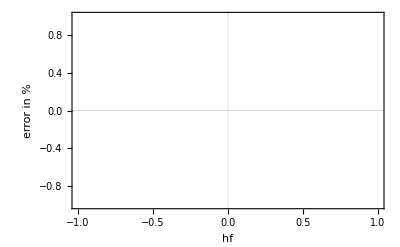

```mathematica
ListPlot[error,PlotTheme->"Scientific",AxesLabel->{HoldForm[hf],HoldForm[error in %]}]
```

```mathematica
hf->0.330(*3% of error*)
```

hf→0.33

## Quark Part

## Fields

```mathematica
Q1L={d1L,-u1L,D1L};
Q2L={d2L,-u2L,D2L};
Q3L={u3L,d3L,U3L};
KK1L={UU1L,DD1L,UUp1L};
KK2L={UU2L,DD2L,UUp2L};
KK3L={DD3L,-UU3L,DDp3L};
KK1R={UU1R,DD1R,UUp1R};
KK2R={UU2R,DD2R,UUp2R};
KK3R={DD3R,-UU3R,DDp3R};
Q1Lbar={d1Lbar,-u1Lbar,D1Lbar};
Q2Lbar={d2Lbar,-u2Lbar,D2Lbar};
Q3Lbar={u3Lbar,d3Lbar,U3Lbar};
KK1Lbar={UU1Lbar,DD1Lbar,UUp1Lbar};
KK2Lbar={UU2Lbar,DD2Lbar,UUp2Lbar};
KK3Lbar={DD3Lbar,-UU3Lbar,DDp3Lbar};
QaL={Q1L,Q2L};
QaLbar={Q1Lbar,Q2Lbar};
KaL={KK1L,KK2L};
KaLbar={KK1Lbar,KK2Lbar};
KaR={KK1R,KK2R};
```

Singlets

```mathematica
dR={d1R,d2R,d3R};
uR={u1R,u2R,u3R};
DR={D1R,D2R};
```

## Yukawas of Quarks

```mathematica
YYd={{Subscript[Yd, 1,1],0,0},{0,Subscript[Yd, 2,2],0}}
YYD=DiagonalMatrix[{Subscript[YD, 1,1],Subscript[YD, 2,2]}]
YYu={0,0,Subscript[Yu, 3]}
yyKK=DiagonalMatrix[{Subscript[yKK, 1,1],Subscript[yKK, 2,2]}]
yyu={{Subscript[yu, 1,1],0,0},{0,Subscript[yu, 2,2],0}}
yyd={0,0,Subscript[yd, 3]}
hhKK=DiagonalMatrix[{Subscript[hKK, 1,1],Subscript[hKK, 2,2]}]
```

{{Yd_(1,1),0,0},{0,Yd_(2,2),0}}

{{YD_(1,1),0},{0,YD_(2,2)}}

{0,0,Yu_3}

{{yKK_(1,1),0},{0,yKK_(2,2)}}

{{yu_(1,1),0,0},{0,yu_(2,2),0}}

{0,0,yd_3}

{{hKK_(1,1),0},{0,hKK_(2,2)}}

## Lagrangian Quark

```mathematica
Lq=ComplexExpand[((YYd[[1]].dR)QaLbar[[1]].η*+(YYd[[2]].dR)QaLbar[[2]].η* + (YYD[[1]].DR)QaLbar[[1]].χ* +(YYD[[2]].DR)QaLbar[[2]].χ*   +(YYu.uR) Q3Lbar.η+YU3 Q3Lbar.χ U3R+TensorContract[TensorProduct[LeviCivitaTensor[3],yyKK[[1]].KaR,QaLbar[[1]],η],{{1,4},{2,5},{3,6}}] + TensorContract[TensorProduct[LeviCivitaTensor[3],yyKK[[2]].KaR,QaLbar[[2]],η],{{1,4},{2,5},{3,6}}] +yKK3  TensorContract[TensorProduct[LeviCivitaTensor[3],KK3R,Q3Lbar,η*],{{1,4},{2,5},{3,6}}]+yyu[[1]].uR KaLbar[[1]].χ+yyu[[2]].uR KaLbar[[2]].χ+yyd.dR KK3Lbar.χ*+(hhKK[[1]].KaR).KaLbar[[1]]φ+(hhKK[[2]].KaR).KaLbar[[2]]φ+hKK3 φ KK3Lbar.KK3R + ConjugateTranspose[(YYd[[1]].dR)QaLbar[[1]].η*+(YYd[[2]].dR)QaLbar[[2]].η* + (YYD[[1]].DR)QaLbar[[1]].χ* +(YYD[[2]].DR)QaLbar[[2]].χ*   +(YYu.uR) Q3Lbar.η+YU3 Q3Lbar.χ U3R+TensorContract[TensorProduct[LeviCivitaTensor[3],yyKK[[1]].KaR,QaLbar[[1]],η],{{1,4},{2,5},{3,6}}] + TensorContract[TensorProduct[LeviCivitaTensor[3],yyKK[[2]].KaR,QaLbar[[2]],η],{{1,4},{2,5},{3,6}}] +yKK3  TensorContract[TensorProduct[LeviCivitaTensor[3],KK3R,Q3Lbar,η*],{{1,4},{2,5},{3,6}}]+yyu[[1]].uR KaLbar[[1]].χ+yyu[[2]].uR KaLbar[[2]].χ+yyd.dR KK3Lbar.χ*+(hhKK[[1]].KaR).KaLbar[[1]]φ+(hhKK[[2]].KaR).KaLbar[[2]]φ+hKK3 φ KK3Lbar.KK3R]
),{η2m,χ2m,η3,χ1,σ,η1},TargetFunctions->Conjugate]/.{Conjugate[χ2m]->χ2p,Conjugate[η2m]->η2p,Conjugate[η3]->η3bar,Conjugate[χ1]->χ1bar};
```

## Mass Matrices

### PM-even fields

#### Up quarks

```mathematica
PMEquLbar={u1Lbar,u2Lbar,u3Lbar,UUp1Lbar,UUp2Lbar};
PMEquL={u1L,u2L,u3L,UUp1L,UUp2L};
PMEquR={u1R,u2R,u3R,UUp1R,UUp2R};
```

```mathematica
MatrixForm[MPMEqu=Coefficient[Lq,Outer[Times,PMEquLbar,PMEquR]]/.subsfeynrulesvevs(*/.vevs/.qyukawas/.qyukawas2/.qyukawas3*)/.zeroFields]
```

(0 | 0 | 0 | (v1 yKK_(1,1))/(√2) | 0
0 | 0 | 0 | 0 | (v1 yKK_(2,2))/(√2)
0 | 0 | (v1 Yu_3)/(√2) | 0 | 0
(v2 yu_(1,1))/(√2) | 0 | 0 | (v4 hKK_(1,1))/(√2) | 0
0 | (v2 yu_(2,2))/(√2) | 0 | 0 | (v4 hKK_(2,2))/(√2))

Yukawa coupling of top quark

```mathematica
Sqrt[(vη^2/2YYu.YYuᵀ)]/172.57/.subsfeynrulesvevs/.vevs/.alphas (*Here i'm assuming that Yu is real*);
```

```mathematica
Solve[1.0079867194291632 √(Subscript[Yu, 3]^2)==1,{Subscript[Yu, 3]}];
```

```mathematica
MPMEquᵀ.MPMEqu//MatrixForm
```

(1/2 v2^2 yu_(1,1)^2 | 0 | 0 | 1/2 v2 v4 hKK_(1,1) yu_(1,1) | 0
0 | 1/2 v2^2 yu_(2,2)^2 | 0 | 0 | 1/2 v2 v4 hKK_(2,2) yu_(2,2)
0 | 0 | 1/2 v1^2 Yu_3^2 | 0 | 0
1/2 v2 v4 hKK_(1,1) yu_(1,1) | 0 | 0 | 1/2 v4^2 hKK_(1,1)^2+1/2 v1^2 yKK_(1,1)^2 | 0
0 | 1/2 v2 v4 hKK_(2,2) yu_(2,2) | 0 | 0 | 1/2 v4^2 hKK_(2,2)^2+1/2 v1^2 yKK_(2,2)^2)

```mathematica
MatrixForm[mu35={{0,0,0,vη Subscript[yKK, 1,1],0},{0,0,0,0,vη Subscript[yKK, 2,2]},{0,0,vη Subscript[Yu, 3],0,0}}];
```

```mathematica
MatrixForm[Mu25={{vχ Subscript[yu, 1,1],0,0,vφ Subscript[hKK, 1,1],0},{0,vχ Subscript[yu, 2,2],0,0,vφ Subscript[hKK, 2,2]}}];
```

```mathematica
MatrixForm[FuLcomp=Series[mu35.Mu25ᵀ.Inverse[(Mu25.Mu25ᵀ)],{vφ,Infinity,2}]//Simplify//Normal]
```

((vη yKK_(1,1))/(vφ hKK_(1,1)) | 0
0 | (vη yKK_(2,2))/(vφ hKK_(2,2))
0 | 0)

FuL = FuLcomp

```mathematica
MatrixForm[FuL=Series[vη/vφ {{Subscript[yKK, 1,1]/Subscript[hKK, 1,1],0},{0,Subscript[yKK, 2,2]/Subscript[hKK, 2,2]},{0,0}},{vφ,Infinity,2}]//Simplify//Normal];
```

```mathematica
MatrixForm[S=Inverse[(Mu25.Mu25ᵀ)]]
```

(1/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2) | 0
0 | 1/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2))

```mathematica
S^2
```

{{1/((vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2),0},{0,1/((vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)}}

```mathematica
MatrixForm[ful3=mu35.(mu35ᵀ.mu35.Mu25ᵀ.S-Mu25ᵀ.S.Mu25.mu35ᵀ.mu35.Mu25ᵀ.S-1/2Mu25ᵀ.(S^2).Mu25.mu35ᵀ.mu35.Mu25ᵀ).S]
```

((vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2) | 0
0 | (vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)
0 | 0)

```mathematica
MatrixForm[ful3ᵀ]/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3
```

(-7.44347×10^-12 | 0 | 0
0 | -5.9523×10^-11 | 0)

```mathematica
MatrixForm[UuL={{1,0,0,FuL[[1,1]]+ful3[[1,1]],FuL[[1,2]]+ful3[[1,2]]},{0,1,0,FuL[[2,1]]+ful3[[2,1]],FuL[[2,2]]+ful3[[2,2]]},{0,0,1,FuL[[3,1]]+ful3[[3,1]],FuL[[3,2]]+ful3[[3,2]]},{-FuL[[1,1]]-ful3[[1,1]],-FuL[[2,1]]-ful3[[2,1]],-FuL[[3,1]]-ful3[[2,1]],1,0},{-FuL[[1,2]]-ful3[[1,2]],-FuL[[2,2]]-ful3[[2,2]],FuL[[3,2]]+ful3[[3,2]],0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3]
```

(1 | 0 | 0 | 0.000246 | 0
0 | 1 | 0 | 0 | 0.000492
0 | 0 | 1 | 0 | 0
-0.000246 | 0 | 0 | 1 | 0
0 | -0.000492 | 0 | 0 | 1)

But the right ones, we have

```mathematica
mu35ᵀ.mu35+Mu25ᵀ.Mu25//MatrixForm
```

(vχ^2 yu_(1,1)^2 | 0 | 0 | vφ vχ hKK_(1,1) yu_(1,1) | 0
0 | vχ^2 yu_(2,2)^2 | 0 | 0 | vφ vχ hKK_(2,2) yu_(2,2)
0 | 0 | vη^2 Yu_3^2 | 0 | 0
vφ vχ hKK_(1,1) yu_(1,1) | 0 | 0 | vφ^2 hKK_(1,1)^2+vη^2 yKK_(1,1)^2 | 0
0 | vφ vχ hKK_(2,2) yu_(2,2) | 0 | 0 | vφ^2 hKK_(2,2)^2+vη^2 yKK_(2,2)^2)

```mathematica
MatrixForm[FuR={{vφ vχ Subscript[hKK, 1,1] Subscript[yu, 1,1],0},{0,vφ vχ Subscript[hKK, 2,2] Subscript[yu, 2,2]},{0,0}}.Inverse[{{vφ^2 Subscript[hKK, 1,1]^2+vη^2 Subscript[yKK, 1,1]^2,0},{0,vφ^2 Subscript[hKK, 2,2]^2+vη^2 Subscript[yKK, 2,2]^2}}ᵀ]//Simplify];
```

```mathematica
MatrixForm[UuR={{1,0,0,FuR[[1,1]],FuR[[1,2]]},{0,1,0,FuR[[2,1]],FuR[[2,2]]},{0,0,1,FuR[[3,1]],FuR[[3,2]]},{-FuR[[1,1]],-FuR[[2,1]],-FuR[[3,1]],1,0},{-FuR[[1,2]],-FuR[[2,2]],-FuR[[3,2]],0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3]
```

(1 | 0 | 0 | -0.0000155219 | 0
0 | 1 | 0 | 0 | -0.00912627
0 | 0 | 1 | 0 | 0
0.0000155219 | 0 | 0 | 1 | 0
0 | 0.00912627 | 0 | 0 | 1)

The exact solution is

```mathematica
(*Eigensystem[MPMEqu.MPMEquᵀ]*)
```

```mathematica
UMPMEUL={{-0.0002459999924972639+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.9999999697420013+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.0004919589657393952+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.9999998789881807+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-0.9999998789881807+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.0004919589657393952+0. ⅈ},{0.9999999697420013+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.0002459999924972639+0. ⅈ,0.+0. ⅈ}}ᵀ;
```

```mathematica
Eigensystem[MPMEquᵀ.MPMEqu]
```

Eigensystem[Transpose[{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3/.zeroFields].({{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3/.zeroFields)]

```mathematica
UMPMEUR={{0.000015521855231197214+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.999999999879536+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-0.009125894301983864+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.999958358159573+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.999958358159573+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.009125894301983864+0. ⅈ},{-0.999999999879536+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.000015521855231197214+0. ⅈ,0.+0. ⅈ}}ᵀ;
```

```mathematica
UMPMEUL-UuL//MatrixForm
```

((-0.000246+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) | (0.+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) | (0.+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) | (0.+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) | (1.+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)
(0.+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) | (0.000491959+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) | (0.+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) | (-1.+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) | (0.+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)
(0.+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) | (0.+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) | (1.+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) | (0.+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) | (0.+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)
(-1.+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) | (0.+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) | (0.+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) | (0.+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) | (-0.000246+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)
(0.+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) | (1.+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) | (0.+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) | (0.000491959+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) | (0.+0. ⅈ)-({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3))

```mathematica
UPMASSEXACT=UMPMEULᵀ.MPMEqu.UMPMEUR//MatrixForm
```

{{-0.000246+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.000491959+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.000491959+0. ⅈ},{1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.000246+0. ⅈ,0.+0. ⅈ}}.({{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3/.zeroFields).{{0.0000155219+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.+0. ⅈ},{0.+0. ⅈ,-0.00912589+0. ⅈ,0.+0. ⅈ,0.999958+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.0000155219+0. ⅈ},{0.+0. ⅈ,0.999958+0. ⅈ,0.+0. ⅈ,0.00912589+0. ⅈ,0.+0. ⅈ}}

```mathematica
MatrixForm[Upmass=Series[UuLᵀ.MPMEqu.UuR/.subsfeynrulesvevs/.vevs/.qyukawas3/.qyukawas2/.qyukawas//Simplify,{vφ,Infinity,2}]//Normal]
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {vevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {qyukawas3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

D::ivar: 0 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

(Transpose[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3/.zeroFields).({{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)/.subsfeynrulesvevs/.vevs/.qyukawas3/.qyukawas2/.qyukawas)+1/vφ^2 ReplaceAll^(1,0)[Transpose[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3/.zeroFields).({{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3),subsfeynrulesvevs] ReplaceAll^(1,0)[Transpose[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3/.zeroFields).({{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)/.subsfeynrulesvevs,vevs] ReplaceAll^(1,0)[Transpose[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3/.zeroFields).({{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)/.subsfeynrulesvevs/.vevs,qyukawas3] ReplaceAll^(1,0)[Transpose[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3/.zeroFields).({{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)/.subsfeynrulesvevs/.vevs/.qyukawas3,qyukawas2] ReplaceAll^(1,0)[Transpose[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3/.zeroFields).({{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)/.subsfeynrulesvevs/.vevs/.qyukawas3/.qyukawas2,qyukawas] (Transpose[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3/.zeroFields).1 ((vχ^2 ∂_{0,2} ({{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs) yu_(1,1)^2)/(hKK_(1,1)^2)-(vχ^2 ∂_(0,0) ({{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs) yu_(1,1)^2)/(hKK_(1,1)^2)+(vχ^2 ∂_{0,2} ({{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs) yu_(2,2)^2)/(hKK_(2,2)^2)-(vχ^2 ∂_(0,0) ({{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs) yu_(2,2)^2)/(hKK_(2,2)^2)) ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs,vevs] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs/.vevs,qyukawas] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas,qyukawas2] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2,qyukawas3]+1.({{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3/.zeroFields).({{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) ((vη^2 ∂_{0,2} ({{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs) yKK_(1,1)^2)/(hKK_(1,1)^2)-(vη^2 ∂_(0,0) ({{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs) yKK_(1,1)^2)/(hKK_(1,1)^2)+(vη^2 ∂_{0,2} ({{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs) yKK_(2,2)^2)/(hKK_(2,2)^2)-(vη^2 ∂_(0,0) ({{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs) yKK_(2,2)^2)/(hKK_(2,2)^2)) Transpose'[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs,vevs] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs/.vevs,qyukawas] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas,qyukawas2] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2,qyukawas3])

```mathematica
upquarkmass={2.16*10^-3,1.27,172.57};
downquarkmass={4.7*10^-3,93.5*10^-3,4.183};
```

```mathematica
upquarkmass[[1]]
```

0.00216

```mathematica
Solve[Upmass[[1,1]]==upquarkmass[[1]]&&Upmass[[2,2]]==upquarkmass[[2]]&&Upmass[[3,3]]==upquarkmass[[3]](*/.qyukawas*)/.subsfeynrulesvevs/.vevs/.alphas,{Subscript[yu, 1,1],Subscript[yu, 2,2]}]
```

D::ivar: 0 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[1/1000000000000 ReplaceAll^(1,0)[{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{hKK3→0.3,yKK3→0.9}] ReplaceAll^(1,0)[{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{246→246,10000→10000,1000000→1000000,1000000→1000000}] ReplaceAll^(1,0)[{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{10000→10000,1000000→1000000,1000000→1000000,246→246,√(v1^2+v2^2+v3^2+v4^2)→√(v1^2+v2^2+v3^2+v4^2)}] ReplaceAll^(1,0)[{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{Yd_(1,1)→0.0000270195,Yd_(2,2)→0.000537516,Yu_3→0.992077,yd_3→0.801579,yu_(1,1)→-0.00124175,yu_(2,2)→-0.365051}] ReplaceAll^(1,0)[{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{YD_(1,1)→0.6,YD_(2,2)→0.5,YU3→0.8,y^KK3→0.9,h^KK3→0.3,yKK_(1,1)→0.8,yKK_(2,2)→0.8,hKK_(1,1)→0.8,hKK_(2,2)→0.4}] ({{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}.1 ((100000000 ∂_{0,2} {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yu_(1,1)^2)/(hKK_(1,1)^2)-(100000000 ∂_(0,0) {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yu_(1,1)^2)/(hKK_(1,1)^2)+(100000000 ∂_{0,2} {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yu_(2,2)^2)/(hKK_(2,2)^2)-(100000000 ∂_(0,0) {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yu_(2,2)^2)/(hKK_(2,2)^2)) ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{hKK3→0.3,yKK3→0.9}] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{246→246,10000→10000,1000000→1000000,1000000→1000000}] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{Yd_(1,1)→0.0000270195,Yd_(2,2)→0.000537516,Yu_3→0.992077,yd_3→0.801579,yu_(1,1)→-0.00124175,yu_(2,2)→-0.365051}] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{YD_(1,1)→0.6,YD_(2,2)→0.5,YU3→0.8,y^KK3→0.9,h^KK3→0.3,yKK_(1,1)→0.8,yKK_(2,2)→0.8,hKK_(1,1)→0.8,hKK_(2,2)→0.4}]+1.{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} ((60516 ∂_{0,2} {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yKK_(1,1)^2)/(hKK_(1,1)^2)-(60516 ∂_(0,0) {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yKK_(1,1)^2)/(hKK_(1,1)^2)+(60516 ∂_{0,2} {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yKK_(2,2)^2)/(hKK_(2,2)^2)-(60516 ∂_(0,0) {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yKK_(2,2)^2)/(hKK_(2,2)^2)) Transpose'[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{hKK3→0.3,yKK3→0.9}] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{246→246,10000→10000,1000000→1000000,1000000→1000000}] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{Yd_(1,1)→0.0000270195,Yd_(2,2)→0.000537516,Yu_3→0.992077,yd_3→0.801579,yu_(1,1)→-0.00124175,yu_(2,2)→-0.365051}] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{YD_(1,1)→0.6,YD_(2,2)→0.5,YU3→0.8,y^KK3→0.9,h^KK3→0.3,yKK_(1,1)→0.8,yKK_(2,2)→0.8,hKK_(1,1)→0.8,hKK_(2,2)→0.4}])==0.00216&&1/1000000000000 ReplaceAll^(1,0)[{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{hKK3→0.3,yKK3→0.9}] ReplaceAll^(1,0)[{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{246→246,10000→10000,1000000→1000000,1000000→1000000}] ReplaceAll^(1,0)[{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{10000→10000,1000000→1000000,1000000→1000000,246→246,√(v1^2+v2^2+v3^2+v4^2)→√(v1^2+v2^2+v3^2+v4^2)}] ReplaceAll^(1,0)[{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{Yd_(1,1)→0.0000270195,Yd_(2,2)→0.000537516,Yu_3→0.992077,yd_3→0.801579,yu_(1,1)→-0.00124175,yu_(2,2)→-0.365051}] ReplaceAll^(1,0)[{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{YD_(1,1)→0.6,YD_(2,2)→0.5,YU3→0.8,y^KK3→0.9,h^KK3→0.3,yKK_(1,1)→0.8,yKK_(2,2)→0.8,hKK_(1,1)→0.8,hKK_(2,2)→0.4}] ({{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}.1 ((100000000 ∂_{0,2} {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yu_(1,1)^2)/(hKK_(1,1)^2)-(100000000 ∂_(0,0) {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yu_(1,1)^2)/(hKK_(1,1)^2)+(100000000 ∂_{0,2} {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yu_(2,2)^2)/(hKK_(2,2)^2)-(100000000 ∂_(0,0) {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yu_(2,2)^2)/(hKK_(2,2)^2)) ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{hKK3→0.3,yKK3→0.9}] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{246→246,10000→10000,1000000→1000000,1000000→1000000}] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{Yd_(1,1)→0.0000270195,Yd_(2,2)→0.000537516,Yu_3→0.992077,yd_3→0.801579,yu_(1,1)→-0.00124175,yu_(2,2)→-0.365051}] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{YD_(1,1)→0.6,YD_(2,2)→0.5,YU3→0.8,y^KK3→0.9,h^KK3→0.3,yKK_(1,1)→0.8,yKK_(2,2)→0.8,hKK_(1,1)→0.8,hKK_(2,2)→0.4}]+1.{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} ((60516 ∂_{0,2} {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yKK_(1,1)^2)/(hKK_(1,1)^2)-(60516 ∂_(0,0) {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yKK_(1,1)^2)/(hKK_(1,1)^2)+(60516 ∂_{0,2} {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yKK_(2,2)^2)/(hKK_(2,2)^2)-(60516 ∂_(0,0) {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yKK_(2,2)^2)/(hKK_(2,2)^2)) Transpose'[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{hKK3→0.3,yKK3→0.9}] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{246→246,10000→10000,1000000→1000000,1000000→1000000}] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{Yd_(1,1)→0.0000270195,Yd_(2,2)→0.000537516,Yu_3→0.992077,yd_3→0.801579,yu_(1,1)→-0.00124175,yu_(2,2)→-0.365051}] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{YD_(1,1)→0.6,YD_(2,2)→0.5,YU3→0.8,y^KK3→0.9,h^KK3→0.3,yKK_(1,1)→0.8,yKK_(2,2)→0.8,hKK_(1,1)→0.8,hKK_(2,2)→0.4}])==1.27&&1/1000000000000 ReplaceAll^(1,0)[{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{hKK3→0.3,yKK3→0.9}] ReplaceAll^(1,0)[{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{246→246,10000→10000,1000000→1000000,1000000→1000000}] ReplaceAll^(1,0)[{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{10000→10000,1000000→1000000,1000000→1000000,246→246,√(v1^2+v2^2+v3^2+v4^2)→√(v1^2+v2^2+v3^2+v4^2)}] ReplaceAll^(1,0)[{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{Yd_(1,1)→0.0000270195,Yd_(2,2)→0.000537516,Yu_3→0.992077,yd_3→0.801579,yu_(1,1)→-0.00124175,yu_(2,2)→-0.365051}] ReplaceAll^(1,0)[{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{YD_(1,1)→0.6,YD_(2,2)→0.5,YU3→0.8,y^KK3→0.9,h^KK3→0.3,yKK_(1,1)→0.8,yKK_(2,2)→0.8,hKK_(1,1)→0.8,hKK_(2,2)→0.4}] ({{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}.1 ((100000000 ∂_{0,2} {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yu_(1,1)^2)/(hKK_(1,1)^2)-(100000000 ∂_(0,0) {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yu_(1,1)^2)/(hKK_(1,1)^2)+(100000000 ∂_{0,2} {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yu_(2,2)^2)/(hKK_(2,2)^2)-(100000000 ∂_(0,0) {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yu_(2,2)^2)/(hKK_(2,2)^2)) ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{hKK3→0.3,yKK3→0.9}] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{246→246,10000→10000,1000000→1000000,1000000→1000000}] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{Yd_(1,1)→0.0000270195,Yd_(2,2)→0.000537516,Yu_3→0.992077,yd_3→0.801579,yu_(1,1)→-0.00124175,yu_(2,2)→-0.365051}] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{YD_(1,1)→0.6,YD_(2,2)→0.5,YU3→0.8,y^KK3→0.9,h^KK3→0.3,yKK_(1,1)→0.8,yKK_(2,2)→0.8,hKK_(1,1)→0.8,hKK_(2,2)→0.4}]+1.{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} ((60516 ∂_{0,2} {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yKK_(1,1)^2)/(hKK_(1,1)^2)-(60516 ∂_(0,0) {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yKK_(1,1)^2)/(hKK_(1,1)^2)+(60516 ∂_{0,2} {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yKK_(2,2)^2)/(hKK_(2,2)^2)-(60516 ∂_(0,0) {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}} yKK_(2,2)^2)/(hKK_(2,2)^2)) Transpose'[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{hKK3→0.3,yKK3→0.9}] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{246→246,10000→10000,1000000→1000000,1000000→1000000}] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{Yd_(1,1)→0.0000270195,Yd_(2,2)→0.000537516,Yu_3→0.992077,yd_3→0.801579,yu_(1,1)→-0.00124175,yu_(2,2)→-0.365051}] ReplaceAll^(1,0)[{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}},{YD_(1,1)→0.6,YD_(2,2)→0.5,YU3→0.8,y^KK3→0.9,h^KK3→0.3,yKK_(1,1)→0.8,yKK_(2,2)→0.8,hKK_(1,1)→0.8,hKK_(2,2)→0.4}])==172.57,{yu_(1,1),yu_(2,2)}]

#### Down quarks

```mathematica
PMEqdLbar={d1Lbar,d2Lbar,d3Lbar,DDp3Lbar};
PMEqdL={d1L,d2L,d3L,DDp3L};
PMEqdR={d1R,d2R,d3R,DDp3R};
```

```mathematica
MatrixForm[MPMEqd=Coefficient[Lq,Outer[Times,PMEqdLbar,PMEqdR]]/.zeroFields/.subsfeynrulesvevs/.vevs(*/.qyukawas/.qyukawas2/.qyukawas3*)]
```

(0.0047 | 0 | 0 | 0
0 | 0.0935 | 0 | 0
0 | 0 | 0 | -156.553
0 | 0 | 5668.02 | 212132.)

```mathematica
MatrixForm[MPMEqd.MPMEqdᵀ];
```

```mathematica
FdL=-1/2 hKK3 vη vφ yKK3 ((hKK3^2 vφ^2)/2+1/2 vχ^2 Subscript[yd, 3]^2)^-1;
```

```mathematica
MatrixForm[UdL={{1,0,0,0},{0,1,0,0},{0,0,1,FdL},{0,0,-FdL,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3] (*Left matrix that rotates MPMEqd.MPMEqdᵀ *)
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {vevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {qyukawas} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{{1,0,0,0},{0,1,0,0},{0,0,1,-(hKK3 vη vφ yKK3)/(2 ((hKK3^2 vφ^2)/2+1/2 vχ^2 yd_3^2))},{0,0,(hKK3 vη vφ yKK3)/(2 ((hKK3^2 vφ^2)/2+1/2 vχ^2 yd_3^2)),1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3

```mathematica
MatrixForm[Series[UdLᵀ.MPMEqd.MPMEqdᵀ.UdL,{vφ,Infinity,2}]//Normal//Simplify];
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

D::ivar: 0 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

```mathematica
MatrixForm[MPMEqdᵀ.MPMEqd];
```

```mathematica
FdR=1/2 hKK3 vφ vχ Subscript[yd, 3]((hKK3^2 vφ^2)/2+(vη^2 yKK3^2)/2)^-1;
MatrixForm[UdR={{1,0,0,0},{0,1,0,0},{0,0,1,FdR},{0,0,-FdR,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3](*Right matrix that rotates MPMEqd.MPMEqdᵀ *)
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {vevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {qyukawas} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{{1,0,0,0},{0,1,0,0},{0,0,1,(hKK3 vφ vχ yd_3)/(2 ((hKK3^2 vφ^2)/2+(vη^2 yKK3^2)/2))},{0,0,-(hKK3 vφ vχ yd_3)/(2 ((hKK3^2 vφ^2)/2+(vη^2 yKK3^2)/2)),1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3

```mathematica
MatrixForm[Series[UdRᵀ.MPMEqdᵀ.MPMEqd.UdR,{vφ,Infinity,2}]//Normal//Simplify];
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

D::ivar: 0 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

```mathematica
MatrixForm[Downmass=Series[UdLᵀ.MPMEqd.UdR/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3,{vφ,Infinity,2}]//Normal//Simplify]
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {vevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {qyukawas} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

(Transpose[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,hKK3 φ}}/.zeroFields/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3).({{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)+1/(hKK3^2 vφ^2)(∂_{0,2} ({{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs)-∂_(0,0) ({{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs)) (vχ^2 Transpose[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,hKK3 φ}}/.zeroFields/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3).1 yd_3^2+vη^2 yKK3^2 1.({{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,hKK3 φ}}/.zeroFields/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3).({{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) Transpose'[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3]) ReplaceAll^(1,0)[Transpose[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,hKK3 φ}}/.zeroFields/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3).({{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3),subsfeynrulesvevs] ReplaceAll^(1,0)[Transpose[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,hKK3 φ}}/.zeroFields/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3).({{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)/.subsfeynrulesvevs,vevs] ReplaceAll^(1,0)[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs,vevs] ReplaceAll^(1,0)[Transpose[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,hKK3 φ}}/.zeroFields/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3).({{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)/.subsfeynrulesvevs/.vevs,qyukawas] ReplaceAll^(1,0)[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs,qyukawas] ReplaceAll^(1,0)[Transpose[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,hKK3 φ}}/.zeroFields/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3).({{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)/.subsfeynrulesvevs/.vevs/.qyukawas,qyukawas2] ReplaceAll^(1,0)[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas,qyukawas2] ReplaceAll^(1,0)[Transpose[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,hKK3 φ}}/.zeroFields/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3).({{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2,qyukawas3] ReplaceAll^(1,0)[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2,qyukawas3]

```mathematica
Solve[Downmass[[1,1]]==downquarkmass[[1]]&&Downmass[[2,2]]==downquarkmass[[2]]&&Downmass[[3,3]]==downquarkmass[[3]]/.qyukawas/.subsfeynrulesvevs/.vevs/.alphas,{Subscript[Yd, 1,1],Subscript[Yd, 2,2],Subscript[yd, 3]}];
```

Part::partw: Part 3 of (Transpose[«1»].ReplaceAll[«2»].ReplaceAll[«2»]/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)+((∂_{0,2} ({{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs)-∂_(0,0) ({{«4»},{«4»},{«4»},{«4»}}/.subsfeynrulesvevs)) «7» «3»)/(hKK3^2 vφ^2) does not exist.

ReplaceAll::reps: {qyukawas} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {vevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Solve::naqs: (ReplaceAll[«2»]/.qyukawas2)==0.0047&&1/vφ^2==0.0935&&Plus[«2»]⟦3,3⟧==4.183/.qyukawas/.subsfeynrulesvevs/.vevs/.alphas is not a quantified system of equations and inequalities.

```mathematica
fyd[hKK3_,yKK3_]:=(2.4047379395962025 hKK3)/yKK3;
```

```mathematica
Plot3D[{fyd[hKK3,yKK3]},{hKK3,0.1,1.1},{yKK3,0.3,1.2}]
```

-Graphics3D-

```mathematica
MatrixForm[Downmass/.qyukawas/.subsfeynrulesvevs/.vevs/.alphas/.qyukawas2]
```

ReplaceAll::reps: {zeroFields} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {vevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

(Transpose[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,hKK3 φ}}/.zeroFields/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3).({{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)+1/(hKK3^2 vφ^2)(∂_{0,2} ({{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs)-∂_(0,0) ({{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs)) (vχ^2 Transpose[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,hKK3 φ}}/.zeroFields/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3).1 yd_3^2+vη^2 yKK3^2 1.({{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,hKK3 φ}}/.zeroFields/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3).({{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3) Transpose'[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3]) ReplaceAll^(1,0)[Transpose[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,hKK3 φ}}/.zeroFields/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3).({{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3),subsfeynrulesvevs] ReplaceAll^(1,0)[Transpose[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,hKK3 φ}}/.zeroFields/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3).({{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)/.subsfeynrulesvevs,vevs] ReplaceAll^(1,0)[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs,vevs] ReplaceAll^(1,0)[Transpose[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,hKK3 φ}}/.zeroFields/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3).({{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)/.subsfeynrulesvevs/.vevs,qyukawas] ReplaceAll^(1,0)[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs,qyukawas] ReplaceAll^(1,0)[Transpose[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,hKK3 φ}}/.zeroFields/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3).({{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)/.subsfeynrulesvevs/.vevs/.qyukawas,qyukawas2] ReplaceAll^(1,0)[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas,qyukawas2] ReplaceAll^(1,0)[Transpose[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,hKK3 φ}}/.zeroFields/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3).({{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2,qyukawas3] ReplaceAll^(1,0)[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2,qyukawas3]/.qyukawas/.subsfeynrulesvevs/.vevs/.alphas/.qyukawas2

### CKM

```mathematica
UuL//MatrixForm
```

{{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3

```mathematica
UdL//MatrixForm
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {vevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {qyukawas} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{{1,0,0,0},{0,1,0,0},{0,0,1,-(hKK3 vη vφ yKK3)/(2 ((hKK3^2 vφ^2)/2+1/2 vχ^2 yd_3^2))},{0,0,(hKK3 vη vφ yKK3)/(2 ((hKK3^2 vφ^2)/2+1/2 vχ^2 yd_3^2)),1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3

```mathematica
MatrixForm[UdLᵀ.{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,0,0}}.UuL]
```

Transpose[{{1,0,0,0},{0,1,0,0},{0,0,1,-(hKK3 vη vφ yKK3)/(2 ((hKK3^2 vφ^2)/2+1/2 vχ^2 yd_3^2))},{0,0,(hKK3 vη vφ yKK3)/(2 ((hKK3^2 vφ^2)/2+1/2 vχ^2 yd_3^2)),1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,0,0}}.({{1,0,0,(vη yKK_(1,1))/(vφ hKK_(1,1))+(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0},{0,1,0,0,(vη yKK_(2,2))/(vφ hKK_(2,2))+(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)},{0,0,1,0,0},{-(vη yKK_(1,1))/(vφ hKK_(1,1))-(vη yKK_(1,1) (-(3 vη^2 vφ^3 hKK_(1,1)^3 yKK_(1,1)^2)/(2 (vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)^2)+(vη^2 vφ hKK_(1,1) yKK_(1,1)^2)/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2)))/(vφ^2 hKK_(1,1)^2+vχ^2 yu_(1,1)^2),0,0,1,0},{0,-(vη yKK_(2,2))/(vφ hKK_(2,2))-(vη yKK_(2,2) (-(3 vη^2 vφ^3 hKK_(2,2)^3 yKK_(2,2)^2)/(2 (vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)^2)+(vη^2 vφ hKK_(2,2) yKK_(2,2)^2)/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2)))/(vφ^2 hKK_(2,2)^2+vχ^2 yu_(2,2)^2),0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)

### PM-odd fields

#### Up quarks

```mathematica
PMOquLbar={U3Lbar,UU3Lbar,UU1Lbar,UU2Lbar};
PMOquL={U3L,UU3L,UU1L,UU2L};
PMOquR={U3R,UU3R,UU1R,UU2R};
```

```mathematica
MatrixForm[MPMOqu=Coefficient[Lq,Outer[Times,PMOquLbar,PMOquR]]/.zeroFields(*/.subsfeynrulesvevs/.vevs/.qyukawas3/.qyukawas2*)]
```

ReplaceAll::reps: {zeroFields} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{{0,0,0,0},{0,hKK3 φ,0,0},{0,0,0,0},{0,0,0,0}}/.zeroFields

```mathematica
A1=(vχ YU3)/(√2);
B1=-(vη yKK3)/(√2);
C1=(hKK3 vφ)/(√2);
```

```mathematica
DiagonalizableMatrixQ[MPMOqu]
```

False

```mathematica
Eigensystem[MPMOqu.MPMOquᵀ]//Simplify
```

Eigensystem[({{0,0,0,0},{0,hKK3 φ,0,0},{0,0,0,0},{0,0,0,0}}/.zeroFields).Transpose[{{0,0,0,0},{0,hKK3 φ,0,0},{0,0,0,0},{0,0,0,0}}/.zeroFields]]

```mathematica
Normalize[{(hKK3^2 vφ^2-vη^2 yKK3^2-vχ^2 YU3^2+√(hKK3^4 vφ^4+2 hKK3^2 vφ^2 (vη^2 yKK3^2-vχ^2 YU3^2)+(vη^2 yKK3^2+vχ^2 YU3^2)^2))/(2 hKK3 vη vφ yKK3),1,0,0}]/.Abs->Identity/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3//Simplify
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {vevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {qyukawas} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{(hKK3^2 vφ^2-vη^2 yKK3^2-vχ^2 YU3^2+√(hKK3^4 vφ^4+2 hKK3^2 vφ^2 (vη^2 yKK3^2-vχ^2 YU3^2)+(vη^2 yKK3^2+vχ^2 YU3^2)^2))/(2 hKK3 vη vφ yKK3 √(1+((hKK3^2 vφ^2-vη^2 yKK3^2-vχ^2 YU3^2+√(hKK3^4 vφ^4+2 hKK3^2 vφ^2 (vη^2 yKK3^2-vχ^2 YU3^2)+(vη^2 yKK3^2+vχ^2 YU3^2)^2))^2)/(4 hKK3^2 vη^2 vφ^2 yKK3^2))),1/(√(1+((hKK3^2 vφ^2-vη^2 yKK3^2-vχ^2 YU3^2+√(hKK3^4 vφ^4+2 hKK3^2 vφ^2 (vη^2 yKK3^2-vχ^2 YU3^2)+(vη^2 yKK3^2+vχ^2 YU3^2)^2))^2)/(4 hKK3^2 vη^2 vφ^2 yKK3^2))),0,0}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3

```mathematica
Normalize[{-((-hKK3^2 vφ^2+vη^2 yKK3^2+vχ^2 YU3^2+√(hKK3^4 vφ^4+2 hKK3^2 vφ^2 (vη^2 yKK3^2-vχ^2 YU3^2)+(vη^2 yKK3^2+vχ^2 YU3^2)^2))/(2 hKK3 vη vφ yKK3)),1,0,0}]/.Abs->Identity/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3//Simplify
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {vevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {qyukawas} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{-(-hKK3^2 vφ^2+vη^2 yKK3^2+vχ^2 YU3^2+√(hKK3^4 vφ^4+2 hKK3^2 vφ^2 (vη^2 yKK3^2-vχ^2 YU3^2)+(vη^2 yKK3^2+vχ^2 YU3^2)^2))/(2 hKK3 vη vφ yKK3 √(1+((-hKK3^2 vφ^2+vη^2 yKK3^2+vχ^2 YU3^2+√(hKK3^4 vφ^4+2 hKK3^2 vφ^2 (vη^2 yKK3^2-vχ^2 YU3^2)+(vη^2 yKK3^2+vχ^2 YU3^2)^2))^2)/(4 hKK3^2 vη^2 vφ^2 yKK3^2))),1/(√(1+((-hKK3^2 vφ^2+vη^2 yKK3^2+vχ^2 YU3^2+√(hKK3^4 vφ^4+2 hKK3^2 vφ^2 (vη^2 yKK3^2-vχ^2 YU3^2)+(vη^2 yKK3^2+vχ^2 YU3^2)^2))^2)/(4 hKK3^2 vη^2 vφ^2 yKK3^2))),0,0}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3

```mathematica
MatrixForm[UuoddL={{0.9999997272903958,0.0007385249717673331,0,0},{-0.0007385249717809021,0.9999997272903958,0,0},{0,0,1,0},{0,0,0,1}}ᵀ]
```

(1. | -0.000738525 | 0 | 0
0.000738525 | 1. | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Eigensystem[MPMOquᵀ.MPMOqu]//Simplify
```

Eigensystem[Transpose[{{0,0,0,0},{0,hKK3 φ,0,0},{0,0,0,0},{0,0,0,0}}/.zeroFields].({{0,0,0,0},{0,hKK3 φ,0,0},{0,0,0,0},{0,0,0,0}}/.zeroFields)]

```mathematica
{{1/(2 vη vχ yKK3 YU3)(hKK3^2 vφ^2+vη^2 yKK3^2-vχ^2 YU3^2+√(hKK3^4 vφ^4+2 hKK3^2 vφ^2 (vη^2 yKK3^2-vχ^2 YU3^2)+(vη^2 yKK3^2+vχ^2 YU3^2)^2)),1,0,0},{1/(2 vη vχ yKK3 YU3)(hKK3^2 vφ^2+vη^2 yKK3^2-vχ^2 YU3^2-√(hKK3^4 vφ^4+2 hKK3^2 vφ^2 (vη^2 yKK3^2-vχ^2 YU3^2)+(vη^2 yKK3^2+vχ^2 YU3^2)^2)),1,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
Normalize[{1/(2 vη vχ yKK3 YU3)(hKK3^2 vφ^2+vη^2 yKK3^2-vχ^2 YU3^2+√(hKK3^4 vφ^4+2 hKK3^2 vφ^2 (vη^2 yKK3^2-vχ^2 YU3^2)+(vη^2 yKK3^2+vχ^2 YU3^2)^2)),1,0,0}]/.Abs->Identity/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3//Simplify
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {vevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {qyukawas} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{(hKK3^2 vφ^2+vη^2 yKK3^2-vχ^2 YU3^2+√(hKK3^4 vφ^4+2 hKK3^2 vφ^2 (vη^2 yKK3^2-vχ^2 YU3^2)+(vη^2 yKK3^2+vχ^2 YU3^2)^2))/(2 vη vχ yKK3 YU3 √(1+((hKK3^2 vφ^2+vη^2 yKK3^2-vχ^2 YU3^2+√(hKK3^4 vφ^4+2 hKK3^2 vφ^2 (vη^2 yKK3^2-vχ^2 YU3^2)+(vη^2 yKK3^2+vχ^2 YU3^2)^2))^2)/(4 vη^2 vχ^2 yKK3^2 YU3^2))),1/(√(1+((hKK3^2 vφ^2+vη^2 yKK3^2-vχ^2 YU3^2+√(hKK3^4 vφ^4+2 hKK3^2 vφ^2 (vη^2 yKK3^2-vχ^2 YU3^2)+(vη^2 yKK3^2+vχ^2 YU3^2)^2))^2)/(4 vη^2 vχ^2 yKK3^2 YU3^2))),0,0}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3

```mathematica
Normalize[{1/(2 vη vχ yKK3 YU3)(hKK3^2 vφ^2+vη^2 yKK3^2-vχ^2 YU3^2-√(hKK3^4 vφ^4+2 hKK3^2 vφ^2 (vη^2 yKK3^2-vχ^2 YU3^2)+(vη^2 yKK3^2+vχ^2 YU3^2)^2)),1,0,0}]/.Abs->Identity/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3//Simplify
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {vevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {qyukawas} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{(hKK3^2 vφ^2+vη^2 yKK3^2-vχ^2 YU3^2-√(hKK3^4 vφ^4+2 hKK3^2 vφ^2 (vη^2 yKK3^2-vχ^2 YU3^2)+(vη^2 yKK3^2+vχ^2 YU3^2)^2))/(2 vη vχ yKK3 YU3 √(1+((-hKK3^2 vφ^2-vη^2 yKK3^2+vχ^2 YU3^2+√(hKK3^4 vφ^4+2 hKK3^2 vφ^2 (vη^2 yKK3^2-vχ^2 YU3^2)+(vη^2 yKK3^2+vχ^2 YU3^2)^2))^2)/(4 vη^2 vχ^2 yKK3^2 YU3^2))),1/(√(1+((-hKK3^2 vφ^2-vη^2 yKK3^2+vχ^2 YU3^2+√(hKK3^4 vφ^4+2 hKK3^2 vφ^2 (vη^2 yKK3^2-vχ^2 YU3^2)+(vη^2 yKK3^2+vχ^2 YU3^2)^2))^2)/(4 vη^2 vχ^2 yKK3^2 YU3^2))),0,0}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3

```mathematica
MatrixForm[UuoddR={{0.9999999998060732,0.00001969399388020533,0,0},{-0.00001969399059847595,0.9999999998060733,0,0},{0,0,1,0},{0,0,0,1}}ᵀ]
```

(1. | -0.000019694 | 0 | 0
0.000019694 | 1. | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
UuoddLᵀ.MPMOqu.UuoddR/.subsfeynrulesvevs/.vevs/.qyukawas2/.qyukawas/.qyukawas3//MatrixForm
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {vevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {qyukawas2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{{1.,0.000738525,0,0},{-0.000738525,1.,0,0},{0,0,1,0},{0,0,0,1}}.({{0,0,0,0},{0,hKK3 φ,0,0},{0,0,0,0},{0,0,0,0}}/.zeroFields).{{1.,-0.000019694,0,0},{0.000019694,1.,0,0},{0,0,1,0},{0,0,0,1}}/.subsfeynrulesvevs/.vevs/.qyukawas2/.qyukawas/.qyukawas3

#### Down quarks

```mathematica
PMOqdLbar={D1Lbar,D2Lbar,DD1Lbar,DD2Lbar,DD3Lbar};
PMOqdL={D1L,D2L,DD1L,DD2L,DD3L};
PMOqdR={D1R,D2R,DD1R,DD2R,DD3R};
```

```mathematica
MatrixForm[MPMOqd=Coefficient[Lq,Outer[Times,PMOqdLbar,PMOqdR]]/.zeroFields]
```

ReplaceAll::reps: {zeroFields} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,hKK3 φ}}/.zeroFields

```mathematica
(*MatrixForm[MPMOqd.MPMOqdᵀ/.qyukawas/.qyukawas2];*)
```

```mathematica
(*Eigensystem[MPMOqd.MPMOqdᵀ/.qyukawas/.qyukawas2/.qyukawas3/.subsfeynrulesvevs/.vevs]*)
```

```mathematica
MatrixForm[UdoddL={{0.,-0.9999998789301906,0.,0.0004920768274193234,0.},{0.9999999697385971,0.,-0.0002460138308328416,0.,0.},{0.,0.,0.,0.,1.},{0.,0.0004920768274193233,0.,0.9999998789301906,0.},{-0.00024601383083284166,0.,-0.9999999697385971,0.,0.}}ᵀ/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3//Chop//Simplify];
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {vevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {qyukawas} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Det[UdoddL]
```

Det[{{0,1.,0,0,-0.000246014},{-1.,0,0,0.000492077,0},{0,-0.000246014,0,0,-1.},{0.000492077,0,0,1.,0},{0,0,1.,0,0}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3]

```mathematica
MatrixForm[UdoddLᵀ.MPMOqd.MPMOqdᵀ.UdoddL/.qyukawas/.qyukawas2/.qyukawas3/.subsfeynrulesvevs/.vevs//Simplify]
```

ReplaceAll::reps: {qyukawas} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {qyukawas2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {qyukawas3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Transpose[{{0,1.,0,0,-0.000246014},{-1.,0,0,0.000492077,0},{0,-0.000246014,0,0,-1.},{0.000492077,0,0,1.,0},{0,0,1.,0,0}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,hKK3 φ}}/.zeroFields).Transpose[{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,hKK3 φ}}/.zeroFields].({{0,1.,0,0,-0.000246014},{-1.,0,0,0.000492077,0},{0,-0.000246014,0,0,-1.},{0.000492077,0,0,1.,0},{0,0,1.,0,0}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)/.qyukawas/.qyukawas2/.qyukawas3/.subsfeynrulesvevs/.vevs

```mathematica
(*Eigensystem[MPMOqdᵀ.MPMOqd/.qyukawas/.qyukawas2/.qyukawas3/.subsfeynrulesvevs/.vevs];*)
```

```mathematica
MatrixForm[UdoddR={{0.,-0.9999999999810827,0.,6.1509595981623045*^-6,0.},{0.9999999999982978,4.166058951400903*^-22,-1.8451036754140253*^-6,0.,0.},{0.,0.,0.,0.,1.},{0.,6.150959598162304*^-6,0.,0.9999999999810828,0.},{-1.8451036754140255*^-6,2.2204460492484233*^-16,-0.9999999999982977,0.,0.}}ᵀ/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3//Chop//Simplify];
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {vevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {qyukawas} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
MatrixForm[UdoddLᵀ.MPMOqd.UdoddR/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3//Normal//Chop]
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {vevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {qyukawas} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Transpose[{{0,1.,0,0,-0.000246014},{-1.,0,0,0.000492077,0},{0,-0.000246014,0,0,-1.},{0.000492077,0,0,1.,0},{0,0,1.,0,0}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3].({{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,hKK3 φ}}/.zeroFields).({{0,1.,0,0,-1.8451×10^-6},{-1.,0,0,6.15096×10^-6,0},{0,-1.8451×10^-6,0,0,-1.},{6.15096×10^-6,0,0,1.,0},{0,0,1.,0,0}}/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3)/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3

## Quark Rotation

```mathematica
(*Upmass,UuL,UuR*)
```

```mathematica
(*MU,MC,MT*)
```

#### Yup uL uR

```mathematica
Upmass
```

{{0.00216+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.17713×10^-6+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,1.27+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.0115735+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,172.57+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-1.77318×10^-14+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,565685.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-7.58939×10^-11+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,282866.+0. ⅈ}}

```mathematica
Clear[MC]
```

```mathematica
√2/v1{{MU,0,0},{0,MC,0},{0,0,MT}}//MatrixForm
```

((√2 MU)/v1 | 0 | 0
0 | (√2 MC)/v1 | 0
0 | 0 | (√2 MT)/v1)

#### Ydp dL dR

```mathematica
(*MD, MS, MB*)
```

```mathematica
Clear[MD]
```

```mathematica
√2/v1 {{MD,0,0},{0,MS,0},{0,0,MB}}//MatrixForm
```

((√2 MD)/v1 | 0 | 0
0 | (√2 MS)/v1 | 0
0 | 0 | (√2 MB)/v1)

#### Yudp U3L U3R

```mathematica
MU3 √2/v2
```

(√2 MU3)/v2

#### Yddp DaL DaR

```mathematica
√2/v2{{MD1,0},{0,MD2}}//MatrixForm
```

((√2 MD1)/v2 | 0
0 | (√2 MD2)/v2)

#### YDp daL DaR

```mathematica
YD={{YD1,0,0},{0,YD2,0},{0,0,YD3}}
```

{{YD1,0,0},{0,YD2,0},{0,0,YD3}}

```mathematica
UdL//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | -0.000737474
0 | 0 | 0.000737474 | 1)

```mathematica
UdoddR//MatrixForm
```

(0 | 1. | 0 | 0 | -1.8451×10^-6
-1. | 0 | 0 | 6.15096×10^-6 | 0
0 | -1.8451×10^-6 | 0 | 0 | -1.
6.15096×10^-6 | 0 | 0 | 1. | 0
0 | 0 | 1. | 0 | 0)

```mathematica
udoddrrot=({{0, 0.9999999999982978, 0}, {-0.9999999999810827, 0, 0}, {0, -1.8451036754140253*^-6, 0}})
```

{{0,1.,0},{-1.,0,0},{0,-1.8451×10^-6,0}}

```mathematica
YD.udoddrrot//MatrixForm
```

(0. | 0.+1. YD1 | 0
-1. YD2 | 0. | 0
0. | 0.-1.8451×10^-6 YD3 | 0)

#### Yu3p u3L U3R

```mathematica
UuoddR//MatrixForm
```

(1. | -0.000019694 | 0 | 0
0.000019694 | 1. | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
uuoddrrot=({{0.9999999998060732, -0.00001969399059847595, 0}, {0.00001969399388020533, 0.9999999998060733, 0}, {0, 0, 1}})
```

{{1.,-0.000019694,0},{0.000019694,1.,0},{0,0,1}}

```mathematica
UuL//MatrixForm
```

(1 | 0 | 0 | 0.000246 | 0
0 | 1 | 0 | 0 | 0.000492
0 | 0 | 1 | 0 | 0
-0.000246 | 0 | 0 | 1 | 0
0 | -0.000492 | 0 | 0 | 1)

```mathematica
uulrot=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
YU3=.6
```

0.6

```mathematica
YU3 uuoddrrot//MatrixForm
```

(0.6 | -0.0000118164 | 0.
0.0000118164 | 0.6 | 0.
0. | 0. | 0.6)

## Quark mass eigen-states

## Fields

```mathematica
(UdL.PMEqdL)[[3]]
```

d3L-0.000737474 DDp3L

```mathematica
PMOquL
```

{U3L,UU3L,UU1L,UU2L}

```mathematica
PMEquL
```

{u1L,u2L,u3L,UUp1L,UUp2L}

```mathematica
PMEqdL
```

{d1L,d2L,d3L,DDp3L}

```mathematica
PMOqdL
```

{D1L,D2L,DD1L,DD2L,DD3L}

```mathematica
PMOqdR
```

{D1R,D2R,DD1R,DD2R,DD3R}

```mathematica
PMOquR
```

{U3R,UU3R,UU1R,UU2R}

```mathematica
Q1Lp={(UdL.PMEqdL)[[1]],-(UuL.PMEquL)[[1]],(UdoddL.PMOqdL)[[1]]};
Q2Lp={(UdL.PMEqdL)[[2]],-(UuL.PMEquL)[[2]],(UdoddL.PMOqdL)[[2]]};
Q3Lp={(UuL.PMEquL)[[3]],(UdL.PMEqdL)[[3]],(UuoddL.PMOquL)[[1]]};
KK1Lp={(UuoddL.PMOquL)[[3]],(UdoddL.PMOqdL)[[3]],(UuL.PMEquL)[[4]]};
KK2Lp={(UuoddL.PMOquL)[[4]],(UdoddL.PMOqdL)[[4]],(UuL.PMEquL)[[5]]};
KK3Lp={(UdoddL.PMOqdL)[[5]],-(UuoddL.PMOquL)[[2]],(UdL.PMEqdL)[[4]]};
KK1Rp={(UuoddR.PMOquR)[[3]],(UdoddR.PMOqdR)[[3]],(UuR.PMEquR)[[4]]};
KK2Rp={(UuoddR.PMOquR)[[4]],(UdoddR.PMOqdR)[[4]],(UuR.PMEquR)[[5]]};
KK3Rp={(UdoddR.PMOqdR)[[5]],-(UuoddR.PMOquR)[[2]],(UdR.PMEqdR)[[4]]};
Q1Lpbar={(PMEqdLbar.UdLᵀ)[[1]],-(PMEquLbar.UuLᵀ)[[1]],(PMOqdLbar.UdoddLᵀ)[[1]]};
Q2Lpbar={(PMEqdLbar.UdLᵀ)[[2]],-(PMEquLbar.UuLᵀ)[[2]],(PMOqdLbar.UdoddLᵀ)[[2]]};
Q3Lpbar={(PMEquLbar.UuLᵀ)[[3]],(PMEqdLbar.UdLᵀ)[[3]],(PMOquLbar.UuoddLᵀ)[[1]]};
KK1Lpbar={(PMOquLbar.UuoddLᵀ)[[3]],(PMOqdLbar.UdoddLᵀ)[[3]],(PMEquLbar.UuLᵀ)[[4]]};
KK2Lpbar={(PMOquLbar.UuoddLᵀ)[[4]],(PMOqdLbar.UdoddLᵀ)[[4]],(PMEquLbar.UuLᵀ)[[5]]};
KK3Lpbar={(PMOqdLbar.UdoddLᵀ)[[5]],-(PMOquLbar.UuoddLᵀ)[[2]],(PMEqdLbar.UdLᵀ)[[4]]};
QaLp={Q1Lp,Q2Lp};
QaLpbar={Q1Lpbar,Q2Lpbar};
KaLp={KK1Lp,KK2Lp};
KaLpbar={KK1Lpbar,KK2Lpbar};
KaRp={KK1Rp,KK2Rp};
```

```mathematica
KK3Lp
```

{1. DD1L,-0.000738525 U3L-1. UU3L,0.000737474 d3L+DDp3L}

```mathematica
UdpmoL//MatrixForm
```

UdpmoL

```mathematica
UdpmoLᵀ//MatrixForm
```

Transpose[UdpmoL]

Singlets

```mathematica
dRp={(UdR.PMEqdR)[[1]],(UdR.PMEqdR)[[2]],(UdR.PMEqdR)[[3]]};
uRp={(UuR.PMEquR)[[1]],(UuR.PMEquR)[[2]],(UuR.PMEquR)[[3]]};
DRp={(UdoddR.PMOqdR)[[1]],(UdoddR.PMOqdR)[[2]]};
U3Rp=(UuoddR.PMOquR)[[1]];
```

```mathematica
-((YYD[[1]].DRp)QaLpbar[[1]].χ* +(YYD[[2]].DRp)QaLpbar[[2]].χ* )/.zeroFields//ExpandAll
```

-0.707107 D2Lbar D2R Conjugate[vχ] YD_(1,1)+0.000173958 D2R DD3Lbar Conjugate[vχ] YD_(1,1)+1.30469×10^-6 D2Lbar DD3R Conjugate[vχ] YD_(1,1)-3.20971×10^-10 DD3Lbar DD3R Conjugate[vχ] YD_(1,1)-0.707107 D1Lbar D1R Conjugate[vχ] YD_(2,2)+0.000347951 D1R DD2Lbar Conjugate[vχ] YD_(2,2)+4.34938×10^-6 D1Lbar DD2R Conjugate[vχ] YD_(2,2)-2.14023×10^-9 DD2Lbar DD2R Conjugate[vχ] YD_(2,2)

```mathematica
-YU3 Q3Lpbar.χ U3Rp/.zeroFields//ExpandAll
```

-0.707107 U3Lbar U3R vχ YU3+0.000522216 U3R UU3Lbar vχ YU3+0.0000139258 U3Lbar UU3R vχ YU3-1.02845×10^-8 UU3Lbar UU3R vχ YU3

```mathematica
(yyKK[[1,1]] TensorContract[TensorProduct[LeviCivitaTensor[3], Q1Lpbar,η,KK1Rp],{{1,4},{2,5},{3,6}}] + yyKK[[2,2]]TensorContract[TensorProduct[LeviCivitaTensor[3],Q2Lpbar,η,KK2Rp],{{1,4},{2,5},{3,6}}])3/.zeroFields//ExpandAll
```

-3.91406×10^-6 D2Lbar D2R vη yKK_(1,1)+9.62912×10^-10 D2R DD3Lbar vη yKK_(1,1)-2.12132 D2Lbar DD3R vη yKK_(1,1)+0.000521874 DD3Lbar DD3R vη yKK_(1,1)+0.0000329268 u1Lbar u1R vη yKK_(1,1)+8.1×10^-9 u1R UUp1Lbar vη yKK_(1,1)+(3 u1Lbar UUp1R vη yKK_(1,1))/(√2)+0.000521845 UUp1Lbar UUp1R vη yKK_(1,1)-0.0000130482 D1Lbar D1R vη yKK_(2,2)+6.4207×10^-9 D1R DD2Lbar vη yKK_(2,2)-2.12132 D1Lbar DD2R vη yKK_(2,2)+0.00104385 DD2Lbar DD2R vη yKK_(2,2)+0.0193598 u2Lbar u2R vη yKK_(2,2)+9.525×10^-6 u2R UUp2Lbar vη yKK_(2,2)+(3 u2Lbar UUp2R vη yKK_(2,2))/(√2)+0.00104369 UUp2Lbar UUp2R vη yKK_(2,2)

```mathematica
-yKK3  TensorContract[TensorProduct[LeviCivitaTensor[3],Q3Lpbar,η*,KK3Rp],{{1,4},{2,5},{3,6}}]3/.zeroFields//ExpandAll
```

-0.0566802 d3Lbar d3R yKK3 Conjugate[vη]+0.0000418001 d3R DDp3Lbar yKK3 Conjugate[vη]+(3 d3Lbar DDp3R yKK3 Conjugate[vη])/(√2)-0.00156442 DDp3Lbar DDp3R yKK3 Conjugate[vη]+0.0000417773 U3Lbar U3R yKK3 Conjugate[vη]-3.08536×10^-8 U3R UU3Lbar yKK3 Conjugate[vη]+2.12132 U3Lbar UU3R yKK3 Conjugate[vη]-0.00156665 UU3Lbar UU3R yKK3 Conjugate[vη]

```mathematica
-(yyu[[1]].uRp KaLpbar[[1]].χ+yyu[[2]].uRp KaLpbar[[2]].χ)/.zeroFields//ExpandAll
```

0.000173948 u1Lbar u1R vχ yu_(1,1)-(u1R UUp1Lbar vχ yu_(1,1))/(√2)-2.7×10^-9 u1Lbar UUp1R vχ yu_(1,1)+0.0000109756 UUp1Lbar UUp1R vχ yu_(1,1)+0.000347896 u2Lbar u2R vχ yu_(2,2)-(u2R UUp2Lbar vχ yu_(2,2))/(√2)-3.175×10^-6 u2Lbar UUp2R vχ yu_(2,2)+0.00645325 UUp2Lbar UUp2R vχ yu_(2,2)

```mathematica
-(hhKK[[1,1]] KK1Lpbar.KK1Rp φ+hhKK[[2,2]] KK2Lpbar.KK2Rp φ)/.zeroFields//ExpandAll
```

-3.20971×10^-10 D2Lbar D2R vφ hKK_(1,1)-1.30469×10^-6 D2R DD3Lbar vφ hKK_(1,1)-0.000173958 D2Lbar DD3R vφ hKK_(1,1)-0.707107 DD3Lbar DD3R vφ hKK_(1,1)+2.7×10^-9 u1Lbar u1R vφ hKK_(1,1)-(UU1Lbar UU1R vφ hKK_(1,1))/(√2)-0.0000109756 u1R UUp1Lbar vφ hKK_(1,1)+0.000173948 u1Lbar UUp1R vφ hKK_(1,1)-(UUp1Lbar UUp1R vφ hKK_(1,1))/(√2)-2.14023×10^-9 D1Lbar D1R vφ hKK_(2,2)-4.34938×10^-6 D1R DD2Lbar vφ hKK_(2,2)-0.000347951 D1Lbar DD2R vφ hKK_(2,2)-0.707107 DD2Lbar DD2R vφ hKK_(2,2)+3.175×10^-6 u2Lbar u2R vφ hKK_(2,2)-(UU2Lbar UU2R vφ hKK_(2,2))/(√2)-0.00645325 u2R UUp2Lbar vφ hKK_(2,2)+0.000347896 u2Lbar UUp2R vφ hKK_(2,2)-(UUp2Lbar UUp2R vφ hKK_(2,2))/(√2)

```mathematica
-((YYd[[1]].dRp)QaLpbar[[1]].η*+(YYd[[2]].dRp)QaLpbar[[2]].η*) /.zeroFields//ExpandAll
```

-(d1Lbar d1R Conjugate[vη] Yd_(1,1))/(√2)-(d2Lbar d2R Conjugate[vη] Yd_(2,2))/(√2)

```mathematica
yyd.dRp KK3Lpbar.χ*3/.zeroFields//ExpandAll
```

0.00156442 d3Lbar d3R Conjugate[vχ] yd_3+(3 d3R DDp3Lbar Conjugate[vχ] yd_3)/(√2)+0.0000418001 d3Lbar DDp3R Conjugate[vχ] yd_3+0.0566802 DDp3Lbar DDp3R Conjugate[vχ] yd_3

```mathematica
hKK3 φ KK3Lpbar.KK3Rp/.zeroFields//ExpandAll
```

-0.0000139334 d3Lbar d3R hKK3 vφ+0.707107 DD1Lbar DD1R hKK3 vφ-0.0188934 d3R DDp3Lbar hKK3 vφ+0.000521473 d3Lbar DDp3R hKK3 vφ+(DDp3Lbar DDp3R hKK3 vφ)/(√2)+1.02845×10^-8 hKK3 U3Lbar U3R vφ+0.0000139258 hKK3 U3R UU3Lbar vφ+0.000522216 hKK3 U3Lbar UU3R vφ+0.707107 hKK3 UU3Lbar UU3R vφ

## New Lagrangian

```mathematica
Lqp=ComplexExpand[((YYd[[1]].dRp)QaLpbar[[1]].η*+(YYd[[2]].dRp)QaLpbar[[2]].η* + (YYD[[1]].DRp)QaLpbar[[1]].χ* +(YYD[[2]].DRp)QaLpbar[[2]].χ*   +(YYu.uRp) Q3Lpbar.η+YU3 Q3Lpbar.χ U3Rp+yyKK[[1,1]] TensorContract[TensorProduct[LeviCivitaTensor[3], Q1Lpbar,η,KK1Rp],{{1,4},{2,5},{3,6}}] + yyKK[[2,2]]TensorContract[TensorProduct[LeviCivitaTensor[3],Q2Lpbar,η,KK2Rp],{{1,4},{2,5},{3,6}}] +yKK3  TensorContract[TensorProduct[LeviCivitaTensor[3],Q3Lpbar,η*,KK3Rp],{{1,4},{2,5},{3,6}}]+yyu[[1]].uRp KaLpbar[[1]].χ+yyu[[2]].uRp KaLpbar[[2]].χ+yyd.dRp KK3Lpbar.χ*+hhKK[[1,1]] KK1Lpbar.KK1Rp φ+hhKK[[2,2]] KK2Lpbar.KK2Rp φ+hKK3 φ KK3Lpbar.KK3Rp (*+ ConjugateTranspose[(YYd[[1]].dRp)QaLpbar[[1]].η*+(YYd[[2]].dRp)QaLpbar[[2]].η* + (YYD[[1]].DRp)QaLpbar[[1]].χ* +(YYD[[2]].DRp)QaLpbar[[2]].χ*   +(YYu.uRp) Q3Lpbar.η+YU3 Q3Lpbar.χ U3Rp+TensorContract[TensorProduct[LeviCivitaTensor[3],yyKK[[1]].KaRp,QaLpbar[[1]],η],{{1,4},{2,5},{3,6}}] + TensorContract[TensorProduct[LeviCivitaTensor[3],yyKK[[2]].KaRp,QaLpbar[[2]],η],{{1,4},{2,5},{3,6}}] +yKK3  TensorContract[TensorProduct[LeviCivitaTensor[3],Q3Lpbar,η*,KK3Rp],{{1,4},{2,5},{3,6}}]+yyu[[1]].uRp KaLpbar[[1]].χ+yyu[[2]].uRp KaLpbar[[2]].χ+yyd.dRp KK3Lpbar.χ*+(hhKK[[1]].KaRp).KaLpbar[[1]]φ+(hhKK[[2]].KaRp).KaLpbar[[2]]φ+hKK3 φ KK3Lpbar.KK3Rp]*)
),{η2m,χ2m,η3,χ1,σ,η1},TargetFunctions->Conjugate]/.{Conjugate[χ2m]->χ2p,Conjugate[η2m]->η2p,Conjugate[η3]->η3bar,Conjugate[χ1]->χ1bar}/.zeroFields;
```

```mathematica
AllLeft=
{u1Lbar,u2Lbar,u3Lbar,d1Lbar,d2Lbar,d3Lbar,U3Lbar,UU3Lbar,UU1Lbar,UU2Lbar,UUp1Lbar,UUp2Lbar,D1Lbar,D2Lbar,DD1Lbar,DD2Lbar,DD3Lbar,DDp3Lbar};
Allright=
{u1R,u2R,u3R,d1R,d2R,d3R,U3R,UU3R,UU1R,UU2R,UUp1R,UUp2R,D1R,D2R,DD1R,DD2R,DD3R,DDp3R};
```

```mathematica
D[Q3Lpbar.χ U3Rp,{U3Lbar,1},{U3R,1}]
```

0.707107 (ⅈ Aχ3+Sχ3+vχ)

```mathematica
MatrixForm[D[Lqp,{AllLeft,1},{Allright,1}]/.zeroFields/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3/.YYD[[1,1]]->.6/.{Subscript[hKK, 2,2]->.4,Subscript[YD, 2,2]->.5,Subscript[yKK, 2,2]->.8,YU3->.8}//Chop]
```

(0.00216 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.17713×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.27 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0115735 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 172.57 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.0047 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.0935 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 4.183 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6.08298×10^-8
0 | 0 | 0 | 0 | 0 | 0 | 5656.85 | 1.85643×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 212132. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 565685. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 282843. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 565685. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 282866. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3535.53 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4242.64 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 212132. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 282843. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 565685. | 0
0 | 0 | 0 | 0 | 0 | 2.20234×10^-6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 212284.)

```mathematica
MatrixForm[D[Lqp,{DD3Lbar,1},{u3R,1}]/.zeroFields(*/.subsfeynrulesvevs/.vevs/.qyukawas/.qyukawas2/.qyukawas3/.YYD[[1,1]]->.6/.{Subscript[hKK, 2,2]->.4,Subscript[YD, 2,2]->.5,Subscript[yKK, 2,2]->.8,YU3->.8}*)]
```

0

## New particles with High mass

## Do the new mass matrices are the same as the previous one?

```mathematica
momegastest
```

{Yf→0.99,{{yF1,0,0},{0,yF2,0},{0,0,yF3}}→0.9,hF→0.9}

```mathematica
Yfp=DiagonalMatrix[{Yfp1,Yfp2,Yfp3}]/.{Yfp1->.99,Yfp2->.99,Yfp3->.99};
hfp=DiagonalMatrix[{hfp1,hfp2,hfp3}]/.{hfp1->.5,hfp2->.5,hfp3->.5};
hFp=DiagonalMatrix[{hFp1,hFp2,hFp3,0,0,0}]/.{hFp1->.9,hFp2->.9,hFp3->.9};
yFp=DiagonalMatrix[{yFp1,yFp2,yFp3,0,0,0}]/.{yFp1->.2,yFp2->.2,yFp3->.2};
```

yF could be small, such that we can neglect these non-diagonal terms. yF is not important to any seesaw.

```mathematica
MatrixForm[Mfp=
{{0,0,0,0,0,0,(**)Yfp[[1,1]]v2,0,0,0,0,0,(**) 0,0,0,0,0,0,(**)0-yFp[[1,1]] v1,0,0,0,0,0},
{0,0,0,0,0,0,(**)0,Yfp[[2,2]]v2,0,0,0,0,(**)0,0,0,0,0,0,(**)0,0-yFp[[2,2]] v1,0,0,0,0},
{0,0,0,0,0,0,(**)0,0,Yfp[[3,3]]v2,0,0,0,(**)0,0,0, 0,0,0,(**)0,0,0-yFp[[3,3]] v1,0,0,0},
{0,0,0,0,0,0,(**) 0,0,0,0,0,0,(**)0,0,0,0,0,0,(**)0,0,0,0,0,0},
{0,0,0,0,0,0,(**)0,0,0,0,0,0,(**)0,0,0, 0,0,0,(**)0,0,0,0,0,0},
{0,0,0,0,0,0,(**) 0,0,0,0,0,0,(**)0,0,0,0,0,0,(**)0,0,0,0,0,0},

{Yfp[[1,1]]v2,0,0,0,0,0,(**)hfp[[1,1]]v4,0,0,0,0,0,(**)0,0,0, 0,0,0,(**)0,0,0,0,0,0},
{0,Yfp[[2,2]]v2,0,0,0,0,(**) 0,hfp[[2,2]]v4,0,0,0,0,(**)0,0,0,0,0,0,(**)0,0,0,0,0,0},
{0,0,Yfp[[3,3]]v2,0,0,0,(**)0,0,hfp[[3,3]]v4,0,0,0,(**)0,0,0, 0,0,0,(**)0,0,0,0,0,0},
{0,0,0,0,0,0,(**) 0,0,0,0,0,0,(**)0,0,0,0,0,0,(**)0,0,0,0,0,0},
{0,0,0,0,0,0,(**)0,0,0,0,0,0,(**)0,0,0, 0,0,0,(**)0,0,0,0,0,0},
{0,0,0,0,0,0,(**) 0,0,0,0,0,0,(**)0,0,0,0,0,0,(**)0,0,0,0,0,0},

{0,0,0,0,0,0,(**)0,0,0,0,0,0,(**)0,0,0, 0,0,0,(**)0,0,0,0,0,0},
{0,0,0,0,0,0,(**) 0,0,0,0,0,0,(**)0,0,0,0,0,0,(**)0,0,0,0,0,0},
{0,0,0,0,0,0,(**)0,0,0,0,0,0,(**)0,0,0, 0,0,0,(**)0,0,0,0,0,0},
{0,0,0,0,0,0,(**) 0,0,0,0,0,0,(**)0,0,0,0,0,0,(**)0,0,0,0,0,0},
{0,0,0,0,0,0,(**)0,0,0,0,0,0,(**)0,0,0, 0,0,0,(**)0,0,0,0,0,0},
{0,0,0,0,0,0,(**) 0,0,0,0,0,0,(**)0,0,0,0,0,0,(**)0,0,0,0,0,0},

{0-yFp[[1,1]] v1,0,0,0,0,0,(**)0,0,0,0,0,0,(**)hFp[[1,1]] v4,0,0, 0,0,0,(**)0,0,0,0,0,0},
{0,0-yFp[[2,2]] v1,0,0,0,0,(**) 0,0,0,0,0,0,(**)0,hFp[[2,2]] v4,0,0,0,0,(**)0,0,0,0,0,0},
{0,0,-yFp[[3,3]] v1,0,0,0,(**)0,0,0,0,0,0,(**)0,0,hFp[[3,3]] v4, 0,0,0,(**)0,0,0,0,0,0},
{0,0,0,0,0,0,(**) 0,0,0,0,0,0,(**)0,0,0,0,0,0,(**)0,0,0,0,0,0},
{0,0,0,0,0,0,(**)0,0,0,0,0,0,(**)0,0,0, 0,0,0,(**)0,0,0,0,0,0},
{0,0,0,0,0,0,(**) 0,0,0,0,0,0,(**)0,0,0,0,0,0,(**)0,0,0,0,0,0}
}/.vevs]
```

(0 | 0 | 0 | 0 | 0 | 0 | 9900. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -49.2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 9900. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -49.2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9900. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -49.2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9900. | 0 | 0 | 0 | 0 | 0 | 500000. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 9900. | 0 | 0 | 0 | 0 | 0 | 500000. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 9900. | 0 | 0 | 0 | 0 | 0 | 500000. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-49.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 900000. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -49.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 900000. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -49.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 900000. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
{eigs2,vecs2}=Eigensystem[Mfp];
ord2=Ordering[Abs[eigs2]];
eigsorted2=eigs2[[ord2]];
vecsorted2=vecs2[[ord2]]//Chop;
{eigsorted2,vecsorted2};
```

```mathematica
eigvecMfp=Eigenvectors[Mfp]ᵀ;
```

```mathematica
MatrixForm[vecsorted2.Mfp.vecsorted2ᵀ//Chop]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.6546 | 3.17141 | -1.54186 | -0.613165 | 2.76154 | -0.681113 | 2.70414×10^-7 | -0.0000233127 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.4351 | -10.2936 | -1.54046 | 0 | 1.57584 | -0.0000233112 | 0 | -2.71997×10^-8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.3006 | 5.24351 | 2.20842 | 0 | 2.16309 | 0 | 0 | -0.0000233127
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.6556 | 3.17169 | -1.54199 | 0 | 0 | 0 | 0 | 0 | -1.07532×10^-9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.17169 | 11.6556 | 0.297604 | 0 | 0 | 0 | 0 | 0 | -2.99398×10^-10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.54199 | 0.297604 | 11.6556 | 0 | 0 | 0 | 0 | 0 | 1.39741×10^-10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -207.599 | 46.0947 | -75.3269 | 0 | 0 | -1.03016×10^-9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 46.0947 | -207.599 | 51.2026 | 0 | 0 | 4.53819×10^-9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -75.3269 | 51.2026 | -207.599 | 0 | 0 | -1.08839×10^-9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 500196. | -5801.97 | 583.767
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5801.97 | 500196. | -24.3652
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.07532×10^-9 | -2.99355×10^-10 | 1.39864×10^-10 | -1.03055×10^-9 | 4.53819×10^-9 | -1.08958×10^-9 | 583.767 | -24.3652 | 500196.)

```mathematica
Mfdiag/.momegastest//MatrixForm
```

(-77.0039 | -0.847043 | 0.0133947 | 0.0133947
-0.847043 | 636550. | 2.22045×10^-16 | -2.4354
0.0133947 | 0. | -636396. | 0.
0.0133947 | -2.4354 | 0. | 636396.)

# Feynrules

```mathematica
Feynrules={Subscript[u^3, 1,1]->Wtot[[1,1]],Subscript[u^3, 1,2]->Wtot[[1,2]],Subscript[u^3, 1,3]->Wtot[[1,3]],Subscript[u^3, 1,4]->Wtot[[1,4]],
Subscript[u^3, 2,1]->Wtot[[2,1]],Subscript[u^3, 2,2]->Wtot[[2,2]],Subscript[u^3, 2,3]->Wtot[[2,3]],Subscript[u^3, 2,4]->Wtot[[2,4]],
Subscript[u^3, 3,1]->Wtot[[3,1]],Subscript[u^3, 3,2]->Wtot[[3,2]],Subscript[u^3, 3,3]->Wtot[[3,3]],Subscript[u^3, 3,4]->Wtot[[3,4]],
Subscript[u^3, 4,1]->Wtot[[4,1]],Subscript[u^3, 4,2]->Wtot[[4,2]],Subscript[u^3, 4,3]->Wtot[[4,3]],Subscript[u^3, 4,4]->Wtot[[4,4]],
Subscript[u^2, 1,1]->Wmatrix[[1,1]],Subscript[u^2, 1,2]->Wmatrix[[1,2]],Subscript[u^2, 1,3]->Wmatrix[[1,3]],Subscript[u^2, 1,4]->Wmatrix[[1,4]],
Subscript[u^2, 2,1]->Wmatrix[[2,1]],Subscript[u^2, 2,2]->Wmatrix[[2,2]],Subscript[u^2, 2,3]->Wmatrix[[2,3]],Subscript[u^2, 2,4]->Wmatrix[[2,4]],
Subscript[u^2, 3,1]->Wmatrix[[3,1]],Subscript[u^2, 3,2]->Wmatrix[[3,2]],Subscript[u^2, 3,3]->Wmatrix[[3,3]],Subscript[u^2, 3,4]->Wmatrix[[3,4]],
Subscript[u^2, 4,1]->Wmatrix[[4,1]],Subscript[u^2, 4,2]->Wmatrix[[4,2]],Subscript[u^2, 4,3]->Wmatrix[[4,3]],Subscript[u^2, 4,4]->Wmatrix[[4,4]],
Subscript[u^1, 1,1]->u1[[1,1]],Subscript[u^1, 1,2]->u1[[1,2]],Subscript[u^1, 1,3]->u1[[1,3]],Subscript[u^1, 1,4]->u1[[1,4]],
Subscript[u^1, 2,1]->u1[[2,1]],Subscript[u^1, 2,2]->u1[[2,2]],Subscript[u^1, 2,3]->u1[[2,3]],Subscript[u^1, 2,4]->u1[[2,4]],
Subscript[u^1, 3,1]->u1[[3,1]],Subscript[u^1, 3,2]->u1[[3,2]],Subscript[u^1, 3,3]->u1[[3,3]],Subscript[u^1, 3,4]->u1[[3,4]],
Subscript[u^1, 4,1]->u1[[4,1]],Subscript[u^1, 4,2]->u1[[4,2]],Subscript[u^1, 4,3]->u1[[4,3]],Subscript[u^1, 4,4]->u1[[4,4]],Subscript[g, w]->g,Subscript[s, w]->sw,sw2->sw^2,gn->0.8}/.sw->Sqrt[0.23129];
```

```mathematica
1/4 Subscript[g, w]^2 v1^2 Subscript[u^3, 1,3] Subscript[u^3, 1,4] Subscript[ZP, mu] Subscript[ZPP, mu]+(Subscript[g, w]^2 v1^2 Subscript[u^3, 1,4] Subscript[u^3, 2,3] Subscript[ZP, mu] Subscript[ZPP, mu])/(4 √3)+(Subscript[g, w]^2 v1^2 Subscript[u^3, 1,3] Subscript[u^3, 2,4] Subscript[ZP, mu] Subscript[ZPP, mu])/(4 √3)+1/12 Subscript[g, w]^2 v1^2 Subscript[u^3, 2,3] Subscript[u^3, 2,4] Subscript[ZP, mu] Subscript[ZPP, mu]+1/3 Subscript[g, w]^2 v2^2 Subscript[u^3, 2,3] Subscript[u^3, 2,4] Subscript[ZP, mu] Subscript[ZPP, mu]-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^3, 1,4] Subscript[u^3, 3,3] Subscript[ZP, mu] Subscript[ZPP, mu])/(6 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^3, 2,4] Subscript[u^3, 3,3] Subscript[ZP, mu] Subscript[ZPP, mu])/(6 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w] v2^2 Subscript[u^3, 2,4] Subscript[u^3, 3,3] Subscript[ZP, mu] Subscript[ZPP, mu])/(3 √3 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^3, 1,3] Subscript[u^3, 3,4] Subscript[ZP, mu] Subscript[ZPP, mu])/(6 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^3, 2,3] Subscript[u^3, 3,4] Subscript[ZP, mu] Subscript[ZPP, mu])/(6 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w] v2^2 Subscript[u^3, 2,3] Subscript[u^3, 3,4] Subscript[ZP, mu] Subscript[ZPP, mu])/(3 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w]^2 v1^2 Subscript[u^3, 3,3] Subscript[u^3, 3,4] Subscript[ZP, mu] Subscript[ZPP, mu])/(9 (1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w]^2 v2^2 Subscript[u^3, 3,3] Subscript[u^3, 3,4] Subscript[ZP, mu] Subscript[ZPP, mu])/(9 (1-(4 sw2)/3))+1/6 gn Subscript[g, w] v1^2 Subscript[u^3, 1,4] Subscript[u^3, 4,3] Subscript[ZP, mu] Subscript[ZPP, mu]+(gn Subscript[g, w] v1^2 Subscript[u^3, 2,4] Subscript[u^3, 4,3] Subscript[ZP, mu] Subscript[ZPP, mu])/(6 √3)+(2 gn Subscript[g, w] v2^2 Subscript[u^3, 2,4] Subscript[u^3, 4,3] Subscript[ZP, mu] Subscript[ZPP, mu])/(3 √3)-(gn Subscript[g, w] Subscript[s, w] v1^2 Subscript[u^3, 3,4] Subscript[u^3, 4,3] Subscript[ZP, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+(2 gn Subscript[g, w] Subscript[s, w] v2^2 Subscript[u^3, 3,4] Subscript[u^3, 4,3] Subscript[ZP, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+1/6 gn Subscript[g, w] v1^2 Subscript[u^3, 1,3] Subscript[u^3, 4,4] Subscript[ZP, mu] Subscript[ZPP, mu]+(gn Subscript[g, w] v1^2 Subscript[u^3, 2,3] Subscript[u^3, 4,4] Subscript[ZP, mu] Subscript[ZPP, mu])/(6 √3)+(2 gn Subscript[g, w] v2^2 Subscript[u^3, 2,3] Subscript[u^3, 4,4] Subscript[ZP, mu] Subscript[ZPP, mu])/(3 √3)-(gn Subscript[g, w] Subscript[s, w] v1^2 Subscript[u^3, 3,3] Subscript[u^3, 4,4] Subscript[ZP, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+(2 gn Subscript[g, w] Subscript[s, w] v2^2 Subscript[u^3, 3,3] Subscript[u^3, 4,4] Subscript[ZP, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+1/9 gn^2 v1^2 Subscript[u^3, 4,3] Subscript[u^3, 4,4] Subscript[ZP, mu] Subscript[ZPP, mu]+4/9 gn^2 v2^2 Subscript[u^3, 4,3] Subscript[u^3, 4,4] Subscript[ZP, mu] Subscript[ZPP, mu]+4 gn^2 v3^2 Subscript[u^3, 4,3] Subscript[u^3, 4,4] Subscript[ZP, mu] Subscript[ZPP, mu]/.Feynrules/.substest/.vevs
```

0.

```mathematica
subquarksfeynrules={Subscript[h^KK, 1,1]->hhKK[[1,1]],Subscript[Y^D, 1,1]->YYD[[1,1]],Subscript[y^KK, 1,1]->yyKK[[1,1]],Subscript[h^KK, 2,2]->hhKK[[2,2]],Subscript[Y^D, 2,2]->YYD[[2,2]],Subscript[y^KK, 2,2]->yyKK[[2,2]],Y^U3->.8,Subscript[y^u, 2,2]->-0.3650510618320795,Subscript[y^d, 3]->Subscript[yd, 3],Subscript[y^u, 1,1]->Subscript[yu, 1,1]}/.qyukawas/.qyukawas2/.qyukawas3
```

{(h^KK)_(1,1)→0.8,(Y^D)_(1,1)→0.6,(y^KK)_(1,1)→0.8,(h^KK)_(2,2)→0.4,(Y^D)_(2,2)→0.5,(y^KK)_(2,2)→0.8,Y^U3→0.8,(y^u)_(2,2)→-0.365051,(y^d)_3→0.801579,(y^u)_(1,1)→-0.00124175}

```mathematica
UU3ᵀ.MGN.UU3//MatrixForm
```

((u^3)_(1,1) (1/4 g^2 v1^2 (u^3)_(1,1)+(g^2 v1^2 (u^3)_(2,1))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,1)+1/6 g^2 tn v1^2 (u^3)_(4,1))+(u^3)_(2,1) ((g^2 v1^2 (u^3)_(1,1))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,1)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,1)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,1))+(u^3)_(3,1) (-1/6 g^2 tx v1^2 (u^3)_(1,1)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,1)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,1)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,1))+(u^3)_(4,1) (1/6 g^2 tn v1^2 (u^3)_(1,1)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,1)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,1)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,1)) | (u^3)_(1,2) (1/4 g^2 v1^2 (u^3)_(1,1)+(g^2 v1^2 (u^3)_(2,1))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,1)+1/6 g^2 tn v1^2 (u^3)_(4,1))+(u^3)_(2,2) ((g^2 v1^2 (u^3)_(1,1))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,1)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,1)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,1))+(u^3)_(3,2) (-1/6 g^2 tx v1^2 (u^3)_(1,1)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,1)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,1)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,1))+(1/6 g^2 tn v1^2 (u^3)_(1,1)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,1)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,1)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,1)) (u^3)_(4,2) | (u^3)_(1,3) (1/4 g^2 v1^2 (u^3)_(1,1)+(g^2 v1^2 (u^3)_(2,1))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,1)+1/6 g^2 tn v1^2 (u^3)_(4,1))+(u^3)_(2,3) ((g^2 v1^2 (u^3)_(1,1))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,1)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,1)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,1))+(u^3)_(3,3) (-1/6 g^2 tx v1^2 (u^3)_(1,1)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,1)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,1)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,1))+(1/6 g^2 tn v1^2 (u^3)_(1,1)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,1)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,1)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,1)) (u^3)_(4,3) | (u^3)_(1,4) (1/4 g^2 v1^2 (u^3)_(1,1)+(g^2 v1^2 (u^3)_(2,1))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,1)+1/6 g^2 tn v1^2 (u^3)_(4,1))+(u^3)_(2,4) ((g^2 v1^2 (u^3)_(1,1))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,1)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,1)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,1))+(u^3)_(3,4) (-1/6 g^2 tx v1^2 (u^3)_(1,1)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,1)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,1)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,1))+(1/6 g^2 tn v1^2 (u^3)_(1,1)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,1)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,1)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,1)) (u^3)_(4,4)
(u^3)_(1,1) (1/4 g^2 v1^2 (u^3)_(1,2)+(g^2 v1^2 (u^3)_(2,2))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,2)+1/6 g^2 tn v1^2 (u^3)_(4,2))+(u^3)_(2,1) ((g^2 v1^2 (u^3)_(1,2))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,2)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,2)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,2))+(u^3)_(3,1) (-1/6 g^2 tx v1^2 (u^3)_(1,2)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,2)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,2)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,2))+(u^3)_(4,1) (1/6 g^2 tn v1^2 (u^3)_(1,2)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,2)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,2)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,2)) | (u^3)_(1,2) (1/4 g^2 v1^2 (u^3)_(1,2)+(g^2 v1^2 (u^3)_(2,2))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,2)+1/6 g^2 tn v1^2 (u^3)_(4,2))+(u^3)_(2,2) ((g^2 v1^2 (u^3)_(1,2))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,2)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,2)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,2))+(u^3)_(3,2) (-1/6 g^2 tx v1^2 (u^3)_(1,2)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,2)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,2)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,2))+(u^3)_(4,2) (1/6 g^2 tn v1^2 (u^3)_(1,2)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,2)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,2)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,2)) | (u^3)_(1,3) (1/4 g^2 v1^2 (u^3)_(1,2)+(g^2 v1^2 (u^3)_(2,2))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,2)+1/6 g^2 tn v1^2 (u^3)_(4,2))+(u^3)_(2,3) ((g^2 v1^2 (u^3)_(1,2))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,2)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,2)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,2))+(u^3)_(3,3) (-1/6 g^2 tx v1^2 (u^3)_(1,2)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,2)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,2)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,2))+(1/6 g^2 tn v1^2 (u^3)_(1,2)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,2)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,2)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,2)) (u^3)_(4,3) | (u^3)_(1,4) (1/4 g^2 v1^2 (u^3)_(1,2)+(g^2 v1^2 (u^3)_(2,2))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,2)+1/6 g^2 tn v1^2 (u^3)_(4,2))+(u^3)_(2,4) ((g^2 v1^2 (u^3)_(1,2))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,2)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,2)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,2))+(u^3)_(3,4) (-1/6 g^2 tx v1^2 (u^3)_(1,2)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,2)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,2)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,2))+(1/6 g^2 tn v1^2 (u^3)_(1,2)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,2)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,2)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,2)) (u^3)_(4,4)
(u^3)_(1,1) (1/4 g^2 v1^2 (u^3)_(1,3)+(g^2 v1^2 (u^3)_(2,3))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,3)+1/6 g^2 tn v1^2 (u^3)_(4,3))+(u^3)_(2,1) ((g^2 v1^2 (u^3)_(1,3))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,3)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,3)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,3))+(u^3)_(3,1) (-1/6 g^2 tx v1^2 (u^3)_(1,3)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,3)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,3)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,3))+(u^3)_(4,1) (1/6 g^2 tn v1^2 (u^3)_(1,3)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,3)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,3)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,3)) | (u^3)_(1,2) (1/4 g^2 v1^2 (u^3)_(1,3)+(g^2 v1^2 (u^3)_(2,3))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,3)+1/6 g^2 tn v1^2 (u^3)_(4,3))+(u^3)_(2,2) ((g^2 v1^2 (u^3)_(1,3))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,3)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,3)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,3))+(u^3)_(3,2) (-1/6 g^2 tx v1^2 (u^3)_(1,3)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,3)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,3)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,3))+(u^3)_(4,2) (1/6 g^2 tn v1^2 (u^3)_(1,3)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,3)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,3)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,3)) | (u^3)_(1,3) (1/4 g^2 v1^2 (u^3)_(1,3)+(g^2 v1^2 (u^3)_(2,3))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,3)+1/6 g^2 tn v1^2 (u^3)_(4,3))+(u^3)_(2,3) ((g^2 v1^2 (u^3)_(1,3))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,3)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,3)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,3))+(u^3)_(3,3) (-1/6 g^2 tx v1^2 (u^3)_(1,3)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,3)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,3)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,3))+(u^3)_(4,3) (1/6 g^2 tn v1^2 (u^3)_(1,3)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,3)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,3)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,3)) | (u^3)_(1,4) (1/4 g^2 v1^2 (u^3)_(1,3)+(g^2 v1^2 (u^3)_(2,3))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,3)+1/6 g^2 tn v1^2 (u^3)_(4,3))+(u^3)_(2,4) ((g^2 v1^2 (u^3)_(1,3))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,3)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,3)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,3))+(u^3)_(3,4) (-1/6 g^2 tx v1^2 (u^3)_(1,3)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,3)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,3)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,3))+(1/6 g^2 tn v1^2 (u^3)_(1,3)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,3)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,3)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,3)) (u^3)_(4,4)
(u^3)_(1,1) (1/4 g^2 v1^2 (u^3)_(1,4)+(g^2 v1^2 (u^3)_(2,4))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,4)+1/6 g^2 tn v1^2 (u^3)_(4,4))+(u^3)_(2,1) ((g^2 v1^2 (u^3)_(1,4))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,4)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,4)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,4))+(u^3)_(3,1) (-1/6 g^2 tx v1^2 (u^3)_(1,4)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,4)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,4)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,4))+(u^3)_(4,1) (1/6 g^2 tn v1^2 (u^3)_(1,4)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,4)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,4)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,4)) | (u^3)_(1,2) (1/4 g^2 v1^2 (u^3)_(1,4)+(g^2 v1^2 (u^3)_(2,4))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,4)+1/6 g^2 tn v1^2 (u^3)_(4,4))+(u^3)_(2,2) ((g^2 v1^2 (u^3)_(1,4))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,4)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,4)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,4))+(u^3)_(3,2) (-1/6 g^2 tx v1^2 (u^3)_(1,4)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,4)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,4)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,4))+(u^3)_(4,2) (1/6 g^2 tn v1^2 (u^3)_(1,4)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,4)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,4)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,4)) | (u^3)_(1,3) (1/4 g^2 v1^2 (u^3)_(1,4)+(g^2 v1^2 (u^3)_(2,4))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,4)+1/6 g^2 tn v1^2 (u^3)_(4,4))+(u^3)_(2,3) ((g^2 v1^2 (u^3)_(1,4))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,4)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,4)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,4))+(u^3)_(3,3) (-1/6 g^2 tx v1^2 (u^3)_(1,4)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,4)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,4)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,4))+(u^3)_(4,3) (1/6 g^2 tn v1^2 (u^3)_(1,4)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,4)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,4)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,4)) | (u^3)_(1,4) (1/4 g^2 v1^2 (u^3)_(1,4)+(g^2 v1^2 (u^3)_(2,4))/(4 √3)-1/6 g^2 tx v1^2 (u^3)_(3,4)+1/6 g^2 tn v1^2 (u^3)_(4,4))+(u^3)_(2,4) ((g^2 v1^2 (u^3)_(1,4))/(4 √3)+((g^2 v1^2)/12+(g^2 v2^2)/3) (u^3)_(2,4)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(3,4)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(4,4))+(u^3)_(3,4) (-1/6 g^2 tx v1^2 (u^3)_(1,4)+(-(g^2 tx v1^2)/(6 √3)+(g^2 tx v2^2)/(3 √3)) (u^3)_(2,4)+(1/9 g^2 tx^2 v1^2+1/9 g^2 tx^2 v2^2) (u^3)_(3,4)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(4,4))+(u^3)_(4,4) (1/6 g^2 tn v1^2 (u^3)_(1,4)+((g^2 tn v1^2)/(6 √3)+(2 g^2 tn v2^2)/(3 √3)) (u^3)_(2,4)+(-1/9 g^2 tn tx v1^2+2/9 g^2 tn tx v2^2) (u^3)_(3,4)+(1/9 g^2 tn^2 v1^2+4/9 g^2 tn^2 v2^2+4 g^2 tn^2 v3^2) (u^3)_(4,4)))

# Perturbative Unitarity

```mathematica
(*ClearAll[λχ,λχη,λχσ,λχφ,λη,λησ,ληφ,λσ,λφσ,λφ,λpχη]*)
```

```mathematica
(*Reduce[1/x (Sqrt[x^2 + 1/4] - 1/2)<=0.41,x,Reals] *)
```

```mathematica
Φpert={Sχ3,Sη1,Sσ,Sφ,Aχ3,Aσ,Aη1,χ1,χ1c,η3,η3c,η2m,χ2m,η2p,χ2p}
ΦpertC={Sχ3,Sη1,Sσ,Sφ,Aχ3,Aσ,Aη1,χ1c,χ1,η3c,η3,η2p,χ2p,η2m,χ2m}
```

{Sχ3,Sη1,Sσ,Sφ,Aχ3,Aσ,Aη1,χ1,χ1c,η3,η3c,η2m,χ2m,η2p,χ2p}

{Sχ3,Sη1,Sσ,Sφ,Aχ3,Aσ,Aη1,χ1c,χ1,η3c,η3,η2p,χ2p,η2m,χ2m}

```mathematica
charges={Sχ3->0,Sη1->0,Sσ->0,Sφ->0,Aχ3->0,Aσ->0,Aη1->0,χ1->0,η3->0,χ1c->0,η3c->0,η2m->-1,χ2m->-1,η2p->1,χ2p->1}
```

{Sχ3→0,Sη1→0,Sσ→0,Sφ→0,Aχ3→0,Aσ→0,Aη1→0,χ1→0,η3→0,χ1c→0,η3c→0,η2m→-1,χ2m→-1,η2p→1,χ2p→1}

```mathematica
delta={{Sχ3->1,Sη1->2,Sσ->3,Sφ->4,Aχ3->5,Aσ->6,Aη1->7,χ1->8,η3->9,χ1c->10,η3c->11,η2m->12,χ2m->13,η2p->14,χ2p->15}}
```

{{Sχ3→1,Sη1→2,Sσ→3,Sφ→4,Aχ3→5,Aσ→6,Aη1→7,χ1→8,η3→9,χ1c→10,η3c→11,η2m→12,χ2m→13,η2p→14,χ2p→15}}

```mathematica
Fields = List[]
FieldsC=List[]
```

{}

{}

```mathematica
pairs=DeleteDuplicates[Sort/@Tuples[Φpert,2]];
pairsC=DeleteDuplicates[Sort/@Tuples[ΦpertC,2]];
```

```mathematica
AppendTo[Fields,Select[pairs,(Total[#/.charges]==0)&]];
AppendTo[Fields,Select[pairs,(Total[#/.charges]==1)&]];
AppendTo[Fields,Select[pairs,(Total[#/.charges]==-1)&]];
AppendTo[Fields,Select[pairs,(Total[#/.charges]==2)&]];
AppendTo[Fields,Select[pairs,(Total[#/.charges]==-2)&]];
```

```mathematica
AppendTo[FieldsC,Select[pairsC,(Total[#/.charges]==0)&]];
AppendTo[FieldsC,Select[pairsC,(Total[#/.charges]==-1)&]];
AppendTo[FieldsC,Select[pairsC,(Total[#/.charges]==1)&]];
AppendTo[FieldsC,Select[pairsC,(Total[#/.charges]==-2)&]];
AppendTo[FieldsC,Select[pairsC,(Total[#/.charges]==2)&]];
```

```mathematica
Fields
```

{{{Sχ3,Sχ3},{Sη1,Sχ3},{Sσ,Sχ3},{Sφ,Sχ3},{Aχ3,Sχ3},{Aσ,Sχ3},{Aη1,Sχ3},{Sχ3,χ1},{Sχ3,χ1c},{Sχ3,η3},{Sχ3,η3c},{Sη1,Sη1},{Sη1,Sσ},{Sη1,Sφ},{Aχ3,Sη1},{Aσ,Sη1},{Aη1,Sη1},{Sη1,χ1},{Sη1,χ1c},{Sη1,η3},{Sη1,η3c},{Sσ,Sσ},{Sσ,Sφ},{Aχ3,Sσ},{Aσ,Sσ},{Aη1,Sσ},{Sσ,χ1},{Sσ,χ1c},{Sσ,η3},{Sσ,η3c},{Sφ,Sφ},{Aχ3,Sφ},{Aσ,Sφ},{Aη1,Sφ},{Sφ,χ1},{Sφ,χ1c},{Sφ,η3},{Sφ,η3c},{Aχ3,Aχ3},{Aσ,Aχ3},{Aη1,Aχ3},{Aχ3,χ1},{Aχ3,χ1c},{Aχ3,η3},{Aχ3,η3c},{Aσ,Aσ},{Aη1,Aσ},{Aσ,χ1},{Aσ,χ1c},{Aσ,η3},{Aσ,η3c},{Aη1,Aη1},{Aη1,χ1},{Aη1,χ1c},{Aη1,η3},{Aη1,η3c},{χ1,χ1},{χ1,χ1c},{η3,χ1},{η3c,χ1},{χ1c,χ1c},{η3,χ1c},{η3c,χ1c},{η3,η3},{η3,η3c},{η3c,η3c},{η2m,η2p},{η2m,χ2p},{η2p,χ2m},{χ2m,χ2p}},{{Sχ3,η2p},{Sχ3,χ2p},{Sη1,η2p},{Sη1,χ2p},{Sσ,η2p},{Sσ,χ2p},{Sφ,η2p},{Sφ,χ2p},{Aχ3,η2p},{Aχ3,χ2p},{Aσ,η2p},{Aσ,χ2p},{Aη1,η2p},{Aη1,χ2p},{η2p,χ1},{χ1,χ2p},{η2p,χ1c},{χ1c,χ2p},{η2p,η3},{η3,χ2p},{η2p,η3c},{η3c,χ2p}},{{Sχ3,η2m},{Sχ3,χ2m},{Sη1,η2m},{Sη1,χ2m},{Sσ,η2m},{Sσ,χ2m},{Sφ,η2m},{Sφ,χ2m},{Aχ3,η2m},{Aχ3,χ2m},{Aσ,η2m},{Aσ,χ2m},{Aη1,η2m},{Aη1,χ2m},{η2m,χ1},{χ1,χ2m},{η2m,χ1c},{χ1c,χ2m},{η2m,η3},{η3,χ2m},{η2m,η3c},{η3c,χ2m}},{{η2p,η2p},{η2p,χ2p},{χ2p,χ2p}},{{η2m,η2m},{η2m,χ2m},{χ2m,χ2m}}}

```mathematica
FieldsC2=Fields /.{χ2m->χ2p,χ2p->χ2m,η2m->η2p,η2p->η2m,η3c->η3,η3->η3c,χ1->χ1c,χ1c->χ1}
```

{{{Sχ3,Sχ3},{Sη1,Sχ3},{Sσ,Sχ3},{Sφ,Sχ3},{Aχ3,Sχ3},{Aσ,Sχ3},{Aη1,Sχ3},{Sχ3,χ1c},{Sχ3,χ1},{Sχ3,η3c},{Sχ3,η3},{Sη1,Sη1},{Sη1,Sσ},{Sη1,Sφ},{Aχ3,Sη1},{Aσ,Sη1},{Aη1,Sη1},{Sη1,χ1c},{Sη1,χ1},{Sη1,η3c},{Sη1,η3},{Sσ,Sσ},{Sσ,Sφ},{Aχ3,Sσ},{Aσ,Sσ},{Aη1,Sσ},{Sσ,χ1c},{Sσ,χ1},{Sσ,η3c},{Sσ,η3},{Sφ,Sφ},{Aχ3,Sφ},{Aσ,Sφ},{Aη1,Sφ},{Sφ,χ1c},{Sφ,χ1},{Sφ,η3c},{Sφ,η3},{Aχ3,Aχ3},{Aσ,Aχ3},{Aη1,Aχ3},{Aχ3,χ1c},{Aχ3,χ1},{Aχ3,η3c},{Aχ3,η3},{Aσ,Aσ},{Aη1,Aσ},{Aσ,χ1c},{Aσ,χ1},{Aσ,η3c},{Aσ,η3},{Aη1,Aη1},{Aη1,χ1c},{Aη1,χ1},{Aη1,η3c},{Aη1,η3},{χ1c,χ1c},{χ1c,χ1},{η3c,χ1c},{η3,χ1c},{χ1,χ1},{η3c,χ1},{η3,χ1},{η3c,η3c},{η3c,η3},{η3,η3},{η2p,η2m},{η2p,χ2m},{η2m,χ2p},{χ2p,χ2m}},{{Sχ3,η2m},{Sχ3,χ2m},{Sη1,η2m},{Sη1,χ2m},{Sσ,η2m},{Sσ,χ2m},{Sφ,η2m},{Sφ,χ2m},{Aχ3,η2m},{Aχ3,χ2m},{Aσ,η2m},{Aσ,χ2m},{Aη1,η2m},{Aη1,χ2m},{η2m,χ1c},{χ1c,χ2m},{η2m,χ1},{χ1,χ2m},{η2m,η3c},{η3c,χ2m},{η2m,η3},{η3,χ2m}},{{Sχ3,η2p},{Sχ3,χ2p},{Sη1,η2p},{Sη1,χ2p},{Sσ,η2p},{Sσ,χ2p},{Sφ,η2p},{Sφ,χ2p},{Aχ3,η2p},{Aχ3,χ2p},{Aσ,η2p},{Aσ,χ2p},{Aη1,η2p},{Aη1,χ2p},{η2p,χ1c},{χ1c,χ2p},{η2p,χ1},{χ1,χ2p},{η2p,η3c},{η3c,χ2p},{η2p,η3},{η3,χ2p}},{{η2m,η2m},{η2m,χ2m},{χ2m,χ2m}},{{η2p,η2p},{η2p,χ2p},{χ2p,χ2p}}}

```mathematica
FieldsC2-FieldsC
```

{{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{-χ1+χ1c,χ1-χ1c},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{-η3+η3c,η3-η3c},{0,0},{-η2m+η2p,η2m-η2p},{0,0},{0,0},{-χ2m+χ2p,χ2m-χ2p}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0}}}

```mathematica
f[{x1_,x2_},{x3_,x4_}]:=g[x1,x2,x3,x4]
```

```mathematica
g[x1_,x2_,x3_,x4_]:=1/Sqrt[2^KroneckerDelta[ x1,x2]2^KroneckerDelta[x3,x4]]D[VS,x1,x2,x3,x4]/.delta
```

```mathematica
MatrixForm[pertM=Table[f[Fields[[1,i]],FieldsC[[1,j]]][[1]],{i,1,Length[Fields[[1]]]},{j,1,Length[FieldsC[[1]]]}]];
```

```mathematica
(*DeleteDuplicates[Select[Eigenvalues[pertM],FreeQ[#,Root]&]]*)
```

```mathematica
DeleteDuplicates[Select[Eigenvalues[pertM]]]
```

Select[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 λη,2 λη,λησ,λησ,λησ,λησ,ληφ,ληφ,2 λσ,2 λσ,λφσ,λφσ,2 λχ,2 λχ,λχη,λχη,λχη,λχη,λpχη+λχη,λpχη+λχη,λχσ,λχσ,λχσ,λχσ,λχφ,λχφ,1/2 Root[512 λpχη^2 ληφ^2 λσ λχ+768 λpχη^2 λησ^2 λφ λχ-12288 λpχη^2 λη λσ λφ λχ-256 λpχη^2 λησ ληφ λφσ λχ+512 λpχη^2 λη λφσ^2 λχ-6144 λη ληφ^2 λσ λχ^2-9216 λη λησ^2 λφ λχ^2+110592 λη^2 λσ λφ λχ^2+3072 λη λησ ληφ λφσ λχ^2-4608 λη^2 λφσ^2 λχ^2-6144 λpχη λη λσ λφ λχ λχη+256 λpχη λη λφσ^2 λχ λχη+768 λpχη^2 λσ λφ λχη^2-32 λpχη^2 λφσ^2 λχη^2-12288 λη λσ λφ λχ λχη^2+512 λη λφσ^2 λχ λχη^2+1536 λpχη λη λησ λφ λχ λχσ-256 λpχη λη ληφ λφσ λχ λχσ-384 λpχη^2 λησ λφ λχη λχσ+64 λpχη^2 ληφ λφσ λχη λχσ+6144 λη λησ λφ λχ λχη λχσ-1024 λη ληφ λφσ λχ λχη λχσ-32 λpχη^2 ληφ^2 λχσ^2+768 λpχη^2 λη λφ λχσ^2+512 λη ληφ^2 λχ λχσ^2-9216 λη^2 λφ λχ λχσ^2+1024 λpχη λη ληφ λσ λχ λχφ-256 λpχη λη λησ λφσ λχ λχφ-256 λpχη^2 ληφ λσ λχη λχφ+64 λpχη^2 λησ λφσ λχη λχφ+4096 λη ληφ λσ λχ λχη λχφ-1024 λη λησ λφσ λχ λχη λχφ+64 λpχη^2 λησ ληφ λχσ λχφ-256 λpχη^2 λη λφσ λχσ λχφ-1024 λη λησ ληφ λχ λχσ λχφ+3072 λη^2 λφσ λχ λχσ λχφ-32 λpχη^2 λησ^2 λχφ^2+512 λpχη^2 λη λσ λχφ^2+512 λη λησ^2 λχ λχφ^2-6144 λη^2 λσ λχ λχφ^2+(-64 λpχη^2 ληφ^2 λσ-96 λpχη^2 λησ^2 λφ+1536 λpχη^2 λη λσ λφ+32 λpχη^2 λησ ληφ λφσ-64 λpχη^2 λη λφσ^2-128 λpχη^2 λησ^2 λχ-64 λpχη^2 ληφ^2 λχ+2048 λpχη^2 λη λσ λχ+2048 λη ληφ^2 λσ λχ+1536 λpχη^2 λη λφ λχ+3072 λη λησ^2 λφ λχ+1536 λpχη^2 λσ λφ λχ-36864 λη^2 λσ λφ λχ-1024 λη λησ ληφ λφσ λχ-64 λpχη^2 λφσ^2 λχ+1536 λη^2 λφσ^2 λχ+1536 λη λησ^2 λχ^2+768 λη ληφ^2 λχ^2-18432 λη^2 λσ λχ^2+1536 ληφ^2 λσ λχ^2-13824 λη^2 λφ λχ^2+2304 λησ^2 λφ λχ^2-36864 λη λσ λφ λχ^2-768 λησ ληφ λφσ λχ^2+1536 λη λφσ^2 λχ^2+1536 λpχη λη λσ λφ λχη-64 λpχη λη λφσ^2 λχη+1024 λpχη λη λσ λχ λχη+768 λpχη λη λφ λχ λχη+1536 λpχη λσ λφ λχ λχη-64 λpχη λφσ^2 λχ λχη-128 λpχη^2 λσ λχη^2-96 λpχη^2 λφ λχη^2+3072 λη λσ λφ λχη^2-128 λη λφσ^2 λχη^2+2048 λη λσ λχ λχη^2+1536 λη λφ λχ λχη^2+3072 λσ λφ λχ λχη^2-128 λφσ^2 λχ λχη^2-384 λpχη λη λησ λφ λχσ+64 λpχη λη ληφ λφσ λχσ-256 λpχη λη λησ λχ λχσ-384 λpχη λησ λφ λχ λχσ+64 λpχη ληφ λφσ λχ λχσ+64 λpχη^2 λησ λχη λχσ-1536 λη λησ λφ λχη λχσ+256 λη ληφ λφσ λχη λχσ-1024 λη λησ λχ λχη λχσ-1536 λησ λφ λχ λχη λχσ+256 ληφ λφσ λχ λχη λχσ-128 λpχη^2 λη λχσ^2-128 λη ληφ^2 λχσ^2-96 λpχη^2 λφ λχσ^2+2304 λη^2 λφ λχσ^2+1536 λη^2 λχ λχσ^2-128 ληφ^2 λχ λχσ^2+3072 λη λφ λχ λχσ^2-256 λpχη λη ληφ λσ λχφ+64 λpχη λη λησ λφσ λχφ-128 λpχη λη ληφ λχ λχφ-256 λpχη ληφ λσ λχ λχφ+64 λpχη λησ λφσ λχ λχφ+32 λpχη^2 ληφ λχη λχφ-1024 λη ληφ λσ λχη λχφ+256 λη λησ λφσ λχη λχφ-512 λη ληφ λχ λχη λχφ-1024 ληφ λσ λχ λχη λχφ+256 λησ λφσ λχ λχη λχφ+256 λη λησ ληφ λχσ λχφ+32 λpχη^2 λφσ λχσ λχφ-768 λη^2 λφσ λχσ λχφ+256 λησ ληφ λχ λχσ λχφ-1024 λη λφσ λχ λχσ λχφ-64 λpχη^2 λη λχφ^2-128 λη λησ^2 λχφ^2-64 λpχη^2 λσ λχφ^2+1536 λη^2 λσ λχφ^2+768 λη^2 λχ λχφ^2-128 λησ^2 λχ λχφ^2+2048 λη λσ λχ λχφ^2) #1+(16 λpχη^2 λησ^2+8 λpχη^2 ληφ^2-256 λpχη^2 λη λσ-128 λη ληφ^2 λσ-192 λpχη^2 λη λφ-192 λη λησ^2 λφ-192 λpχη^2 λσ λφ+2304 λη^2 λσ λφ+64 λη λησ ληφ λφσ+8 λpχη^2 λφσ^2-96 λη^2 λφσ^2-256 λpχη^2 λη λχ-512 λη λησ^2 λχ-256 λη ληφ^2 λχ-256 λpχη^2 λσ λχ+6144 λη^2 λσ λχ-512 ληφ^2 λσ λχ-192 λpχη^2 λφ λχ+4608 λη^2 λφ λχ-768 λησ^2 λφ λχ+12288 λη λσ λφ λχ+256 λησ ληφ λφσ λχ-512 λη λφσ^2 λχ+2304 λη^2 λχ^2-384 λησ^2 λχ^2-192 ληφ^2 λχ^2+6144 λη λσ λχ^2+4608 λη λφ λχ^2+2304 λσ λφ λχ^2-96 λφσ^2 λχ^2-256 λpχη λη λσ λχη-192 λpχη λη λφ λχη-384 λpχη λσ λφ λχη+16 λpχη λφσ^2 λχη-128 λpχη λη λχ λχη-256 λpχη λσ λχ λχη-192 λpχη λφ λχ λχη+16 λpχη^2 λχη^2-512 λη λσ λχη^2-384 λη λφ λχη^2-768 λσ λφ λχη^2+32 λφσ^2 λχη^2-256 λη λχ λχη^2-512 λσ λχ λχη^2-384 λφ λχ λχη^2+64 λpχη λη λησ λχσ+96 λpχη λησ λφ λχσ-16 λpχη ληφ λφσ λχσ+64 λpχη λησ λχ λχσ+256 λη λησ λχη λχσ+384 λησ λφ λχη λχσ-64 ληφ λφσ λχη λχσ+256 λησ λχ λχη λχσ+16 λpχη^2 λχσ^2-384 λη^2 λχσ^2+32 ληφ^2 λχσ^2-768 λη λφ λχσ^2-512 λη λχ λχσ^2-192 λφ λχ λχσ^2+32 λpχη λη ληφ λχφ+64 λpχη ληφ λσ λχφ-16 λpχη λησ λφσ λχφ+32 λpχη ληφ λχ λχφ+128 λη ληφ λχη λχφ+256 ληφ λσ λχη λχφ-64 λησ λφσ λχη λχφ+128 ληφ λχ λχη λχφ-64 λησ ληφ λχσ λχφ+256 λη λφσ λχσ λχφ+64 λφσ λχ λχσ λχφ+8 λpχη^2 λχφ^2-192 λη^2 λχφ^2+32 λησ^2 λχφ^2-512 λη λσ λχφ^2-256 λη λχ λχφ^2-128 λσ λχ λχφ^2) #1^2+(32 λpχη^2 λη+32 λη λησ^2+16 λη ληφ^2+32 λpχη^2 λσ-384 λη^2 λσ+32 ληφ^2 λσ+24 λpχη^2 λφ-288 λη^2 λφ+48 λησ^2 λφ-768 λη λσ λφ-16 λησ ληφ λφσ+32 λη λφσ^2+32 λpχη^2 λχ-768 λη^2 λχ+128 λησ^2 λχ+64 ληφ^2 λχ-2048 λη λσ λχ-1536 λη λφ λχ-768 λσ λφ λχ+32 λφσ^2 λχ-768 λη λχ^2-384 λσ λχ^2-288 λφ λχ^2+32 λpχη λη λχη+64 λpχη λσ λχη+48 λpχη λφ λχη+32 λpχη λχ λχη+64 λη λχη^2+128 λσ λχη^2+96 λφ λχη^2+64 λχ λχη^2-16 λpχη λησ λχσ-64 λησ λχη λχσ+128 λη λχσ^2+48 λφ λχσ^2+32 λχ λχσ^2-8 λpχη ληφ λχφ-32 ληφ λχη λχφ-16 λφσ λχσ λχφ+64 λη λχφ^2+32 λσ λχφ^2+16 λχ λχφ^2) #1^3+(-4 λpχη^2+48 λη^2-8 λησ^2-4 ληφ^2+128 λη λσ+96 λη λφ+48 λσ λφ-2 λφσ^2+256 λη λχ+128 λσ λχ+96 λφ λχ+48 λχ^2-8 λpχη λχη-16 λχη^2-8 λχσ^2-4 λχφ^2) #1^4+(-16 λη-8 λσ-6 λφ-16 λχ) #1^5+#1^6&,1],1/2 Root[512 λpχη^2 ληφ^2 λσ λχ+768 λpχη^2 λησ^2 λφ λχ-12288 λpχη^2 λη λσ λφ λχ-256 λpχη^2 λησ ληφ λφσ λχ+512 λpχη^2 λη λφσ^2 λχ-6144 λη ληφ^2 λσ λχ^2-9216 λη λησ^2 λφ λχ^2+110592 λη^2 λσ λφ λχ^2+3072 λη λησ ληφ λφσ λχ^2-4608 λη^2 λφσ^2 λχ^2-6144 λpχη λη λσ λφ λχ λχη+256 λpχη λη λφσ^2 λχ λχη+768 λpχη^2 λσ λφ λχη^2-32 λpχη^2 λφσ^2 λχη^2-12288 λη λσ λφ λχ λχη^2+512 λη λφσ^2 λχ λχη^2+1536 λpχη λη λησ λφ λχ λχσ-256 λpχη λη ληφ λφσ λχ λχσ-384 λpχη^2 λησ λφ λχη λχσ+64 λpχη^2 ληφ λφσ λχη λχσ+6144 λη λησ λφ λχ λχη λχσ-1024 λη ληφ λφσ λχ λχη λχσ-32 λpχη^2 ληφ^2 λχσ^2+768 λpχη^2 λη λφ λχσ^2+512 λη ληφ^2 λχ λχσ^2-9216 λη^2 λφ λχ λχσ^2+1024 λpχη λη ληφ λσ λχ λχφ-256 λpχη λη λησ λφσ λχ λχφ-256 λpχη^2 ληφ λσ λχη λχφ+64 λpχη^2 λησ λφσ λχη λχφ+4096 λη ληφ λσ λχ λχη λχφ-1024 λη λησ λφσ λχ λχη λχφ+64 λpχη^2 λησ ληφ λχσ λχφ-256 λpχη^2 λη λφσ λχσ λχφ-1024 λη λησ ληφ λχ λχσ λχφ+3072 λη^2 λφσ λχ λχσ λχφ-32 λpχη^2 λησ^2 λχφ^2+512 λpχη^2 λη λσ λχφ^2+512 λη λησ^2 λχ λχφ^2-6144 λη^2 λσ λχ λχφ^2+(-64 λpχη^2 ληφ^2 λσ-96 λpχη^2 λησ^2 λφ+1536 λpχη^2 λη λσ λφ+32 λpχη^2 λησ ληφ λφσ-64 λpχη^2 λη λφσ^2-128 λpχη^2 λησ^2 λχ-64 λpχη^2 ληφ^2 λχ+2048 λpχη^2 λη λσ λχ+2048 λη ληφ^2 λσ λχ+1536 λpχη^2 λη λφ λχ+3072 λη λησ^2 λφ λχ+1536 λpχη^2 λσ λφ λχ-36864 λη^2 λσ λφ λχ-1024 λη λησ ληφ λφσ λχ-64 λpχη^2 λφσ^2 λχ+1536 λη^2 λφσ^2 λχ+1536 λη λησ^2 λχ^2+768 λη ληφ^2 λχ^2-18432 λη^2 λσ λχ^2+1536 ληφ^2 λσ λχ^2-13824 λη^2 λφ λχ^2+2304 λησ^2 λφ λχ^2-36864 λη λσ λφ λχ^2-768 λησ ληφ λφσ λχ^2+1536 λη λφσ^2 λχ^2+1536 λpχη λη λσ λφ λχη-64 λpχη λη λφσ^2 λχη+1024 λpχη λη λσ λχ λχη+768 λpχη λη λφ λχ λχη+1536 λpχη λσ λφ λχ λχη-64 λpχη λφσ^2 λχ λχη-128 λpχη^2 λσ λχη^2-96 λpχη^2 λφ λχη^2+3072 λη λσ λφ λχη^2-128 λη λφσ^2 λχη^2+2048 λη λσ λχ λχη^2+1536 λη λφ λχ λχη^2+3072 λσ λφ λχ λχη^2-128 λφσ^2 λχ λχη^2-384 λpχη λη λησ λφ λχσ+64 λpχη λη ληφ λφσ λχσ-256 λpχη λη λησ λχ λχσ-384 λpχη λησ λφ λχ λχσ+64 λpχη ληφ λφσ λχ λχσ+64 λpχη^2 λησ λχη λχσ-1536 λη λησ λφ λχη λχσ+256 λη ληφ λφσ λχη λχσ-1024 λη λησ λχ λχη λχσ-1536 λησ λφ λχ λχη λχσ+256 ληφ λφσ λχ λχη λχσ-128 λpχη^2 λη λχσ^2-128 λη ληφ^2 λχσ^2-96 λpχη^2 λφ λχσ^2+2304 λη^2 λφ λχσ^2+1536 λη^2 λχ λχσ^2-128 ληφ^2 λχ λχσ^2+3072 λη λφ λχ λχσ^2-256 λpχη λη ληφ λσ λχφ+64 λpχη λη λησ λφσ λχφ-128 λpχη λη ληφ λχ λχφ-256 λpχη ληφ λσ λχ λχφ+64 λpχη λησ λφσ λχ λχφ+32 λpχη^2 ληφ λχη λχφ-1024 λη ληφ λσ λχη λχφ+256 λη λησ λφσ λχη λχφ-512 λη ληφ λχ λχη λχφ-1024 ληφ λσ λχ λχη λχφ+256 λησ λφσ λχ λχη λχφ+256 λη λησ ληφ λχσ λχφ+32 λpχη^2 λφσ λχσ λχφ-768 λη^2 λφσ λχσ λχφ+256 λησ ληφ λχ λχσ λχφ-1024 λη λφσ λχ λχσ λχφ-64 λpχη^2 λη λχφ^2-128 λη λησ^2 λχφ^2-64 λpχη^2 λσ λχφ^2+1536 λη^2 λσ λχφ^2+768 λη^2 λχ λχφ^2-128 λησ^2 λχ λχφ^2+2048 λη λσ λχ λχφ^2) #1+(16 λpχη^2 λησ^2+8 λpχη^2 ληφ^2-256 λpχη^2 λη λσ-128 λη ληφ^2 λσ-192 λpχη^2 λη λφ-192 λη λησ^2 λφ-192 λpχη^2 λσ λφ+2304 λη^2 λσ λφ+64 λη λησ ληφ λφσ+8 λpχη^2 λφσ^2-96 λη^2 λφσ^2-256 λpχη^2 λη λχ-512 λη λησ^2 λχ-256 λη ληφ^2 λχ-256 λpχη^2 λσ λχ+6144 λη^2 λσ λχ-512 ληφ^2 λσ λχ-192 λpχη^2 λφ λχ+4608 λη^2 λφ λχ-768 λησ^2 λφ λχ+12288 λη λσ λφ λχ+256 λησ ληφ λφσ λχ-512 λη λφσ^2 λχ+2304 λη^2 λχ^2-384 λησ^2 λχ^2-192 ληφ^2 λχ^2+6144 λη λσ λχ^2+4608 λη λφ λχ^2+2304 λσ λφ λχ^2-96 λφσ^2 λχ^2-256 λpχη λη λσ λχη-192 λpχη λη λφ λχη-384 λpχη λσ λφ λχη+16 λpχη λφσ^2 λχη-128 λpχη λη λχ λχη-256 λpχη λσ λχ λχη-192 λpχη λφ λχ λχη+16 λpχη^2 λχη^2-512 λη λσ λχη^2-384 λη λφ λχη^2-768 λσ λφ λχη^2+32 λφσ^2 λχη^2-256 λη λχ λχη^2-512 λσ λχ λχη^2-384 λφ λχ λχη^2+64 λpχη λη λησ λχσ+96 λpχη λησ λφ λχσ-16 λpχη ληφ λφσ λχσ+64 λpχη λησ λχ λχσ+256 λη λησ λχη λχσ+384 λησ λφ λχη λχσ-64 ληφ λφσ λχη λχσ+256 λησ λχ λχη λχσ+16 λpχη^2 λχσ^2-384 λη^2 λχσ^2+32 ληφ^2 λχσ^2-768 λη λφ λχσ^2-512 λη λχ λχσ^2-192 λφ λχ λχσ^2+32 λpχη λη ληφ λχφ+64 λpχη ληφ λσ λχφ-16 λpχη λησ λφσ λχφ+32 λpχη ληφ λχ λχφ+128 λη ληφ λχη λχφ+256 ληφ λσ λχη λχφ-64 λησ λφσ λχη λχφ+128 ληφ λχ λχη λχφ-64 λησ ληφ λχσ λχφ+256 λη λφσ λχσ λχφ+64 λφσ λχ λχσ λχφ+8 λpχη^2 λχφ^2-192 λη^2 λχφ^2+32 λησ^2 λχφ^2-512 λη λσ λχφ^2-256 λη λχ λχφ^2-128 λσ λχ λχφ^2) #1^2+(32 λpχη^2 λη+32 λη λησ^2+16 λη ληφ^2+32 λpχη^2 λσ-384 λη^2 λσ+32 ληφ^2 λσ+24 λpχη^2 λφ-288 λη^2 λφ+48 λησ^2 λφ-768 λη λσ λφ-16 λησ ληφ λφσ+32 λη λφσ^2+32 λpχη^2 λχ-768 λη^2 λχ+128 λησ^2 λχ+64 ληφ^2 λχ-2048 λη λσ λχ-1536 λη λφ λχ-768 λσ λφ λχ+32 λφσ^2 λχ-768 λη λχ^2-384 λσ λχ^2-288 λφ λχ^2+32 λpχη λη λχη+64 λpχη λσ λχη+48 λpχη λφ λχη+32 λpχη λχ λχη+64 λη λχη^2+128 λσ λχη^2+96 λφ λχη^2+64 λχ λχη^2-16 λpχη λησ λχσ-64 λησ λχη λχσ+128 λη λχσ^2+48 λφ λχσ^2+32 λχ λχσ^2-8 λpχη ληφ λχφ-32 ληφ λχη λχφ-16 λφσ λχσ λχφ+64 λη λχφ^2+32 λσ λχφ^2+16 λχ λχφ^2) #1^3+(-4 λpχη^2+48 λη^2-8 λησ^2-4 ληφ^2+128 λη λσ+96 λη λφ+48 λσ λφ-2 λφσ^2+256 λη λχ+128 λσ λχ+96 λφ λχ+48 λχ^2-8 λpχη λχη-16 λχη^2-8 λχσ^2-4 λχφ^2) #1^4+(-16 λη-8 λσ-6 λφ-16 λχ) #1^5+#1^6&,2],1/2 Root[512 λpχη^2 ληφ^2 λσ λχ+768 λpχη^2 λησ^2 λφ λχ-12288 λpχη^2 λη λσ λφ λχ-256 λpχη^2 λησ ληφ λφσ λχ+512 λpχη^2 λη λφσ^2 λχ-6144 λη ληφ^2 λσ λχ^2-9216 λη λησ^2 λφ λχ^2+110592 λη^2 λσ λφ λχ^2+3072 λη λησ ληφ λφσ λχ^2-4608 λη^2 λφσ^2 λχ^2-6144 λpχη λη λσ λφ λχ λχη+256 λpχη λη λφσ^2 λχ λχη+768 λpχη^2 λσ λφ λχη^2-32 λpχη^2 λφσ^2 λχη^2-12288 λη λσ λφ λχ λχη^2+512 λη λφσ^2 λχ λχη^2+1536 λpχη λη λησ λφ λχ λχσ-256 λpχη λη ληφ λφσ λχ λχσ-384 λpχη^2 λησ λφ λχη λχσ+64 λpχη^2 ληφ λφσ λχη λχσ+6144 λη λησ λφ λχ λχη λχσ-1024 λη ληφ λφσ λχ λχη λχσ-32 λpχη^2 ληφ^2 λχσ^2+768 λpχη^2 λη λφ λχσ^2+512 λη ληφ^2 λχ λχσ^2-9216 λη^2 λφ λχ λχσ^2+1024 λpχη λη ληφ λσ λχ λχφ-256 λpχη λη λησ λφσ λχ λχφ-256 λpχη^2 ληφ λσ λχη λχφ+64 λpχη^2 λησ λφσ λχη λχφ+4096 λη ληφ λσ λχ λχη λχφ-1024 λη λησ λφσ λχ λχη λχφ+64 λpχη^2 λησ ληφ λχσ λχφ-256 λpχη^2 λη λφσ λχσ λχφ-1024 λη λησ ληφ λχ λχσ λχφ+3072 λη^2 λφσ λχ λχσ λχφ-32 λpχη^2 λησ^2 λχφ^2+512 λpχη^2 λη λσ λχφ^2+512 λη λησ^2 λχ λχφ^2-6144 λη^2 λσ λχ λχφ^2+(-64 λpχη^2 ληφ^2 λσ-96 λpχη^2 λησ^2 λφ+1536 λpχη^2 λη λσ λφ+32 λpχη^2 λησ ληφ λφσ-64 λpχη^2 λη λφσ^2-128 λpχη^2 λησ^2 λχ-64 λpχη^2 ληφ^2 λχ+2048 λpχη^2 λη λσ λχ+2048 λη ληφ^2 λσ λχ+1536 λpχη^2 λη λφ λχ+3072 λη λησ^2 λφ λχ+1536 λpχη^2 λσ λφ λχ-36864 λη^2 λσ λφ λχ-1024 λη λησ ληφ λφσ λχ-64 λpχη^2 λφσ^2 λχ+1536 λη^2 λφσ^2 λχ+1536 λη λησ^2 λχ^2+768 λη ληφ^2 λχ^2-18432 λη^2 λσ λχ^2+1536 ληφ^2 λσ λχ^2-13824 λη^2 λφ λχ^2+2304 λησ^2 λφ λχ^2-36864 λη λσ λφ λχ^2-768 λησ ληφ λφσ λχ^2+1536 λη λφσ^2 λχ^2+1536 λpχη λη λσ λφ λχη-64 λpχη λη λφσ^2 λχη+1024 λpχη λη λσ λχ λχη+768 λpχη λη λφ λχ λχη+1536 λpχη λσ λφ λχ λχη-64 λpχη λφσ^2 λχ λχη-128 λpχη^2 λσ λχη^2-96 λpχη^2 λφ λχη^2+3072 λη λσ λφ λχη^2-128 λη λφσ^2 λχη^2+2048 λη λσ λχ λχη^2+1536 λη λφ λχ λχη^2+3072 λσ λφ λχ λχη^2-128 λφσ^2 λχ λχη^2-384 λpχη λη λησ λφ λχσ+64 λpχη λη ληφ λφσ λχσ-256 λpχη λη λησ λχ λχσ-384 λpχη λησ λφ λχ λχσ+64 λpχη ληφ λφσ λχ λχσ+64 λpχη^2 λησ λχη λχσ-1536 λη λησ λφ λχη λχσ+256 λη ληφ λφσ λχη λχσ-1024 λη λησ λχ λχη λχσ-1536 λησ λφ λχ λχη λχσ+256 ληφ λφσ λχ λχη λχσ-128 λpχη^2 λη λχσ^2-128 λη ληφ^2 λχσ^2-96 λpχη^2 λφ λχσ^2+2304 λη^2 λφ λχσ^2+1536 λη^2 λχ λχσ^2-128 ληφ^2 λχ λχσ^2+3072 λη λφ λχ λχσ^2-256 λpχη λη ληφ λσ λχφ+64 λpχη λη λησ λφσ λχφ-128 λpχη λη ληφ λχ λχφ-256 λpχη ληφ λσ λχ λχφ+64 λpχη λησ λφσ λχ λχφ+32 λpχη^2 ληφ λχη λχφ-1024 λη ληφ λσ λχη λχφ+256 λη λησ λφσ λχη λχφ-512 λη ληφ λχ λχη λχφ-1024 ληφ λσ λχ λχη λχφ+256 λησ λφσ λχ λχη λχφ+256 λη λησ ληφ λχσ λχφ+32 λpχη^2 λφσ λχσ λχφ-768 λη^2 λφσ λχσ λχφ+256 λησ ληφ λχ λχσ λχφ-1024 λη λφσ λχ λχσ λχφ-64 λpχη^2 λη λχφ^2-128 λη λησ^2 λχφ^2-64 λpχη^2 λσ λχφ^2+1536 λη^2 λσ λχφ^2+768 λη^2 λχ λχφ^2-128 λησ^2 λχ λχφ^2+2048 λη λσ λχ λχφ^2) #1+(16 λpχη^2 λησ^2+8 λpχη^2 ληφ^2-256 λpχη^2 λη λσ-128 λη ληφ^2 λσ-192 λpχη^2 λη λφ-192 λη λησ^2 λφ-192 λpχη^2 λσ λφ+2304 λη^2 λσ λφ+64 λη λησ ληφ λφσ+8 λpχη^2 λφσ^2-96 λη^2 λφσ^2-256 λpχη^2 λη λχ-512 λη λησ^2 λχ-256 λη ληφ^2 λχ-256 λpχη^2 λσ λχ+6144 λη^2 λσ λχ-512 ληφ^2 λσ λχ-192 λpχη^2 λφ λχ+4608 λη^2 λφ λχ-768 λησ^2 λφ λχ+12288 λη λσ λφ λχ+256 λησ ληφ λφσ λχ-512 λη λφσ^2 λχ+2304 λη^2 λχ^2-384 λησ^2 λχ^2-192 ληφ^2 λχ^2+6144 λη λσ λχ^2+4608 λη λφ λχ^2+2304 λσ λφ λχ^2-96 λφσ^2 λχ^2-256 λpχη λη λσ λχη-192 λpχη λη λφ λχη-384 λpχη λσ λφ λχη+16 λpχη λφσ^2 λχη-128 λpχη λη λχ λχη-256 λpχη λσ λχ λχη-192 λpχη λφ λχ λχη+16 λpχη^2 λχη^2-512 λη λσ λχη^2-384 λη λφ λχη^2-768 λσ λφ λχη^2+32 λφσ^2 λχη^2-256 λη λχ λχη^2-512 λσ λχ λχη^2-384 λφ λχ λχη^2+64 λpχη λη λησ λχσ+96 λpχη λησ λφ λχσ-16 λpχη ληφ λφσ λχσ+64 λpχη λησ λχ λχσ+256 λη λησ λχη λχσ+384 λησ λφ λχη λχσ-64 ληφ λφσ λχη λχσ+256 λησ λχ λχη λχσ+16 λpχη^2 λχσ^2-384 λη^2 λχσ^2+32 ληφ^2 λχσ^2-768 λη λφ λχσ^2-512 λη λχ λχσ^2-192 λφ λχ λχσ^2+32 λpχη λη ληφ λχφ+64 λpχη ληφ λσ λχφ-16 λpχη λησ λφσ λχφ+32 λpχη ληφ λχ λχφ+128 λη ληφ λχη λχφ+256 ληφ λσ λχη λχφ-64 λησ λφσ λχη λχφ+128 ληφ λχ λχη λχφ-64 λησ ληφ λχσ λχφ+256 λη λφσ λχσ λχφ+64 λφσ λχ λχσ λχφ+8 λpχη^2 λχφ^2-192 λη^2 λχφ^2+32 λησ^2 λχφ^2-512 λη λσ λχφ^2-256 λη λχ λχφ^2-128 λσ λχ λχφ^2) #1^2+(32 λpχη^2 λη+32 λη λησ^2+16 λη ληφ^2+32 λpχη^2 λσ-384 λη^2 λσ+32 ληφ^2 λσ+24 λpχη^2 λφ-288 λη^2 λφ+48 λησ^2 λφ-768 λη λσ λφ-16 λησ ληφ λφσ+32 λη λφσ^2+32 λpχη^2 λχ-768 λη^2 λχ+128 λησ^2 λχ+64 ληφ^2 λχ-2048 λη λσ λχ-1536 λη λφ λχ-768 λσ λφ λχ+32 λφσ^2 λχ-768 λη λχ^2-384 λσ λχ^2-288 λφ λχ^2+32 λpχη λη λχη+64 λpχη λσ λχη+48 λpχη λφ λχη+32 λpχη λχ λχη+64 λη λχη^2+128 λσ λχη^2+96 λφ λχη^2+64 λχ λχη^2-16 λpχη λησ λχσ-64 λησ λχη λχσ+128 λη λχσ^2+48 λφ λχσ^2+32 λχ λχσ^2-8 λpχη ληφ λχφ-32 ληφ λχη λχφ-16 λφσ λχσ λχφ+64 λη λχφ^2+32 λσ λχφ^2+16 λχ λχφ^2) #1^3+(-4 λpχη^2+48 λη^2-8 λησ^2-4 ληφ^2+128 λη λσ+96 λη λφ+48 λσ λφ-2 λφσ^2+256 λη λχ+128 λσ λχ+96 λφ λχ+48 λχ^2-8 λpχη λχη-16 λχη^2-8 λχσ^2-4 λχφ^2) #1^4+(-16 λη-8 λσ-6 λφ-16 λχ) #1^5+#1^6&,3],1/2 Root[512 λpχη^2 ληφ^2 λσ λχ+768 λpχη^2 λησ^2 λφ λχ-12288 λpχη^2 λη λσ λφ λχ-256 λpχη^2 λησ ληφ λφσ λχ+512 λpχη^2 λη λφσ^2 λχ-6144 λη ληφ^2 λσ λχ^2-9216 λη λησ^2 λφ λχ^2+110592 λη^2 λσ λφ λχ^2+3072 λη λησ ληφ λφσ λχ^2-4608 λη^2 λφσ^2 λχ^2-6144 λpχη λη λσ λφ λχ λχη+256 λpχη λη λφσ^2 λχ λχη+768 λpχη^2 λσ λφ λχη^2-32 λpχη^2 λφσ^2 λχη^2-12288 λη λσ λφ λχ λχη^2+512 λη λφσ^2 λχ λχη^2+1536 λpχη λη λησ λφ λχ λχσ-256 λpχη λη ληφ λφσ λχ λχσ-384 λpχη^2 λησ λφ λχη λχσ+64 λpχη^2 ληφ λφσ λχη λχσ+6144 λη λησ λφ λχ λχη λχσ-1024 λη ληφ λφσ λχ λχη λχσ-32 λpχη^2 ληφ^2 λχσ^2+768 λpχη^2 λη λφ λχσ^2+512 λη ληφ^2 λχ λχσ^2-9216 λη^2 λφ λχ λχσ^2+1024 λpχη λη ληφ λσ λχ λχφ-256 λpχη λη λησ λφσ λχ λχφ-256 λpχη^2 ληφ λσ λχη λχφ+64 λpχη^2 λησ λφσ λχη λχφ+4096 λη ληφ λσ λχ λχη λχφ-1024 λη λησ λφσ λχ λχη λχφ+64 λpχη^2 λησ ληφ λχσ λχφ-256 λpχη^2 λη λφσ λχσ λχφ-1024 λη λησ ληφ λχ λχσ λχφ+3072 λη^2 λφσ λχ λχσ λχφ-32 λpχη^2 λησ^2 λχφ^2+512 λpχη^2 λη λσ λχφ^2+512 λη λησ^2 λχ λχφ^2-6144 λη^2 λσ λχ λχφ^2+(-64 λpχη^2 ληφ^2 λσ-96 λpχη^2 λησ^2 λφ+1536 λpχη^2 λη λσ λφ+32 λpχη^2 λησ ληφ λφσ-64 λpχη^2 λη λφσ^2-128 λpχη^2 λησ^2 λχ-64 λpχη^2 ληφ^2 λχ+2048 λpχη^2 λη λσ λχ+2048 λη ληφ^2 λσ λχ+1536 λpχη^2 λη λφ λχ+3072 λη λησ^2 λφ λχ+1536 λpχη^2 λσ λφ λχ-36864 λη^2 λσ λφ λχ-1024 λη λησ ληφ λφσ λχ-64 λpχη^2 λφσ^2 λχ+1536 λη^2 λφσ^2 λχ+1536 λη λησ^2 λχ^2+768 λη ληφ^2 λχ^2-18432 λη^2 λσ λχ^2+1536 ληφ^2 λσ λχ^2-13824 λη^2 λφ λχ^2+2304 λησ^2 λφ λχ^2-36864 λη λσ λφ λχ^2-768 λησ ληφ λφσ λχ^2+1536 λη λφσ^2 λχ^2+1536 λpχη λη λσ λφ λχη-64 λpχη λη λφσ^2 λχη+1024 λpχη λη λσ λχ λχη+768 λpχη λη λφ λχ λχη+1536 λpχη λσ λφ λχ λχη-64 λpχη λφσ^2 λχ λχη-128 λpχη^2 λσ λχη^2-96 λpχη^2 λφ λχη^2+3072 λη λσ λφ λχη^2-128 λη λφσ^2 λχη^2+2048 λη λσ λχ λχη^2+1536 λη λφ λχ λχη^2+3072 λσ λφ λχ λχη^2-128 λφσ^2 λχ λχη^2-384 λpχη λη λησ λφ λχσ+64 λpχη λη ληφ λφσ λχσ-256 λpχη λη λησ λχ λχσ-384 λpχη λησ λφ λχ λχσ+64 λpχη ληφ λφσ λχ λχσ+64 λpχη^2 λησ λχη λχσ-1536 λη λησ λφ λχη λχσ+256 λη ληφ λφσ λχη λχσ-1024 λη λησ λχ λχη λχσ-1536 λησ λφ λχ λχη λχσ+256 ληφ λφσ λχ λχη λχσ-128 λpχη^2 λη λχσ^2-128 λη ληφ^2 λχσ^2-96 λpχη^2 λφ λχσ^2+2304 λη^2 λφ λχσ^2+1536 λη^2 λχ λχσ^2-128 ληφ^2 λχ λχσ^2+3072 λη λφ λχ λχσ^2-256 λpχη λη ληφ λσ λχφ+64 λpχη λη λησ λφσ λχφ-128 λpχη λη ληφ λχ λχφ-256 λpχη ληφ λσ λχ λχφ+64 λpχη λησ λφσ λχ λχφ+32 λpχη^2 ληφ λχη λχφ-1024 λη ληφ λσ λχη λχφ+256 λη λησ λφσ λχη λχφ-512 λη ληφ λχ λχη λχφ-1024 ληφ λσ λχ λχη λχφ+256 λησ λφσ λχ λχη λχφ+256 λη λησ ληφ λχσ λχφ+32 λpχη^2 λφσ λχσ λχφ-768 λη^2 λφσ λχσ λχφ+256 λησ ληφ λχ λχσ λχφ-1024 λη λφσ λχ λχσ λχφ-64 λpχη^2 λη λχφ^2-128 λη λησ^2 λχφ^2-64 λpχη^2 λσ λχφ^2+1536 λη^2 λσ λχφ^2+768 λη^2 λχ λχφ^2-128 λησ^2 λχ λχφ^2+2048 λη λσ λχ λχφ^2) #1+(16 λpχη^2 λησ^2+8 λpχη^2 ληφ^2-256 λpχη^2 λη λσ-128 λη ληφ^2 λσ-192 λpχη^2 λη λφ-192 λη λησ^2 λφ-192 λpχη^2 λσ λφ+2304 λη^2 λσ λφ+64 λη λησ ληφ λφσ+8 λpχη^2 λφσ^2-96 λη^2 λφσ^2-256 λpχη^2 λη λχ-512 λη λησ^2 λχ-256 λη ληφ^2 λχ-256 λpχη^2 λσ λχ+6144 λη^2 λσ λχ-512 ληφ^2 λσ λχ-192 λpχη^2 λφ λχ+4608 λη^2 λφ λχ-768 λησ^2 λφ λχ+12288 λη λσ λφ λχ+256 λησ ληφ λφσ λχ-512 λη λφσ^2 λχ+2304 λη^2 λχ^2-384 λησ^2 λχ^2-192 ληφ^2 λχ^2+6144 λη λσ λχ^2+4608 λη λφ λχ^2+2304 λσ λφ λχ^2-96 λφσ^2 λχ^2-256 λpχη λη λσ λχη-192 λpχη λη λφ λχη-384 λpχη λσ λφ λχη+16 λpχη λφσ^2 λχη-128 λpχη λη λχ λχη-256 λpχη λσ λχ λχη-192 λpχη λφ λχ λχη+16 λpχη^2 λχη^2-512 λη λσ λχη^2-384 λη λφ λχη^2-768 λσ λφ λχη^2+32 λφσ^2 λχη^2-256 λη λχ λχη^2-512 λσ λχ λχη^2-384 λφ λχ λχη^2+64 λpχη λη λησ λχσ+96 λpχη λησ λφ λχσ-16 λpχη ληφ λφσ λχσ+64 λpχη λησ λχ λχσ+256 λη λησ λχη λχσ+384 λησ λφ λχη λχσ-64 ληφ λφσ λχη λχσ+256 λησ λχ λχη λχσ+16 λpχη^2 λχσ^2-384 λη^2 λχσ^2+32 ληφ^2 λχσ^2-768 λη λφ λχσ^2-512 λη λχ λχσ^2-192 λφ λχ λχσ^2+32 λpχη λη ληφ λχφ+64 λpχη ληφ λσ λχφ-16 λpχη λησ λφσ λχφ+32 λpχη ληφ λχ λχφ+128 λη ληφ λχη λχφ+256 ληφ λσ λχη λχφ-64 λησ λφσ λχη λχφ+128 ληφ λχ λχη λχφ-64 λησ ληφ λχσ λχφ+256 λη λφσ λχσ λχφ+64 λφσ λχ λχσ λχφ+8 λpχη^2 λχφ^2-192 λη^2 λχφ^2+32 λησ^2 λχφ^2-512 λη λσ λχφ^2-256 λη λχ λχφ^2-128 λσ λχ λχφ^2) #1^2+(32 λpχη^2 λη+32 λη λησ^2+16 λη ληφ^2+32 λpχη^2 λσ-384 λη^2 λσ+32 ληφ^2 λσ+24 λpχη^2 λφ-288 λη^2 λφ+48 λησ^2 λφ-768 λη λσ λφ-16 λησ ληφ λφσ+32 λη λφσ^2+32 λpχη^2 λχ-768 λη^2 λχ+128 λησ^2 λχ+64 ληφ^2 λχ-2048 λη λσ λχ-1536 λη λφ λχ-768 λσ λφ λχ+32 λφσ^2 λχ-768 λη λχ^2-384 λσ λχ^2-288 λφ λχ^2+32 λpχη λη λχη+64 λpχη λσ λχη+48 λpχη λφ λχη+32 λpχη λχ λχη+64 λη λχη^2+128 λσ λχη^2+96 λφ λχη^2+64 λχ λχη^2-16 λpχη λησ λχσ-64 λησ λχη λχσ+128 λη λχσ^2+48 λφ λχσ^2+32 λχ λχσ^2-8 λpχη ληφ λχφ-32 ληφ λχη λχφ-16 λφσ λχσ λχφ+64 λη λχφ^2+32 λσ λχφ^2+16 λχ λχφ^2) #1^3+(-4 λpχη^2+48 λη^2-8 λησ^2-4 ληφ^2+128 λη λσ+96 λη λφ+48 λσ λφ-2 λφσ^2+256 λη λχ+128 λσ λχ+96 λφ λχ+48 λχ^2-8 λpχη λχη-16 λχη^2-8 λχσ^2-4 λχφ^2) #1^4+(-16 λη-8 λσ-6 λφ-16 λχ) #1^5+#1^6&,4],1/2 Root[512 λpχη^2 ληφ^2 λσ λχ+768 λpχη^2 λησ^2 λφ λχ-12288 λpχη^2 λη λσ λφ λχ-256 λpχη^2 λησ ληφ λφσ λχ+512 λpχη^2 λη λφσ^2 λχ-6144 λη ληφ^2 λσ λχ^2-9216 λη λησ^2 λφ λχ^2+110592 λη^2 λσ λφ λχ^2+3072 λη λησ ληφ λφσ λχ^2-4608 λη^2 λφσ^2 λχ^2-6144 λpχη λη λσ λφ λχ λχη+256 λpχη λη λφσ^2 λχ λχη+768 λpχη^2 λσ λφ λχη^2-32 λpχη^2 λφσ^2 λχη^2-12288 λη λσ λφ λχ λχη^2+512 λη λφσ^2 λχ λχη^2+1536 λpχη λη λησ λφ λχ λχσ-256 λpχη λη ληφ λφσ λχ λχσ-384 λpχη^2 λησ λφ λχη λχσ+64 λpχη^2 ληφ λφσ λχη λχσ+6144 λη λησ λφ λχ λχη λχσ-1024 λη ληφ λφσ λχ λχη λχσ-32 λpχη^2 ληφ^2 λχσ^2+768 λpχη^2 λη λφ λχσ^2+512 λη ληφ^2 λχ λχσ^2-9216 λη^2 λφ λχ λχσ^2+1024 λpχη λη ληφ λσ λχ λχφ-256 λpχη λη λησ λφσ λχ λχφ-256 λpχη^2 ληφ λσ λχη λχφ+64 λpχη^2 λησ λφσ λχη λχφ+4096 λη ληφ λσ λχ λχη λχφ-1024 λη λησ λφσ λχ λχη λχφ+64 λpχη^2 λησ ληφ λχσ λχφ-256 λpχη^2 λη λφσ λχσ λχφ-1024 λη λησ ληφ λχ λχσ λχφ+3072 λη^2 λφσ λχ λχσ λχφ-32 λpχη^2 λησ^2 λχφ^2+512 λpχη^2 λη λσ λχφ^2+512 λη λησ^2 λχ λχφ^2-6144 λη^2 λσ λχ λχφ^2+(-64 λpχη^2 ληφ^2 λσ-96 λpχη^2 λησ^2 λφ+1536 λpχη^2 λη λσ λφ+32 λpχη^2 λησ ληφ λφσ-64 λpχη^2 λη λφσ^2-128 λpχη^2 λησ^2 λχ-64 λpχη^2 ληφ^2 λχ+2048 λpχη^2 λη λσ λχ+2048 λη ληφ^2 λσ λχ+1536 λpχη^2 λη λφ λχ+3072 λη λησ^2 λφ λχ+1536 λpχη^2 λσ λφ λχ-36864 λη^2 λσ λφ λχ-1024 λη λησ ληφ λφσ λχ-64 λpχη^2 λφσ^2 λχ+1536 λη^2 λφσ^2 λχ+1536 λη λησ^2 λχ^2+768 λη ληφ^2 λχ^2-18432 λη^2 λσ λχ^2+1536 ληφ^2 λσ λχ^2-13824 λη^2 λφ λχ^2+2304 λησ^2 λφ λχ^2-36864 λη λσ λφ λχ^2-768 λησ ληφ λφσ λχ^2+1536 λη λφσ^2 λχ^2+1536 λpχη λη λσ λφ λχη-64 λpχη λη λφσ^2 λχη+1024 λpχη λη λσ λχ λχη+768 λpχη λη λφ λχ λχη+1536 λpχη λσ λφ λχ λχη-64 λpχη λφσ^2 λχ λχη-128 λpχη^2 λσ λχη^2-96 λpχη^2 λφ λχη^2+3072 λη λσ λφ λχη^2-128 λη λφσ^2 λχη^2+2048 λη λσ λχ λχη^2+1536 λη λφ λχ λχη^2+3072 λσ λφ λχ λχη^2-128 λφσ^2 λχ λχη^2-384 λpχη λη λησ λφ λχσ+64 λpχη λη ληφ λφσ λχσ-256 λpχη λη λησ λχ λχσ-384 λpχη λησ λφ λχ λχσ+64 λpχη ληφ λφσ λχ λχσ+64 λpχη^2 λησ λχη λχσ-1536 λη λησ λφ λχη λχσ+256 λη ληφ λφσ λχη λχσ-1024 λη λησ λχ λχη λχσ-1536 λησ λφ λχ λχη λχσ+256 ληφ λφσ λχ λχη λχσ-128 λpχη^2 λη λχσ^2-128 λη ληφ^2 λχσ^2-96 λpχη^2 λφ λχσ^2+2304 λη^2 λφ λχσ^2+1536 λη^2 λχ λχσ^2-128 ληφ^2 λχ λχσ^2+3072 λη λφ λχ λχσ^2-256 λpχη λη ληφ λσ λχφ+64 λpχη λη λησ λφσ λχφ-128 λpχη λη ληφ λχ λχφ-256 λpχη ληφ λσ λχ λχφ+64 λpχη λησ λφσ λχ λχφ+32 λpχη^2 ληφ λχη λχφ-1024 λη ληφ λσ λχη λχφ+256 λη λησ λφσ λχη λχφ-512 λη ληφ λχ λχη λχφ-1024 ληφ λσ λχ λχη λχφ+256 λησ λφσ λχ λχη λχφ+256 λη λησ ληφ λχσ λχφ+32 λpχη^2 λφσ λχσ λχφ-768 λη^2 λφσ λχσ λχφ+256 λησ ληφ λχ λχσ λχφ-1024 λη λφσ λχ λχσ λχφ-64 λpχη^2 λη λχφ^2-128 λη λησ^2 λχφ^2-64 λpχη^2 λσ λχφ^2+1536 λη^2 λσ λχφ^2+768 λη^2 λχ λχφ^2-128 λησ^2 λχ λχφ^2+2048 λη λσ λχ λχφ^2) #1+(16 λpχη^2 λησ^2+8 λpχη^2 ληφ^2-256 λpχη^2 λη λσ-128 λη ληφ^2 λσ-192 λpχη^2 λη λφ-192 λη λησ^2 λφ-192 λpχη^2 λσ λφ+2304 λη^2 λσ λφ+64 λη λησ ληφ λφσ+8 λpχη^2 λφσ^2-96 λη^2 λφσ^2-256 λpχη^2 λη λχ-512 λη λησ^2 λχ-256 λη ληφ^2 λχ-256 λpχη^2 λσ λχ+6144 λη^2 λσ λχ-512 ληφ^2 λσ λχ-192 λpχη^2 λφ λχ+4608 λη^2 λφ λχ-768 λησ^2 λφ λχ+12288 λη λσ λφ λχ+256 λησ ληφ λφσ λχ-512 λη λφσ^2 λχ+2304 λη^2 λχ^2-384 λησ^2 λχ^2-192 ληφ^2 λχ^2+6144 λη λσ λχ^2+4608 λη λφ λχ^2+2304 λσ λφ λχ^2-96 λφσ^2 λχ^2-256 λpχη λη λσ λχη-192 λpχη λη λφ λχη-384 λpχη λσ λφ λχη+16 λpχη λφσ^2 λχη-128 λpχη λη λχ λχη-256 λpχη λσ λχ λχη-192 λpχη λφ λχ λχη+16 λpχη^2 λχη^2-512 λη λσ λχη^2-384 λη λφ λχη^2-768 λσ λφ λχη^2+32 λφσ^2 λχη^2-256 λη λχ λχη^2-512 λσ λχ λχη^2-384 λφ λχ λχη^2+64 λpχη λη λησ λχσ+96 λpχη λησ λφ λχσ-16 λpχη ληφ λφσ λχσ+64 λpχη λησ λχ λχσ+256 λη λησ λχη λχσ+384 λησ λφ λχη λχσ-64 ληφ λφσ λχη λχσ+256 λησ λχ λχη λχσ+16 λpχη^2 λχσ^2-384 λη^2 λχσ^2+32 ληφ^2 λχσ^2-768 λη λφ λχσ^2-512 λη λχ λχσ^2-192 λφ λχ λχσ^2+32 λpχη λη ληφ λχφ+64 λpχη ληφ λσ λχφ-16 λpχη λησ λφσ λχφ+32 λpχη ληφ λχ λχφ+128 λη ληφ λχη λχφ+256 ληφ λσ λχη λχφ-64 λησ λφσ λχη λχφ+128 ληφ λχ λχη λχφ-64 λησ ληφ λχσ λχφ+256 λη λφσ λχσ λχφ+64 λφσ λχ λχσ λχφ+8 λpχη^2 λχφ^2-192 λη^2 λχφ^2+32 λησ^2 λχφ^2-512 λη λσ λχφ^2-256 λη λχ λχφ^2-128 λσ λχ λχφ^2) #1^2+(32 λpχη^2 λη+32 λη λησ^2+16 λη ληφ^2+32 λpχη^2 λσ-384 λη^2 λσ+32 ληφ^2 λσ+24 λpχη^2 λφ-288 λη^2 λφ+48 λησ^2 λφ-768 λη λσ λφ-16 λησ ληφ λφσ+32 λη λφσ^2+32 λpχη^2 λχ-768 λη^2 λχ+128 λησ^2 λχ+64 ληφ^2 λχ-2048 λη λσ λχ-1536 λη λφ λχ-768 λσ λφ λχ+32 λφσ^2 λχ-768 λη λχ^2-384 λσ λχ^2-288 λφ λχ^2+32 λpχη λη λχη+64 λpχη λσ λχη+48 λpχη λφ λχη+32 λpχη λχ λχη+64 λη λχη^2+128 λσ λχη^2+96 λφ λχη^2+64 λχ λχη^2-16 λpχη λησ λχσ-64 λησ λχη λχσ+128 λη λχσ^2+48 λφ λχσ^2+32 λχ λχσ^2-8 λpχη ληφ λχφ-32 ληφ λχη λχφ-16 λφσ λχσ λχφ+64 λη λχφ^2+32 λσ λχφ^2+16 λχ λχφ^2) #1^3+(-4 λpχη^2+48 λη^2-8 λησ^2-4 ληφ^2+128 λη λσ+96 λη λφ+48 λσ λφ-2 λφσ^2+256 λη λχ+128 λσ λχ+96 λφ λχ+48 λχ^2-8 λpχη λχη-16 λχη^2-8 λχσ^2-4 λχφ^2) #1^4+(-16 λη-8 λσ-6 λφ-16 λχ) #1^5+#1^6&,5],1/2 Root[512 λpχη^2 ληφ^2 λσ λχ+768 λpχη^2 λησ^2 λφ λχ-12288 λpχη^2 λη λσ λφ λχ-256 λpχη^2 λησ ληφ λφσ λχ+512 λpχη^2 λη λφσ^2 λχ-6144 λη ληφ^2 λσ λχ^2-9216 λη λησ^2 λφ λχ^2+110592 λη^2 λσ λφ λχ^2+3072 λη λησ ληφ λφσ λχ^2-4608 λη^2 λφσ^2 λχ^2-6144 λpχη λη λσ λφ λχ λχη+256 λpχη λη λφσ^2 λχ λχη+768 λpχη^2 λσ λφ λχη^2-32 λpχη^2 λφσ^2 λχη^2-12288 λη λσ λφ λχ λχη^2+512 λη λφσ^2 λχ λχη^2+1536 λpχη λη λησ λφ λχ λχσ-256 λpχη λη ληφ λφσ λχ λχσ-384 λpχη^2 λησ λφ λχη λχσ+64 λpχη^2 ληφ λφσ λχη λχσ+6144 λη λησ λφ λχ λχη λχσ-1024 λη ληφ λφσ λχ λχη λχσ-32 λpχη^2 ληφ^2 λχσ^2+768 λpχη^2 λη λφ λχσ^2+512 λη ληφ^2 λχ λχσ^2-9216 λη^2 λφ λχ λχσ^2+1024 λpχη λη ληφ λσ λχ λχφ-256 λpχη λη λησ λφσ λχ λχφ-256 λpχη^2 ληφ λσ λχη λχφ+64 λpχη^2 λησ λφσ λχη λχφ+4096 λη ληφ λσ λχ λχη λχφ-1024 λη λησ λφσ λχ λχη λχφ+64 λpχη^2 λησ ληφ λχσ λχφ-256 λpχη^2 λη λφσ λχσ λχφ-1024 λη λησ ληφ λχ λχσ λχφ+3072 λη^2 λφσ λχ λχσ λχφ-32 λpχη^2 λησ^2 λχφ^2+512 λpχη^2 λη λσ λχφ^2+512 λη λησ^2 λχ λχφ^2-6144 λη^2 λσ λχ λχφ^2+(-64 λpχη^2 ληφ^2 λσ-96 λpχη^2 λησ^2 λφ+1536 λpχη^2 λη λσ λφ+32 λpχη^2 λησ ληφ λφσ-64 λpχη^2 λη λφσ^2-128 λpχη^2 λησ^2 λχ-64 λpχη^2 ληφ^2 λχ+2048 λpχη^2 λη λσ λχ+2048 λη ληφ^2 λσ λχ+1536 λpχη^2 λη λφ λχ+3072 λη λησ^2 λφ λχ+1536 λpχη^2 λσ λφ λχ-36864 λη^2 λσ λφ λχ-1024 λη λησ ληφ λφσ λχ-64 λpχη^2 λφσ^2 λχ+1536 λη^2 λφσ^2 λχ+1536 λη λησ^2 λχ^2+768 λη ληφ^2 λχ^2-18432 λη^2 λσ λχ^2+1536 ληφ^2 λσ λχ^2-13824 λη^2 λφ λχ^2+2304 λησ^2 λφ λχ^2-36864 λη λσ λφ λχ^2-768 λησ ληφ λφσ λχ^2+1536 λη λφσ^2 λχ^2+1536 λpχη λη λσ λφ λχη-64 λpχη λη λφσ^2 λχη+1024 λpχη λη λσ λχ λχη+768 λpχη λη λφ λχ λχη+1536 λpχη λσ λφ λχ λχη-64 λpχη λφσ^2 λχ λχη-128 λpχη^2 λσ λχη^2-96 λpχη^2 λφ λχη^2+3072 λη λσ λφ λχη^2-128 λη λφσ^2 λχη^2+2048 λη λσ λχ λχη^2+1536 λη λφ λχ λχη^2+3072 λσ λφ λχ λχη^2-128 λφσ^2 λχ λχη^2-384 λpχη λη λησ λφ λχσ+64 λpχη λη ληφ λφσ λχσ-256 λpχη λη λησ λχ λχσ-384 λpχη λησ λφ λχ λχσ+64 λpχη ληφ λφσ λχ λχσ+64 λpχη^2 λησ λχη λχσ-1536 λη λησ λφ λχη λχσ+256 λη ληφ λφσ λχη λχσ-1024 λη λησ λχ λχη λχσ-1536 λησ λφ λχ λχη λχσ+256 ληφ λφσ λχ λχη λχσ-128 λpχη^2 λη λχσ^2-128 λη ληφ^2 λχσ^2-96 λpχη^2 λφ λχσ^2+2304 λη^2 λφ λχσ^2+1536 λη^2 λχ λχσ^2-128 ληφ^2 λχ λχσ^2+3072 λη λφ λχ λχσ^2-256 λpχη λη ληφ λσ λχφ+64 λpχη λη λησ λφσ λχφ-128 λpχη λη ληφ λχ λχφ-256 λpχη ληφ λσ λχ λχφ+64 λpχη λησ λφσ λχ λχφ+32 λpχη^2 ληφ λχη λχφ-1024 λη ληφ λσ λχη λχφ+256 λη λησ λφσ λχη λχφ-512 λη ληφ λχ λχη λχφ-1024 ληφ λσ λχ λχη λχφ+256 λησ λφσ λχ λχη λχφ+256 λη λησ ληφ λχσ λχφ+32 λpχη^2 λφσ λχσ λχφ-768 λη^2 λφσ λχσ λχφ+256 λησ ληφ λχ λχσ λχφ-1024 λη λφσ λχ λχσ λχφ-64 λpχη^2 λη λχφ^2-128 λη λησ^2 λχφ^2-64 λpχη^2 λσ λχφ^2+1536 λη^2 λσ λχφ^2+768 λη^2 λχ λχφ^2-128 λησ^2 λχ λχφ^2+2048 λη λσ λχ λχφ^2) #1+(16 λpχη^2 λησ^2+8 λpχη^2 ληφ^2-256 λpχη^2 λη λσ-128 λη ληφ^2 λσ-192 λpχη^2 λη λφ-192 λη λησ^2 λφ-192 λpχη^2 λσ λφ+2304 λη^2 λσ λφ+64 λη λησ ληφ λφσ+8 λpχη^2 λφσ^2-96 λη^2 λφσ^2-256 λpχη^2 λη λχ-512 λη λησ^2 λχ-256 λη ληφ^2 λχ-256 λpχη^2 λσ λχ+6144 λη^2 λσ λχ-512 ληφ^2 λσ λχ-192 λpχη^2 λφ λχ+4608 λη^2 λφ λχ-768 λησ^2 λφ λχ+12288 λη λσ λφ λχ+256 λησ ληφ λφσ λχ-512 λη λφσ^2 λχ+2304 λη^2 λχ^2-384 λησ^2 λχ^2-192 ληφ^2 λχ^2+6144 λη λσ λχ^2+4608 λη λφ λχ^2+2304 λσ λφ λχ^2-96 λφσ^2 λχ^2-256 λpχη λη λσ λχη-192 λpχη λη λφ λχη-384 λpχη λσ λφ λχη+16 λpχη λφσ^2 λχη-128 λpχη λη λχ λχη-256 λpχη λσ λχ λχη-192 λpχη λφ λχ λχη+16 λpχη^2 λχη^2-512 λη λσ λχη^2-384 λη λφ λχη^2-768 λσ λφ λχη^2+32 λφσ^2 λχη^2-256 λη λχ λχη^2-512 λσ λχ λχη^2-384 λφ λχ λχη^2+64 λpχη λη λησ λχσ+96 λpχη λησ λφ λχσ-16 λpχη ληφ λφσ λχσ+64 λpχη λησ λχ λχσ+256 λη λησ λχη λχσ+384 λησ λφ λχη λχσ-64 ληφ λφσ λχη λχσ+256 λησ λχ λχη λχσ+16 λpχη^2 λχσ^2-384 λη^2 λχσ^2+32 ληφ^2 λχσ^2-768 λη λφ λχσ^2-512 λη λχ λχσ^2-192 λφ λχ λχσ^2+32 λpχη λη ληφ λχφ+64 λpχη ληφ λσ λχφ-16 λpχη λησ λφσ λχφ+32 λpχη ληφ λχ λχφ+128 λη ληφ λχη λχφ+256 ληφ λσ λχη λχφ-64 λησ λφσ λχη λχφ+128 ληφ λχ λχη λχφ-64 λησ ληφ λχσ λχφ+256 λη λφσ λχσ λχφ+64 λφσ λχ λχσ λχφ+8 λpχη^2 λχφ^2-192 λη^2 λχφ^2+32 λησ^2 λχφ^2-512 λη λσ λχφ^2-256 λη λχ λχφ^2-128 λσ λχ λχφ^2) #1^2+(32 λpχη^2 λη+32 λη λησ^2+16 λη ληφ^2+32 λpχη^2 λσ-384 λη^2 λσ+32 ληφ^2 λσ+24 λpχη^2 λφ-288 λη^2 λφ+48 λησ^2 λφ-768 λη λσ λφ-16 λησ ληφ λφσ+32 λη λφσ^2+32 λpχη^2 λχ-768 λη^2 λχ+128 λησ^2 λχ+64 ληφ^2 λχ-2048 λη λσ λχ-1536 λη λφ λχ-768 λσ λφ λχ+32 λφσ^2 λχ-768 λη λχ^2-384 λσ λχ^2-288 λφ λχ^2+32 λpχη λη λχη+64 λpχη λσ λχη+48 λpχη λφ λχη+32 λpχη λχ λχη+64 λη λχη^2+128 λσ λχη^2+96 λφ λχη^2+64 λχ λχη^2-16 λpχη λησ λχσ-64 λησ λχη λχσ+128 λη λχσ^2+48 λφ λχσ^2+32 λχ λχσ^2-8 λpχη ληφ λχφ-32 ληφ λχη λχφ-16 λφσ λχσ λχφ+64 λη λχφ^2+32 λσ λχφ^2+16 λχ λχφ^2) #1^3+(-4 λpχη^2+48 λη^2-8 λησ^2-4 ληφ^2+128 λη λσ+96 λη λφ+48 λσ λφ-2 λφσ^2+256 λη λχ+128 λσ λχ+96 λφ λχ+48 λχ^2-8 λpχη λχη-16 λχη^2-8 λχσ^2-4 λχφ^2) #1^4+(-16 λη-8 λσ-6 λφ-16 λχ) #1^5+#1^6&,6]}]

```mathematica
Abs[λη]<=4Pi /.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.{v1->246,v2->10000,v3->1000000,v4->1000000}/.substest/.alphas/.{m1->125.4,m2->1500,m3->1000000,MSDM->1500}
Abs[λησ]<=8 Pi/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.{v1->246,v2->10000,v3->1000000,v4->1000000}/.substest/.alphas/.{m1->125.4,m2->1500,m3->1000000,MSDM->1500}
Abs[ληφ]<=8 Pi/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.{v1->246,v2->10000,v3->1000000,v4->1000000}/.substest/.alphas/.{m1->125.4,m2->1500,m3->1000000,MSDM->1500}
Abs[λσ]<=4Pi/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.{v1->246,v2->10000,v3->1000000,v4->1000000}/.substest/.alphas/.{m1->125.4,m2->1500,m3->1000000,MSDM->1500}
Abs[λχ]<=4Pi/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.substest/.alphas/.{v1->246,v2->10000,v3->1000000,v4->1000000}/.{m1->125.4,m2->1500,m3->1000000,MSDM->1500}
λη-Sqrt[λη^2-λη λχ + λpχη^2+λχ^2]+λχ<=8Pi/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.{v1->246,v2->10000,v3->1000000,v4->1000000}/.substest/.alphas/.{m1->125.4,m2->1500,m3->1000000,MSDM->1500}
λη+Sqrt[λη^2-λη λχ + λpχη^2+λχ^2]+λχ<=8Pi/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.{v1->246,v2->10000,v3->1000000,v4->1000000}/.substest/.alphas/.{m1->125.4,m2->1500,m3->1000000,MSDM->1500}
(-λpχη+λχη)<=8Pi/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.{v1->246,v2->10000,v3->1000000,v4->1000000}/.substest/.alphas/.{m1->125.4,m2->1500,m3->1000000,MSDM->1500}
Abs[λχσ]<=8Pi/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.{v1->246,v2->10000,v3->1000000,v4->1000000}/.substest/.alphas/.{m1->125.4,m2->1500,m3->1000000,MSDM->1500}
Abs[λχφ]<=8Pi/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.{v1->246,v2->10000,v3->1000000,v4->1000000}/.substest/.alphas/.{m1->125.4,m2->1500,m3->1000000,MSDM->1500}
Abs[λχη]<=8Pi/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.{v1->246,v2->10000,v3->1000000,v4->1000000}/.substest/.alphas/.{m1->125.4,m2->1500,m3->1000000,MSDM->1500}
λpχη+λχη<=8Pi/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.{v1->246,v2->10000,v3->1000000,v4->1000000}/.substest/.alphas/.{m1->125.4,m2->1500,m3->1000000,MSDM->1500}
3λpχη+λχη<=8Pi/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.{v1->246,v2->10000,v3->1000000,v4->1000000}/.substest/.alphas/.{m1->125.4,m2->1500,m3->1000000,MSDM->1500}
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasoffdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Abs[λη]≤4 π/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.substest/.alphas

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasoffdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Abs[λησ]≤8 π/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.substest/.alphas

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasoffdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Abs[ληφ]≤8 π/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.substest/.alphas

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasoffdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Abs[λσ]≤4 π/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.substest/.alphas

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasoffdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Abs[λχ]≤4 π/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.substest/.alphas

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasoffdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

λη+λχ-√(λpχη^2+λη^2-λη λχ+λχ^2)≤8 π/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.substest/.alphas

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasoffdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

λη+λχ+√(λpχη^2+λη^2-λη λχ+λχ^2)≤8 π/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.substest/.alphas

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasoffdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-λpχη+λχη≤8 π/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.substest/.alphas

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasoffdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Abs[λχσ]≤8 π/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.substest/.alphas

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasoffdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Abs[λχφ]≤8 π/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.substest/.alphas

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasoffdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Abs[λχη]≤8 π/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.substest/.alphas

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasoffdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

λpχη+λχη≤8 π/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.substest/.alphas

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasoffdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

3 λpχη+λχη≤8 π/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.substest/.alphas

```mathematica
λη/.subsfeynrulesvevs/.vevs
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {vevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

λη/.subsfeynrulesvevs/.vevs

```mathematica
N@4Pi
```

12.5664

```mathematica
λχ//Simplify
```

λχ

```mathematica
λχ(*/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.vevs/.substest/.alphas/.{m2->125.4,m1->1000,m3->1000000,MSDM->1500}*)
```

λχ

```mathematica
Reduce[6.038423585206521 v3^2+6.053500160648238 v4^2<1]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-0.40644<v4<0.40644&&-1.70053×10^-8 √(5.72677×10^14-3.4667×10^15 v4^2)<v3<1.70053×10^-8 √(5.72677×10^14-3.4667×10^15 v4^2)

```mathematica
λη+λχ<=8Pi/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.vevs/.substest/.alphas(*/.{m2->125.4,m1->1000,m3->1000000,MSDM->1500}*)//Simplify
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasoffdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

λη+λχ≤8 π/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.vevs/.substest/.alphas

```mathematica
λσ(*/.{m1->125,m2->1000,m3->10000,MSDM->1000}*)/.subsfeynrulesvevs/.subsvevs/.alphas//Simplify
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {subsvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {alphas} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

λσ/.subsfeynrulesvevs/.subsvevs/.alphas

```mathematica
masses
```

masses

```mathematica
Reduce[Abs[λσ]<4Pi&&Abs[λχ]<4Pi&&Abs[λφ]<4Pi&&Abs[λη]<4Pi&&m1>0&&m2>0&&m3>0&&(-λpχη+λχη)<=8Pi&&3λpχη+λχη<=8Pi&&λη+Sqrt[λη^2-λη λχ + λpχη^2+λχ^2]+λχ<=8Pi&&λχσ<=8Pi&&λη-Sqrt[λη^2-λη λχ + λpχη^2+λχ^2]+λχ<=8Pi/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.alphas/.alphas123/.{m1->125.4,m2->1000,m3->1000000,MSDM->1000}/.v1->246/.v2->10000/.v3->1000000,{}]
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasoffdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Reduce::naqs: Abs[«1»]<Times[«2»]&&Abs[«1»]<Times[«2»]&&Abs[«1»]<Times[«2»]&&Abs[«1»]<Times[«2»]&&Plus[«2»]≤Times[«2»]&&Plus[«2»]≤Times[«2»]&&Plus[«3»]≤Times[«2»]&&λχσ≤Times[«2»]&&Plus[«3»]≤Times[«2»]/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.alphas/.alphas123 is not a quantified system of equations and inequalities.

Reduce[Abs[λσ]<4 π&&Abs[λχ]<4 π&&Abs[λφ]<4 π&&Abs[λη]<4 π&&-λpχη+λχη≤8 π&&3 λpχη+λχη≤8 π&&λη+λχ+√(λpχη^2+λη^2-λη λχ+λχ^2)≤8 π&&λχσ≤8 π&&λη+λχ-√(λpχη^2+λη^2-λη λχ+λχ^2)≤8 π/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.alphas/.alphas123,{}]

```mathematica
λχ/.subsfeynrulesvevs/.v1->246/.v2->10000/.v3->700000/.v4->1000000//Simplify
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

λχ/.subsfeynrulesvevs

```mathematica
g*tn /.substest
```

ReplaceAll::reps: {substest} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

g tn/.substest

```mathematica
λpχη/.MSDM->1000/.subsfeynrulesvevs/.subsvevs/.vevs/.alphas
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {subsvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {vevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

λpχη/.subsfeynrulesvevs/.subsvevs/.vevs/.alphas

```mathematica
λχ/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.vevs/.substest/.alphas/.{m2->125.4,m1->1000,m3->1000000,MSDM->1500}
```

ReplaceAll::reps: {subsfeynrulesvevs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {lambdasoffdiagonalfeynrules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

λχ/.subsfeynrulesvevs/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.vevs/.substest/.alphas

```mathematica
vevs
```

vevs

```mathematica
1/2 (512 λpχη^2 ληφ^2 λσ λχ+768 λpχη^2 λησ^2 λφ λχ-12288 λpχη^2 λη λσ λφ λχ-256 λpχη^2 λησ ληφ λφσ λχ+512 λpχη^2 λη λφσ^2 λχ-6144 λη ληφ^2 λσ λχ^2-9216 λη λησ^2 λφ λχ^2+110592 λη^2 λσ λφ λχ^2+3072 λη λησ ληφ λφσ λχ^2-4608 λη^2 λφσ^2 λχ^2-6144 λpχη λη λσ λφ λχ λχη+256 λpχη λη λφσ^2 λχ λχη+768 λpχη^2 λσ λφ λχη^2-32 λpχη^2 λφσ^2 λχη^2-12288 λη λσ λφ λχ λχη^2+512 λη λφσ^2 λχ λχη^2+1536 λpχη λη λησ λφ λχ λχσ-256 λpχη λη ληφ λφσ λχ λχσ-384 λpχη^2 λησ λφ λχη λχσ+64 λpχη^2 ληφ λφσ λχη λχσ+6144 λη λησ λφ λχ λχη λχσ-1024 λη ληφ λφσ λχ λχη λχσ-32 λpχη^2 ληφ^2 λχσ^2+768 λpχη^2 λη λφ λχσ^2+512 λη ληφ^2 λχ λχσ^2-9216 λη^2 λφ λχ λχσ^2+1024 λpχη λη ληφ λσ λχ λχφ-256 λpχη λη λησ λφσ λχ λχφ-256 λpχη^2 ληφ λσ λχη λχφ+64 λpχη^2 λησ λφσ λχη λχφ+4096 λη ληφ λσ λχ λχη λχφ-1024 λη λησ λφσ λχ λχη λχφ+64 λpχη^2 λησ ληφ λχσ λχφ-256 λpχη^2 λη λφσ λχσ λχφ-1024 λη λησ ληφ λχ λχσ λχφ+3072 λη^2 λφσ λχ λχσ λχφ-32 λpχη^2 λησ^2 λχφ^2+512 λpχη^2 λη λσ λχφ^2+512 λη λησ^2 λχ λχφ^2-6144 λη^2 λσ λχ λχφ^2+(-64 λpχη^2 ληφ^2 λσ-96 λpχη^2 λησ^2 λφ+1536 λpχη^2 λη λσ λφ+32 λpχη^2 λησ ληφ λφσ-64 λpχη^2 λη λφσ^2-128 λpχη^2 λησ^2 λχ-64 λpχη^2 ληφ^2 λχ+2048 λpχη^2 λη λσ λχ+2048 λη ληφ^2 λσ λχ+1536 λpχη^2 λη λφ λχ+3072 λη λησ^2 λφ λχ+1536 λpχη^2 λσ λφ λχ-36864 λη^2 λσ λφ λχ-1024 λη λησ ληφ λφσ λχ-64 λpχη^2 λφσ^2 λχ+1536 λη^2 λφσ^2 λχ+1536 λη λησ^2 λχ^2+768 λη ληφ^2 λχ^2-18432 λη^2 λσ λχ^2+1536 ληφ^2 λσ λχ^2-13824 λη^2 λφ λχ^2+2304 λησ^2 λφ λχ^2-36864 λη λσ λφ λχ^2-768 λησ ληφ λφσ λχ^2+1536 λη λφσ^2 λχ^2+1536 λpχη λη λσ λφ λχη-64 λpχη λη λφσ^2 λχη+1024 λpχη λη λσ λχ λχη+768 λpχη λη λφ λχ λχη+1536 λpχη λσ λφ λχ λχη-64 λpχη λφσ^2 λχ λχη-128 λpχη^2 λσ λχη^2-96 λpχη^2 λφ λχη^2+3072 λη λσ λφ λχη^2-128 λη λφσ^2 λχη^2+2048 λη λσ λχ λχη^2+1536 λη λφ λχ λχη^2+3072 λσ λφ λχ λχη^2-128 λφσ^2 λχ λχη^2-384 λpχη λη λησ λφ λχσ+64 λpχη λη ληφ λφσ λχσ-256 λpχη λη λησ λχ λχσ-384 λpχη λησ λφ λχ λχσ+64 λpχη ληφ λφσ λχ λχσ+64 λpχη^2 λησ λχη λχσ-1536 λη λησ λφ λχη λχσ+256 λη ληφ λφσ λχη λχσ-1024 λη λησ λχ λχη λχσ-1536 λησ λφ λχ λχη λχσ+256 ληφ λφσ λχ λχη λχσ-128 λpχη^2 λη λχσ^2-128 λη ληφ^2 λχσ^2-96 λpχη^2 λφ λχσ^2+2304 λη^2 λφ λχσ^2+1536 λη^2 λχ λχσ^2-128 ληφ^2 λχ λχσ^2+3072 λη λφ λχ λχσ^2-256 λpχη λη ληφ λσ λχφ+64 λpχη λη λησ λφσ λχφ-128 λpχη λη ληφ λχ λχφ-256 λpχη ληφ λσ λχ λχφ+64 λpχη λησ λφσ λχ λχφ+32 λpχη^2 ληφ λχη λχφ-1024 λη ληφ λσ λχη λχφ+256 λη λησ λφσ λχη λχφ-512 λη ληφ λχ λχη λχφ-1024 ληφ λσ λχ λχη λχφ+256 λησ λφσ λχ λχη λχφ+256 λη λησ ληφ λχσ λχφ+32 λpχη^2 λφσ λχσ λχφ-768 λη^2 λφσ λχσ λχφ+256 λησ ληφ λχ λχσ λχφ-1024 λη λφσ λχ λχσ λχφ-64 λpχη^2 λη λχφ^2-128 λη λησ^2 λχφ^2-64 λpχη^2 λσ λχφ^2+1536 λη^2 λσ λχφ^2+768 λη^2 λχ λχφ^2-128 λησ^2 λχ λχφ^2+2048 λη λσ λχ λχφ^2) #1+(16 λpχη^2 λησ^2+8 λpχη^2 ληφ^2-256 λpχη^2 λη λσ-128 λη ληφ^2 λσ-192 λpχη^2 λη λφ-192 λη λησ^2 λφ-192 λpχη^2 λσ λφ+2304 λη^2 λσ λφ+64 λη λησ ληφ λφσ+8 λpχη^2 λφσ^2-96 λη^2 λφσ^2-256 λpχη^2 λη λχ-512 λη λησ^2 λχ-256 λη ληφ^2 λχ-256 λpχη^2 λσ λχ+6144 λη^2 λσ λχ-512 ληφ^2 λσ λχ-192 λpχη^2 λφ λχ+4608 λη^2 λφ λχ-768 λησ^2 λφ λχ+12288 λη λσ λφ λχ+256 λησ ληφ λφσ λχ-512 λη λφσ^2 λχ+2304 λη^2 λχ^2-384 λησ^2 λχ^2-192 ληφ^2 λχ^2+6144 λη λσ λχ^2+4608 λη λφ λχ^2+2304 λσ λφ λχ^2-96 λφσ^2 λχ^2-256 λpχη λη λσ λχη-192 λpχη λη λφ λχη-384 λpχη λσ λφ λχη+16 λpχη λφσ^2 λχη-128 λpχη λη λχ λχη-256 λpχη λσ λχ λχη-192 λpχη λφ λχ λχη+16 λpχη^2 λχη^2-512 λη λσ λχη^2-384 λη λφ λχη^2-768 λσ λφ λχη^2+32 λφσ^2 λχη^2-256 λη λχ λχη^2-512 λσ λχ λχη^2-384 λφ λχ λχη^2+64 λpχη λη λησ λχσ+96 λpχη λησ λφ λχσ-16 λpχη ληφ λφσ λχσ+64 λpχη λησ λχ λχσ+256 λη λησ λχη λχσ+384 λησ λφ λχη λχσ-64 ληφ λφσ λχη λχσ+256 λησ λχ λχη λχσ+16 λpχη^2 λχσ^2-384 λη^2 λχσ^2+32 ληφ^2 λχσ^2-768 λη λφ λχσ^2-512 λη λχ λχσ^2-192 λφ λχ λχσ^2+32 λpχη λη ληφ λχφ+64 λpχη ληφ λσ λχφ-16 λpχη λησ λφσ λχφ+32 λpχη ληφ λχ λχφ+128 λη ληφ λχη λχφ+256 ληφ λσ λχη λχφ-64 λησ λφσ λχη λχφ+128 ληφ λχ λχη λχφ-64 λησ ληφ λχσ λχφ+256 λη λφσ λχσ λχφ+64 λφσ λχ λχσ λχφ+8 λpχη^2 λχφ^2-192 λη^2 λχφ^2+32 λησ^2 λχφ^2-512 λη λσ λχφ^2-256 λη λχ λχφ^2-128 λσ λχ λχφ^2) #1^2+(32 λpχη^2 λη+32 λη λησ^2+16 λη ληφ^2+32 λpχη^2 λσ-384 λη^2 λσ+32 ληφ^2 λσ+24 λpχη^2 λφ-288 λη^2 λφ+48 λησ^2 λφ-768 λη λσ λφ-16 λησ ληφ λφσ+32 λη λφσ^2+32 λpχη^2 λχ-768 λη^2 λχ+128 λησ^2 λχ+64 ληφ^2 λχ-2048 λη λσ λχ-1536 λη λφ λχ-768 λσ λφ λχ+32 λφσ^2 λχ-768 λη λχ^2-384 λσ λχ^2-288 λφ λχ^2+32 λpχη λη λχη+64 λpχη λσ λχη+48 λpχη λφ λχη+32 λpχη λχ λχη+64 λη λχη^2+128 λσ λχη^2+96 λφ λχη^2+64 λχ λχη^2-16 λpχη λησ λχσ-64 λησ λχη λχσ+128 λη λχσ^2+48 λφ λχσ^2+32 λχ λχσ^2-8 λpχη ληφ λχφ-32 ληφ λχη λχφ-16 λφσ λχσ λχφ+64 λη λχφ^2+32 λσ λχφ^2+16 λχ λχφ^2) #1^3+(-4 λpχη^2+48 λη^2-8 λησ^2-4 ληφ^2+128 λη λσ+96 λη λφ+48 λσ λφ-2 λφσ^2+256 λη λχ+128 λσ λχ+96 λφ λχ+48 λχ^2-8 λpχη λχη-16 λχη^2-8 λχσ^2-4 λχφ^2) #1^4+(-16 λη-8 λσ-6 λφ-16 λχ) #1^5+#1^6)/.#1->x//Normalize
```

Normalize[1/2 (x^6+x^5 (-16 λη-8 λσ-6 λφ-16 λχ)+512 λpχη^2 ληφ^2 λσ λχ+768 λpχη^2 λησ^2 λφ λχ-12288 λpχη^2 λη λσ λφ λχ-256 λpχη^2 λησ ληφ λφσ λχ+512 λpχη^2 λη λφσ^2 λχ-6144 λη ληφ^2 λσ λχ^2-9216 λη λησ^2 λφ λχ^2+110592 λη^2 λσ λφ λχ^2+3072 λη λησ ληφ λφσ λχ^2-4608 λη^2 λφσ^2 λχ^2-6144 λpχη λη λσ λφ λχ λχη+256 λpχη λη λφσ^2 λχ λχη+768 λpχη^2 λσ λφ λχη^2-32 λpχη^2 λφσ^2 λχη^2-12288 λη λσ λφ λχ λχη^2+512 λη λφσ^2 λχ λχη^2+1536 λpχη λη λησ λφ λχ λχσ-256 λpχη λη ληφ λφσ λχ λχσ-384 λpχη^2 λησ λφ λχη λχσ+64 λpχη^2 ληφ λφσ λχη λχσ+6144 λη λησ λφ λχ λχη λχσ-1024 λη ληφ λφσ λχ λχη λχσ-32 λpχη^2 ληφ^2 λχσ^2+768 λpχη^2 λη λφ λχσ^2+512 λη ληφ^2 λχ λχσ^2-9216 λη^2 λφ λχ λχσ^2+1024 λpχη λη ληφ λσ λχ λχφ-256 λpχη λη λησ λφσ λχ λχφ-256 λpχη^2 ληφ λσ λχη λχφ+64 λpχη^2 λησ λφσ λχη λχφ+4096 λη ληφ λσ λχ λχη λχφ-1024 λη λησ λφσ λχ λχη λχφ+64 λpχη^2 λησ ληφ λχσ λχφ-256 λpχη^2 λη λφσ λχσ λχφ-1024 λη λησ ληφ λχ λχσ λχφ+3072 λη^2 λφσ λχ λχσ λχφ-32 λpχη^2 λησ^2 λχφ^2+512 λpχη^2 λη λσ λχφ^2+512 λη λησ^2 λχ λχφ^2-6144 λη^2 λσ λχ λχφ^2+x^4 (-4 λpχη^2+48 λη^2-8 λησ^2-4 ληφ^2+128 λη λσ+96 λη λφ+48 λσ λφ-2 λφσ^2+256 λη λχ+128 λσ λχ+96 λφ λχ+48 λχ^2-8 λpχη λχη-16 λχη^2-8 λχσ^2-4 λχφ^2)+x^3 (32 λpχη^2 λη+32 λη λησ^2+16 λη ληφ^2+32 λpχη^2 λσ-384 λη^2 λσ+32 ληφ^2 λσ+24 λpχη^2 λφ-288 λη^2 λφ+48 λησ^2 λφ-768 λη λσ λφ-16 λησ ληφ λφσ+32 λη λφσ^2+32 λpχη^2 λχ-768 λη^2 λχ+128 λησ^2 λχ+64 ληφ^2 λχ-2048 λη λσ λχ-1536 λη λφ λχ-768 λσ λφ λχ+32 λφσ^2 λχ-768 λη λχ^2-384 λσ λχ^2-288 λφ λχ^2+32 λpχη λη λχη+64 λpχη λσ λχη+48 λpχη λφ λχη+32 λpχη λχ λχη+64 λη λχη^2+128 λσ λχη^2+96 λφ λχη^2+64 λχ λχη^2-16 λpχη λησ λχσ-64 λησ λχη λχσ+128 λη λχσ^2+48 λφ λχσ^2+32 λχ λχσ^2-8 λpχη ληφ λχφ-32 ληφ λχη λχφ-16 λφσ λχσ λχφ+64 λη λχφ^2+32 λσ λχφ^2+16 λχ λχφ^2)+x^2 (16 λpχη^2 λησ^2+8 λpχη^2 ληφ^2-256 λpχη^2 λη λσ-128 λη ληφ^2 λσ-192 λpχη^2 λη λφ-192 λη λησ^2 λφ-192 λpχη^2 λσ λφ+2304 λη^2 λσ λφ+64 λη λησ ληφ λφσ+8 λpχη^2 λφσ^2-96 λη^2 λφσ^2-256 λpχη^2 λη λχ-512 λη λησ^2 λχ-256 λη ληφ^2 λχ-256 λpχη^2 λσ λχ+6144 λη^2 λσ λχ-512 ληφ^2 λσ λχ-192 λpχη^2 λφ λχ+4608 λη^2 λφ λχ-768 λησ^2 λφ λχ+12288 λη λσ λφ λχ+256 λησ ληφ λφσ λχ-512 λη λφσ^2 λχ+2304 λη^2 λχ^2-384 λησ^2 λχ^2-192 ληφ^2 λχ^2+6144 λη λσ λχ^2+4608 λη λφ λχ^2+2304 λσ λφ λχ^2-96 λφσ^2 λχ^2-256 λpχη λη λσ λχη-192 λpχη λη λφ λχη-384 λpχη λσ λφ λχη+16 λpχη λφσ^2 λχη-128 λpχη λη λχ λχη-256 λpχη λσ λχ λχη-192 λpχη λφ λχ λχη+16 λpχη^2 λχη^2-512 λη λσ λχη^2-384 λη λφ λχη^2-768 λσ λφ λχη^2+32 λφσ^2 λχη^2-256 λη λχ λχη^2-512 λσ λχ λχη^2-384 λφ λχ λχη^2+64 λpχη λη λησ λχσ+96 λpχη λησ λφ λχσ-16 λpχη ληφ λφσ λχσ+64 λpχη λησ λχ λχσ+256 λη λησ λχη λχσ+384 λησ λφ λχη λχσ-64 ληφ λφσ λχη λχσ+256 λησ λχ λχη λχσ+16 λpχη^2 λχσ^2-384 λη^2 λχσ^2+32 ληφ^2 λχσ^2-768 λη λφ λχσ^2-512 λη λχ λχσ^2-192 λφ λχ λχσ^2+32 λpχη λη ληφ λχφ+64 λpχη ληφ λσ λχφ-16 λpχη λησ λφσ λχφ+32 λpχη ληφ λχ λχφ+128 λη ληφ λχη λχφ+256 ληφ λσ λχη λχφ-64 λησ λφσ λχη λχφ+128 ληφ λχ λχη λχφ-64 λησ ληφ λχσ λχφ+256 λη λφσ λχσ λχφ+64 λφσ λχ λχσ λχφ+8 λpχη^2 λχφ^2-192 λη^2 λχφ^2+32 λησ^2 λχφ^2-512 λη λσ λχφ^2-256 λη λχ λχφ^2-128 λσ λχ λχφ^2)+x (-64 λpχη^2 ληφ^2 λσ-96 λpχη^2 λησ^2 λφ+1536 λpχη^2 λη λσ λφ+32 λpχη^2 λησ ληφ λφσ-64 λpχη^2 λη λφσ^2-128 λpχη^2 λησ^2 λχ-64 λpχη^2 ληφ^2 λχ+2048 λpχη^2 λη λσ λχ+2048 λη ληφ^2 λσ λχ+1536 λpχη^2 λη λφ λχ+3072 λη λησ^2 λφ λχ+1536 λpχη^2 λσ λφ λχ-36864 λη^2 λσ λφ λχ-1024 λη λησ ληφ λφσ λχ-64 λpχη^2 λφσ^2 λχ+1536 λη^2 λφσ^2 λχ+1536 λη λησ^2 λχ^2+768 λη ληφ^2 λχ^2-18432 λη^2 λσ λχ^2+1536 ληφ^2 λσ λχ^2-13824 λη^2 λφ λχ^2+2304 λησ^2 λφ λχ^2-36864 λη λσ λφ λχ^2-768 λησ ληφ λφσ λχ^2+1536 λη λφσ^2 λχ^2+1536 λpχη λη λσ λφ λχη-64 λpχη λη λφσ^2 λχη+1024 λpχη λη λσ λχ λχη+768 λpχη λη λφ λχ λχη+1536 λpχη λσ λφ λχ λχη-64 λpχη λφσ^2 λχ λχη-128 λpχη^2 λσ λχη^2-96 λpχη^2 λφ λχη^2+3072 λη λσ λφ λχη^2-128 λη λφσ^2 λχη^2+2048 λη λσ λχ λχη^2+1536 λη λφ λχ λχη^2+3072 λσ λφ λχ λχη^2-128 λφσ^2 λχ λχη^2-384 λpχη λη λησ λφ λχσ+64 λpχη λη ληφ λφσ λχσ-256 λpχη λη λησ λχ λχσ-384 λpχη λησ λφ λχ λχσ+64 λpχη ληφ λφσ λχ λχσ+64 λpχη^2 λησ λχη λχσ-1536 λη λησ λφ λχη λχσ+256 λη ληφ λφσ λχη λχσ-1024 λη λησ λχ λχη λχσ-1536 λησ λφ λχ λχη λχσ+256 ληφ λφσ λχ λχη λχσ-128 λpχη^2 λη λχσ^2-128 λη ληφ^2 λχσ^2-96 λpχη^2 λφ λχσ^2+2304 λη^2 λφ λχσ^2+1536 λη^2 λχ λχσ^2-128 ληφ^2 λχ λχσ^2+3072 λη λφ λχ λχσ^2-256 λpχη λη ληφ λσ λχφ+64 λpχη λη λησ λφσ λχφ-128 λpχη λη ληφ λχ λχφ-256 λpχη ληφ λσ λχ λχφ+64 λpχη λησ λφσ λχ λχφ+32 λpχη^2 ληφ λχη λχφ-1024 λη ληφ λσ λχη λχφ+256 λη λησ λφσ λχη λχφ-512 λη ληφ λχ λχη λχφ-1024 ληφ λσ λχ λχη λχφ+256 λησ λφσ λχ λχη λχφ+256 λη λησ ληφ λχσ λχφ+32 λpχη^2 λφσ λχσ λχφ-768 λη^2 λφσ λχσ λχφ+256 λησ ληφ λχ λχσ λχφ-1024 λη λφσ λχ λχσ λχφ-64 λpχη^2 λη λχφ^2-128 λη λησ^2 λχφ^2-64 λpχη^2 λσ λχφ^2+1536 λη^2 λσ λχφ^2+768 λη^2 λχ λχφ^2-128 λησ^2 λχ λχφ^2+2048 λη λσ λχ λχφ^2))]

# Veff 1 loop

```mathematica
subsparameters={Subscript[U, 11]^H->UH11,Subscript[U, 12]^H->UH12,Subscript[U, 21]^H->UH21,Subscript[U, 22]^H->UH22,Subscript[U, 31]^H->UH31,Subscript[U, 32]^H->UH32,Subscript[U, 41]^H ->UH41,Subscript[U, 42]^H->UH42};
subparameters2={UH13->Oall[[1,3]],UH14->Oall[[1,4]],UH23->Oall[[2,3]],UH24->Oall[[2,4]],UH34->Oall[[3,4]],UH33->Oall[[3,3]],UH11->Oall[[1,1]],UH12->Oall[[1,2]],UH21->Oall[[2,1]],UH22->Oall[[2,2]],UH31->Oall[[3,1]],UH32->Oall[[3,2]],UH41 ->Oall[[4,1]],UH42->Oall[[4,2]],UH43->Oall[[4,3]],UH44->Oall[[4,4]],normal->1/Sqrt[v1^2+v2^2]};
subparameters3={b11->Wtot[[1,1]],b12->Wtot[[1,2]],b13->Wtot[[1,3]],b14->Wtot[[1,4]],b21->Wtot[[2,1]],b22->Wtot[[2,2]],b23->Wtot[[2,3]],b24->Wtot[[2,4]],b31->Wtot[[3,1]],b32->Wtot[[3,2]],b33->Wtot[[3,3]],b34->Wtot[[3,4]],b41->Wtot[[4,1]],b42->Wtot[[4,2]],b43->Wtot[[4,3]],b44->Wtot[[4,4]]};
subparameters4={Subscript[u^1, 1,1]->u1[[1,1]],Subscript[u^1, 1,2]->u1[[1,2]],Subscript[u^1, 1,3]->u1[[1,3]],Subscript[u^1, 1,4]->u1[[1,4]],Subscript[u^1, 2,1]->u1[[2,1]],Subscript[u^1, 2,2]->u1[[2,2]],Subscript[u^1, 2,3]->u1[[2,3]],Subscript[u^1, 2,4]->u1[[2,4]],Subscript[u^1, 3,1]->u1[[3,1]],Subscript[u^1, 3,2]->u1[[3,2]],Subscript[u^1, 3,3]->u1[[3,3]],Subscript[u^1, 3,4]->u1[[3,4]],Subscript[u^1, 4,1]->u1[[4,1]],Subscript[u^1, 4,2]->u1[[4,2]],Subscript[u^1, 4,3]->u1[[4,3]],Subscript[u^1, 4,4]->u1[[4,4]]};
subparameters5={Subscript[u^2, 1,1]->Wmatrix[[1,1]],Subscript[u^2, 1,2]->Wmatrix[[1,2]],Subscript[u^2, 1,3]->Wmatrix[[1,3]],Subscript[u^2, 1,4]->Wmatrix[[1,4]],Subscript[u^2, 2,1]->Wmatrix[[2,1]],Subscript[u^2, 2,2]->Wmatrix[[2,2]],Subscript[u^2, 2,3]->Wmatrix[[2,3]],Subscript[u^2, 2,4]->Wmatrix[[2,4]],Subscript[u^2, 3,1]->Wmatrix[[3,1]],Subscript[u^2, 3,2]->Wmatrix[[3,2]],Subscript[u^2, 3,3]->Wmatrix[[3,3]],Subscript[u^2, 3,4]->Wmatrix[[3,4]],Subscript[u^2, 4,1]->Wmatrix[[4,1]],Subscript[u^2, 4,2]->Wmatrix[[4,2]],Subscript[u^2, 4,3]->Wmatrix[[4,3]],Subscript[u^2, 4,4]->Wmatrix[[4,4]]};
```

```mathematica
Clear[SDM]
```

```mathematica
Φ={Sχ3,Sη1,Sσ,Sφ,Aχ3,Aη1,Aσ,χ1,η3,SuperStar[η3],SuperStar[χ1]}
Φvev={Sχ3,Sη1,Sσ,Sφ}
zeroFields=Map[#->0&,Join[Φ,{η2m,χ2m,η2p,χ2p}]]
```

{Sχ3,Sη1,Sσ,Sφ,Aχ3,Aη1,Aσ,χ1,η3,η3^*,χ1^*}

{Sχ3,Sη1,Sσ,Sφ}

{Sχ3→0,Sη1→0,Sσ→0,Sφ→0,Aχ3→0,Aη1→0,Aσ→0,χ1→0,η3→0,η3^*→0,χ1^*→0,η2m→0,χ2m→0,η2p→0,χ2p→0}

```mathematica
MatrixForm[n={{Sin[α14]},{Cos[α14] Sin[α24]},{Cos[α14] Cos[α24] Sin[α34]},{Cos[α14] Cos[α24] Cos[α34]}}]
```

(Sin[α14]
Cos[α14] Sin[α24]
Cos[α14] Cos[α24] Sin[α34]
Cos[α14] Cos[α24] Cos[α34])

```mathematica
O12 = RotationMatrix[-α12,{{1,0,0,0},{0,1,0,0}}];
O13 =RotationMatrix[α13,{{0,0,1,0},{1,0,0,0}}];
O23=RotationMatrix[-α23,{{0,1,0,0},{0,0,1,0}}];
O14=RotationMatrix[-α14,{{1,0,0,0},{0,0,0,1}}];
O24=RotationMatrix[-α24,{{0,1,0,0},{0,0,0,1}}];
O34=RotationMatrix[-α34,{{0,0,1,0},{0,0,0,1}}];
```

```mathematica
MatrixForm[Oall = O34.O24.O14.O23.O13.O12 /.alphas123//Simplify]
```

(Cos[α12] Cos[α13] Cos[α14] | Cos[α13] Cos[α14] Sin[α12] | Cos[α14] Sin[α13] | Sin[α14]
-Cos[α23] Cos[α24] Sin[α12]-Cos[α12] (Cos[α24] Sin[α13] Sin[α23]+Cos[α13] Sin[α14] Sin[α24]) | Cos[α12] Cos[α23] Cos[α24]-Sin[α12] (Cos[α24] Sin[α13] Sin[α23]+Cos[α13] Sin[α14] Sin[α24]) | Cos[α13] Cos[α24] Sin[α23]-Sin[α13] Sin[α14] Sin[α24] | Cos[α14] Sin[α24]
Sin[α12] (Cos[α34] Sin[α23]+Cos[α23] Sin[α24] Sin[α34])-Cos[α12] (Cos[α23] Cos[α34] Sin[α13]+(Cos[α13] Cos[α24] Sin[α14]-Sin[α13] Sin[α23] Sin[α24]) Sin[α34]) | -Cos[α12] Cos[α34] Sin[α23]+Sin[α12] (-Cos[α13] Cos[α24] Sin[α14]+Sin[α13] Sin[α23] Sin[α24]) Sin[α34]-Cos[α23] (Cos[α34] Sin[α12] Sin[α13]+Cos[α12] Sin[α24] Sin[α34]) | -Cos[α24] Sin[α13] Sin[α14] Sin[α34]+Cos[α13] (Cos[α23] Cos[α34]-Sin[α23] Sin[α24] Sin[α34]) | Cos[α14] Cos[α24] Sin[α34]
Sin[α12] (Cos[α23] Cos[α34] Sin[α24]-Sin[α23] Sin[α34])+Cos[α12] (-Cos[α13] Cos[α24] Cos[α34] Sin[α14]+Sin[α13] (Cos[α34] Sin[α23] Sin[α24]+Cos[α23] Sin[α34])) | -Cos[α13] Cos[α24] Cos[α34] Sin[α12] Sin[α14]+Sin[α12] Sin[α13] (Cos[α34] Sin[α23] Sin[α24]+Cos[α23] Sin[α34])+Cos[α12] (-Cos[α23] Cos[α34] Sin[α24]+Sin[α23] Sin[α34]) | -Cos[α24] Cos[α34] Sin[α13] Sin[α14]-Cos[α13] (Cos[α34] Sin[α23] Sin[α24]+Cos[α23] Sin[α34]) | Cos[α14] Cos[α24] Cos[α34])

```mathematica
Veff=(m1^4+m2^4+m3^4+MSDM^4)/(64 Pi^2 vxi^4)Xi^4(Log[Xi^2/vxi^2]-1/2)
```

((m1^4+m2^4+m3^4+MSDM^4) Xi^4 (-1/2+Log[Xi^2/vxi^2]))/(64 π^2 vxi^4)

#### VeffApprox at 2o order

```mathematica
VeffAprox =Series[Veff,{Xi,vxi,2}]//Normal
```

-(m1^4+m2^4+m3^4+MSDM^4)/(128 π^2)+((m1^4+m2^4+m3^4+MSDM^4) (-vxi+Xi)^2)/(16 π^2 vxi^2)

```mathematica
VeffAprox2=VeffAprox/.subsfieldxi/.subsfeynruleslambdas/.subsfeynrulesvevs/.physicalfields
```

-(m1^4+m2^4+m3^4+MSDM^4)/(128 π^2)+1/(16 π^2 vxi^2)(m1^4+m2^4+m3^4+MSDM^4) (n2 (h UH21+H2 UH22+H3 UH23+H4 UH24+v1)+n1 (h UH11+H2 UH12+H3 UH13+H4 UH14+v2)+n3 (h UH31+H2 UH32+H3 UH33+H4 UH34+v3)+n4 (h UH41+H2 UH42+H3 UH43+H4 UH44+v4)-vxi)^2

```mathematica
(*D[VeffAprox2,{{h,H2,H3,H4},2}]/.subparameters2/.subsvevs/.zeroScalarfields//Simplify*)
```

#### Continuation

```mathematica
campos={Chi,EtaN,Sigma,CurlyPhi}
```

{Chi,EtaN,Sigma,CurlyPhi}

```mathematica
conditionsangles={α12>0 && α13>0 && α14>0 && α23>0 && α24>0 && α34>0 &&vxi>0}
```

{α12>0&&α13>0&&α14>0&&α23>0&&α24>0&&α34>0&&vxi>0}

```mathematica
(*MatrixForm[Λcoef =1/2 (ConstantArray[1,{4,4}]+IdentityMatrix[4])Coefficient[VS,Outer[Times,Φvev^2,Φvev^2]]]*)
```

```mathematica
Λcoef=({{λχ/4, λχη/8, λχσ/8, λχφ/8}, {λχη/8, λη/4, λησ/8, ληφ/8}, {λχσ/8, λησ/8, λσ/4, λφσ/8}, {λχφ/8, ληφ/8, λφσ/8, λφ/4}})/.subsfeynruleslambdas;
```

```mathematica
Pot=(campos^2).Λcoef.campos^2//Expand;
```

```mathematica
MatrixForm[Simplify[D[VeffAprox2,{Φvev,1}]/.subsvevs/.zeroFields,vxi>0]]
```

(0
0
0
0)

```mathematica
MatrixForm[Simplify[D[VS,{Φvev,1}]/.subsvevs/.zeroFields]]
```

((MSDM^2 vη η3bar χ1bar)/(vη^2+vχ^2)
(MSDM^2 vχ η3bar χ1bar)/(vη^2+vχ^2)
0
0)

```mathematica
(*PotT=Pot+VeffAprox2*)
```

```mathematica
ee=Sqrt[4Pi /127.9]
sw=Sqrt[0.23121]
gw = ee/sw
```

0.313451

0.480843

0.651878

```mathematica
1/4 Subscript[g, w]^2 v1^2 Subscript[(u^1), 1,2]^2 Subscript[u^2, 2,2] Subscript[u^2, 2,4] Subscript[Z, mu] Subscript[ZPP, mu]+(Subscript[g, w]^2 v1^2 Subscript[u^1, 1,2] Subscript[u^1, 2,2] Subscript[u^2, 2,2] Subscript[u^2, 2,4] Subscript[Z, mu] Subscript[ZPP, mu])/(2 √3)+1/12 Subscript[g, w]^2 v1^2 Subscript[(u^1), 2,2]^2 Subscript[u^2, 2,2] Subscript[u^2, 2,4] Subscript[Z, mu] Subscript[ZPP, mu]+1/3 Subscript[g, w]^2 v2^2 Subscript[(u^1), 2,2]^2 Subscript[u^2, 2,2] Subscript[u^2, 2,4] Subscript[Z, mu] Subscript[ZPP, mu]-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 1,2] Subscript[u^1, 3,2] Subscript[u^2, 2,2] Subscript[u^2, 2,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 2,2] Subscript[u^1, 3,2] Subscript[u^2, 2,2] Subscript[u^2, 2,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3 √(1-(4 sw2)/3))+(2 Subscript[g, w]^2 Subscript[s, w] v2^2 Subscript[u^1, 2,2] Subscript[u^1, 3,2] Subscript[u^2, 2,2] Subscript[u^2, 2,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w]^2 v1^2 Subscript[(u^1), 3,2]^2 Subscript[u^2, 2,2] Subscript[u^2, 2,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 (1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w]^2 v2^2 Subscript[(u^1), 3,2]^2 Subscript[u^2, 2,2] Subscript[u^2, 2,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 (1-(4 sw2)/3))+1/3 gn Subscript[g, w] v1^2 Subscript[u^1, 1,2] Subscript[u^1, 4,2] Subscript[u^2, 2,2] Subscript[u^2, 2,4] Subscript[Z, mu] Subscript[ZPP, mu]+(gn Subscript[g, w] v1^2 Subscript[u^1, 2,2] Subscript[u^1, 4,2] Subscript[u^2, 2,2] Subscript[u^2, 2,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3)+(4 gn Subscript[g, w] v2^2 Subscript[u^1, 2,2] Subscript[u^1, 4,2] Subscript[u^2, 2,2] Subscript[u^2, 2,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3)-(2 gn Subscript[g, w] Subscript[s, w] v1^2 Subscript[u^1, 3,2] Subscript[u^1, 4,2] Subscript[u^2, 2,2] Subscript[u^2, 2,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+(4 gn Subscript[g, w] Subscript[s, w] v2^2 Subscript[u^1, 3,2] Subscript[u^1, 4,2] Subscript[u^2, 2,2] Subscript[u^2, 2,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+1/9 gn^2 v1^2 Subscript[(u^1), 4,2]^2 Subscript[u^2, 2,2] Subscript[u^2, 2,4] Subscript[Z, mu] Subscript[ZPP, mu]+4/9 gn^2 v2^2 Subscript[(u^1), 4,2]^2 Subscript[u^2, 2,2] Subscript[u^2, 2,4] Subscript[Z, mu] Subscript[ZPP, mu]+4 gn^2 v3^2 Subscript[(u^1), 4,2]^2 Subscript[u^2, 2,2] Subscript[u^2, 2,4] Subscript[Z, mu] Subscript[ZPP, mu]+1/4 Subscript[g, w]^2 v1^2 Subscript[u^1, 1,2] Subscript[u^1, 1,3] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu]+(Subscript[g, w]^2 v1^2 Subscript[u^1, 1,3] Subscript[u^1, 2,2] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu])/(4 √3)+(Subscript[g, w]^2 v1^2 Subscript[u^1, 1,2] Subscript[u^1, 2,3] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu])/(4 √3)+1/12 Subscript[g, w]^2 v1^2 Subscript[u^1, 2,2] Subscript[u^1, 2,3] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu]+1/3 Subscript[g, w]^2 v2^2 Subscript[u^1, 2,2] Subscript[u^1, 2,3] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu]-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 1,3] Subscript[u^1, 3,2] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 2,3] Subscript[u^1, 3,2] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w] v2^2 Subscript[u^1, 2,3] Subscript[u^1, 3,2] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 1,2] Subscript[u^1, 3,3] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 2,2] Subscript[u^1, 3,3] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w] v2^2 Subscript[u^1, 2,2] Subscript[u^1, 3,3] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w]^2 v1^2 Subscript[u^1, 3,2] Subscript[u^1, 3,3] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu])/(9 (1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w]^2 v2^2 Subscript[u^1, 3,2] Subscript[u^1, 3,3] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu])/(9 (1-(4 sw2)/3))+1/6 gn Subscript[g, w] v1^2 Subscript[u^1, 1,3] Subscript[u^1, 4,2] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu]+(gn Subscript[g, w] v1^2 Subscript[u^1, 2,3] Subscript[u^1, 4,2] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3)+(2 gn Subscript[g, w] v2^2 Subscript[u^1, 2,3] Subscript[u^1, 4,2] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3)-(gn Subscript[g, w] Subscript[s, w] v1^2 Subscript[u^1, 3,3] Subscript[u^1, 4,2] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+(2 gn Subscript[g, w] Subscript[s, w] v2^2 Subscript[u^1, 3,3] Subscript[u^1, 4,2] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+1/6 gn Subscript[g, w] v1^2 Subscript[u^1, 1,2] Subscript[u^1, 4,3] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu]+(gn Subscript[g, w] v1^2 Subscript[u^1, 2,2] Subscript[u^1, 4,3] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3)+(2 gn Subscript[g, w] v2^2 Subscript[u^1, 2,2] Subscript[u^1, 4,3] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3)-(gn Subscript[g, w] Subscript[s, w] v1^2 Subscript[u^1, 3,2] Subscript[u^1, 4,3] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+(2 gn Subscript[g, w] Subscript[s, w] v2^2 Subscript[u^1, 3,2] Subscript[u^1, 4,3] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+1/9 gn^2 v1^2 Subscript[u^1, 4,2] Subscript[u^1, 4,3] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu]+4/9 gn^2 v2^2 Subscript[u^1, 4,2] Subscript[u^1, 4,3] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu]+4 gn^2 v3^2 Subscript[u^1, 4,2] Subscript[u^1, 4,3] Subscript[u^2, 2,4] Subscript[u^2, 3,2] Subscript[Z, mu] Subscript[ZPP, mu]+1/4 Subscript[g, w]^2 v1^2 Subscript[u^1, 1,2] Subscript[u^1, 1,3] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu]+(Subscript[g, w]^2 v1^2 Subscript[u^1, 1,3] Subscript[u^1, 2,2] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(4 √3)+(Subscript[g, w]^2 v1^2 Subscript[u^1, 1,2] Subscript[u^1, 2,3] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(4 √3)+1/12 Subscript[g, w]^2 v1^2 Subscript[u^1, 2,2] Subscript[u^1, 2,3] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu]+1/3 Subscript[g, w]^2 v2^2 Subscript[u^1, 2,2] Subscript[u^1, 2,3] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu]-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 1,3] Subscript[u^1, 3,2] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 2,3] Subscript[u^1, 3,2] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w] v2^2 Subscript[u^1, 2,3] Subscript[u^1, 3,2] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 1,2] Subscript[u^1, 3,3] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 2,2] Subscript[u^1, 3,3] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w] v2^2 Subscript[u^1, 2,2] Subscript[u^1, 3,3] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w]^2 v1^2 Subscript[u^1, 3,2] Subscript[u^1, 3,3] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 (1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w]^2 v2^2 Subscript[u^1, 3,2] Subscript[u^1, 3,3] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 (1-(4 sw2)/3))+1/6 gn Subscript[g, w] v1^2 Subscript[u^1, 1,3] Subscript[u^1, 4,2] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu]+(gn Subscript[g, w] v1^2 Subscript[u^1, 2,3] Subscript[u^1, 4,2] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3)+(2 gn Subscript[g, w] v2^2 Subscript[u^1, 2,3] Subscript[u^1, 4,2] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3)-(gn Subscript[g, w] Subscript[s, w] v1^2 Subscript[u^1, 3,3] Subscript[u^1, 4,2] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+(2 gn Subscript[g, w] Subscript[s, w] v2^2 Subscript[u^1, 3,3] Subscript[u^1, 4,2] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+1/6 gn Subscript[g, w] v1^2 Subscript[u^1, 1,2] Subscript[u^1, 4,3] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu]+(gn Subscript[g, w] v1^2 Subscript[u^1, 2,2] Subscript[u^1, 4,3] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3)+(2 gn Subscript[g, w] v2^2 Subscript[u^1, 2,2] Subscript[u^1, 4,3] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3)-(gn Subscript[g, w] Subscript[s, w] v1^2 Subscript[u^1, 3,2] Subscript[u^1, 4,3] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+(2 gn Subscript[g, w] Subscript[s, w] v2^2 Subscript[u^1, 3,2] Subscript[u^1, 4,3] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+1/9 gn^2 v1^2 Subscript[u^1, 4,2] Subscript[u^1, 4,3] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu]+4/9 gn^2 v2^2 Subscript[u^1, 4,2] Subscript[u^1, 4,3] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu]+4 gn^2 v3^2 Subscript[u^1, 4,2] Subscript[u^1, 4,3] Subscript[u^2, 2,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu]+1/4 Subscript[g, w]^2 v1^2 Subscript[(u^1), 1,3]^2 Subscript[u^2, 3,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu]+(Subscript[g, w]^2 v1^2 Subscript[u^1, 1,3] Subscript[u^1, 2,3] Subscript[u^2, 3,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(2 √3)+1/12 Subscript[g, w]^2 v1^2 Subscript[(u^1), 2,3]^2 Subscript[u^2, 3,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu]+1/3 Subscript[g, w]^2 v2^2 Subscript[(u^1), 2,3]^2 Subscript[u^2, 3,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu]-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 1,3] Subscript[u^1, 3,3] Subscript[u^2, 3,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 2,3] Subscript[u^1, 3,3] Subscript[u^2, 3,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3 √(1-(4 sw2)/3))+(2 Subscript[g, w]^2 Subscript[s, w] v2^2 Subscript[u^1, 2,3] Subscript[u^1, 3,3] Subscript[u^2, 3,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w]^2 v1^2 Subscript[(u^1), 3,3]^2 Subscript[u^2, 3,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 (1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w]^2 v2^2 Subscript[(u^1), 3,3]^2 Subscript[u^2, 3,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 (1-(4 sw2)/3))+1/3 gn Subscript[g, w] v1^2 Subscript[u^1, 1,3] Subscript[u^1, 4,3] Subscript[u^2, 3,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu]+(gn Subscript[g, w] v1^2 Subscript[u^1, 2,3] Subscript[u^1, 4,3] Subscript[u^2, 3,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3)+(4 gn Subscript[g, w] v2^2 Subscript[u^1, 2,3] Subscript[u^1, 4,3] Subscript[u^2, 3,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3)-(2 gn Subscript[g, w] Subscript[s, w] v1^2 Subscript[u^1, 3,3] Subscript[u^1, 4,3] Subscript[u^2, 3,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+(4 gn Subscript[g, w] Subscript[s, w] v2^2 Subscript[u^1, 3,3] Subscript[u^1, 4,3] Subscript[u^2, 3,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+1/9 gn^2 v1^2 Subscript[(u^1), 4,3]^2 Subscript[u^2, 3,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu]+4/9 gn^2 v2^2 Subscript[(u^1), 4,3]^2 Subscript[u^2, 3,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu]+4 gn^2 v3^2 Subscript[(u^1), 4,3]^2 Subscript[u^2, 3,2] Subscript[u^2, 3,4] Subscript[Z, mu] Subscript[ZPP, mu]+1/4 Subscript[g, w]^2 v1^2 Subscript[u^1, 1,2] Subscript[u^1, 1,4] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu]+(Subscript[g, w]^2 v1^2 Subscript[u^1, 1,4] Subscript[u^1, 2,2] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(4 √3)+(Subscript[g, w]^2 v1^2 Subscript[u^1, 1,2] Subscript[u^1, 2,4] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(4 √3)+1/12 Subscript[g, w]^2 v1^2 Subscript[u^1, 2,2] Subscript[u^1, 2,4] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu]+1/3 Subscript[g, w]^2 v2^2 Subscript[u^1, 2,2] Subscript[u^1, 2,4] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu]-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 1,4] Subscript[u^1, 3,2] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 2,4] Subscript[u^1, 3,2] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w] v2^2 Subscript[u^1, 2,4] Subscript[u^1, 3,2] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 1,2] Subscript[u^1, 3,4] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 2,2] Subscript[u^1, 3,4] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w] v2^2 Subscript[u^1, 2,2] Subscript[u^1, 3,4] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w]^2 v1^2 Subscript[u^1, 3,2] Subscript[u^1, 3,4] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(9 (1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w]^2 v2^2 Subscript[u^1, 3,2] Subscript[u^1, 3,4] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(9 (1-(4 sw2)/3))+1/6 gn Subscript[g, w] v1^2 Subscript[u^1, 1,4] Subscript[u^1, 4,2] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu]+(gn Subscript[g, w] v1^2 Subscript[u^1, 2,4] Subscript[u^1, 4,2] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3)+(2 gn Subscript[g, w] v2^2 Subscript[u^1, 2,4] Subscript[u^1, 4,2] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3)-(gn Subscript[g, w] Subscript[s, w] v1^2 Subscript[u^1, 3,4] Subscript[u^1, 4,2] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+(2 gn Subscript[g, w] Subscript[s, w] v2^2 Subscript[u^1, 3,4] Subscript[u^1, 4,2] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+1/6 gn Subscript[g, w] v1^2 Subscript[u^1, 1,2] Subscript[u^1, 4,4] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu]+(gn Subscript[g, w] v1^2 Subscript[u^1, 2,2] Subscript[u^1, 4,4] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3)+(2 gn Subscript[g, w] v2^2 Subscript[u^1, 2,2] Subscript[u^1, 4,4] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3)-(gn Subscript[g, w] Subscript[s, w] v1^2 Subscript[u^1, 3,2] Subscript[u^1, 4,4] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+(2 gn Subscript[g, w] Subscript[s, w] v2^2 Subscript[u^1, 3,2] Subscript[u^1, 4,4] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+1/9 gn^2 v1^2 Subscript[u^1, 4,2] Subscript[u^1, 4,4] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu]+4/9 gn^2 v2^2 Subscript[u^1, 4,2] Subscript[u^1, 4,4] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu]+4 gn^2 v3^2 Subscript[u^1, 4,2] Subscript[u^1, 4,4] Subscript[u^2, 2,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu]+1/4 Subscript[g, w]^2 v1^2 Subscript[u^1, 1,3] Subscript[u^1, 1,4] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu]+(Subscript[g, w]^2 v1^2 Subscript[u^1, 1,4] Subscript[u^1, 2,3] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(4 √3)+(Subscript[g, w]^2 v1^2 Subscript[u^1, 1,3] Subscript[u^1, 2,4] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(4 √3)+1/12 Subscript[g, w]^2 v1^2 Subscript[u^1, 2,3] Subscript[u^1, 2,4] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu]+1/3 Subscript[g, w]^2 v2^2 Subscript[u^1, 2,3] Subscript[u^1, 2,4] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu]-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 1,4] Subscript[u^1, 3,3] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 2,4] Subscript[u^1, 3,3] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w] v2^2 Subscript[u^1, 2,4] Subscript[u^1, 3,3] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 1,3] Subscript[u^1, 3,4] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 2,3] Subscript[u^1, 3,4] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w] v2^2 Subscript[u^1, 2,3] Subscript[u^1, 3,4] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w]^2 v1^2 Subscript[u^1, 3,3] Subscript[u^1, 3,4] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(9 (1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w]^2 v2^2 Subscript[u^1, 3,3] Subscript[u^1, 3,4] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(9 (1-(4 sw2)/3))+1/6 gn Subscript[g, w] v1^2 Subscript[u^1, 1,4] Subscript[u^1, 4,3] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu]+(gn Subscript[g, w] v1^2 Subscript[u^1, 2,4] Subscript[u^1, 4,3] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3)+(2 gn Subscript[g, w] v2^2 Subscript[u^1, 2,4] Subscript[u^1, 4,3] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3)-(gn Subscript[g, w] Subscript[s, w] v1^2 Subscript[u^1, 3,4] Subscript[u^1, 4,3] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+(2 gn Subscript[g, w] Subscript[s, w] v2^2 Subscript[u^1, 3,4] Subscript[u^1, 4,3] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+1/6 gn Subscript[g, w] v1^2 Subscript[u^1, 1,3] Subscript[u^1, 4,4] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu]+(gn Subscript[g, w] v1^2 Subscript[u^1, 2,3] Subscript[u^1, 4,4] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3)+(2 gn Subscript[g, w] v2^2 Subscript[u^1, 2,3] Subscript[u^1, 4,4] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3)-(gn Subscript[g, w] Subscript[s, w] v1^2 Subscript[u^1, 3,3] Subscript[u^1, 4,4] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+(2 gn Subscript[g, w] Subscript[s, w] v2^2 Subscript[u^1, 3,3] Subscript[u^1, 4,4] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+1/9 gn^2 v1^2 Subscript[u^1, 4,3] Subscript[u^1, 4,4] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu]+4/9 gn^2 v2^2 Subscript[u^1, 4,3] Subscript[u^1, 4,4] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu]+4 gn^2 v3^2 Subscript[u^1, 4,3] Subscript[u^1, 4,4] Subscript[u^2, 3,4] Subscript[u^2, 4,2] Subscript[Z, mu] Subscript[ZPP, mu]+1/4 Subscript[g, w]^2 v1^2 Subscript[u^1, 1,2] Subscript[u^1, 1,4] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]+(Subscript[g, w]^2 v1^2 Subscript[u^1, 1,4] Subscript[u^1, 2,2] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(4 √3)+(Subscript[g, w]^2 v1^2 Subscript[u^1, 1,2] Subscript[u^1, 2,4] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(4 √3)+1/12 Subscript[g, w]^2 v1^2 Subscript[u^1, 2,2] Subscript[u^1, 2,4] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]+1/3 Subscript[g, w]^2 v2^2 Subscript[u^1, 2,2] Subscript[u^1, 2,4] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 1,4] Subscript[u^1, 3,2] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 2,4] Subscript[u^1, 3,2] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w] v2^2 Subscript[u^1, 2,4] Subscript[u^1, 3,2] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 1,2] Subscript[u^1, 3,4] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 2,2] Subscript[u^1, 3,4] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w] v2^2 Subscript[u^1, 2,2] Subscript[u^1, 3,4] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w]^2 v1^2 Subscript[u^1, 3,2] Subscript[u^1, 3,4] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 (1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w]^2 v2^2 Subscript[u^1, 3,2] Subscript[u^1, 3,4] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 (1-(4 sw2)/3))+1/6 gn Subscript[g, w] v1^2 Subscript[u^1, 1,4] Subscript[u^1, 4,2] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]+(gn Subscript[g, w] v1^2 Subscript[u^1, 2,4] Subscript[u^1, 4,2] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3)+(2 gn Subscript[g, w] v2^2 Subscript[u^1, 2,4] Subscript[u^1, 4,2] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3)-(gn Subscript[g, w] Subscript[s, w] v1^2 Subscript[u^1, 3,4] Subscript[u^1, 4,2] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+(2 gn Subscript[g, w] Subscript[s, w] v2^2 Subscript[u^1, 3,4] Subscript[u^1, 4,2] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+1/6 gn Subscript[g, w] v1^2 Subscript[u^1, 1,2] Subscript[u^1, 4,4] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]+(gn Subscript[g, w] v1^2 Subscript[u^1, 2,2] Subscript[u^1, 4,4] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3)+(2 gn Subscript[g, w] v2^2 Subscript[u^1, 2,2] Subscript[u^1, 4,4] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3)-(gn Subscript[g, w] Subscript[s, w] v1^2 Subscript[u^1, 3,2] Subscript[u^1, 4,4] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+(2 gn Subscript[g, w] Subscript[s, w] v2^2 Subscript[u^1, 3,2] Subscript[u^1, 4,4] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+1/9 gn^2 v1^2 Subscript[u^1, 4,2] Subscript[u^1, 4,4] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]+4/9 gn^2 v2^2 Subscript[u^1, 4,2] Subscript[u^1, 4,4] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]+4 gn^2 v3^2 Subscript[u^1, 4,2] Subscript[u^1, 4,4] Subscript[u^2, 2,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]+1/4 Subscript[g, w]^2 v1^2 Subscript[u^1, 1,3] Subscript[u^1, 1,4] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]+(Subscript[g, w]^2 v1^2 Subscript[u^1, 1,4] Subscript[u^1, 2,3] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(4 √3)+(Subscript[g, w]^2 v1^2 Subscript[u^1, 1,3] Subscript[u^1, 2,4] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(4 √3)+1/12 Subscript[g, w]^2 v1^2 Subscript[u^1, 2,3] Subscript[u^1, 2,4] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]+1/3 Subscript[g, w]^2 v2^2 Subscript[u^1, 2,3] Subscript[u^1, 2,4] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 1,4] Subscript[u^1, 3,3] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 2,4] Subscript[u^1, 3,3] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w] v2^2 Subscript[u^1, 2,4] Subscript[u^1, 3,3] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 1,3] Subscript[u^1, 3,4] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 2,3] Subscript[u^1, 3,4] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w] v2^2 Subscript[u^1, 2,3] Subscript[u^1, 3,4] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w]^2 v1^2 Subscript[u^1, 3,3] Subscript[u^1, 3,4] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 (1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w]^2 v2^2 Subscript[u^1, 3,3] Subscript[u^1, 3,4] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 (1-(4 sw2)/3))+1/6 gn Subscript[g, w] v1^2 Subscript[u^1, 1,4] Subscript[u^1, 4,3] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]+(gn Subscript[g, w] v1^2 Subscript[u^1, 2,4] Subscript[u^1, 4,3] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3)+(2 gn Subscript[g, w] v2^2 Subscript[u^1, 2,4] Subscript[u^1, 4,3] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3)-(gn Subscript[g, w] Subscript[s, w] v1^2 Subscript[u^1, 3,4] Subscript[u^1, 4,3] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+(2 gn Subscript[g, w] Subscript[s, w] v2^2 Subscript[u^1, 3,4] Subscript[u^1, 4,3] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+1/6 gn Subscript[g, w] v1^2 Subscript[u^1, 1,3] Subscript[u^1, 4,4] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]+(gn Subscript[g, w] v1^2 Subscript[u^1, 2,3] Subscript[u^1, 4,4] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(6 √3)+(2 gn Subscript[g, w] v2^2 Subscript[u^1, 2,3] Subscript[u^1, 4,4] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3)-(gn Subscript[g, w] Subscript[s, w] v1^2 Subscript[u^1, 3,3] Subscript[u^1, 4,4] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+(2 gn Subscript[g, w] Subscript[s, w] v2^2 Subscript[u^1, 3,3] Subscript[u^1, 4,4] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+1/9 gn^2 v1^2 Subscript[u^1, 4,3] Subscript[u^1, 4,4] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]+4/9 gn^2 v2^2 Subscript[u^1, 4,3] Subscript[u^1, 4,4] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]+4 gn^2 v3^2 Subscript[u^1, 4,3] Subscript[u^1, 4,4] Subscript[u^2, 3,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]+1/4 Subscript[g, w]^2 v1^2 Subscript[(u^1), 1,4]^2 Subscript[u^2, 4,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]+(Subscript[g, w]^2 v1^2 Subscript[u^1, 1,4] Subscript[u^1, 2,4] Subscript[u^2, 4,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(2 √3)+1/12 Subscript[g, w]^2 v1^2 Subscript[(u^1), 2,4]^2 Subscript[u^2, 4,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]+1/3 Subscript[g, w]^2 v2^2 Subscript[(u^1), 2,4]^2 Subscript[u^2, 4,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 1,4] Subscript[u^1, 3,4] Subscript[u^2, 4,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √(1-(4 sw2)/3))-(Subscript[g, w]^2 Subscript[s, w] v1^2 Subscript[u^1, 2,4] Subscript[u^1, 3,4] Subscript[u^2, 4,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3 √(1-(4 sw2)/3))+(2 Subscript[g, w]^2 Subscript[s, w] v2^2 Subscript[u^1, 2,4] Subscript[u^1, 3,4] Subscript[u^2, 4,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3 √(1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w]^2 v1^2 Subscript[(u^1), 3,4]^2 Subscript[u^2, 4,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 (1-(4 sw2)/3))+(Subscript[g, w]^2 Subscript[s, w]^2 v2^2 Subscript[(u^1), 3,4]^2 Subscript[u^2, 4,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 (1-(4 sw2)/3))+1/3 gn Subscript[g, w] v1^2 Subscript[u^1, 1,4] Subscript[u^1, 4,4] Subscript[u^2, 4,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]+(gn Subscript[g, w] v1^2 Subscript[u^1, 2,4] Subscript[u^1, 4,4] Subscript[u^2, 4,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3)+(4 gn Subscript[g, w] v2^2 Subscript[u^1, 2,4] Subscript[u^1, 4,4] Subscript[u^2, 4,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(3 √3)-(2 gn Subscript[g, w] Subscript[s, w] v1^2 Subscript[u^1, 3,4] Subscript[u^1, 4,4] Subscript[u^2, 4,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+(4 gn Subscript[g, w] Subscript[s, w] v2^2 Subscript[u^1, 3,4] Subscript[u^1, 4,4] Subscript[u^2, 4,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu])/(9 √(1-(4 sw2)/3))+1/9 gn^2 v1^2 Subscript[(u^1), 4,4]^2 Subscript[u^2, 4,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]+4/9 gn^2 v2^2 Subscript[(u^1), 4,4]^2 Subscript[u^2, 4,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]+4 gn^2 v3^2 Subscript[(u^1), 4,4]^2 Subscript[u^2, 4,2] Subscript[u^2, 4,4] Subscript[Z, mu] Subscript[ZPP, mu]/.Subscript[g, w]->g/.gn->tn*g/.Subscript[s, w]->sw/.sw2->0.23121/.e->ee/.subparameters4/.subparameters5/.{vh->v1,vH2->v2,vH3->v3,VH4->v4}/.subsvevs/.alphas/.substest
```

0.-1.16415×10^-10 Z_mu ZPP_mu

```mathematica
SDMbar=SDM*
```

Conjugate[SDM]

```mathematica
(*MatrixForm[diagonal=D[VS/.physicalfields,{{h,H2,H3,H4},2}]/.subsparameters/.subparameters2/.subsfeynruleslambdas/.lambdasdiagonalfeynrules/.lambdasoffdiagonalfeynrules/.subsfeynrulesvevs/.subsvevs/.zeroGoldstonsfields/.zeroScalarfields/.alphas123]/.zeroSDM/.(0^*)->0//Simplify*)
```

```mathematica
(*MatrixForm[Oallᵀ.MSD.Oall]//Simplify*)
```

```mathematica
Inverse[Oall]==Oallᵀ//Simplify
```

True

# 1-Loop potential CW

```mathematica
masses={m3->100000,mZpp->2 1 v3,mF->v4}/.vevs/.substest
```

{m3→100000,mZpp→2000000,mF→1000000}

```mathematica
subsyukawas={ye -> DiagonalMatrix[{ye1,ye2,ye3}],hF -> DiagonalMatrix[{.8,.8,.8}],yF->DiagonalMatrix[{.8,.8,.8}],hv->DiagonalMatrix[{.8,.8,.8}]};
subsmasses={MEE1 -> 1/Sqrt[2] v4, MEE2->1/Sqrt[2] v4,MEE3->1/Sqrt[2] v4,Me->0.510998918*10^(-3),MMU->105.6583692*10^(-3),MTA->1776.61*10^(-3)};
```

```mathematica
bn[x1_,x2_,gn_]:=1/(64 π^2 vxi^4)(m3^4+3(2 gn v3)^4(*boson MZ''*)-1/2 3(x1  v3)^4(*Neutrino Maj Right*)-1/2 3(x1 v4)^4(*dark leptons*)- (  3(x1 v4)^4(*heavy dark leptons*)+ 2 3 (x2 v4)^4(*KaL KaR*)+ 3 (x2 v4)^4(*K3L K3R*)) )/.subsyukawas/.masses/.alphas/.qyukawas/.qyukawas2/.{v1->246,v2->5000,v3->1000000,v4->1000000}
```

```mathematica
bn[0.1,0.2,0.3]
```

0.000147981

```mathematica
Clear[bn]
```

```mathematica
hF/.subsyukawas
```

{{0.8,0.,0.},{0.,0.8,0.},{0.,0.,0.8}}

```mathematica
Sqrt[8(bn[.8,.9,0.86]) vxi^2]/.alphas/.vevs
```

4 √1000050030258 √(bn[0.8,0.9,0.86)s

```mathematica
{v1->246,v2->10000,v3->3000000,v4->4000000}
```

{v1→246,v2→10000,v3→3000000,v4→4000000}

```mathematica
Reduce[bn[.8,.,gn]>0/.{v1->246,v2->5000,v3->1000000,v4->1000000},{gn}]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

gn<-0.646059||gn>0.646059

```mathematica
l=0;While[(l<1),
Print[Plot3D[{bn[YukLep,l,gn],0},{YukLep,0,1},{gn,0,Sqrt[4Pi]},AxesLabel->Automatic],"YukQuarks =" ,l];l=l+0.05;]
```

-Graphics3D-YukQuarks =0

-Graphics3D-YukQuarks =0.05

-Graphics3D-YukQuarks =0.1

-Graphics3D-YukQuarks =0.15

-Graphics3D-YukQuarks =0.2

-Graphics3D-YukQuarks =0.25

-Graphics3D-YukQuarks =0.3

-Graphics3D-YukQuarks =0.35

-Graphics3D-YukQuarks =0.4

-Graphics3D-YukQuarks =0.45

-Graphics3D-YukQuarks =0.5

-Graphics3D-YukQuarks =0.55

-Graphics3D-YukQuarks =0.6

-Graphics3D-YukQuarks =0.65

-Graphics3D-YukQuarks =0.7

-Graphics3D-YukQuarks =0.75

-Graphics3D-YukQuarks =0.8

-Graphics3D-YukQuarks =0.85

-Graphics3D-YukQuarks =0.9

-Graphics3D-YukQuarks =0.95

```mathematica
fx1[gn_]:=2.724369917574152*^-7 (-2.636125027972902*^25+8.067763843348865*^21 gn^4)^(1/4)
fx2[gn_,x1_]:=9.04803225397255*^-8 (8.634549858037447*^24+6.631334290972759*^23 gn^4-3.31566714548638*^27 x1^4)^(1/4)
```

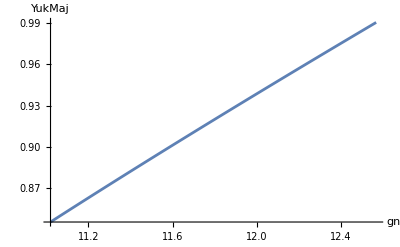

```mathematica
Plot[{fx1[gn]},{gn,11.020272433240335,12.566370614359172},AxesLabel->{gn,YukMaj}]
```

```mathematica
l=0.0001(*l = gn*)
```

0.0001

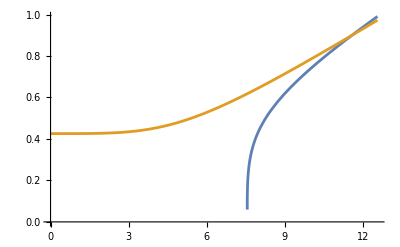

```mathematica
Plot[{fx1[gn],fx2[gn,fx1[gn]]},{gn,0,12.566370614359172}]
```

```mathematica
bn[x1,gn]/.{x1->0.9806395260421711,gn->12}
```

bn[0.98064,12]

```mathematica
Sqrt[(Mh^4+MH2^4+MH3^4+MSDM^4+3 MZPP^4-(3/2 (3 .6^4 v3^4) (*Tr[(hv)⁴ v3⁴*)+3/2 ((.5)^4 (*hf⁴*)+2 (.8)^4 (*hF⁴*)+4 3 (.8)^4 (*hKK⁴*)+2 3 (0.8)^4(*h3Kk⁴*))v4^4))/(64 π^2 vxi^4)]/.alphas/.{Mh->125.4,MH2->1000,MZPP->1000000,MSDM->1500,MH3->1000000}/.{v1->246,v2->10000,v3->10^6,v4->10^6}
```

0.+0.0595638 ⅈ

# Estimative Yukawas

100

```mathematica
rny=RandomReal[{0.8,0.9}];
rnh=RandomReal[{0.3,0.9}];
Yfnum=DiagonalMatrix[{rny,rny,rny}];
hfnum=DiagonalMatrix[{rnh,rnh,rnh}];
```

```mathematica
hfnum
```

{{0.614797,0.,0.},{0.,0.614797,0.},{0.,0.,0.614797}}

```mathematica
Yfnum.Inverse[hfnum].Yfnumᵀ
```

{{1.23836,0.,0.},{0.,1.23836,0.},{0.,0.,1.23836}}

```mathematica
mfdm1=√2 100 IdentityMatrix[3];lv={};For[i=1,i<1000000,i++,mfdm2=√2 100*Yfnum.Inverse[hfnum].Yfnumᵀ ;If[Max[Eigenvalues[mfdm2]]>Max[Eigenvalues[mfdm1]],mfdm1=mfdm2];If[mfdm2>=mfdm1,lv={rny,rnh}];
Yfnum=DiagonalMatrix[{rny,rny,rny}];
hfnum=DiagonalMatrix[{rnh,rnh,rnh}]];
```

```mathematica
rnh
```

0.59187

```mathematica
mfdm2
```

{{175.13,0.,0.},{0.,175.13,0.},{0.,0.,175.13}}

```mathematica
lv
```

{}

```mathematica
0.9897325719164343^-2*1/2 10^4/10^6
```

0.00510428

```mathematica
mfdm1
```

461.566